## Pricing de spreadoption dans QuadriAssetBiSuperHeston

## Presentation du Modele

dS_1=α_11 √v_1 S_1 dW_1+α_12 √v_2 S_1 dW_2+α_13 √v_3 S_1 dW_3+α_14 √v_4 S_1 dW_4+√v_5 S_1 dW_5;
dS_2=α_21 √v_1 S_2 dW_1+α_22 √v_2 S_2 dW_2+α_23 √v_3 S_2 dW_3+α_24 √v_4 S_2 dW_4+√v_6 S_2 dW_6;
dS_3=α_31 √v_1 S_3 dW_1+α_32 √v_2 S_3 dW_2+α_33 √v_3 S_3 dW_3+α_34 √v_4 S_3 dW_4+√v_7 S_3 dW_7;
dS_4=α_41 √v_1 S_4 dW_1+α_42 √v_2 S_4 dW_2+α_43 √v_3 S_4 dW_3+α_44 √v_4 S_4 dW_4+√v_8 S_4 dW_8;

dv_1=λ_1(θ_1-v_1)dt+ ν_1 √v_1 dW_9;
dv_2= λ_2(θ_2-v_2)dt+ν_2 √v_2 dW_10;
dv_3= λ_3(θ_3-v_3)dt+ν_3 √v_3 dW_11;
dv_4= λ_4(θ_4-v_4)dt+ν_4 √v_4 dW_12;
dv_5= λ_5(θ_5-v_5)dt+ν_5 √v_5 dW_13;
dv_6= λ_6(θ_6-v_6)dt+ν_6 √v_6 dW_14;
dv_7= λ_7(θ_7-v_7)dt+ν_7 √v_7 dW_15;
dv_8= λ_8(θ_8-v_8)dt+ν_8 √v_8 dW_16;
dW_1 dW_9=ρ_1 dt;dW_2 dW_10=ρ_2 dt;dW_3 dW_11=ρ_3 dt;dW_4 dW_12=ρ_4 dt;dW_5 dW_13=ρ_5 dt;dW_6 dW_14=ρ_6 dt;dW_7 dW_15=ρ_7 dt;dW_8 dW_16=ρ_8 dt; 
 les autres =0

#### Nombre de parametres

16 alphas + 8*(V0 + ρ + ν) = 40

mais on peut supposer v_1(0)=v_2(0)=v_3(0)=v_4(0)=1

ce qui fait en fait 36 parametres

```mathematica
Decompositionen cahos de Wiener
```

```mathematica
dX(t)=μ dt +σ dW(t)
```

```mathematica
X(t)=x(0)+∫_0^t μⅆs+∫_0^t σⅆ Subscript[W, s]
```

```mathematica
et f(X(t))=f(X(0))+∫_0^t (μ .∇f +1/2 Tr[∇^2 f, σ⊗σ])ⅆs+∫(∇f .σ)ⅆ Subscript[W, s]
```

```mathematica
ce qui reste vrai pour σ
```

```mathematica
σ (t)=f(σ(0))+∫_0^t (μ .∇σ +1/2 Tr[∇^2 σ, σ⊗σ])ⅆs+∫(∇σ .σ)ⅆ Subscript[W, s]
```

```mathematica
ce que on plug dans la formule precedente
```

dS_1=α_11 √v_1 S_1 dW_1;


dv_1=λ_1(θ_1-v_1)dt+ ν_1 √v_1 (ρ dW_1+(1-ρ )dW_2);

```mathematica
ou on a rescalé ν ave √(1-ρ^2)
```

## Observables du generateur de QuadriBisuperheston

#### Correlation des browniens

```mathematica
Corr={
{1,0,0,0,0,0,0,0,rho1,0,0,0,0,0,0,0},
{0,1,0,0,0,0,0,0,0,rho2,0,0,0,0,0,0},
{0,0,1,0,0,0,0,0,0,0,rho3,0,0,0,0,0},
{0,0,0,1,0,0,0,0,0,0,0,rho4,0,0,0,0},
{0,0,0,0,1,0,0,0,0,0,0,0,rho5,0,0,0},
{0,0,0,0,0,1,0,0,0,0,0,0,0,rho6,0,0},
{0,0,0,0,0,0,1,0,0,0,0,0,0,0,rho7,0},
{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,rho8},
{rho1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},
{0,rho2,0,0,0,0,0,0,0,1,0,0,0,0,0,0},
{0,0,rho3,0,0,0,0,0,0,0,1,0,0,0,0,0},
{0,0,0,rho4,0,0,0,0,0,0,0,1,0,0,0,0},
{0,0,0,0,rho5,0,0,0,0,0,0,0,1,0,0,0},
{0,0,0,0,0,rho6,0,0,0,0,0,0,0,1,0,0},
{0,0,0,0,0,0,rho7,0,0,0,0,0,0,0,1,0},
{0,0,0,0,0,0,0,rho8,0,0,0,0,0,0,0,1}
};
```

```mathematica
Mch=Eigensystem[Corr] [[2]]
```

{{-1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,-1,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,-1,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,-1,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,-1,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1}}

```mathematica
Eigens=Eigensystem[Corr] [[1]]
```

{1-rho1,1+rho1,1-rho2,1+rho2,1-rho3,1+rho3,1-rho4,1+rho4,1-rho5,1+rho5,1-rho6,1+rho6,1-rho7,1+rho7,1-rho8,1+rho8}

```mathematica
Mch //MatrixForm
```

(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Clear[S1,S2,S3,S4,V1,V2,V3,V4,V5,V6,V7,V8]
```

#### Gradient des process

```mathematica
Diff[x_]:=
D[x,S1]{alpha11 √V1 S1,alpha12 √V2 S1,alpha13 √V3 S1,alpha14 √V4 S1,√V5 S1,0,0,0,0,0,0,0,0,0,0,0}+
D[x,S2]{alpha21 √V1 S2,alpha22 √V2 S2,alpha23 √V3 S2,alpha24 √V4 S2,0,√V6 S2,0,0,0,0,0,0,0,0,0,0}+
D[x,S3]{alpha31 √V1 S3,alpha32 √V2 S3,alpha33 √V3 S3,alpha34 √V4 S3,0,0,√V7 S3,0,0,0,0,0,0,0,0,0}+
D[x,S4]{alpha41 √V1 S4,alpha42 √V2 S4,alpha43 √V3 S4,alpha44 √V4 S4,0,0,0,√V8 S4,0,0,0,0,0,0,0,0}+

D[x,V1]{0,0,0,0,0,0,0,0,kappaV1 √V1,0,0,0,0,0,0,0}+
D[x,V2]{0,0,0,0,0,0,0,0,0,kappaV2 √V2,0,0,0,0,0,0}+
D[x,V3]{0,0,0,0,0,0,0,0,0,0,kappaV3 √V3,0,0,0,0,0}+
D[x,V4]{0,0,0,0,0,0,0,0,0,0,0,kappaV4 √V4,0,0,0,0}+
D[x,V5]{0,0,0,0,0,0,0,0,0,0,0,0,kappaV5 √V5,0,0,0}+
D[x,V6]{0,0,0,0,0,0,0,0,0,0,0,0,0,kappaV6 √V6,0,0}+
D[x,V7]{0,0,0,0,0,0,0,0,0,0,0,0,0,0,kappaV7 √V7,0}+
D[x,V8]{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,kappaV8 √V8}
```

```mathematica
Diff[S1].Diff[S1]
```

alpha11^2 S1^2 V1+alpha12^2 S1^2 V2+alpha13^2 S1^2 V3+alpha14^2 S1^2 V4+S1^2 V5

```mathematica
Cov={{(Diff[S1]/S1).Corr.(Diff[S1]/S1), (Diff[S1]/S1).Corr.(Diff[S2]/S2), (Diff[S1]/S1).Corr.(Diff[S3]/S3), (Diff[S1]/S1).Corr.(Diff[S4]/S4), (Diff[S1]/S1).Corr.Diff[V1], (Diff[S1]/S1).Corr.Diff[V2], (Diff[S1]/S1).Corr.Diff[V3], (Diff[S1]/S1).Corr.Diff[V4], (Diff[S1]/S1).Corr.Diff[V5], (Diff[S1]/S1).Corr.Diff[V6], (Diff[S1]/S1).Corr.Diff[V7], (Diff[S1]/S1).Corr.Diff[V8]}, {(Diff[S2]/S2).Corr.(Diff[S1]/S1), (Diff[S2]/S2).Corr.(Diff[S2]/S2), (Diff[S2]/S2).Corr.(Diff[S3]/S3), (Diff[S2]/S2).Corr.(Diff[S4]/S4), (Diff[S2]/S2).Corr.Diff[V1], (Diff[S2]/S2).Corr.Diff[V2], (Diff[S2]/S2).Corr.Diff[V3], (Diff[S2]/S2).Corr.Diff[V4], (Diff[S2]/S2).Corr.Diff[V5], (Diff[S2]/S2).Corr.Diff[V6], (Diff[S2]/S2).Corr.Diff[V7], (Diff[S2]/S2).Corr.Diff[V8]}, {(Diff[S3]/S3).Corr.(Diff[S1]/S1), (Diff[S3]/S3).Corr.(Diff[S2]/S2), (Diff[S3]/S3).Corr.(Diff[S3]/S3), (Diff[S3]/S3).Corr.(Diff[S4]/S4), (Diff[S3]/S3).Corr.Diff[V1], (Diff[S3]/S3).Corr.Diff[V2], (Diff[S3]/S3).Corr.Diff[V3], (Diff[S3]/S3).Corr.Diff[V4], (Diff[S3]/S3).Corr.Diff[V5], (Diff[S3]/S3).Corr.Diff[V6], (Diff[S3]/S3).Corr.Diff[V7], (Diff[S3]/S3).Corr.Diff[V8]}, {(Diff[S4]/S4).Corr.(Diff[S1]/S1), (Diff[S4]/S4).Corr.(Diff[S2]/S2), (Diff[S4]/S4).Corr.(Diff[S3]/S3), (Diff[S4]/S4).Corr.(Diff[S4]/S4), (Diff[S4]/S4).Corr.Diff[V1], (Diff[S4]/S4).Corr.Diff[V2], (Diff[S4]/S4).Corr.Diff[V3], (Diff[S4]/S4).Corr.Diff[V4], (Diff[S4]/S4).Corr.Diff[V5], (Diff[S4]/S4).Corr.Diff[V6], (Diff[S4]/S4).Corr.Diff[V7], (Diff[S4]/S4).Corr.Diff[V8]}, {Diff[V1].Corr.(Diff[S1]/S1), Diff[V1].Corr.(Diff[S2]/S2), Diff[V1].Corr.(Diff[S3]/S3), Diff[V1].Corr.(Diff[S4]/S4), Diff[V1].Corr.Diff[V1], Diff[V1].Corr.Diff[V2], Diff[V1].Corr.Diff[V3], Diff[V1].Corr.Diff[V4], Diff[V1].Corr.Diff[V5], Diff[V1].Corr.Diff[V6], Diff[V1].Corr.Diff[V7], Diff[V1].Corr.Diff[V8]}, {Diff[V2].Corr.(Diff[S1]/S1), Diff[V2].Corr.(Diff[S2]/S2), Diff[V2].Corr.(Diff[S3]/S3), Diff[V2].Corr.(Diff[S4]/S4), Diff[V2].Corr.Diff[V1], Diff[V2].Corr.Diff[V2], Diff[V2].Corr.Diff[V3], Diff[V2].Corr.Diff[V4], Diff[V2].Corr.Diff[V5], Diff[V2].Corr.Diff[V6], Diff[V2].Corr.Diff[V7], Diff[V2].Corr.Diff[V8]}, {Diff[V3].Corr.(Diff[S1]/S1), Diff[V3].Corr.(Diff[S2]/S2), Diff[V3].Corr.(Diff[S3]/S3), Diff[V3].Corr.(Diff[S4]/S4), Diff[V3].Corr.Diff[V1], Diff[V3].Corr.Diff[V2], Diff[V3].Corr.Diff[V3], Diff[V3].Corr.Diff[V4], Diff[V3].Corr.Diff[V5], Diff[V3].Corr.Diff[V6], Diff[V3].Corr.Diff[V7], Diff[V3].Corr.Diff[V8]}, {Diff[V4].Corr.(Diff[S1]/S1), Diff[V4].Corr.(Diff[S2]/S2), Diff[V4].Corr.(Diff[S3]/S3), Diff[V4].Corr.(Diff[S4]/S4), Diff[V4].Corr.Diff[V1], Diff[V4].Corr.Diff[V2], Diff[V4].Corr.Diff[V3], Diff[V4].Corr.Diff[V4], Diff[V4].Corr.Diff[V5], Diff[V4].Corr.Diff[V6], Diff[V4].Corr.Diff[V7], Diff[V4].Corr.Diff[V8]}, {Diff[V5].Corr.(Diff[S1]/S1), Diff[V5].Corr.(Diff[S2]/S2), Diff[V5].Corr.(Diff[S3]/S3), Diff[V5].Corr.(Diff[S4]/S4), Diff[V5].Corr.Diff[V1], Diff[V5].Corr.Diff[V2], Diff[V5].Corr.Diff[V3], Diff[V5].Corr.Diff[V4], Diff[V5].Corr.Diff[V5], Diff[V5].Corr.Diff[V6], Diff[V5].Corr.Diff[V7], Diff[V5].Corr.Diff[V8]}, {Diff[V6].Corr.(Diff[S1]/S1), Diff[V6].Corr.(Diff[S2]/S2), Diff[V6].Corr.(Diff[S3]/S3), Diff[V6].Corr.(Diff[S4]/S4), Diff[V6].Corr.Diff[V1], Diff[V6].Corr.Diff[V2], Diff[V6].Corr.Diff[V3], Diff[V6].Corr.Diff[V4], Diff[V6].Corr.Diff[V5], Diff[V6].Corr.Diff[V6], Diff[V6].Corr.Diff[V7], Diff[V6].Corr.Diff[V8]}, {Diff[V7].Corr.(Diff[S1]/S1), Diff[V7].Corr.(Diff[S2]/S2), Diff[V7].Corr.(Diff[S3]/S3), Diff[V7].Corr.(Diff[S4]/S4), Diff[V7].Corr.Diff[V1], Diff[V7].Corr.Diff[V2], Diff[V7].Corr.Diff[V3], Diff[V7].Corr.Diff[V4], Diff[V7].Corr.Diff[V5], Diff[V7].Corr.Diff[V6], Diff[V7].Corr.Diff[V7], Diff[V7].Corr.Diff[V8]}, {Diff[V8].Corr.(Diff[S1]/S1), Diff[V8].Corr.(Diff[S2]/S2), Diff[V8].Corr.(Diff[S3]/S3), Diff[V8].Corr.(Diff[S4]/S4), Diff[V8].Corr.Diff[V1], Diff[V8].Corr.Diff[V2], Diff[V8].Corr.Diff[V3], Diff[V8].Corr.Diff[V4], Diff[V8].Corr.Diff[V5], Diff[V8].Corr.Diff[V6], Diff[V8].Corr.Diff[V7], Diff[V8].Corr.Diff[V8]}};
```

```mathematica
Cov //MatrixForm
```

(alpha11^2 V1+alpha12^2 V2+alpha13^2 V3+alpha14^2 V4+V5 | alpha11 alpha21 V1+alpha12 alpha22 V2+alpha13 alpha23 V3+alpha14 alpha24 V4 | alpha11 alpha31 V1+alpha12 alpha32 V2+alpha13 alpha33 V3+alpha14 alpha34 V4 | alpha11 alpha41 V1+alpha12 alpha42 V2+alpha13 alpha43 V3+alpha14 alpha44 V4 | alpha11 kappaV1 rho1 V1 | alpha12 kappaV2 rho2 V2 | alpha13 kappaV3 rho3 V3 | alpha14 kappaV4 rho4 V4 | kappaV5 rho5 V5 | 0 | 0 | 0
alpha11 alpha21 V1+alpha12 alpha22 V2+alpha13 alpha23 V3+alpha14 alpha24 V4 | alpha21^2 V1+alpha22^2 V2+alpha23^2 V3+alpha24^2 V4+V6 | alpha21 alpha31 V1+alpha22 alpha32 V2+alpha23 alpha33 V3+alpha24 alpha34 V4 | alpha21 alpha41 V1+alpha22 alpha42 V2+alpha23 alpha43 V3+alpha24 alpha44 V4 | alpha21 kappaV1 rho1 V1 | alpha22 kappaV2 rho2 V2 | alpha23 kappaV3 rho3 V3 | alpha24 kappaV4 rho4 V4 | 0 | kappaV6 rho6 V6 | 0 | 0
alpha11 alpha31 V1+alpha12 alpha32 V2+alpha13 alpha33 V3+alpha14 alpha34 V4 | alpha21 alpha31 V1+alpha22 alpha32 V2+alpha23 alpha33 V3+alpha24 alpha34 V4 | alpha31^2 V1+alpha32^2 V2+alpha33^2 V3+alpha34^2 V4+V7 | alpha31 alpha41 V1+alpha32 alpha42 V2+alpha33 alpha43 V3+alpha34 alpha44 V4 | alpha31 kappaV1 rho1 V1 | alpha32 kappaV2 rho2 V2 | alpha33 kappaV3 rho3 V3 | alpha34 kappaV4 rho4 V4 | 0 | 0 | kappaV7 rho7 V7 | 0
alpha11 alpha41 V1+alpha12 alpha42 V2+alpha13 alpha43 V3+alpha14 alpha44 V4 | alpha21 alpha41 V1+alpha22 alpha42 V2+alpha23 alpha43 V3+alpha24 alpha44 V4 | alpha31 alpha41 V1+alpha32 alpha42 V2+alpha33 alpha43 V3+alpha34 alpha44 V4 | alpha41^2 V1+alpha42^2 V2+alpha43^2 V3+alpha44^2 V4+V8 | alpha41 kappaV1 rho1 V1 | alpha42 kappaV2 rho2 V2 | alpha43 kappaV3 rho3 V3 | alpha44 kappaV4 rho4 V4 | 0 | 0 | 0 | kappaV8 rho8 V8
alpha11 kappaV1 rho1 V1 | alpha21 kappaV1 rho1 V1 | alpha31 kappaV1 rho1 V1 | alpha41 kappaV1 rho1 V1 | kappaV1^2 V1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
alpha12 kappaV2 rho2 V2 | alpha22 kappaV2 rho2 V2 | alpha32 kappaV2 rho2 V2 | alpha42 kappaV2 rho2 V2 | 0 | kappaV2^2 V2 | 0 | 0 | 0 | 0 | 0 | 0
alpha13 kappaV3 rho3 V3 | alpha23 kappaV3 rho3 V3 | alpha33 kappaV3 rho3 V3 | alpha43 kappaV3 rho3 V3 | 0 | 0 | kappaV3^2 V3 | 0 | 0 | 0 | 0 | 0
alpha14 kappaV4 rho4 V4 | alpha24 kappaV4 rho4 V4 | alpha34 kappaV4 rho4 V4 | alpha44 kappaV4 rho4 V4 | 0 | 0 | 0 | kappaV4^2 V4 | 0 | 0 | 0 | 0
kappaV5 rho5 V5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | kappaV5^2 V5 | 0 | 0 | 0
0 | kappaV6 rho6 V6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | kappaV6^2 V6 | 0 | 0
0 | 0 | kappaV7 rho7 V7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | kappaV7^2 V7 | 0
0 | 0 | 0 | kappaV8 rho8 V8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | kappaV8^2 V8)

## Calcul des observables (VS, VarVS, COVarSVS)

#### Spread 1 - 2

```mathematica
VS12=Simplify[Diff[S1-S2].(Corr.Diff[S1-S2])]
```

(alpha11 S1-alpha21 S2)^2 V1+(alpha12 S1-alpha22 S2)^2 V2+(alpha13 S1-alpha23 S2)^2 V3+(alpha14 S1-alpha24 S2)^2 V4+S1^2 V5+S2^2 V6

```mathematica
VarVS12=Simplify[Diff[VS12].(Corr.Diff[VS12])];
```

```mathematica
VarVS120=Simplify[Diff[VS12].(Corr.Diff[VS12])]/.{kappaV1->0,kappaV2->0,kappaV3->0,kappaV4->0,kappaV5->0,kappaV6->0,kappaV7->0,kappaV8->0}
```

2 S1^2 V5 (alpha11 (alpha11 S1-alpha21 S2) V1+alpha12 (alpha12 S1-alpha22 S2) V2+alpha13 (alpha13 S1-alpha23 S2) V3+alpha14 (alpha14 S1-alpha24 S2) V4+S1 V5) (2 alpha11 (alpha11 S1-alpha21 S2) V1+2 alpha12 (alpha12 S1-alpha22 S2) V2+2 alpha13 (alpha13 S1-alpha23 S2) V3+2 alpha14 (alpha14 S1-alpha24 S2) V4+2 S1 V5)+4 S2^2 V6 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6)^2+V1 (2 alpha11 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha21 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6))^2+V2 (2 alpha12 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha22 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6))^2+V3 (2 alpha13 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha23 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6))^2+V4 (2 alpha14 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha24 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6))^2

```mathematica
Simplify[VarVS12-(VarVS12 /.{kappaV1->0,kappaV2->0,kappaV3->0,kappaV4->0,kappaV5->0,kappaV6->0,kappaV7->0,kappaV8->0})]
```

-4 S1^2 V5 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)^2+2 S1^2 V5 (alpha11 (alpha11 S1-alpha21 S2) V1+alpha12 (alpha12 S1-alpha22 S2) V2+alpha13 (alpha13 S1-alpha23 S2) V3+alpha14 (alpha14 S1-alpha24 S2) V4+S1 V5) (kappaV5 rho5 S1+2 alpha11 (alpha11 S1-alpha21 S2) V1+2 alpha12 (alpha12 S1-alpha22 S2) V2+2 alpha13 (alpha13 S1-alpha23 S2) V3+2 alpha14 (alpha14 S1-alpha24 S2) V4+2 S1 V5)+kappaV5 S1^3 V5 (kappaV5 S1+2 rho5 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5))-4 S2^2 V6 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6)^2+2 S2^2 V6 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6) (kappaV6 rho6 S2+2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6))+kappaV6 S2^3 V6 (kappaV6 S2+2 rho6 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6))-V1 (2 alpha11 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha21 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6))^2+V1 (2 alpha11 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha21 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6)) (kappaV1 rho1 (alpha11 S1-alpha21 S2)^2+2 alpha11 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha21 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6))-V2 (2 alpha12 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha22 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6))^2+V2 (2 alpha12 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha22 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6)) (kappaV2 rho2 (alpha12 S1-alpha22 S2)^2+2 alpha12 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha22 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6))-V3 (2 alpha13 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha23 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6))^2+V3 (2 alpha13 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha23 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6)) (kappaV3 rho3 (alpha13 S1-alpha23 S2)^2+2 alpha13 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha23 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6))-V4 (2 alpha14 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha24 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6))^2+V4 (2 alpha14 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha24 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6)) (kappaV4 rho4 (alpha14 S1-alpha24 S2)^2+2 alpha14 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha24 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6))+kappaV1 (alpha11 S1-alpha21 S2)^2 V1 (kappaV1 (alpha11 S1-alpha21 S2)^2+rho1 (2 alpha11 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha21 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6)))+kappaV2 (alpha12 S1-alpha22 S2)^2 V2 (kappaV2 (alpha12 S1-alpha22 S2)^2+rho2 (2 alpha12 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha22 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6)))+kappaV3 (alpha13 S1-alpha23 S2)^2 V3 (kappaV3 (alpha13 S1-alpha23 S2)^2+rho3 (2 alpha13 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha23 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6)))+kappaV4 (alpha14 S1-alpha24 S2)^2 V4 (kappaV4 (alpha14 S1-alpha24 S2)^2+rho4 (2 alpha14 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha24 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6)))

```mathematica
CoVarSVS12=Simplify[Diff[VS12].(Corr.Diff[S1-S2])]
```

kappaV1 rho1 (alpha11 S1-alpha21 S2)^3 V1+kappaV2 rho2 (alpha12 S1-alpha22 S2)^3 V2+kappaV3 rho3 (alpha13 S1-alpha23 S2)^3 V3+kappaV4 rho4 (alpha14 S1-alpha24 S2)^3 V4+kappaV5 rho5 S1^3 V5+2 S1^2 V5 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)-kappaV6 rho6 S2^3 V6-2 S2^2 V6 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6)+(alpha11 S1-alpha21 S2) V1 (2 alpha11 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha21 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6))+(alpha12 S1-alpha22 S2) V2 (2 alpha12 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha22 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6))+(alpha13 S1-alpha23 S2) V3 (2 alpha13 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha23 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6))+(alpha14 S1-alpha24 S2) V4 (2 alpha14 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha24 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6))

```mathematica
Simplify[CoVarSVS12-(CoVarSVS12 /.{kappaV1->0,kappaV2->0,kappaV3->0,kappaV4->0,kappaV5->0,kappaV6->0,kappaV7->0,kappaV8->0})]
```

kappaV1 rho1 (alpha11 S1-alpha21 S2)^3 V1+kappaV2 rho2 (alpha12 S1-alpha22 S2)^3 V2+kappaV3 rho3 (alpha13 S1-alpha23 S2)^3 V3+kappaV4 rho4 (alpha14 S1-alpha24 S2)^3 V4+kappaV5 rho5 S1^3 V5-kappaV6 rho6 S2^3 V6

```mathematica
QuadriBiSuperHestonSpreadObservable12[S1_,S2_,S3_,S4_,
alpha11_,alpha12_,alpha13_,alpha14_,
alpha21_,alpha22_,alpha23_,alpha24_,
alpha31_,alpha32_,alpha33_,alpha34_,
alpha41_,alpha42_,alpha43_,alpha44_,
rho1_,kappaV1_,V1_,
rho2_,kappaV2_,V2_,
rho3_,kappaV3_,V3_,
rho4_,kappaV4_,V4_,
rho5_,kappaV5_,V5_,
rho6_,kappaV6_,V6_,
rho7_,kappaV7_,V7_,
rho8_,kappaV8_,V8_]:={(alpha11 S1-alpha21 S2)^2 V1+(alpha12 S1-alpha22 S2)^2 V2+(alpha13 S1-alpha23 S2)^2 V3+(alpha14 S1-alpha24 S2)^2 V4+S1^2 V5+S2^2 V6,
-4 S1^2 V5 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)^2+2 S1^2 V5 (alpha11 (alpha11 S1-alpha21 S2) V1+alpha12 (alpha12 S1-alpha22 S2) V2+alpha13 (alpha13 S1-alpha23 S2) V3+alpha14 (alpha14 S1-alpha24 S2) V4+S1 V5) (kappaV5 rho5 S1+2 alpha11 (alpha11 S1-alpha21 S2) V1+2 alpha12 (alpha12 S1-alpha22 S2) V2+2 alpha13 (alpha13 S1-alpha23 S2) V3+2 alpha14 (alpha14 S1-alpha24 S2) V4+2 S1 V5)+kappaV5 S1^3 V5 (kappaV5 S1+2 rho5 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5))-4 S2^2 V6 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6)^2+2 S2^2 V6 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6) (kappaV6 rho6 S2+2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6))+kappaV6 S2^3 V6 (kappaV6 S2+2 rho6 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6))-V1 (2 alpha11 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha21 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6))^2+V1 (2 alpha11 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha21 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6)) (kappaV1 rho1 (alpha11 S1-alpha21 S2)^2+2 alpha11 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha21 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6))-V2 (2 alpha12 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha22 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6))^2+V2 (2 alpha12 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha22 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6)) (kappaV2 rho2 (alpha12 S1-alpha22 S2)^2+2 alpha12 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha22 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6))-V3 (2 alpha13 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha23 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6))^2+V3 (2 alpha13 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha23 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6)) (kappaV3 rho3 (alpha13 S1-alpha23 S2)^2+2 alpha13 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha23 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6))-V4 (2 alpha14 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha24 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6))^2+V4 (2 alpha14 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha24 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6)) (kappaV4 rho4 (alpha14 S1-alpha24 S2)^2+2 alpha14 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha24 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6))+kappaV1 (alpha11 S1-alpha21 S2)^2 V1 (kappaV1 (alpha11 S1-alpha21 S2)^2+rho1 (2 alpha11 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha21 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6)))+kappaV2 (alpha12 S1-alpha22 S2)^2 V2 (kappaV2 (alpha12 S1-alpha22 S2)^2+rho2 (2 alpha12 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha22 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6)))+kappaV3 (alpha13 S1-alpha23 S2)^2 V3 (kappaV3 (alpha13 S1-alpha23 S2)^2+rho3 (2 alpha13 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha23 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6)))+kappaV4 (alpha14 S1-alpha24 S2)^2 V4 (kappaV4 (alpha14 S1-alpha24 S2)^2+rho4 (2 alpha14 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha24 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6))),
kappaV1 rho1 (alpha11 S1-alpha21 S2)^3 V1+kappaV2 rho2 (alpha12 S1-alpha22 S2)^3 V2+kappaV3 rho3 (alpha13 S1-alpha23 S2)^3 V3+kappaV4 rho4 (alpha14 S1-alpha24 S2)^3 V4+kappaV5 rho5 S1^3 V5-kappaV6 rho6 S2^3 V6
}
```

#### Spread 1 - 3

```mathematica
VS13=Simplify[Diff[S1-S3].(Corr.Diff[S1-S3])]
```

(alpha11 S1-alpha31 S3)^2 V1+(alpha12 S1-alpha32 S3)^2 V2+(alpha13 S1-alpha33 S3)^2 V3+(alpha14 S1-alpha34 S3)^2 V4+S1^2 V5+S3^2 V7

```mathematica
VarVS13=Simplify[Diff[VS13].(Corr.Diff[VS13])]
```

2 S1^2 V5 (alpha11 (alpha11 S1-alpha31 S3) V1+alpha12 (alpha12 S1-alpha32 S3) V2+alpha13 (alpha13 S1-alpha33 S3) V3+alpha14 (alpha14 S1-alpha34 S3) V4+S1 V5) (kappaV5 rho5 S1+2 alpha11 (alpha11 S1-alpha31 S3) V1+2 alpha12 (alpha12 S1-alpha32 S3) V2+2 alpha13 (alpha13 S1-alpha33 S3) V3+2 alpha14 (alpha14 S1-alpha34 S3) V4+2 S1 V5)+kappaV5 S1^3 V5 (kappaV5 S1+2 rho5 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5))+2 S3^2 V7 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7) (kappaV7 rho7 S3+2 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7))+kappaV7 S3^3 V7 (kappaV7 S3+2 rho7 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7))+V1 (2 alpha11 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha31 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7)) (kappaV1 rho1 (alpha11 S1-alpha31 S3)^2+2 alpha11 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha31 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7))+V2 (2 alpha12 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha32 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7)) (kappaV2 rho2 (alpha12 S1-alpha32 S3)^2+2 alpha12 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha32 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7))+V3 (2 alpha13 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha33 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7)) (kappaV3 rho3 (alpha13 S1-alpha33 S3)^2+2 alpha13 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha33 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7))+V4 (2 alpha14 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha34 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7)) (kappaV4 rho4 (alpha14 S1-alpha34 S3)^2+2 alpha14 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha34 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7))+kappaV1 (alpha11 S1-alpha31 S3)^2 V1 (kappaV1 (alpha11 S1-alpha31 S3)^2+rho1 (2 alpha11 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha31 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7)))+kappaV2 (alpha12 S1-alpha32 S3)^2 V2 (kappaV2 (alpha12 S1-alpha32 S3)^2+rho2 (2 alpha12 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha32 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7)))+kappaV3 (alpha13 S1-alpha33 S3)^2 V3 (kappaV3 (alpha13 S1-alpha33 S3)^2+rho3 (2 alpha13 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha33 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7)))+kappaV4 (alpha14 S1-alpha34 S3)^2 V4 (kappaV4 (alpha14 S1-alpha34 S3)^2+rho4 (2 alpha14 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha34 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7)))

```mathematica
Simplify[VarVS13-(VarVS13 /.{kappaV1->0,kappaV2->0,kappaV3->0,kappaV4->0,kappaV5->0,kappaV6->0,kappaV7->0,kappaV8->0})]
```

-4 S1^2 V5 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)^2+2 S1^2 V5 (alpha11 (alpha11 S1-alpha31 S3) V1+alpha12 (alpha12 S1-alpha32 S3) V2+alpha13 (alpha13 S1-alpha33 S3) V3+alpha14 (alpha14 S1-alpha34 S3) V4+S1 V5) (kappaV5 rho5 S1+2 alpha11 (alpha11 S1-alpha31 S3) V1+2 alpha12 (alpha12 S1-alpha32 S3) V2+2 alpha13 (alpha13 S1-alpha33 S3) V3+2 alpha14 (alpha14 S1-alpha34 S3) V4+2 S1 V5)+kappaV5 S1^3 V5 (kappaV5 S1+2 rho5 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5))-4 S3^2 V7 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7)^2+2 S3^2 V7 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7) (kappaV7 rho7 S3+2 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7))+kappaV7 S3^3 V7 (kappaV7 S3+2 rho7 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7))-V1 (2 alpha11 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha31 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7))^2+V1 (2 alpha11 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha31 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7)) (kappaV1 rho1 (alpha11 S1-alpha31 S3)^2+2 alpha11 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha31 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7))-V2 (2 alpha12 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha32 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7))^2+V2 (2 alpha12 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha32 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7)) (kappaV2 rho2 (alpha12 S1-alpha32 S3)^2+2 alpha12 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha32 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7))-V3 (2 alpha13 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha33 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7))^2+V3 (2 alpha13 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha33 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7)) (kappaV3 rho3 (alpha13 S1-alpha33 S3)^2+2 alpha13 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha33 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7))-V4 (2 alpha14 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha34 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7))^2+V4 (2 alpha14 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha34 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7)) (kappaV4 rho4 (alpha14 S1-alpha34 S3)^2+2 alpha14 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha34 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7))+kappaV1 (alpha11 S1-alpha31 S3)^2 V1 (kappaV1 (alpha11 S1-alpha31 S3)^2+rho1 (2 alpha11 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha31 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7)))+kappaV2 (alpha12 S1-alpha32 S3)^2 V2 (kappaV2 (alpha12 S1-alpha32 S3)^2+rho2 (2 alpha12 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha32 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7)))+kappaV3 (alpha13 S1-alpha33 S3)^2 V3 (kappaV3 (alpha13 S1-alpha33 S3)^2+rho3 (2 alpha13 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha33 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7)))+kappaV4 (alpha14 S1-alpha34 S3)^2 V4 (kappaV4 (alpha14 S1-alpha34 S3)^2+rho4 (2 alpha14 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha34 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7)))

```mathematica
CoVarSVS13=Simplify[Diff[VS13].(Corr.Diff[S1-S3])]
```

kappaV1 rho1 (alpha11 S1-alpha31 S3)^3 V1+kappaV2 rho2 (alpha12 S1-alpha32 S3)^3 V2+kappaV3 rho3 (alpha13 S1-alpha33 S3)^3 V3+kappaV4 rho4 (alpha14 S1-alpha34 S3)^3 V4+kappaV5 rho5 S1^3 V5+2 S1^2 V5 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)-kappaV7 rho7 S3^3 V7-2 S3^2 V7 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7)+(alpha11 S1-alpha31 S3) V1 (2 alpha11 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha31 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7))+(alpha12 S1-alpha32 S3) V2 (2 alpha12 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha32 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7))+(alpha13 S1-alpha33 S3) V3 (2 alpha13 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha33 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7))+(alpha14 S1-alpha34 S3) V4 (2 alpha14 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha34 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7))

```mathematica
Simplify[CoVarSVS13-(CoVarSVS13 /.{kappaV1->0,kappaV2->0,kappaV3->0,kappaV4->0,kappaV5->0,kappaV6->0,kappaV7->0,kappaV8->0})]
```

kappaV1 rho1 (alpha11 S1-alpha31 S3)^3 V1+kappaV2 rho2 (alpha12 S1-alpha32 S3)^3 V2+kappaV3 rho3 (alpha13 S1-alpha33 S3)^3 V3+kappaV4 rho4 (alpha14 S1-alpha34 S3)^3 V4+kappaV5 rho5 S1^3 V5-kappaV7 rho7 S3^3 V7

```mathematica
QuadriBiSuperHestonSpreadObservable13[S1_,S2_,S3_,S4_,
alpha11_,alpha12_,alpha13_,alpha14_,
alpha21_,alpha22_,alpha23_,alpha24_,
alpha31_,alpha32_,alpha33_,alpha34_,
alpha41_,alpha42_,alpha43_,alpha44_,
rho1_,kappaV1_,V1_,
rho2_,kappaV2_,V2_,
rho3_,kappaV3_,V3_,
rho4_,kappaV4_,V4_,
rho5_,kappaV5_,V5_,
rho6_,kappaV6_,V6_,
rho7_,kappaV7_,V7_,
rho8_,kappaV8_,V8_]:={
(alpha11 S1-alpha31 S3)^2 V1+(alpha12 S1-alpha32 S3)^2 V2+(alpha13 S1-alpha33 S3)^2 V3+(alpha14 S1-alpha34 S3)^2 V4+S1^2 V5+S3^2 V7,
-4 S1^2 V5 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)^2+2 S1^2 V5 (alpha11 (alpha11 S1-alpha31 S3) V1+alpha12 (alpha12 S1-alpha32 S3) V2+alpha13 (alpha13 S1-alpha33 S3) V3+alpha14 (alpha14 S1-alpha34 S3) V4+S1 V5) (kappaV5 rho5 S1+2 alpha11 (alpha11 S1-alpha31 S3) V1+2 alpha12 (alpha12 S1-alpha32 S3) V2+2 alpha13 (alpha13 S1-alpha33 S3) V3+2 alpha14 (alpha14 S1-alpha34 S3) V4+2 S1 V5)+kappaV5 S1^3 V5 (kappaV5 S1+2 rho5 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5))-4 S3^2 V7 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7)^2+2 S3^2 V7 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7) (kappaV7 rho7 S3+2 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7))+kappaV7 S3^3 V7 (kappaV7 S3+2 rho7 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7))-V1 (2 alpha11 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha31 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7))^2+V1 (2 alpha11 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha31 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7)) (kappaV1 rho1 (alpha11 S1-alpha31 S3)^2+2 alpha11 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha31 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7))-V2 (2 alpha12 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha32 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7))^2+V2 (2 alpha12 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha32 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7)) (kappaV2 rho2 (alpha12 S1-alpha32 S3)^2+2 alpha12 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha32 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7))-V3 (2 alpha13 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha33 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7))^2+V3 (2 alpha13 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha33 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7)) (kappaV3 rho3 (alpha13 S1-alpha33 S3)^2+2 alpha13 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha33 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7))-V4 (2 alpha14 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha34 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7))^2+V4 (2 alpha14 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha34 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7)) (kappaV4 rho4 (alpha14 S1-alpha34 S3)^2+2 alpha14 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha34 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7))+kappaV1 (alpha11 S1-alpha31 S3)^2 V1 (kappaV1 (alpha11 S1-alpha31 S3)^2+rho1 (2 alpha11 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha31 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7)))+kappaV2 (alpha12 S1-alpha32 S3)^2 V2 (kappaV2 (alpha12 S1-alpha32 S3)^2+rho2 (2 alpha12 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha32 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7)))+kappaV3 (alpha13 S1-alpha33 S3)^2 V3 (kappaV3 (alpha13 S1-alpha33 S3)^2+rho3 (2 alpha13 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha33 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7)))+kappaV4 (alpha14 S1-alpha34 S3)^2 V4 (kappaV4 (alpha14 S1-alpha34 S3)^2+rho4 (2 alpha14 S1 (alpha11^2 S1 V1-alpha11 alpha31 S3 V1+alpha12^2 S1 V2-alpha12 alpha32 S3 V2+alpha13^2 S1 V3-alpha13 alpha33 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S3 V4+S1 V5)+2 alpha34 S3 (-alpha11 alpha31 S1 V1+alpha31^2 S3 V1-alpha12 alpha32 S1 V2+alpha32^2 S3 V2-alpha13 alpha33 S1 V3+alpha33^2 S3 V3-alpha14 alpha34 S1 V4+alpha34^2 S3 V4+S3 V7))),
kappaV1 rho1 (alpha11 S1-alpha31 S3)^3 V1+kappaV2 rho2 (alpha12 S1-alpha32 S3)^3 V2+kappaV3 rho3 (alpha13 S1-alpha33 S3)^3 V3+kappaV4 rho4 (alpha14 S1-alpha34 S3)^3 V4+kappaV5 rho5 S1^3 V5-kappaV7 rho7 S3^3 V7
}
```

#### Spread 1 - 4

```mathematica
VS14=Simplify[Diff[S1-S4].(Corr.Diff[S1-S4])]
```

(alpha11 S1-alpha41 S4)^2 V1+(alpha12 S1-alpha42 S4)^2 V2+(alpha13 S1-alpha43 S4)^2 V3+(alpha14 S1-alpha44 S4)^2 V4+S1^2 V5+S4^2 V8

```mathematica
VarVS14=Simplify[Diff[VS14].(Corr.Diff[VS14])]
```

2 S1^2 V5 (alpha11 (alpha11 S1-alpha41 S4) V1+alpha12 (alpha12 S1-alpha42 S4) V2+alpha13 (alpha13 S1-alpha43 S4) V3+alpha14 (alpha14 S1-alpha44 S4) V4+S1 V5) (kappaV5 rho5 S1+2 alpha11 (alpha11 S1-alpha41 S4) V1+2 alpha12 (alpha12 S1-alpha42 S4) V2+2 alpha13 (alpha13 S1-alpha43 S4) V3+2 alpha14 (alpha14 S1-alpha44 S4) V4+2 S1 V5)+kappaV5 S1^3 V5 (kappaV5 S1+2 rho5 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5))+2 S4^2 V8 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8) (kappaV8 rho8 S4+2 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8))+kappaV8 S4^3 V8 (kappaV8 S4+2 rho8 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8))+V1 (2 alpha11 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha41 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8)) (kappaV1 rho1 (alpha11 S1-alpha41 S4)^2+2 alpha11 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha41 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8))+V2 (2 alpha12 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha42 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8)) (kappaV2 rho2 (alpha12 S1-alpha42 S4)^2+2 alpha12 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha42 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8))+V3 (2 alpha13 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha43 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8)) (kappaV3 rho3 (alpha13 S1-alpha43 S4)^2+2 alpha13 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha43 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8))+V4 (2 alpha14 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha44 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8)) (kappaV4 rho4 (alpha14 S1-alpha44 S4)^2+2 alpha14 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha44 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8))+kappaV1 (alpha11 S1-alpha41 S4)^2 V1 (kappaV1 (alpha11 S1-alpha41 S4)^2+rho1 (2 alpha11 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha41 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8)))+kappaV2 (alpha12 S1-alpha42 S4)^2 V2 (kappaV2 (alpha12 S1-alpha42 S4)^2+rho2 (2 alpha12 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha42 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8)))+kappaV3 (alpha13 S1-alpha43 S4)^2 V3 (kappaV3 (alpha13 S1-alpha43 S4)^2+rho3 (2 alpha13 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha43 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8)))+kappaV4 (alpha14 S1-alpha44 S4)^2 V4 (kappaV4 (alpha14 S1-alpha44 S4)^2+rho4 (2 alpha14 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha44 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8)))

```mathematica
Simplify[VarVS14-(VarVS14 /.{kappaV1->0,kappaV2->0,kappaV3->0,kappaV4->0,kappaV5->0,kappaV6->0,kappaV7->0,kappaV8->0})]
```

-4 S1^2 V5 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)^2+2 S1^2 V5 (alpha11 (alpha11 S1-alpha41 S4) V1+alpha12 (alpha12 S1-alpha42 S4) V2+alpha13 (alpha13 S1-alpha43 S4) V3+alpha14 (alpha14 S1-alpha44 S4) V4+S1 V5) (kappaV5 rho5 S1+2 alpha11 (alpha11 S1-alpha41 S4) V1+2 alpha12 (alpha12 S1-alpha42 S4) V2+2 alpha13 (alpha13 S1-alpha43 S4) V3+2 alpha14 (alpha14 S1-alpha44 S4) V4+2 S1 V5)+kappaV5 S1^3 V5 (kappaV5 S1+2 rho5 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5))-4 S4^2 V8 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8)^2+2 S4^2 V8 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8) (kappaV8 rho8 S4+2 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8))+kappaV8 S4^3 V8 (kappaV8 S4+2 rho8 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8))-V1 (2 alpha11 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha41 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8))^2+V1 (2 alpha11 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha41 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8)) (kappaV1 rho1 (alpha11 S1-alpha41 S4)^2+2 alpha11 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha41 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8))-V2 (2 alpha12 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha42 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8))^2+V2 (2 alpha12 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha42 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8)) (kappaV2 rho2 (alpha12 S1-alpha42 S4)^2+2 alpha12 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha42 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8))-V3 (2 alpha13 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha43 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8))^2+V3 (2 alpha13 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha43 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8)) (kappaV3 rho3 (alpha13 S1-alpha43 S4)^2+2 alpha13 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha43 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8))-V4 (2 alpha14 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha44 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8))^2+V4 (2 alpha14 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha44 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8)) (kappaV4 rho4 (alpha14 S1-alpha44 S4)^2+2 alpha14 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha44 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8))+kappaV1 (alpha11 S1-alpha41 S4)^2 V1 (kappaV1 (alpha11 S1-alpha41 S4)^2+rho1 (2 alpha11 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha41 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8)))+kappaV2 (alpha12 S1-alpha42 S4)^2 V2 (kappaV2 (alpha12 S1-alpha42 S4)^2+rho2 (2 alpha12 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha42 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8)))+kappaV3 (alpha13 S1-alpha43 S4)^2 V3 (kappaV3 (alpha13 S1-alpha43 S4)^2+rho3 (2 alpha13 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha43 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8)))+kappaV4 (alpha14 S1-alpha44 S4)^2 V4 (kappaV4 (alpha14 S1-alpha44 S4)^2+rho4 (2 alpha14 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha44 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8)))

```mathematica
CoVarSVS14=Simplify[Diff[VS14].(Corr.Diff[S1-S4])]
```

kappaV1 rho1 (alpha11 S1-alpha41 S4)^3 V1+kappaV2 rho2 (alpha12 S1-alpha42 S4)^3 V2+kappaV3 rho3 (alpha13 S1-alpha43 S4)^3 V3+kappaV4 rho4 (alpha14 S1-alpha44 S4)^3 V4+kappaV5 rho5 S1^3 V5+2 S1^2 V5 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)-kappaV8 rho8 S4^3 V8-2 S4^2 V8 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8)+(alpha11 S1-alpha41 S4) V1 (2 alpha11 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha41 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8))+(alpha12 S1-alpha42 S4) V2 (2 alpha12 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha42 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8))+(alpha13 S1-alpha43 S4) V3 (2 alpha13 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha43 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8))+(alpha14 S1-alpha44 S4) V4 (2 alpha14 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha44 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8))

```mathematica
Simplify[CoVarSVS14 -(CoVarSVS14/.{kappaV1->0,kappaV2->0,kappaV3->0,kappaV4->0,kappaV5->0,kappaV6->0,kappaV7->0,kappaV8->0})]
```

kappaV1 rho1 (alpha11 S1-alpha41 S4)^3 V1+kappaV2 rho2 (alpha12 S1-alpha42 S4)^3 V2+kappaV3 rho3 (alpha13 S1-alpha43 S4)^3 V3+kappaV4 rho4 (alpha14 S1-alpha44 S4)^3 V4+kappaV5 rho5 S1^3 V5-kappaV8 rho8 S4^3 V8

```mathematica
QuadriBiSuperHestonSpreadObservable14[S1_,S2_,S3_,S4_,
alpha11_,alpha12_,alpha13_,alpha14_,
alpha21_,alpha22_,alpha23_,alpha24_,
alpha31_,alpha32_,alpha33_,alpha34_,
alpha41_,alpha42_,alpha43_,alpha44_,
rho1_,kappaV1_,V1_,
rho2_,kappaV2_,V2_,
rho3_,kappaV3_,V3_,
rho4_,kappaV4_,V4_,
rho5_,kappaV5_,V5_,
rho6_,kappaV6_,V6_,
rho7_,kappaV7_,V7_,
rho8_,kappaV8_,V8_]:={
(alpha11 S1-alpha41 S4)^2 V1+(alpha12 S1-alpha42 S4)^2 V2+(alpha13 S1-alpha43 S4)^2 V3+(alpha14 S1-alpha44 S4)^2 V4+S1^2 V5+S4^2 V8,
-4 S1^2 V5 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)^2+2 S1^2 V5 (alpha11 (alpha11 S1-alpha41 S4) V1+alpha12 (alpha12 S1-alpha42 S4) V2+alpha13 (alpha13 S1-alpha43 S4) V3+alpha14 (alpha14 S1-alpha44 S4) V4+S1 V5) (kappaV5 rho5 S1+2 alpha11 (alpha11 S1-alpha41 S4) V1+2 alpha12 (alpha12 S1-alpha42 S4) V2+2 alpha13 (alpha13 S1-alpha43 S4) V3+2 alpha14 (alpha14 S1-alpha44 S4) V4+2 S1 V5)+kappaV5 S1^3 V5 (kappaV5 S1+2 rho5 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5))-4 S4^2 V8 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8)^2+2 S4^2 V8 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8) (kappaV8 rho8 S4+2 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8))+kappaV8 S4^3 V8 (kappaV8 S4+2 rho8 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8))-V1 (2 alpha11 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha41 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8))^2+V1 (2 alpha11 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha41 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8)) (kappaV1 rho1 (alpha11 S1-alpha41 S4)^2+2 alpha11 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha41 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8))-V2 (2 alpha12 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha42 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8))^2+V2 (2 alpha12 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha42 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8)) (kappaV2 rho2 (alpha12 S1-alpha42 S4)^2+2 alpha12 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha42 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8))-V3 (2 alpha13 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha43 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8))^2+V3 (2 alpha13 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha43 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8)) (kappaV3 rho3 (alpha13 S1-alpha43 S4)^2+2 alpha13 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha43 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8))-V4 (2 alpha14 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha44 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8))^2+V4 (2 alpha14 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha44 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8)) (kappaV4 rho4 (alpha14 S1-alpha44 S4)^2+2 alpha14 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha44 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8))+kappaV1 (alpha11 S1-alpha41 S4)^2 V1 (kappaV1 (alpha11 S1-alpha41 S4)^2+rho1 (2 alpha11 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha41 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8)))+kappaV2 (alpha12 S1-alpha42 S4)^2 V2 (kappaV2 (alpha12 S1-alpha42 S4)^2+rho2 (2 alpha12 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha42 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8)))+kappaV3 (alpha13 S1-alpha43 S4)^2 V3 (kappaV3 (alpha13 S1-alpha43 S4)^2+rho3 (2 alpha13 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha43 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8)))+kappaV4 (alpha14 S1-alpha44 S4)^2 V4 (kappaV4 (alpha14 S1-alpha44 S4)^2+rho4 (2 alpha14 S1 (alpha11^2 S1 V1-alpha11 alpha41 S4 V1+alpha12^2 S1 V2-alpha12 alpha42 S4 V2+alpha13^2 S1 V3-alpha13 alpha43 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S4 V4+S1 V5)+2 alpha44 S4 (-alpha11 alpha41 S1 V1+alpha41^2 S4 V1-alpha12 alpha42 S1 V2+alpha42^2 S4 V2-alpha13 alpha43 S1 V3+alpha43^2 S4 V3-alpha14 alpha44 S1 V4+alpha44^2 S4 V4+S4 V8))),
kappaV1 rho1 (alpha11 S1-alpha41 S4)^3 V1+kappaV2 rho2 (alpha12 S1-alpha42 S4)^3 V2+kappaV3 rho3 (alpha13 S1-alpha43 S4)^3 V3+kappaV4 rho4 (alpha14 S1-alpha44 S4)^3 V4+kappaV5 rho5 S1^3 V5-kappaV8 rho8 S4^3 V8
}
```

#### Spread 2 - 3

```mathematica
VS23=Simplify[Diff[S2-S3].(Corr.Diff[S2-S3])]
```

(alpha21 S2-alpha31 S3)^2 V1+(alpha22 S2-alpha32 S3)^2 V2+(alpha23 S2-alpha33 S3)^2 V3+(alpha24 S2-alpha34 S3)^2 V4+S2^2 V6+S3^2 V7

```mathematica
VarVS23=Simplify[Diff[VS23].(Corr.Diff[VS23])];
```

```mathematica
VarVS23Zero=(VarVS23 /.{kappaV1->0,kappaV2->0,kappaV3->0,kappaV4->0,kappaV5->0,kappaV6->0,kappaV7->0,kappaV8->0});
```

```mathematica
Simplify[VarVS23-(VarVS23 /.{kappaV1->0,kappaV2->0,kappaV3->0,kappaV4->0,kappaV5->0,kappaV6->0,kappaV7->0,kappaV8->0})]
```

-4 S2^2 V6 (alpha21^2 S2 V1-alpha21 alpha31 S3 V1+alpha22^2 S2 V2-alpha22 alpha32 S3 V2+alpha23^2 S2 V3-alpha23 alpha33 S3 V3+alpha24^2 S2 V4-alpha24 alpha34 S3 V4+S2 V6)^2+2 S2^2 V6 (alpha21 (alpha21 S2-alpha31 S3) V1+alpha22 (alpha22 S2-alpha32 S3) V2+alpha23 (alpha23 S2-alpha33 S3) V3+alpha24 (alpha24 S2-alpha34 S3) V4+S2 V6) (kappaV6 rho6 S2+2 alpha21 (alpha21 S2-alpha31 S3) V1+2 alpha22 (alpha22 S2-alpha32 S3) V2+2 alpha23 (alpha23 S2-alpha33 S3) V3+2 alpha24 (alpha24 S2-alpha34 S3) V4+2 S2 V6)+kappaV6 S2^3 V6 (kappaV6 S2+2 rho6 (alpha21^2 S2 V1-alpha21 alpha31 S3 V1+alpha22^2 S2 V2-alpha22 alpha32 S3 V2+alpha23^2 S2 V3-alpha23 alpha33 S3 V3+alpha24^2 S2 V4-alpha24 alpha34 S3 V4+S2 V6))-4 S3^2 V7 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7)^2+2 S3^2 V7 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7) (kappaV7 rho7 S3+2 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7))+kappaV7 S3^3 V7 (kappaV7 S3+2 rho7 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7))-V1 (2 alpha21 S2 (alpha21^2 S2 V1-alpha21 alpha31 S3 V1+alpha22^2 S2 V2-alpha22 alpha32 S3 V2+alpha23^2 S2 V3-alpha23 alpha33 S3 V3+alpha24^2 S2 V4-alpha24 alpha34 S3 V4+S2 V6)+2 alpha31 S3 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7))^2+V1 (2 alpha21 S2 (alpha21^2 S2 V1-alpha21 alpha31 S3 V1+alpha22^2 S2 V2-alpha22 alpha32 S3 V2+alpha23^2 S2 V3-alpha23 alpha33 S3 V3+alpha24^2 S2 V4-alpha24 alpha34 S3 V4+S2 V6)+2 alpha31 S3 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7)) (kappaV1 rho1 (alpha21 S2-alpha31 S3)^2+2 alpha21 S2 (alpha21^2 S2 V1-alpha21 alpha31 S3 V1+alpha22^2 S2 V2-alpha22 alpha32 S3 V2+alpha23^2 S2 V3-alpha23 alpha33 S3 V3+alpha24^2 S2 V4-alpha24 alpha34 S3 V4+S2 V6)+2 alpha31 S3 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7))-V2 (2 alpha22 S2 (alpha21^2 S2 V1-alpha21 alpha31 S3 V1+alpha22^2 S2 V2-alpha22 alpha32 S3 V2+alpha23^2 S2 V3-alpha23 alpha33 S3 V3+alpha24^2 S2 V4-alpha24 alpha34 S3 V4+S2 V6)+2 alpha32 S3 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7))^2+V2 (2 alpha22 S2 (alpha21^2 S2 V1-alpha21 alpha31 S3 V1+alpha22^2 S2 V2-alpha22 alpha32 S3 V2+alpha23^2 S2 V3-alpha23 alpha33 S3 V3+alpha24^2 S2 V4-alpha24 alpha34 S3 V4+S2 V6)+2 alpha32 S3 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7)) (kappaV2 rho2 (alpha22 S2-alpha32 S3)^2+2 alpha22 S2 (alpha21^2 S2 V1-alpha21 alpha31 S3 V1+alpha22^2 S2 V2-alpha22 alpha32 S3 V2+alpha23^2 S2 V3-alpha23 alpha33 S3 V3+alpha24^2 S2 V4-alpha24 alpha34 S3 V4+S2 V6)+2 alpha32 S3 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7))-V3 (2 alpha23 S2 (alpha21^2 S2 V1-alpha21 alpha31 S3 V1+alpha22^2 S2 V2-alpha22 alpha32 S3 V2+alpha23^2 S2 V3-alpha23 alpha33 S3 V3+alpha24^2 S2 V4-alpha24 alpha34 S3 V4+S2 V6)+2 alpha33 S3 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7))^2+V3 (2 alpha23 S2 (alpha21^2 S2 V1-alpha21 alpha31 S3 V1+alpha22^2 S2 V2-alpha22 alpha32 S3 V2+alpha23^2 S2 V3-alpha23 alpha33 S3 V3+alpha24^2 S2 V4-alpha24 alpha34 S3 V4+S2 V6)+2 alpha33 S3 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7)) (kappaV3 rho3 (alpha23 S2-alpha33 S3)^2+2 alpha23 S2 (alpha21^2 S2 V1-alpha21 alpha31 S3 V1+alpha22^2 S2 V2-alpha22 alpha32 S3 V2+alpha23^2 S2 V3-alpha23 alpha33 S3 V3+alpha24^2 S2 V4-alpha24 alpha34 S3 V4+S2 V6)+2 alpha33 S3 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7))-V4 (2 alpha24 S2 (alpha21^2 S2 V1-alpha21 alpha31 S3 V1+alpha22^2 S2 V2-alpha22 alpha32 S3 V2+alpha23^2 S2 V3-alpha23 alpha33 S3 V3+alpha24^2 S2 V4-alpha24 alpha34 S3 V4+S2 V6)+2 alpha34 S3 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7))^2+V4 (2 alpha24 S2 (alpha21^2 S2 V1-alpha21 alpha31 S3 V1+alpha22^2 S2 V2-alpha22 alpha32 S3 V2+alpha23^2 S2 V3-alpha23 alpha33 S3 V3+alpha24^2 S2 V4-alpha24 alpha34 S3 V4+S2 V6)+2 alpha34 S3 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7)) (kappaV4 rho4 (alpha24 S2-alpha34 S3)^2+2 alpha24 S2 (alpha21^2 S2 V1-alpha21 alpha31 S3 V1+alpha22^2 S2 V2-alpha22 alpha32 S3 V2+alpha23^2 S2 V3-alpha23 alpha33 S3 V3+alpha24^2 S2 V4-alpha24 alpha34 S3 V4+S2 V6)+2 alpha34 S3 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7))+kappaV1 (alpha21 S2-alpha31 S3)^2 V1 (kappaV1 (alpha21 S2-alpha31 S3)^2+rho1 (2 alpha21 S2 (alpha21^2 S2 V1-alpha21 alpha31 S3 V1+alpha22^2 S2 V2-alpha22 alpha32 S3 V2+alpha23^2 S2 V3-alpha23 alpha33 S3 V3+alpha24^2 S2 V4-alpha24 alpha34 S3 V4+S2 V6)+2 alpha31 S3 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7)))+kappaV2 (alpha22 S2-alpha32 S3)^2 V2 (kappaV2 (alpha22 S2-alpha32 S3)^2+rho2 (2 alpha22 S2 (alpha21^2 S2 V1-alpha21 alpha31 S3 V1+alpha22^2 S2 V2-alpha22 alpha32 S3 V2+alpha23^2 S2 V3-alpha23 alpha33 S3 V3+alpha24^2 S2 V4-alpha24 alpha34 S3 V4+S2 V6)+2 alpha32 S3 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7)))+kappaV3 (alpha23 S2-alpha33 S3)^2 V3 (kappaV3 (alpha23 S2-alpha33 S3)^2+rho3 (2 alpha23 S2 (alpha21^2 S2 V1-alpha21 alpha31 S3 V1+alpha22^2 S2 V2-alpha22 alpha32 S3 V2+alpha23^2 S2 V3-alpha23 alpha33 S3 V3+alpha24^2 S2 V4-alpha24 alpha34 S3 V4+S2 V6)+2 alpha33 S3 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7)))+kappaV4 (alpha24 S2-alpha34 S3)^2 V4 (kappaV4 (alpha24 S2-alpha34 S3)^2+rho4 (2 alpha24 S2 (alpha21^2 S2 V1-alpha21 alpha31 S3 V1+alpha22^2 S2 V2-alpha22 alpha32 S3 V2+alpha23^2 S2 V3-alpha23 alpha33 S3 V3+alpha24^2 S2 V4-alpha24 alpha34 S3 V4+S2 V6)+2 alpha34 S3 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7)))

```mathematica
CoVarSVS23=Simplify[Diff[VS23].(Corr.Diff[S2-S3])]
```

kappaV1 rho1 (alpha21 S2-alpha31 S3)^3 V1+kappaV2 rho2 (alpha22 S2-alpha32 S3)^3 V2+kappaV3 rho3 (alpha23 S2-alpha33 S3)^3 V3+kappaV4 rho4 (alpha24 S2-alpha34 S3)^3 V4+kappaV6 rho6 S2^3 V6+2 S2^2 V6 (alpha21^2 S2 V1-alpha21 alpha31 S3 V1+alpha22^2 S2 V2-alpha22 alpha32 S3 V2+alpha23^2 S2 V3-alpha23 alpha33 S3 V3+alpha24^2 S2 V4-alpha24 alpha34 S3 V4+S2 V6)-kappaV7 rho7 S3^3 V7-2 S3^2 V7 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7)+(alpha21 S2-alpha31 S3) V1 (2 alpha21 S2 (alpha21^2 S2 V1-alpha21 alpha31 S3 V1+alpha22^2 S2 V2-alpha22 alpha32 S3 V2+alpha23^2 S2 V3-alpha23 alpha33 S3 V3+alpha24^2 S2 V4-alpha24 alpha34 S3 V4+S2 V6)+2 alpha31 S3 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7))+(alpha22 S2-alpha32 S3) V2 (2 alpha22 S2 (alpha21^2 S2 V1-alpha21 alpha31 S3 V1+alpha22^2 S2 V2-alpha22 alpha32 S3 V2+alpha23^2 S2 V3-alpha23 alpha33 S3 V3+alpha24^2 S2 V4-alpha24 alpha34 S3 V4+S2 V6)+2 alpha32 S3 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7))+(alpha23 S2-alpha33 S3) V3 (2 alpha23 S2 (alpha21^2 S2 V1-alpha21 alpha31 S3 V1+alpha22^2 S2 V2-alpha22 alpha32 S3 V2+alpha23^2 S2 V3-alpha23 alpha33 S3 V3+alpha24^2 S2 V4-alpha24 alpha34 S3 V4+S2 V6)+2 alpha33 S3 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7))+(alpha24 S2-alpha34 S3) V4 (2 alpha24 S2 (alpha21^2 S2 V1-alpha21 alpha31 S3 V1+alpha22^2 S2 V2-alpha22 alpha32 S3 V2+alpha23^2 S2 V3-alpha23 alpha33 S3 V3+alpha24^2 S2 V4-alpha24 alpha34 S3 V4+S2 V6)+2 alpha34 S3 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7))

```mathematica
CoVarSVS23Zero=(CoVarSVS23 /.{kappaV1->0,kappaV2->0,kappaV3->0,kappaV4->0,kappaV5->0,kappaV6->0,kappaV7->0,kappaV8->0})
```

2 S2^2 V6 (alpha21^2 S2 V1-alpha21 alpha31 S3 V1+alpha22^2 S2 V2-alpha22 alpha32 S3 V2+alpha23^2 S2 V3-alpha23 alpha33 S3 V3+alpha24^2 S2 V4-alpha24 alpha34 S3 V4+S2 V6)-2 S3^2 V7 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7)+(alpha21 S2-alpha31 S3) V1 (2 alpha21 S2 (alpha21^2 S2 V1-alpha21 alpha31 S3 V1+alpha22^2 S2 V2-alpha22 alpha32 S3 V2+alpha23^2 S2 V3-alpha23 alpha33 S3 V3+alpha24^2 S2 V4-alpha24 alpha34 S3 V4+S2 V6)+2 alpha31 S3 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7))+(alpha22 S2-alpha32 S3) V2 (2 alpha22 S2 (alpha21^2 S2 V1-alpha21 alpha31 S3 V1+alpha22^2 S2 V2-alpha22 alpha32 S3 V2+alpha23^2 S2 V3-alpha23 alpha33 S3 V3+alpha24^2 S2 V4-alpha24 alpha34 S3 V4+S2 V6)+2 alpha32 S3 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7))+(alpha23 S2-alpha33 S3) V3 (2 alpha23 S2 (alpha21^2 S2 V1-alpha21 alpha31 S3 V1+alpha22^2 S2 V2-alpha22 alpha32 S3 V2+alpha23^2 S2 V3-alpha23 alpha33 S3 V3+alpha24^2 S2 V4-alpha24 alpha34 S3 V4+S2 V6)+2 alpha33 S3 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7))+(alpha24 S2-alpha34 S3) V4 (2 alpha24 S2 (alpha21^2 S2 V1-alpha21 alpha31 S3 V1+alpha22^2 S2 V2-alpha22 alpha32 S3 V2+alpha23^2 S2 V3-alpha23 alpha33 S3 V3+alpha24^2 S2 V4-alpha24 alpha34 S3 V4+S2 V6)+2 alpha34 S3 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7))

```mathematica
Simplify[CoVarSVS23-CoVarSVS23Zero]
```

kappaV1 rho1 (alpha21 S2-alpha31 S3)^3 V1+kappaV2 rho2 (alpha22 S2-alpha32 S3)^3 V2+kappaV3 rho3 (alpha23 S2-alpha33 S3)^3 V3+kappaV4 rho4 (alpha24 S2-alpha34 S3)^3 V4+kappaV6 rho6 S2^3 V6-kappaV7 rho7 S3^3 V7

```mathematica
QuadriBiSuperHestonSpreadObservable23[S1_,S2_,S3_,S4_,
alpha11_,alpha12_,alpha13_,alpha14_,
alpha21_,alpha22_,alpha23_,alpha24_,
alpha31_,alpha32_,alpha33_,alpha34_,
alpha41_,alpha42_,alpha43_,alpha44_,
rho1_,kappaV1_,V1_,
rho2_,kappaV2_,V2_,
rho3_,kappaV3_,V3_,
rho4_,kappaV4_,V4_,
rho5_,kappaV5_,V5_,
rho6_,kappaV6_,V6_,
rho7_,kappaV7_,V7_,
rho8_,kappaV8_,V8_]:={
(alpha21 S2-alpha31 S3)^2 V1+(alpha22 S2-alpha32 S3)^2 V2+(alpha23 S2-alpha33 S3)^2 V3+(alpha24 S2-alpha34 S3)^2 V4+S2^2 V6+S3^2 V7,
-4 S2^2 V6 (alpha21^2 S2 V1-alpha21 alpha31 S3 V1+alpha22^2 S2 V2-alpha22 alpha32 S3 V2+alpha23^2 S2 V3-alpha23 alpha33 S3 V3+alpha24^2 S2 V4-alpha24 alpha34 S3 V4+S2 V6)^2+2 S2^2 V6 (alpha21 (alpha21 S2-alpha31 S3) V1+alpha22 (alpha22 S2-alpha32 S3) V2+alpha23 (alpha23 S2-alpha33 S3) V3+alpha24 (alpha24 S2-alpha34 S3) V4+S2 V6) (kappaV6 rho6 S2+2 alpha21 (alpha21 S2-alpha31 S3) V1+2 alpha22 (alpha22 S2-alpha32 S3) V2+2 alpha23 (alpha23 S2-alpha33 S3) V3+2 alpha24 (alpha24 S2-alpha34 S3) V4+2 S2 V6)+kappaV6 S2^3 V6 (kappaV6 S2+2 rho6 (alpha21^2 S2 V1-alpha21 alpha31 S3 V1+alpha22^2 S2 V2-alpha22 alpha32 S3 V2+alpha23^2 S2 V3-alpha23 alpha33 S3 V3+alpha24^2 S2 V4-alpha24 alpha34 S3 V4+S2 V6))-4 S3^2 V7 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7)^2+2 S3^2 V7 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7) (kappaV7 rho7 S3+2 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7))+kappaV7 S3^3 V7 (kappaV7 S3+2 rho7 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7))-V1 (2 alpha21 S2 (alpha21^2 S2 V1-alpha21 alpha31 S3 V1+alpha22^2 S2 V2-alpha22 alpha32 S3 V2+alpha23^2 S2 V3-alpha23 alpha33 S3 V3+alpha24^2 S2 V4-alpha24 alpha34 S3 V4+S2 V6)+2 alpha31 S3 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7))^2+V1 (2 alpha21 S2 (alpha21^2 S2 V1-alpha21 alpha31 S3 V1+alpha22^2 S2 V2-alpha22 alpha32 S3 V2+alpha23^2 S2 V3-alpha23 alpha33 S3 V3+alpha24^2 S2 V4-alpha24 alpha34 S3 V4+S2 V6)+2 alpha31 S3 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7)) (kappaV1 rho1 (alpha21 S2-alpha31 S3)^2+2 alpha21 S2 (alpha21^2 S2 V1-alpha21 alpha31 S3 V1+alpha22^2 S2 V2-alpha22 alpha32 S3 V2+alpha23^2 S2 V3-alpha23 alpha33 S3 V3+alpha24^2 S2 V4-alpha24 alpha34 S3 V4+S2 V6)+2 alpha31 S3 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7))-V2 (2 alpha22 S2 (alpha21^2 S2 V1-alpha21 alpha31 S3 V1+alpha22^2 S2 V2-alpha22 alpha32 S3 V2+alpha23^2 S2 V3-alpha23 alpha33 S3 V3+alpha24^2 S2 V4-alpha24 alpha34 S3 V4+S2 V6)+2 alpha32 S3 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7))^2+V2 (2 alpha22 S2 (alpha21^2 S2 V1-alpha21 alpha31 S3 V1+alpha22^2 S2 V2-alpha22 alpha32 S3 V2+alpha23^2 S2 V3-alpha23 alpha33 S3 V3+alpha24^2 S2 V4-alpha24 alpha34 S3 V4+S2 V6)+2 alpha32 S3 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7)) (kappaV2 rho2 (alpha22 S2-alpha32 S3)^2+2 alpha22 S2 (alpha21^2 S2 V1-alpha21 alpha31 S3 V1+alpha22^2 S2 V2-alpha22 alpha32 S3 V2+alpha23^2 S2 V3-alpha23 alpha33 S3 V3+alpha24^2 S2 V4-alpha24 alpha34 S3 V4+S2 V6)+2 alpha32 S3 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7))-V3 (2 alpha23 S2 (alpha21^2 S2 V1-alpha21 alpha31 S3 V1+alpha22^2 S2 V2-alpha22 alpha32 S3 V2+alpha23^2 S2 V3-alpha23 alpha33 S3 V3+alpha24^2 S2 V4-alpha24 alpha34 S3 V4+S2 V6)+2 alpha33 S3 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7))^2+V3 (2 alpha23 S2 (alpha21^2 S2 V1-alpha21 alpha31 S3 V1+alpha22^2 S2 V2-alpha22 alpha32 S3 V2+alpha23^2 S2 V3-alpha23 alpha33 S3 V3+alpha24^2 S2 V4-alpha24 alpha34 S3 V4+S2 V6)+2 alpha33 S3 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7)) (kappaV3 rho3 (alpha23 S2-alpha33 S3)^2+2 alpha23 S2 (alpha21^2 S2 V1-alpha21 alpha31 S3 V1+alpha22^2 S2 V2-alpha22 alpha32 S3 V2+alpha23^2 S2 V3-alpha23 alpha33 S3 V3+alpha24^2 S2 V4-alpha24 alpha34 S3 V4+S2 V6)+2 alpha33 S3 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7))-V4 (2 alpha24 S2 (alpha21^2 S2 V1-alpha21 alpha31 S3 V1+alpha22^2 S2 V2-alpha22 alpha32 S3 V2+alpha23^2 S2 V3-alpha23 alpha33 S3 V3+alpha24^2 S2 V4-alpha24 alpha34 S3 V4+S2 V6)+2 alpha34 S3 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7))^2+V4 (2 alpha24 S2 (alpha21^2 S2 V1-alpha21 alpha31 S3 V1+alpha22^2 S2 V2-alpha22 alpha32 S3 V2+alpha23^2 S2 V3-alpha23 alpha33 S3 V3+alpha24^2 S2 V4-alpha24 alpha34 S3 V4+S2 V6)+2 alpha34 S3 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7)) (kappaV4 rho4 (alpha24 S2-alpha34 S3)^2+2 alpha24 S2 (alpha21^2 S2 V1-alpha21 alpha31 S3 V1+alpha22^2 S2 V2-alpha22 alpha32 S3 V2+alpha23^2 S2 V3-alpha23 alpha33 S3 V3+alpha24^2 S2 V4-alpha24 alpha34 S3 V4+S2 V6)+2 alpha34 S3 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7))+kappaV1 (alpha21 S2-alpha31 S3)^2 V1 (kappaV1 (alpha21 S2-alpha31 S3)^2+rho1 (2 alpha21 S2 (alpha21^2 S2 V1-alpha21 alpha31 S3 V1+alpha22^2 S2 V2-alpha22 alpha32 S3 V2+alpha23^2 S2 V3-alpha23 alpha33 S3 V3+alpha24^2 S2 V4-alpha24 alpha34 S3 V4+S2 V6)+2 alpha31 S3 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7)))+kappaV2 (alpha22 S2-alpha32 S3)^2 V2 (kappaV2 (alpha22 S2-alpha32 S3)^2+rho2 (2 alpha22 S2 (alpha21^2 S2 V1-alpha21 alpha31 S3 V1+alpha22^2 S2 V2-alpha22 alpha32 S3 V2+alpha23^2 S2 V3-alpha23 alpha33 S3 V3+alpha24^2 S2 V4-alpha24 alpha34 S3 V4+S2 V6)+2 alpha32 S3 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7)))+kappaV3 (alpha23 S2-alpha33 S3)^2 V3 (kappaV3 (alpha23 S2-alpha33 S3)^2+rho3 (2 alpha23 S2 (alpha21^2 S2 V1-alpha21 alpha31 S3 V1+alpha22^2 S2 V2-alpha22 alpha32 S3 V2+alpha23^2 S2 V3-alpha23 alpha33 S3 V3+alpha24^2 S2 V4-alpha24 alpha34 S3 V4+S2 V6)+2 alpha33 S3 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7)))+kappaV4 (alpha24 S2-alpha34 S3)^2 V4 (kappaV4 (alpha24 S2-alpha34 S3)^2+rho4 (2 alpha24 S2 (alpha21^2 S2 V1-alpha21 alpha31 S3 V1+alpha22^2 S2 V2-alpha22 alpha32 S3 V2+alpha23^2 S2 V3-alpha23 alpha33 S3 V3+alpha24^2 S2 V4-alpha24 alpha34 S3 V4+S2 V6)+2 alpha34 S3 (-alpha21 alpha31 S2 V1+alpha31^2 S3 V1-alpha22 alpha32 S2 V2+alpha32^2 S3 V2-alpha23 alpha33 S2 V3+alpha33^2 S3 V3-alpha24 alpha34 S2 V4+alpha34^2 S3 V4+S3 V7))),
kappaV1 rho1 (alpha21 S2-alpha31 S3)^3 V1+kappaV2 rho2 (alpha22 S2-alpha32 S3)^3 V2+kappaV3 rho3 (alpha23 S2-alpha33 S3)^3 V3+kappaV4 rho4 (alpha24 S2-alpha34 S3)^3 V4+kappaV6 rho6 S2^3 V6-kappaV7 rho7 S3^3 V7
}
```

#### Spread 2 - 4

```mathematica
VS24=Simplify[Diff[S2-S4].(Corr.Diff[S2-S4])]
```

(alpha21 S2-alpha41 S4)^2 V1+(alpha22 S2-alpha42 S4)^2 V2+(alpha23 S2-alpha43 S4)^2 V3+(alpha24 S2-alpha44 S4)^2 V4+S2^2 V6+S4^2 V8

```mathematica
VarVS24=Simplify[Diff[VS24].(Corr.Diff[VS24])]
```

2 S2^2 V6 (alpha21 (alpha21 S2-alpha41 S4) V1+alpha22 (alpha22 S2-alpha42 S4) V2+alpha23 (alpha23 S2-alpha43 S4) V3+alpha24 (alpha24 S2-alpha44 S4) V4+S2 V6) (kappaV6 rho6 S2+2 alpha21 (alpha21 S2-alpha41 S4) V1+2 alpha22 (alpha22 S2-alpha42 S4) V2+2 alpha23 (alpha23 S2-alpha43 S4) V3+2 alpha24 (alpha24 S2-alpha44 S4) V4+2 S2 V6)+kappaV6 S2^3 V6 (kappaV6 S2+2 rho6 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6))+2 S4^2 V8 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8) (kappaV8 rho8 S4+2 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8))+kappaV8 S4^3 V8 (kappaV8 S4+2 rho8 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8))+V1 (2 alpha21 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha41 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8)) (kappaV1 rho1 (alpha21 S2-alpha41 S4)^2+2 alpha21 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha41 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8))+V2 (2 alpha22 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha42 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8)) (kappaV2 rho2 (alpha22 S2-alpha42 S4)^2+2 alpha22 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha42 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8))+V3 (2 alpha23 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha43 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8)) (kappaV3 rho3 (alpha23 S2-alpha43 S4)^2+2 alpha23 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha43 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8))+V4 (2 alpha24 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha44 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8)) (kappaV4 rho4 (alpha24 S2-alpha44 S4)^2+2 alpha24 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha44 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8))+kappaV1 (alpha21 S2-alpha41 S4)^2 V1 (kappaV1 (alpha21 S2-alpha41 S4)^2+rho1 (2 alpha21 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha41 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8)))+kappaV2 (alpha22 S2-alpha42 S4)^2 V2 (kappaV2 (alpha22 S2-alpha42 S4)^2+rho2 (2 alpha22 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha42 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8)))+kappaV3 (alpha23 S2-alpha43 S4)^2 V3 (kappaV3 (alpha23 S2-alpha43 S4)^2+rho3 (2 alpha23 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha43 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8)))+kappaV4 (alpha24 S2-alpha44 S4)^2 V4 (kappaV4 (alpha24 S2-alpha44 S4)^2+rho4 (2 alpha24 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha44 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8)))

```mathematica
Simplify[VarVS24 -(VarVS24/.{kappaV1->0,kappaV2->0,kappaV3->0,kappaV4->0,kappaV5->0,kappaV6->0,kappaV7->0,kappaV8->0})]
```

-4 S2^2 V6 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)^2+2 S2^2 V6 (alpha21 (alpha21 S2-alpha41 S4) V1+alpha22 (alpha22 S2-alpha42 S4) V2+alpha23 (alpha23 S2-alpha43 S4) V3+alpha24 (alpha24 S2-alpha44 S4) V4+S2 V6) (kappaV6 rho6 S2+2 alpha21 (alpha21 S2-alpha41 S4) V1+2 alpha22 (alpha22 S2-alpha42 S4) V2+2 alpha23 (alpha23 S2-alpha43 S4) V3+2 alpha24 (alpha24 S2-alpha44 S4) V4+2 S2 V6)+kappaV6 S2^3 V6 (kappaV6 S2+2 rho6 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6))-4 S4^2 V8 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8)^2+2 S4^2 V8 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8) (kappaV8 rho8 S4+2 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8))+kappaV8 S4^3 V8 (kappaV8 S4+2 rho8 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8))-V1 (2 alpha21 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha41 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8))^2+V1 (2 alpha21 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha41 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8)) (kappaV1 rho1 (alpha21 S2-alpha41 S4)^2+2 alpha21 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha41 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8))-V2 (2 alpha22 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha42 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8))^2+V2 (2 alpha22 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha42 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8)) (kappaV2 rho2 (alpha22 S2-alpha42 S4)^2+2 alpha22 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha42 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8))-V3 (2 alpha23 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha43 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8))^2+V3 (2 alpha23 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha43 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8)) (kappaV3 rho3 (alpha23 S2-alpha43 S4)^2+2 alpha23 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha43 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8))-V4 (2 alpha24 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha44 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8))^2+V4 (2 alpha24 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha44 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8)) (kappaV4 rho4 (alpha24 S2-alpha44 S4)^2+2 alpha24 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha44 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8))+kappaV1 (alpha21 S2-alpha41 S4)^2 V1 (kappaV1 (alpha21 S2-alpha41 S4)^2+rho1 (2 alpha21 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha41 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8)))+kappaV2 (alpha22 S2-alpha42 S4)^2 V2 (kappaV2 (alpha22 S2-alpha42 S4)^2+rho2 (2 alpha22 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha42 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8)))+kappaV3 (alpha23 S2-alpha43 S4)^2 V3 (kappaV3 (alpha23 S2-alpha43 S4)^2+rho3 (2 alpha23 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha43 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8)))+kappaV4 (alpha24 S2-alpha44 S4)^2 V4 (kappaV4 (alpha24 S2-alpha44 S4)^2+rho4 (2 alpha24 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha44 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8)))

```mathematica
CoVarSVS24=Simplify[Diff[VS24].(Corr.Diff[S2-S4])]
```

kappaV1 rho1 (alpha21 S2-alpha41 S4)^3 V1+kappaV2 rho2 (alpha22 S2-alpha42 S4)^3 V2+kappaV3 rho3 (alpha23 S2-alpha43 S4)^3 V3+kappaV4 rho4 (alpha24 S2-alpha44 S4)^3 V4+kappaV6 rho6 S2^3 V6+2 S2^2 V6 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)-kappaV8 rho8 S4^3 V8-2 S4^2 V8 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8)+(alpha21 S2-alpha41 S4) V1 (2 alpha21 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha41 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8))+(alpha22 S2-alpha42 S4) V2 (2 alpha22 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha42 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8))+(alpha23 S2-alpha43 S4) V3 (2 alpha23 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha43 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8))+(alpha24 S2-alpha44 S4) V4 (2 alpha24 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha44 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8))

```mathematica
Simplify[CoVarSVS24 -(CoVarSVS24 /.{kappaV1->0,kappaV2->0,kappaV3->0,kappaV4->0,kappaV5->0,kappaV6->0,kappaV7->0,kappaV8->0})]
```

kappaV1 rho1 (alpha21 S2-alpha41 S4)^3 V1+kappaV2 rho2 (alpha22 S2-alpha42 S4)^3 V2+kappaV3 rho3 (alpha23 S2-alpha43 S4)^3 V3+kappaV4 rho4 (alpha24 S2-alpha44 S4)^3 V4+kappaV6 rho6 S2^3 V6-kappaV8 rho8 S4^3 V8

```mathematica
QuadriBiSuperHestonSpreadObservable24[S1_,S2_,S3_,S4_,
alpha11_,alpha12_,alpha13_,alpha14_,
alpha21_,alpha22_,alpha23_,alpha24_,
alpha31_,alpha32_,alpha33_,alpha34_,
alpha41_,alpha42_,alpha43_,alpha44_,
rho1_,kappaV1_,V1_,
rho2_,kappaV2_,V2_,
rho3_,kappaV3_,V3_,
rho4_,kappaV4_,V4_,
rho5_,kappaV5_,V5_,
rho6_,kappaV6_,V6_,
rho7_,kappaV7_,V7_,
rho8_,kappaV8_,V8_]:={
(alpha21 S2-alpha41 S4)^2 V1+(alpha22 S2-alpha42 S4)^2 V2+(alpha23 S2-alpha43 S4)^2 V3+(alpha24 S2-alpha44 S4)^2 V4+S2^2 V6+S4^2 V8,
-4 S2^2 V6 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)^2+2 S2^2 V6 (alpha21 (alpha21 S2-alpha41 S4) V1+alpha22 (alpha22 S2-alpha42 S4) V2+alpha23 (alpha23 S2-alpha43 S4) V3+alpha24 (alpha24 S2-alpha44 S4) V4+S2 V6) (kappaV6 rho6 S2+2 alpha21 (alpha21 S2-alpha41 S4) V1+2 alpha22 (alpha22 S2-alpha42 S4) V2+2 alpha23 (alpha23 S2-alpha43 S4) V3+2 alpha24 (alpha24 S2-alpha44 S4) V4+2 S2 V6)+kappaV6 S2^3 V6 (kappaV6 S2+2 rho6 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6))-4 S4^2 V8 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8)^2+2 S4^2 V8 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8) (kappaV8 rho8 S4+2 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8))+kappaV8 S4^3 V8 (kappaV8 S4+2 rho8 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8))-V1 (2 alpha21 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha41 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8))^2+V1 (2 alpha21 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha41 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8)) (kappaV1 rho1 (alpha21 S2-alpha41 S4)^2+2 alpha21 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha41 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8))-V2 (2 alpha22 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha42 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8))^2+V2 (2 alpha22 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha42 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8)) (kappaV2 rho2 (alpha22 S2-alpha42 S4)^2+2 alpha22 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha42 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8))-V3 (2 alpha23 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha43 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8))^2+V3 (2 alpha23 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha43 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8)) (kappaV3 rho3 (alpha23 S2-alpha43 S4)^2+2 alpha23 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha43 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8))-V4 (2 alpha24 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha44 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8))^2+V4 (2 alpha24 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha44 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8)) (kappaV4 rho4 (alpha24 S2-alpha44 S4)^2+2 alpha24 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha44 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8))+kappaV1 (alpha21 S2-alpha41 S4)^2 V1 (kappaV1 (alpha21 S2-alpha41 S4)^2+rho1 (2 alpha21 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha41 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8)))+kappaV2 (alpha22 S2-alpha42 S4)^2 V2 (kappaV2 (alpha22 S2-alpha42 S4)^2+rho2 (2 alpha22 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha42 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8)))+kappaV3 (alpha23 S2-alpha43 S4)^2 V3 (kappaV3 (alpha23 S2-alpha43 S4)^2+rho3 (2 alpha23 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha43 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8)))+kappaV4 (alpha24 S2-alpha44 S4)^2 V4 (kappaV4 (alpha24 S2-alpha44 S4)^2+rho4 (2 alpha24 S2 (alpha21^2 S2 V1-alpha21 alpha41 S4 V1+alpha22^2 S2 V2-alpha22 alpha42 S4 V2+alpha23^2 S2 V3-alpha23 alpha43 S4 V3+alpha24^2 S2 V4-alpha24 alpha44 S4 V4+S2 V6)+2 alpha44 S4 (-alpha21 alpha41 S2 V1+alpha41^2 S4 V1-alpha22 alpha42 S2 V2+alpha42^2 S4 V2-alpha23 alpha43 S2 V3+alpha43^2 S4 V3-alpha24 alpha44 S2 V4+alpha44^2 S4 V4+S4 V8))),
kappaV1 rho1 (alpha21 S2-alpha41 S4)^3 V1+kappaV2 rho2 (alpha22 S2-alpha42 S4)^3 V2+kappaV3 rho3 (alpha23 S2-alpha43 S4)^3 V3+kappaV4 rho4 (alpha24 S2-alpha44 S4)^3 V4+kappaV6 rho6 S2^3 V6-kappaV8 rho8 S4^3 V8
}
```

#### Spread 3 - 4

```mathematica
VS34=Simplify[Diff[S3-S4].(Corr.Diff[S3-S4])]
```

(alpha31 S3-alpha41 S4)^2 V1+(alpha32 S3-alpha42 S4)^2 V2+(alpha33 S3-alpha43 S4)^2 V3+(alpha34 S3-alpha44 S4)^2 V4+S3^2 V7+S4^2 V8

```mathematica
VarVS34=Simplify[Diff[VS34].(Corr.Diff[VS34])]
```

2 S3^2 V7 (alpha31 (alpha31 S3-alpha41 S4) V1+alpha32 (alpha32 S3-alpha42 S4) V2+alpha33 (alpha33 S3-alpha43 S4) V3+alpha34 (alpha34 S3-alpha44 S4) V4+S3 V7) (kappaV7 rho7 S3+2 alpha31 (alpha31 S3-alpha41 S4) V1+2 alpha32 (alpha32 S3-alpha42 S4) V2+2 alpha33 (alpha33 S3-alpha43 S4) V3+2 alpha34 (alpha34 S3-alpha44 S4) V4+2 S3 V7)+kappaV7 S3^3 V7 (kappaV7 S3+2 rho7 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7))+2 S4^2 V8 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8) (kappaV8 rho8 S4+2 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8))+kappaV8 S4^3 V8 (kappaV8 S4+2 rho8 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8))+V1 (2 alpha31 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha41 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8)) (kappaV1 rho1 (alpha31 S3-alpha41 S4)^2+2 alpha31 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha41 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8))+V2 (2 alpha32 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha42 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8)) (kappaV2 rho2 (alpha32 S3-alpha42 S4)^2+2 alpha32 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha42 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8))+V3 (2 alpha33 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha43 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8)) (kappaV3 rho3 (alpha33 S3-alpha43 S4)^2+2 alpha33 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha43 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8))+V4 (2 alpha34 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha44 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8)) (kappaV4 rho4 (alpha34 S3-alpha44 S4)^2+2 alpha34 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha44 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8))+kappaV1 (alpha31 S3-alpha41 S4)^2 V1 (kappaV1 (alpha31 S3-alpha41 S4)^2+rho1 (2 alpha31 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha41 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8)))+kappaV2 (alpha32 S3-alpha42 S4)^2 V2 (kappaV2 (alpha32 S3-alpha42 S4)^2+rho2 (2 alpha32 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha42 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8)))+kappaV3 (alpha33 S3-alpha43 S4)^2 V3 (kappaV3 (alpha33 S3-alpha43 S4)^2+rho3 (2 alpha33 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha43 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8)))+kappaV4 (alpha34 S3-alpha44 S4)^2 V4 (kappaV4 (alpha34 S3-alpha44 S4)^2+rho4 (2 alpha34 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha44 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8)))

```mathematica
Simplify[VarVS34 -(VarVS34/.{kappaV1->0,kappaV2->0,kappaV3->0,kappaV4->0,kappaV5->0,kappaV6->0,kappaV7->0,kappaV8->0})]
```

-4 S3^2 V7 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)^2+2 S3^2 V7 (alpha31 (alpha31 S3-alpha41 S4) V1+alpha32 (alpha32 S3-alpha42 S4) V2+alpha33 (alpha33 S3-alpha43 S4) V3+alpha34 (alpha34 S3-alpha44 S4) V4+S3 V7) (kappaV7 rho7 S3+2 alpha31 (alpha31 S3-alpha41 S4) V1+2 alpha32 (alpha32 S3-alpha42 S4) V2+2 alpha33 (alpha33 S3-alpha43 S4) V3+2 alpha34 (alpha34 S3-alpha44 S4) V4+2 S3 V7)+kappaV7 S3^3 V7 (kappaV7 S3+2 rho7 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7))-4 S4^2 V8 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8)^2+2 S4^2 V8 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8) (kappaV8 rho8 S4+2 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8))+kappaV8 S4^3 V8 (kappaV8 S4+2 rho8 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8))-V1 (2 alpha31 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha41 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8))^2+V1 (2 alpha31 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha41 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8)) (kappaV1 rho1 (alpha31 S3-alpha41 S4)^2+2 alpha31 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha41 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8))-V2 (2 alpha32 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha42 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8))^2+V2 (2 alpha32 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha42 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8)) (kappaV2 rho2 (alpha32 S3-alpha42 S4)^2+2 alpha32 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha42 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8))-V3 (2 alpha33 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha43 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8))^2+V3 (2 alpha33 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha43 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8)) (kappaV3 rho3 (alpha33 S3-alpha43 S4)^2+2 alpha33 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha43 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8))-V4 (2 alpha34 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha44 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8))^2+V4 (2 alpha34 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha44 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8)) (kappaV4 rho4 (alpha34 S3-alpha44 S4)^2+2 alpha34 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha44 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8))+kappaV1 (alpha31 S3-alpha41 S4)^2 V1 (kappaV1 (alpha31 S3-alpha41 S4)^2+rho1 (2 alpha31 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha41 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8)))+kappaV2 (alpha32 S3-alpha42 S4)^2 V2 (kappaV2 (alpha32 S3-alpha42 S4)^2+rho2 (2 alpha32 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha42 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8)))+kappaV3 (alpha33 S3-alpha43 S4)^2 V3 (kappaV3 (alpha33 S3-alpha43 S4)^2+rho3 (2 alpha33 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha43 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8)))+kappaV4 (alpha34 S3-alpha44 S4)^2 V4 (kappaV4 (alpha34 S3-alpha44 S4)^2+rho4 (2 alpha34 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha44 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8)))

```mathematica
CoVarSVS34=Simplify[Diff[VS34].(Corr.Diff[S3-S4])]
```

kappaV1 rho1 (alpha31 S3-alpha41 S4)^3 V1+kappaV2 rho2 (alpha32 S3-alpha42 S4)^3 V2+kappaV3 rho3 (alpha33 S3-alpha43 S4)^3 V3+kappaV4 rho4 (alpha34 S3-alpha44 S4)^3 V4+kappaV7 rho7 S3^3 V7+2 S3^2 V7 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)-kappaV8 rho8 S4^3 V8-2 S4^2 V8 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8)+(alpha31 S3-alpha41 S4) V1 (2 alpha31 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha41 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8))+(alpha32 S3-alpha42 S4) V2 (2 alpha32 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha42 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8))+(alpha33 S3-alpha43 S4) V3 (2 alpha33 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha43 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8))+(alpha34 S3-alpha44 S4) V4 (2 alpha34 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha44 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8))

```mathematica
Simplify[CoVarSVS34-(CoVarSVS34 /.{kappaV1->0,kappaV2->0,kappaV3->0,kappaV4->0,kappaV5->0,kappaV6->0,kappaV7->0,kappaV8->0})]
```

kappaV1 rho1 (alpha31 S3-alpha41 S4)^3 V1+kappaV2 rho2 (alpha32 S3-alpha42 S4)^3 V2+kappaV3 rho3 (alpha33 S3-alpha43 S4)^3 V3+kappaV4 rho4 (alpha34 S3-alpha44 S4)^3 V4+kappaV7 rho7 S3^3 V7-kappaV8 rho8 S4^3 V8

```mathematica
QuadriBiSuperHestonSpreadObservable34[S1_,S2_,S3_,S4_,
alpha11_,alpha12_,alpha13_,alpha14_,
alpha21_,alpha22_,alpha23_,alpha24_,
alpha31_,alpha32_,alpha33_,alpha34_,
alpha41_,alpha42_,alpha43_,alpha44_,
rho1_,kappaV1_,V1_,
rho2_,kappaV2_,V2_,
rho3_,kappaV3_,V3_,
rho4_,kappaV4_,V4_,
rho5_,kappaV5_,V5_,
rho6_,kappaV6_,V6_,
rho7_,kappaV7_,V7_,
rho8_,kappaV8_,V8_]:={
(alpha31 S3-alpha41 S4)^2 V1+(alpha32 S3-alpha42 S4)^2 V2+(alpha33 S3-alpha43 S4)^2 V3+(alpha34 S3-alpha44 S4)^2 V4+S3^2 V7+S4^2 V8,
-4 S3^2 V7 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)^2+2 S3^2 V7 (alpha31 (alpha31 S3-alpha41 S4) V1+alpha32 (alpha32 S3-alpha42 S4) V2+alpha33 (alpha33 S3-alpha43 S4) V3+alpha34 (alpha34 S3-alpha44 S4) V4+S3 V7) (kappaV7 rho7 S3+2 alpha31 (alpha31 S3-alpha41 S4) V1+2 alpha32 (alpha32 S3-alpha42 S4) V2+2 alpha33 (alpha33 S3-alpha43 S4) V3+2 alpha34 (alpha34 S3-alpha44 S4) V4+2 S3 V7)+kappaV7 S3^3 V7 (kappaV7 S3+2 rho7 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7))-4 S4^2 V8 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8)^2+2 S4^2 V8 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8) (kappaV8 rho8 S4+2 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8))+kappaV8 S4^3 V8 (kappaV8 S4+2 rho8 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8))-V1 (2 alpha31 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha41 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8))^2+V1 (2 alpha31 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha41 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8)) (kappaV1 rho1 (alpha31 S3-alpha41 S4)^2+2 alpha31 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha41 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8))-V2 (2 alpha32 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha42 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8))^2+V2 (2 alpha32 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha42 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8)) (kappaV2 rho2 (alpha32 S3-alpha42 S4)^2+2 alpha32 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha42 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8))-V3 (2 alpha33 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha43 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8))^2+V3 (2 alpha33 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha43 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8)) (kappaV3 rho3 (alpha33 S3-alpha43 S4)^2+2 alpha33 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha43 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8))-V4 (2 alpha34 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha44 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8))^2+V4 (2 alpha34 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha44 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8)) (kappaV4 rho4 (alpha34 S3-alpha44 S4)^2+2 alpha34 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha44 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8))+kappaV1 (alpha31 S3-alpha41 S4)^2 V1 (kappaV1 (alpha31 S3-alpha41 S4)^2+rho1 (2 alpha31 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha41 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8)))+kappaV2 (alpha32 S3-alpha42 S4)^2 V2 (kappaV2 (alpha32 S3-alpha42 S4)^2+rho2 (2 alpha32 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha42 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8)))+kappaV3 (alpha33 S3-alpha43 S4)^2 V3 (kappaV3 (alpha33 S3-alpha43 S4)^2+rho3 (2 alpha33 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha43 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8)))+kappaV4 (alpha34 S3-alpha44 S4)^2 V4 (kappaV4 (alpha34 S3-alpha44 S4)^2+rho4 (2 alpha34 S3 (alpha31^2 S3 V1-alpha31 alpha41 S4 V1+alpha32^2 S3 V2-alpha32 alpha42 S4 V2+alpha33^2 S3 V3-alpha33 alpha43 S4 V3+alpha34^2 S3 V4-alpha34 alpha44 S4 V4+S3 V7)+2 alpha44 S4 (-alpha31 alpha41 S3 V1+alpha41^2 S4 V1-alpha32 alpha42 S3 V2+alpha42^2 S4 V2-alpha33 alpha43 S3 V3+alpha43^2 S4 V3-alpha34 alpha44 S3 V4+alpha44^2 S4 V4+S4 V8))),
kappaV1 rho1 (alpha31 S3-alpha41 S4)^3 V1+kappaV2 rho2 (alpha32 S3-alpha42 S4)^3 V2+kappaV3 rho3 (alpha33 S3-alpha43 S4)^3 V3+kappaV4 rho4 (alpha34 S3-alpha44 S4)^3 V4+kappaV7 rho7 S3^3 V7-kappaV8 rho8 S4^3 V8
}
```

## Calcul des Moments Affines (mux,muy,muxx,muyy,muxy)

#### Spread 1 - 2

```mathematica
Cov12={{(Diff[S1]/S1).Corr.(Diff[S1]/S1), (Diff[S1]/S1).Corr.(Diff[S2]/S2), (Diff[S1]/S1).Corr.Diff[V1], (Diff[S1]/S1).Corr.Diff[V2], (Diff[S1]/S1).Corr.Diff[V3], (Diff[S1]/S1).Corr.Diff[V4], (Diff[S1]/S1).Corr.Diff[V5], (Diff[S1]/S1).Corr.Diff[V6]}, {(Diff[S2]/S2).Corr.(Diff[S1]/S1), (Diff[S2]/S2).Corr.(Diff[S2]/S2), (Diff[S2]/S2).Corr.Diff[V1], (Diff[S2]/S2).Corr.Diff[V2], (Diff[S2]/S2).Corr.Diff[V3], (Diff[S2]/S2).Corr.Diff[V4], (Diff[S2]/S2).Corr.Diff[V5], (Diff[S2]/S2).Corr.Diff[V6]}, {Diff[V1].Corr.(Diff[S1]/S1), Diff[V1].Corr.(Diff[S2]/S2), Diff[V1].Corr.Diff[V1], Diff[V1].Corr.Diff[V2], Diff[V1].Corr.Diff[V3], Diff[V1].Corr.Diff[V4], Diff[V1].Corr.Diff[V5], Diff[V1].Corr.Diff[V6]}, {Diff[V2].Corr.(Diff[S1]/S1), Diff[V2].Corr.(Diff[S2]/S2), Diff[V2].Corr.Diff[V1], Diff[V2].Corr.Diff[V2], Diff[V2].Corr.Diff[V3], Diff[V2].Corr.Diff[V4], Diff[V2].Corr.Diff[V5], Diff[V2].Corr.Diff[V6]}, {Diff[V3].Corr.(Diff[S1]/S1), Diff[V3].Corr.(Diff[S2]/S2), Diff[V3].Corr.Diff[V1], Diff[V3].Corr.Diff[V2], Diff[V3].Corr.Diff[V3], Diff[V3].Corr.Diff[V4], Diff[V3].Corr.Diff[V5], Diff[V3].Corr.Diff[V6]}, {Diff[V4].Corr.(Diff[S1]/S1), Diff[V4].Corr.(Diff[S2]/S2), Diff[V4].Corr.Diff[V1], Diff[V4].Corr.Diff[V2], Diff[V4].Corr.Diff[V3], Diff[V4].Corr.Diff[V4], Diff[V4].Corr.Diff[V5], Diff[V4].Corr.Diff[V6]}, {Diff[V5].Corr.(Diff[S1]/S1), Diff[V5].Corr.(Diff[S2]/S2), Diff[V5].Corr.Diff[V1], Diff[V5].Corr.Diff[V2], Diff[V5].Corr.Diff[V3], Diff[V5].Corr.Diff[V4], Diff[V5].Corr.Diff[V5], Diff[V5].Corr.Diff[V6]}, {Diff[V6].Corr.(Diff[S1]/S1), Diff[V6].Corr.(Diff[S2]/S2), Diff[V6].Corr.Diff[V1], Diff[V6].Corr.Diff[V2], Diff[V6].Corr.Diff[V3], Diff[V6].Corr.Diff[V4], Diff[V6].Corr.Diff[V5], Diff[V6].Corr.Diff[V6]}};
```

```mathematica
Cov12//MatrixForm
```

(alpha11^2 V1+alpha12^2 V2+alpha13^2 V3+alpha14^2 V4+V5 | alpha11 alpha21 V1+alpha12 alpha22 V2+alpha13 alpha23 V3+alpha14 alpha24 V4 | alpha11 kappaV1 rho1 V1 | alpha12 kappaV2 rho2 V2 | alpha13 kappaV3 rho3 V3 | alpha14 kappaV4 rho4 V4 | kappaV5 rho5 V5 | 0
alpha11 alpha21 V1+alpha12 alpha22 V2+alpha13 alpha23 V3+alpha14 alpha24 V4 | alpha21^2 V1+alpha22^2 V2+alpha23^2 V3+alpha24^2 V4+V6 | alpha21 kappaV1 rho1 V1 | alpha22 kappaV2 rho2 V2 | alpha23 kappaV3 rho3 V3 | alpha24 kappaV4 rho4 V4 | 0 | kappaV6 rho6 V6
alpha11 kappaV1 rho1 V1 | alpha21 kappaV1 rho1 V1 | kappaV1^2 V1 | 0 | 0 | 0 | 0 | 0
alpha12 kappaV2 rho2 V2 | alpha22 kappaV2 rho2 V2 | 0 | kappaV2^2 V2 | 0 | 0 | 0 | 0
alpha13 kappaV3 rho3 V3 | alpha23 kappaV3 rho3 V3 | 0 | 0 | kappaV3^2 V3 | 0 | 0 | 0
alpha14 kappaV4 rho4 V4 | alpha24 kappaV4 rho4 V4 | 0 | 0 | 0 | kappaV4^2 V4 | 0 | 0
kappaV5 rho5 V5 | 0 | 0 | 0 | 0 | 0 | kappaV5^2 V5 | 0
0 | kappaV6 rho6 V6 | 0 | 0 | 0 | 0 | 0 | kappaV6^2 V6)

```mathematica
Drift12={-1/2 Cov12[[1,1]],-1/2 Cov12[[2,2]],lambda1(theta1-V1),lambda2(theta2-V2),lambda3(theta3-V3),lambda4(theta4-V4),lambda5(theta5-V5),lambda6(theta6-V6)};
```

```mathematica
Drift12 // MatrixForm
```

(1/2 (-alpha11^2 V1-alpha12^2 V2-alpha13^2 V3-alpha14^2 V4-V5)
1/2 (-alpha21^2 V1-alpha22^2 V2-alpha23^2 V3-alpha24^2 V4-V6)
lambda1 (theta1-V1)
lambda2 (theta2-V2)
lambda3 (theta3-V3)
lambda4 (theta4-V4)
lambda5 (theta5-V5)
lambda6 (theta6-V6))

```mathematica
Cov12a=Table[Cov12[[i,j]] {-ⅈ z1,-ⅈ z2,A1,A2,A3,A4,A5,A6}[[i]]  {-ⅈ z1,-ⅈ z2,A1,A2,A3,A4,A5,A6}[[j]],{i,1,8},{j,1,8}];Cov12a // MatrixForm
```

(-(alpha11^2 V1+alpha12^2 V2+alpha13^2 V3+alpha14^2 V4+V5) z1^2 | -(alpha11 alpha21 V1+alpha12 alpha22 V2+alpha13 alpha23 V3+alpha14 alpha24 V4) z1 z2 | -ⅈ A1 alpha11 kappaV1 rho1 V1 z1 | -ⅈ A2 alpha12 kappaV2 rho2 V2 z1 | -ⅈ A3 alpha13 kappaV3 rho3 V3 z1 | -ⅈ A4 alpha14 kappaV4 rho4 V4 z1 | -ⅈ A5 kappaV5 rho5 V5 z1 | 0
-(alpha11 alpha21 V1+alpha12 alpha22 V2+alpha13 alpha23 V3+alpha14 alpha24 V4) z1 z2 | -(alpha21^2 V1+alpha22^2 V2+alpha23^2 V3+alpha24^2 V4+V6) z2^2 | -ⅈ A1 alpha21 kappaV1 rho1 V1 z2 | -ⅈ A2 alpha22 kappaV2 rho2 V2 z2 | -ⅈ A3 alpha23 kappaV3 rho3 V3 z2 | -ⅈ A4 alpha24 kappaV4 rho4 V4 z2 | 0 | -ⅈ A6 kappaV6 rho6 V6 z2
-ⅈ A1 alpha11 kappaV1 rho1 V1 z1 | -ⅈ A1 alpha21 kappaV1 rho1 V1 z2 | A1^2 kappaV1^2 V1 | 0 | 0 | 0 | 0 | 0
-ⅈ A2 alpha12 kappaV2 rho2 V2 z1 | -ⅈ A2 alpha22 kappaV2 rho2 V2 z2 | 0 | A2^2 kappaV2^2 V2 | 0 | 0 | 0 | 0
-ⅈ A3 alpha13 kappaV3 rho3 V3 z1 | -ⅈ A3 alpha23 kappaV3 rho3 V3 z2 | 0 | 0 | A3^2 kappaV3^2 V3 | 0 | 0 | 0
-ⅈ A4 alpha14 kappaV4 rho4 V4 z1 | -ⅈ A4 alpha24 kappaV4 rho4 V4 z2 | 0 | 0 | 0 | A4^2 kappaV4^2 V4 | 0 | 0
-ⅈ A5 kappaV5 rho5 V5 z1 | 0 | 0 | 0 | 0 | 0 | A5^2 kappaV5^2 V5 | 0
0 | -ⅈ A6 kappaV6 rho6 V6 z2 | 0 | 0 | 0 | 0 | 0 | A6^2 kappaV6^2 V6)

```mathematica
Drift12a=Table[Drift12[[i]] {-ⅈ z1,-ⅈ z2,A1,A2,A3,A4,A5,A6}[[i]]  ,{i,1,8}] ; Drift12a// MatrixForm
```

(-1/2 ⅈ (-alpha11^2 V1-alpha12^2 V2-alpha13^2 V3-alpha14^2 V4-V5) z1
-1/2 ⅈ (-alpha21^2 V1-alpha22^2 V2-alpha23^2 V3-alpha24^2 V4-V6) z2
A1 lambda1 (theta1-V1)
A2 lambda2 (theta2-V2)
A3 lambda3 (theta3-V3)
A4 lambda4 (theta4-V4)
A5 lambda5 (theta5-V5)
A6 lambda6 (theta6-V6))

```mathematica
Sum[Drift12a[[i]],{i,1,8}]
```

A1 lambda1 (theta1-V1)+A2 lambda2 (theta2-V2)+A3 lambda3 (theta3-V3)+A4 lambda4 (theta4-V4)+A5 lambda5 (theta5-V5)+A6 lambda6 (theta6-V6)-1/2 ⅈ (-alpha11^2 V1-alpha12^2 V2-alpha13^2 V3-alpha14^2 V4-V5) z1-1/2 ⅈ (-alpha21^2 V1-alpha22^2 V2-alpha23^2 V3-alpha24^2 V4-V6) z2

```mathematica
LL=Sum[Cov12a[[i,j]],{i,1,8},{j,1,8}]/2 +Sum[Drift12a[[i]],{i,1,8}]
```

A1 lambda1 (theta1-V1)+A2 lambda2 (theta2-V2)+A3 lambda3 (theta3-V3)+A4 lambda4 (theta4-V4)+A5 lambda5 (theta5-V5)+A6 lambda6 (theta6-V6)-1/2 ⅈ (-alpha11^2 V1-alpha12^2 V2-alpha13^2 V3-alpha14^2 V4-V5) z1-1/2 ⅈ (-alpha21^2 V1-alpha22^2 V2-alpha23^2 V3-alpha24^2 V4-V6) z2+1/2 (A1^2 kappaV1^2 V1+A2^2 kappaV2^2 V2+A3^2 kappaV3^2 V3+A4^2 kappaV4^2 V4+A5^2 kappaV5^2 V5+A6^2 kappaV6^2 V6-2 ⅈ A1 alpha11 kappaV1 rho1 V1 z1-2 ⅈ A2 alpha12 kappaV2 rho2 V2 z1-2 ⅈ A3 alpha13 kappaV3 rho3 V3 z1-2 ⅈ A4 alpha14 kappaV4 rho4 V4 z1-2 ⅈ A5 kappaV5 rho5 V5 z1-(alpha11^2 V1+alpha12^2 V2+alpha13^2 V3+alpha14^2 V4+V5) z1^2-2 ⅈ A1 alpha21 kappaV1 rho1 V1 z2-2 ⅈ A2 alpha22 kappaV2 rho2 V2 z2-2 ⅈ A3 alpha23 kappaV3 rho3 V3 z2-2 ⅈ A4 alpha24 kappaV4 rho4 V4 z2-2 ⅈ A6 kappaV6 rho6 V6 z2-2 (alpha11 alpha21 V1+alpha12 alpha22 V2+alpha13 alpha23 V3+alpha14 alpha24 V4) z1 z2-(alpha21^2 V1+alpha22^2 V2+alpha23^2 V3+alpha24^2 V4+V6) z2^2)

```mathematica
H0=Simplify[(LL/.{V1->0,V2->0,V3->0,V4->0,V5->0,V6->0,V7->0,V8->0})]
```

A1 lambda1 theta1+A2 lambda2 theta2+A3 lambda3 theta3+A4 lambda4 theta4+A5 lambda5 theta5+A6 lambda6 theta6

```mathematica
H1=Simplify[(LL-H0  /. {V2->0,V3->0,V4->0,V5->0,V6->0,V7->0,V8->0})/(V1 )]
```

1/2 (A1^2 kappaV1^2-alpha11^2 z1 (-ⅈ+z1)-2 alpha11 alpha21 z1 z2-alpha21^2 z2 (-ⅈ+z2)-2 A1 (lambda1+ⅈ kappaV1 rho1 (alpha11 z1+alpha21 z2)))

```mathematica
H2=Simplify[(LL-H0  /. {V1->0,V3->0,V4->0,V5->0,V6->0,V7->0,V8->0})/(V2 )]
```

1/2 (A2^2 kappaV2^2-alpha12^2 z1 (-ⅈ+z1)-2 alpha12 alpha22 z1 z2-alpha22^2 z2 (-ⅈ+z2)-2 A2 (lambda2+ⅈ kappaV2 rho2 (alpha12 z1+alpha22 z2)))

```mathematica
H3=Simplify[(LL-H0  /. {V2->0,V1->0,V4->0,V5->0,V6->0,V7->0,V8->0})/(V3 )]
```

1/2 (A3^2 kappaV3^2-alpha13^2 z1 (-ⅈ+z1)-2 alpha13 alpha23 z1 z2-alpha23^2 z2 (-ⅈ+z2)-2 A3 (lambda3+ⅈ kappaV3 rho3 (alpha13 z1+alpha23 z2)))

```mathematica
H4=Simplify[(LL-H0  /. {V2->0,V3->0,V1->0,V5->0,V6->0,V7->0,V8->0})/(V4 )]
```

1/2 (A4^2 kappaV4^2-alpha14^2 z1 (-ⅈ+z1)-2 alpha14 alpha24 z1 z2-alpha24^2 z2 (-ⅈ+z2)-2 A4 (lambda4+ⅈ kappaV4 rho4 (alpha14 z1+alpha24 z2)))

```mathematica
H5=Simplify[(LL-H0  /. {V2->0,V3->0,V4->0,V1->0,V6->0,V7->0,V8->0})/(V5 )]
```

1/2 (A5^2 kappaV5^2-z1 (-ⅈ+z1)-2 A5 (lambda5+ⅈ kappaV5 rho5 z1))

```mathematica
H6=Simplify[(LL-H0  /. {V2->0,V3->0,V4->0,V5->0,V1->0,V7->0,V8->0})/(V6 )]
```

1/2 (A6^2 kappaV6^2-z2 (-ⅈ+z2)-2 A6 (lambda6+ⅈ kappaV6 rho6 z2))

```mathematica
Collect[H1,A1]
```

(A1^2 kappaV1^2)/2+1/2 (-alpha11^2 z1 (-ⅈ+z1)-2 alpha11 alpha21 z1 z2-alpha21^2 z2 (-ⅈ+z2))-A1 (lambda1+ⅈ kappaV1 rho1 (alpha11 z1+alpha21 z2))

```mathematica
Collect[H2,A2]
```

(A2^2 kappaV2^2)/2+1/2 (-alpha12^2 z1 (-ⅈ+z1)-2 alpha12 alpha22 z1 z2-alpha22^2 z2 (-ⅈ+z2))-A2 (lambda2+ⅈ kappaV2 rho2 (alpha12 z1+alpha22 z2))

```mathematica
Collect[H3,A3]
```

(A3^2 kappaV3^2)/2+1/2 (-alpha13^2 z1 (-ⅈ+z1)-2 alpha13 alpha23 z1 z2-alpha23^2 z2 (-ⅈ+z2))-A3 (lambda3+ⅈ kappaV3 rho3 (alpha13 z1+alpha23 z2))

```mathematica
Collect[H4,A4]
```

(A4^2 kappaV4^2)/2+1/2 (-alpha14^2 z1 (-ⅈ+z1)-2 alpha14 alpha24 z1 z2-alpha24^2 z2 (-ⅈ+z2))-A4 (lambda4+ⅈ kappaV4 rho4 (alpha14 z1+alpha24 z2))

```mathematica
Collect[H5,A5]
```

(A5^2 kappaV5^2)/2-1/2 z1 (-ⅈ+z1)-A5 (lambda5+ⅈ kappaV5 rho5 z1)

```mathematica
Collect[H6,A6]
```

(A6^2 kappaV6^2)/2-1/2 z2 (-ⅈ+z2)-A6 (lambda6+ⅈ kappaV6 rho6 z2)

En resumé les riccati sont :

(∂c[τ])/(∂τ)= H0

(∂A1[τ])/(∂τ)=H1 ,(∂A2[τ])/(∂τ)=H2, (∂A3[τ])/(∂τ)=H3, (∂A4[τ])/(∂τ)=H4, (∂A5[τ])/(∂τ)=H5, (∂A6[τ])/(∂τ)=H6

que l'on reecrit pour utiliser le  standard de notation des riccati : df/dτ=κ^2/2 f^2-b f+c/2

```mathematica
QuadriBiSuperHestonFondamentalTransform12[ρ1_,λ1_,θ1_,κ1_,V1_,ρ2_,λ2_,θ2_,κ2_,V2_,ρ3_,λ3_,θ3_,κ3_,V3_,ρ4_,λ4_,θ4_,κ4_,V4_,
ρ5_,λ5_,θ5_,κ5_,V5_,ρ6_,λ6_,θ6_,κ6_,V6_,z1_,z2_,α11_,α12_,α13_,α14_,α21_,α22_,α23_,α24_,τ_]:=
Module[{A1,B1,A2,B2,A3,B3,A4,B4,A5,B5,A6,B6},
{A1,B1}=RiccatiSolve[κ1,(λ1 +  ⅈ (α11 z1+α21 z2) κ1 ρ1),(-α11^2 z1 (-ⅈ+z1)-2 α11 α21 z1 z2-α21^2 z2 (-ⅈ+z2)),λ1,θ1,τ];
{A2,B2}=RiccatiSolve[κ2,( λ2+ ⅈ (α12 z1+α22 z2) κ2 ρ2 ), (-α12^2 z1 (-ⅈ+z1)-2 α12 α22 z1 z2-α22^2 z2 (-ⅈ+z2)),λ2,θ2,τ];
{A3,B3}=RiccatiSolve[κ3,( λ3+  ⅈ (α13 z1+α23 z2) κ3 ρ3),(-α13^2 z1 (-ⅈ+z1)-2 α13 α23 z1 z2-α23^2 z2 (-ⅈ+z2)),λ3,θ3,τ];
{A4,B4}=RiccatiSolve[κ4,( λ4+  ⅈ(α14 z1+α24 z2)κ4 ρ4),(-α14^2 z1 (-ⅈ+z1)-2 α14 α24 z1 z2-α24^2 z2 (-ⅈ+z2)),λ4,θ4,τ];
{A5,B5}=RiccatiSolve[κ5,( λ5+  ⅈ z1 κ5 ρ5),(ⅈ z1-z1^2),λ5,θ5,τ];
{A6,B6}=RiccatiSolve[κ6,( λ6+  ⅈ z2 κ6 ρ6),(ⅈ z2-z2^2),λ6,θ6,τ];
ⅇ^(A1+A2+A3+A4+A5+A6+B1 V1+B2 V2+B3 V3 +B4 V4+B5 V5 +B6 V6)]
```

```mathematica
LogQuadriBiSuperHestonFondamentalTransform12[ρ1_,λ1_,θ1_,κ1_,V1_,ρ2_,λ2_,θ2_,κ2_,V2_,ρ3_,λ3_,θ3_,κ3_,V3_,ρ4_,λ4_,θ4_,κ4_,V4_,
ρ5_,λ5_,θ5_,κ5_,V5_,ρ6_,λ6_,θ6_,κ6_,V6_,z1_,z2_,α11_,α12_,α13_,α14_,α21_,α22_,α23_,α24_,τ_]:=
Module[{A1,B1,A2,B2,A3,B3,A4,B4,A5,B5,A6,B6},
{A1,B1}=RiccatiSolve[κ1,(λ1 +  ⅈ (α11 z1+α21 z2) κ1 ρ1),(-α11^2 z1 (-ⅈ+z1)-2 α11 α21 z1 z2-α21^2 z2 (-ⅈ+z2)),λ1,θ1,τ];
{A2,B2}=RiccatiSolve[κ2,( λ2+ ⅈ (α12 z1+α22 z2) κ2 ρ2 ), (-α12^2 z1 (-ⅈ+z1)-2 α12 α22 z1 z2-α22^2 z2 (-ⅈ+z2)),λ2,θ2,τ];
{A3,B3}=RiccatiSolve[κ3,( λ3+  ⅈ (α13 z1+α23 z2) κ3 ρ3),(-α13^2 z1 (-ⅈ+z1)-2 α13 α23 z1 z2-α23^2 z2 (-ⅈ+z2)),λ3,θ3,τ];
{A4,B4}=RiccatiSolve[κ4,( λ4+  ⅈ(α14 z1+α24 z2)κ4 ρ4),(-α14^2 z1 (-ⅈ+z1)-2 α14 α24 z1 z2-α24^2 z2 (-ⅈ+z2)),λ4,θ4,τ];
{A5,B5}=RiccatiSolve[κ5,( λ5+  ⅈ z1 κ5 ρ5),(ⅈ z1-z1^2),λ5,θ5,τ];
{A6,B6}=RiccatiSolve[κ6,( λ6+  ⅈ z2 κ6 ρ6),(ⅈ z2-z2^2),λ6,θ6,τ];
A1+A2+A3+A4+A5+A6+B1 V1+B2 V2+B3 V3 +B4 V4+B5 V5 +B6 V6]
```

```mathematica
RiccatiSolve[κ_,b_,c_,λ_,θ_,τ_]:=Module[{ψp,ψm,ζ,A,B},
ζ=√(b^2-κ^2  c);
ψp= -b+ζ;
ψm= b+ζ;
B=(c(1-ⅇ^(-ζ  τ)))/(ψm+ψp ⅇ^(-ζ  τ));
A=-(θ λ ( τ ψp +2  Log[(ψm+ψp ⅇ^(-ζ τ))/(2 ζ)]))/κ^2;
{A,B}
]
```

```mathematica
Module[{
ρ1=0.2,λ1=0.1,θ1=0.01,κ1=0.2,V1=0.01,
ρ2=0.2,λ2=0.1,θ2=0.01,κ2=0.2,V2=0.01,
ρ3=0.2,λ3=0.1,θ3=0.01,κ3=0.2,V3=0.01,
ρ4=0.2,λ4=0.1,θ4=0.01,κ4=0.2,V4=0.01,
ρ5=0.2,λ5=0.1,θ5=0.01,κ5=0.2,V5=0.01,
ρ6=0.2,λ6=0.1,θ6=0.01,κ6=0.2,V6=0.01,
z1,z2,
α11=1,α12=0.1,α13=0.1,α14=0.1,
α21=0.1,α22=0.5,α23=0.5,α24=0.1,τ=5},
Plot3D[Re[QuadriBiSuperHestonFondamentalTransform12[ρ1,λ1,θ1,κ1,V1,ρ2,λ2,θ2,κ2,V2,ρ3,λ3,θ3,κ3,V3,ρ4,λ4,θ4,κ4,V4,
ρ5,λ5,θ5,κ5,V5,ρ6,λ6,θ6,κ6,V6,z1,z2,α11,α12,α13,α14,α21,α22,α23,α24,τ]],{z1,-20,20},{z2,-20,20},PlotRange->{-1,1}]]
```

-Graphics3D-

```mathematica
Clear[ρ1,λ1,θ1,κ1,V1,ρ2,λ2,θ2,κ2,V2,ρ3,λ3,θ3,κ3,V3,ρ4,λ4,θ4,κ4,V4,
ρ5,λ5,θ5,κ5,V5,ρ6,λ6,θ6,κ6,V6,z1,z2,α11,α12,α13,α14,α21,α22,α23,α24,τ]
```

```mathematica
D1X=D[LogQuadriBiSuperHestonFondamentalTransform12[ρ1,λ1,θ1,κ1,V1,ρ2,λ2,θ2,κ2,V2,ρ3,λ3,θ3,κ3,V3,ρ4,λ4,θ4,κ4,V4,
ρ5,λ5,θ5,κ5,V5,ρ6,λ6,θ6,κ6,V6,z1,z2,α11,α12,α13,α14,α21,α22,α23,α24,τ],z1];
D1XQuadriBiSuperHestonFondamentalTransform12=Function[{ρ1,λ1,θ1,κ1,V1,ρ2,λ2,θ2,κ2,V2,ρ3,λ3,θ3,κ3,V3,ρ4,λ4,θ4,κ4,V4,
ρ5,λ5,θ5,κ5,V5,ρ6,λ6,θ6,κ6,V6,α11,α12,α13,α14,α21,α22,α23,α24,τ},Evaluate[Simplify[1/ⅈ D1X /.{z1->0,z2->0},λ1>0&&λ2>0&&λ3>0&&λ4>0&&λ5>0&&λ6>0]]];
```

```mathematica
?D1XQuadriBiSuperHestonFondamentalTransform12
```

Global`D1XQuadriBiSuperHestonFondamentalTransform12

D1XQuadriBiSuperHestonFondamentalTransform12=Function[{ρ1,λ1,θ1,κ1,V1,ρ2,λ2,θ2,κ2,V2,ρ3,λ3,θ3,κ3,V3,ρ4,λ4,θ4,κ4,V4,ρ5,λ5,θ5,κ5,V5,ρ6,λ6,θ6,κ6,V6,α11,α12,α13,α14,α21,α22,α23,α24,τ},1/2 ((ⅇ^(-λ1 τ) (-1+ⅇ^(λ1 τ)) V1 α11^2)/λ1+(ⅇ^(-λ2 τ) (-1+ⅇ^(λ2 τ)) V2 α12^2)/λ2+(ⅇ^(-λ3 τ) (-1+ⅇ^(λ3 τ)) V3 α13^2)/λ3+(ⅇ^(-λ4 τ) (-1+ⅇ^(λ4 τ)) V4 α14^2)/λ4+(V5-ⅇ^(-λ5 τ) V5)/λ5+θ5 ((-1+ⅇ^(-λ5 τ))/λ5+τ)+(ⅇ^(-λ1 τ) α11^2 θ1 (1+ⅇ^(λ1 τ) (-1+λ1 τ)))/λ1+(ⅇ^(-λ2 τ) α12^2 θ2 (1+ⅇ^(λ2 τ) (-1+λ2 τ)))/λ2+(ⅇ^(-λ3 τ) α13^2 θ3 (1+ⅇ^(λ3 τ) (-1+λ3 τ)))/λ3+(ⅇ^(-λ4 τ) α14^2 θ4 (1+ⅇ^(λ4 τ) (-1+λ4 τ)))/λ4)]

```mathematica
D1XQuadriBiSuperHestonFondamentalTransform12=Function[{ρ1,λ1,θ1,κ1,V1,ρ2,λ2,θ2,κ2,V2,ρ3,λ3,θ3,κ3,V3,ρ4,λ4,θ4,κ4,V4,
ρ5,λ5,θ5,κ5,V5,ρ6,λ6,θ6,κ6,V6,α11,α12,α13,α14,α21,α22,α23,α24,τ},1/2 ((ⅇ^(-λ1 τ) (-1+ⅇ^(λ1 τ)) V1 α11^2)/λ1+(ⅇ^(-λ2 τ) (-1+ⅇ^(λ2 τ)) V2 α12^2)/λ2+(ⅇ^(-λ3 τ) (-1+ⅇ^(λ3 τ)) V3 α13^2)/λ3+(ⅇ^(-λ4 τ) (-1+ⅇ^(λ4 τ)) V4 α14^2)/λ4+(V5-ⅇ^(-λ5 τ) V5)/λ5+θ5 ((-1+ⅇ^(-λ5 τ))/λ5+τ)+(ⅇ^(-λ1 τ) α11^2 θ1 (1+ⅇ^(λ1 τ) (-1+λ1 τ)))/λ1+(ⅇ^(-λ2 τ) α12^2 θ2 (1+ⅇ^(λ2 τ) (-1+λ2 τ)))/λ2+(ⅇ^(-λ3 τ) α13^2 θ3 (1+ⅇ^(λ3 τ) (-1+λ3 τ)))/λ3+(ⅇ^(-λ4 τ) α14^2 θ4 (1+ⅇ^(λ4 τ) (-1+λ4 τ)))/λ4)];
```

```mathematica
CForm[D2XXQuadriBiSuperHestonFondamentalTransform12[
rho1,lambda1,theta1,kappa1,V1,
rho2,lambda2,theta2,kappa2,V2,
rho3,lambda3,theta3,kappa3,V3,
rho4,lambda4,theta4,kappa4,V4,
rho5,lambda5,theta5,kappa5,V5,
rho6,lambda6,theta6,kappa6,V6,
 alpha11, alpha12, alpha13, alpha14,
 alpha21, alpha22, alpha23, alpha24,T]]
```

((Power(alpha11,2)*(-8*alpha11*Power(E,lambda1*T)*kappa1*lambda1*rho1*(2 + lambda1*T + Power(E,lambda1*T)*(-2 + lambda1*T)) + 
          8*Power(E,lambda1*T)*Power(lambda1,2)*(1 + Power(E,lambda1*T)*(-1 + lambda1*T)) + 
          Power(alpha11,2)*Power(kappa1,2)*(1 + 4*Power(E,lambda1*T)*(1 + lambda1*T) + Power(E,2*lambda1*T)*(-5 + 2*lambda1*T)))*theta1)/
      (Power(E,2*lambda1*T)*Power(lambda1,3)) + (Power(alpha12,2)*
        (-8*alpha12*Power(E,lambda2*T)*kappa2*lambda2*rho2*(2 + lambda2*T + Power(E,lambda2*T)*(-2 + lambda2*T)) + 
          8*Power(E,lambda2*T)*Power(lambda2,2)*(1 + Power(E,lambda2*T)*(-1 + lambda2*T)) + 
          Power(alpha12,2)*Power(kappa2,2)*(1 + 4*Power(E,lambda2*T)*(1 + lambda2*T) + Power(E,2*lambda2*T)*(-5 + 2*lambda2*T)))*theta2)/
      (Power(E,2*lambda2*T)*Power(lambda2,3)) + (Power(alpha13,2)*
        (-8*alpha13*Power(E,lambda3*T)*kappa3*lambda3*rho3*(2 + lambda3*T + Power(E,lambda3*T)*(-2 + lambda3*T)) + 
          8*Power(E,lambda3*T)*Power(lambda3,2)*(1 + Power(E,lambda3*T)*(-1 + lambda3*T)) + 
          Power(alpha13,2)*Power(kappa3,2)*(1 + 4*Power(E,lambda3*T)*(1 + lambda3*T) + Power(E,2*lambda3*T)*(-5 + 2*lambda3*T)))*theta3)/
      (Power(E,2*lambda3*T)*Power(lambda3,3)) + (Power(alpha14,2)*
        (-8*alpha14*Power(E,lambda4*T)*kappa4*lambda4*rho4*(2 + lambda4*T + Power(E,lambda4*T)*(-2 + lambda4*T)) + 
          8*Power(E,lambda4*T)*Power(lambda4,2)*(1 + Power(E,lambda4*T)*(-1 + lambda4*T)) + 
          Power(alpha14,2)*Power(kappa4,2)*(1 + 4*Power(E,lambda4*T)*(1 + lambda4*T) + Power(E,2*lambda4*T)*(-5 + 2*lambda4*T)))*theta4)/
      (Power(E,2*lambda4*T)*Power(lambda4,3)) + ((-8*Power(E,lambda5*T)*kappa5*lambda5*rho5*
           (2 + lambda5*T + Power(E,lambda5*T)*(-2 + lambda5*T)) + 
          8*Power(E,lambda5*T)*Power(lambda5,2)*(1 + Power(E,lambda5*T)*(-1 + lambda5*T)) + 
          Power(kappa5,2)*(1 + 4*Power(E,lambda5*T)*(1 + lambda5*T) + Power(E,2*lambda5*T)*(-5 + 2*lambda5*T)))*theta5)/
      (Power(E,2*lambda5*T)*Power(lambda5,3)) + (2*Power(alpha11,2)*(-1 + Power(E,lambda1*T))*
        (Power(alpha11,2)*(1 + Power(E,lambda1*T))*Power(kappa1,2) + 4*Power(E,lambda1*T)*Power(lambda1,2) - 
          4*alpha11*Power(E,lambda1*T)*kappa1*lambda1*rho1)*V1)/(Power(E,2*lambda1*T)*Power(lambda1,3)) + 
     (4*Power(alpha11,3)*kappa1*(-(alpha11*kappa1) + 2*lambda1*rho1)*T*V1)/(Power(E,lambda1*T)*Power(lambda1,2)) + 
     (2*Power(alpha12,2)*(-1 + Power(E,lambda2*T))*(Power(alpha12,2)*(1 + Power(E,lambda2*T))*Power(kappa2,2) + 
          4*Power(E,lambda2*T)*Power(lambda2,2) - 4*alpha12*Power(E,lambda2*T)*kappa2*lambda2*rho2)*V2)/
      (Power(E,2*lambda2*T)*Power(lambda2,3)) + (4*Power(alpha12,3)*kappa2*(-(alpha12*kappa2) + 2*lambda2*rho2)*T*V2)/
      (Power(E,lambda2*T)*Power(lambda2,2)) + (2*Power(alpha13,2)*(-1 + Power(E,lambda3*T))*
        (Power(alpha13,2)*(1 + Power(E,lambda3*T))*Power(kappa3,2) + 4*Power(E,lambda3*T)*Power(lambda3,2) - 
          4*alpha13*Power(E,lambda3*T)*kappa3*lambda3*rho3)*V3)/(Power(E,2*lambda3*T)*Power(lambda3,3)) + 
     (4*Power(alpha13,3)*kappa3*(-(alpha13*kappa3) + 2*lambda3*rho3)*T*V3)/(Power(E,lambda3*T)*Power(lambda3,2)) + 
     (2*Power(alpha14,2)*(-1 + Power(E,lambda4*T))*(Power(alpha14,2)*(1 + Power(E,lambda4*T))*Power(kappa4,2) + 
          4*Power(E,lambda4*T)*Power(lambda4,2) - 4*alpha14*Power(E,lambda4*T)*kappa4*lambda4*rho4)*V4)/
      (Power(E,2*lambda4*T)*Power(lambda4,3)) + (4*Power(alpha14,3)*kappa4*(-(alpha14*kappa4) + 2*lambda4*rho4)*T*V4)/
      (Power(E,lambda4*T)*Power(lambda4,2)) + (2*(-1 + Power(E,lambda5*T))*
        ((1 + Power(E,lambda5*T))*Power(kappa5,2) + 4*Power(E,lambda5*T)*Power(lambda5,2) - 4*Power(E,lambda5*T)*kappa5*lambda5*rho5)*V5)/
      (Power(E,2*lambda5*T)*Power(lambda5,3)) - (4*kappa5*(kappa5 - 2*lambda5*rho5)*T*V5)/(Power(E,lambda5*T)*Power(lambda5,2)))/8.

```mathematica
rr={alpha11->4.7,alpha12->-2.6,alpha13->-0.2,alpha14->-0.4,alpha21->6.3,alpha22->-1.2,alpha23->0.6,alpha24->0.1,S1->0.051,S2->0.052,rho1->-0.1,kappa1->0.001,V1->0.001,rho2->-0.1,kappa2->0.001,V2->0.001,rho3->-0.1,kappa3->0.001,V3->0.001,rho4->-0.1,kappa4->0.001,V4->0.001,rho5->-0.1,kappa5->0.001,V5->0.001,lambda1->0.1,lambda2->0.1,lambda3->0.1,lambda4->0.1,lambda5->0.1,lambda6->0.1,theta1->0.001,theta2->0.001,theta3->0.001,theta4->0.001,theta5->0.001,theta6->0.001,T->5};
```

```mathematica
ss=D2XXQuadriBiSuperHestonFondamentalTransform12[
rho1,lambda1,theta1,kappa1,V1,
rho2,lambda2,theta2,kappa2,V2,
rho3,lambda3,theta3,kappa3,V3,
rho4,lambda4,theta4,kappa4,V4,
rho5,lambda5,theta5,kappa5,V5,
rho6,lambda6,theta6,kappa6,V6,
 alpha11, alpha12, alpha13, alpha14,
 alpha21, alpha22, alpha23, alpha24,T];
```

```mathematica
ss[[2,1]]
```

1/lambda1^3 alpha11^2 ⅇ^(-2 lambda1 T) (-8 alpha11 ⅇ^(lambda1 T) kappa1 lambda1 rho1 (2+lambda1 T+ⅇ^(lambda1 T) (-2+lambda1 T))+8 ⅇ^(lambda1 T) lambda1^2 (1+ⅇ^(lambda1 T) (-1+lambda1 T))+alpha11^2 kappa1^2 (1+4 ⅇ^(lambda1 T) (1+lambda1 T)+ⅇ^(2 lambda1 T) (-5+2 lambda1 T))) theta1

```mathematica
ss[[2,1]] /. rr
```

0.1884

```mathematica
Clear[T]
```

```mathematica
Table[D2XXQuadriBiSuperHestonFondamentalTransform12[
rho1,lambda1,theta1,kappa1,V1,
rho2,lambda2,theta2,kappa2,V2,
rho3,lambda3,theta3,kappa3,V3,
rho4,lambda4,theta4,kappa4,V4,
rho5,lambda5,theta5,kappa5,V5,
rho6,lambda6,theta6,kappa6,V6,
 alpha11, alpha12, alpha13, alpha14,
 alpha21, alpha22, alpha23, alpha24,T] /. rr,{i,1,7}]
```

{0.150347,0.150347,0.150347,0.150347,0.150347,0.150347,0.150347}

```mathematica
CForm[ss[[2,7]]]
```

(4*Power(alpha11,3)*kappa1*(-(alpha11*kappa1) + 2*lambda1*rho1)*T*V1)/(Power(E,lambda1*T)*Power(lambda1,2))

```mathematica
Module[{S1=0.051,S2=0.052,S3=0.049,S4=0.0495,
 alpha11=4.7, alpha12=-2.6, alpha13=-0.2, alpha14=-0.4,
 alpha21=6.3, alpha22=-1.2, alpha23=0.6, alpha24=0.1,
 alpha31=6.3, alpha32=0.6, alpha33=0.3, alpha34=0.3,
 alpha41=6.2, alpha42=2.1, alpha43=-0.6, alpha44=-0.3,
rho1=-0.1,kappa1=0.001,V1=0.001,
rho2=-0.1,kappa2=0.001,V2=0.001,
rho3=-0.1,kappa3=0.001,V3=0.001,
rho4=-0.1,kappa4=0.001,V4=0.001,
rho5=-0.1,kappa5=0.001,V5=0.001,
rho6=-0.1,kappa6=0.001,V6=0.001,
rho7=-0.1,kappa7=0.001,V7=0.001,
rho8=-0.1,kappa8=0.001,V8=0.001,
LTFactor=1,lambdaS=0.1,T=5},Table[D2XXQuadriBiSuperHestonFondamentalTransform12[
rho1,lambdaS,V1,kappa1,V1,
rho2,lambdaS,V2,kappa2,V2,
rho3,lambdaS,V3,kappa3,V3,
rho4,lambdaS,V4,kappa4,V4,
rho5,lambdaS,V5,kappa5,V5,
rho6,lambdaS,V6,kappa6,V6,
 alpha11, alpha12, alpha13, alpha14,
 alpha21, alpha22, alpha23, alpha24,T][[2,i]],{i,1,7}]]
```

Part::partd: Part specification 0.150347 ⟦ 2, 1 ⟧ is longer than depth of object.

Part::partd: Part specification 0.150347 ⟦ 2, 2 ⟧ is longer than depth of object.

Part::partd: Part specification 0.150347 ⟦ 2, 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: "partd" will be suppressed during this calculation.

{0.150347⟦2,1⟧,0.150347⟦2,2⟧,0.150347⟦2,3⟧,0.150347⟦2,4⟧,0.150347⟦2,5⟧,0.150347⟦2,6⟧,0.150347⟦2,7⟧}

```mathematica
D1Y=D[LogQuadriBiSuperHestonFondamentalTransform12[ρ1,λ1,θ1,κ1,V1,ρ2,λ2,θ2,κ2,V2,ρ3,λ3,θ3,κ3,V3,ρ4,λ4,θ4,κ4,V4,
ρ5,λ5,θ5,κ5,V5,ρ6,λ6,θ6,κ6,V6,z1,z2,α11,α12,α13,α14,α21,α22,α23,α24,τ],z2];
D1YQuadriBiSuperHestonFondamentalTransform12=Function[{ρ1,λ1,θ1,κ1,V1,ρ2,λ2,θ2,κ2,V2,ρ3,λ3,θ3,κ3,V3,ρ4,λ4,θ4,κ4,V4,
ρ5,λ5,θ5,κ5,V5,ρ6,λ6,θ6,κ6,V6,α11,α12,α13,α14,α21,α22,α23,α24,τ},Evaluate[Simplify[1/ⅈ D1Y/.{z1->0,z2->0},λ1>0&&λ2>0&&λ3>0&&λ4>0&&λ5>0&&λ6>0]]];
```

```mathematica
?D1YQuadriBiSuperHestonFondamentalTransform12
```

Global`D1YQuadriBiSuperHestonFondamentalTransform12

D1YQuadriBiSuperHestonFondamentalTransform12=Function[{ρ1,λ1,θ1,κ1,V1,ρ2,λ2,θ2,κ2,V2,ρ3,λ3,θ3,κ3,V3,ρ4,λ4,θ4,κ4,V4,ρ5,λ5,θ5,κ5,V5,ρ6,λ6,θ6,κ6,V6,α11,α12,α13,α14,α21,α22,α23,α24,τ},1/2 ((ⅇ^(-λ1 τ) (-1+ⅇ^(λ1 τ)) V1 α21^2)/λ1+(ⅇ^(-λ2 τ) (-1+ⅇ^(λ2 τ)) V2 α22^2)/λ2+(ⅇ^(-λ3 τ) (-1+ⅇ^(λ3 τ)) V3 α23^2)/λ3+(ⅇ^(-λ4 τ) (-1+ⅇ^(λ4 τ)) V4 α24^2)/λ4+(V6-ⅇ^(-λ6 τ) V6)/λ6+θ6 ((-1+ⅇ^(-λ6 τ))/λ6+τ)+(ⅇ^(-λ1 τ) α21^2 θ1 (1+ⅇ^(λ1 τ) (-1+λ1 τ)))/λ1+(ⅇ^(-λ2 τ) α22^2 θ2 (1+ⅇ^(λ2 τ) (-1+λ2 τ)))/λ2+(ⅇ^(-λ3 τ) α23^2 θ3 (1+ⅇ^(λ3 τ) (-1+λ3 τ)))/λ3+(ⅇ^(-λ4 τ) α24^2 θ4 (1+ⅇ^(λ4 τ) (-1+λ4 τ)))/λ4)]

```mathematica
D1YQuadriBiSuperHestonFondamentalTransform12=Function[{ρ1,λ1,θ1,κ1,V1,ρ2,λ2,θ2,κ2,V2,ρ3,λ3,θ3,κ3,V3,ρ4,λ4,θ4,κ4,V4,ρ5,λ5,θ5,κ5,V5,ρ6,λ6,θ6,κ6,V6,α11,α12,α13,α14,α21,α22,α23,α24,τ},1/2 ((ⅇ^(-λ1 τ) (-1+ⅇ^(λ1 τ)) V1 α21^2)/λ1+(ⅇ^(-λ2 τ) (-1+ⅇ^(λ2 τ)) V2 α22^2)/λ2+(ⅇ^(-λ3 τ) (-1+ⅇ^(λ3 τ)) V3 α23^2)/λ3+(ⅇ^(-λ4 τ) (-1+ⅇ^(λ4 τ)) V4 α24^2)/λ4+(V6-ⅇ^(-λ6 τ) V6)/λ6+θ6 ((-1+ⅇ^(-λ6 τ))/λ6+τ)+(ⅇ^(-λ1 τ) α21^2 θ1 (1+ⅇ^(λ1 τ) (-1+λ1 τ)))/λ1+(ⅇ^(-λ2 τ) α22^2 θ2 (1+ⅇ^(λ2 τ) (-1+λ2 τ)))/λ2+(ⅇ^(-λ3 τ) α23^2 θ3 (1+ⅇ^(λ3 τ) (-1+λ3 τ)))/λ3+(ⅇ^(-λ4 τ) α24^2 θ4 (1+ⅇ^(λ4 τ) (-1+λ4 τ)))/λ4)];
```

```mathematica
D2XX=D[LogQuadriBiSuperHestonFondamentalTransform12[ρ1,λ1,θ1,κ1,V1,ρ2,λ2,θ2,κ2,V2,ρ3,λ3,θ3,κ3,V3,ρ4,λ4,θ4,κ4,V4,
ρ5,λ5,θ5,κ5,V5,ρ6,λ6,θ6,κ6,V6,z1,z2,α11,α12,α13,α14,α21,α22,α23,α24,τ],{z1,2}];
D2XXQuadriBiSuperHestonFondamentalTransform12=Function[{ρ1,λ1,θ1,κ1,V1,ρ2,λ2,θ2,κ2,V2,ρ3,λ3,θ3,κ3,V3,ρ4,λ4,θ4,κ4,V4,
ρ5,λ5,θ5,κ5,V5,ρ6,λ6,θ6,κ6,V6,α11,α12,α13,α14,α21,α22,α23,α24,τ},Evaluate[Simplify[1/ⅈ^2 D2XX/.{z1->0,z2->0},λ1>0&&λ2>0&&λ3>0&&λ4>0&&λ5>0&&λ6>0]]];
```

Simplify::time: Time spent on a transformation exceeded 300 seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

```mathematica
?D2XXQuadriBiSuperHestonFondamentalTransform12
```

Global`D2XXQuadriBiSuperHestonFondamentalTransform12

D2XXQuadriBiSuperHestonFondamentalTransform12=Function[{ρ1,λ1,θ1,κ1,V1,ρ2,λ2,θ2,κ2,V2,ρ3,λ3,θ3,κ3,V3,ρ4,λ4,θ4,κ4,V4,ρ5,λ5,θ5,κ5,V5,ρ6,λ6,θ6,κ6,V6,α11,α12,α13,α14,α21,α22,α23,α24,τ},1/8 ((2 ⅇ^(-2 λ1 τ) (-1+ⅇ^(λ1 τ)) V1 α11^2 ((1+ⅇ^(λ1 τ)) α11^2 κ1^2+4 ⅇ^(λ1 τ) λ1^2-4 ⅇ^(λ1 τ) α11 κ1 λ1 ρ1))/λ1^3+(2 ⅇ^(-2 λ2 τ) (-1+ⅇ^(λ2 τ)) V2 α12^2 ((1+ⅇ^(λ2 τ)) α12^2 κ2^2+4 ⅇ^(λ2 τ) λ2^2-4 ⅇ^(λ2 τ) α12 κ2 λ2 ρ2))/λ2^3+(2 ⅇ^(-2 λ3 τ) (-1+ⅇ^(λ3 τ)) V3 α13^2 ((1+ⅇ^(λ3 τ)) α13^2 κ3^2+4 ⅇ^(λ3 τ) λ3^2-4 ⅇ^(λ3 τ) α13 κ3 λ3 ρ3))/λ3^3+(2 ⅇ^(-2 λ4 τ) (-1+ⅇ^(λ4 τ)) V4 α14^2 ((1+ⅇ^(λ4 τ)) α14^2 κ4^2+4 ⅇ^(λ4 τ) λ4^2-4 ⅇ^(λ4 τ) α14 κ4 λ4 ρ4))/λ4^3+(2 ⅇ^(-2 λ5 τ) (-1+ⅇ^(λ5 τ)) V5 ((1+ⅇ^(λ5 τ)) κ5^2+4 ⅇ^(λ5 τ) λ5^2-4 ⅇ^(λ5 τ) κ5 λ5 ρ5))/λ5^3+(4 ⅇ^(-λ1 τ) V1 α11^3 κ1 (-α11 κ1+2 λ1 ρ1) τ)/λ1^2+(4 ⅇ^(-λ2 τ) V2 α12^3 κ2 (-α12 κ2+2 λ2 ρ2) τ)/λ2^2+(4 ⅇ^(-λ3 τ) V3 α13^3 κ3 (-α13 κ3+2 λ3 ρ3) τ)/λ3^2+(4 ⅇ^(-λ4 τ) V4 α14^3 κ4 (-α14 κ4+2 λ4 ρ4) τ)/λ4^2-(4 ⅇ^(-λ5 τ) V5 κ5 (κ5-2 λ5 ρ5) τ)/λ5^2+(ⅇ^(-2 λ1 τ) α11^2 θ1 (-8 ⅇ^(λ1 τ) α11 κ1 λ1 ρ1 (2+λ1 τ+ⅇ^(λ1 τ) (-2+λ1 τ))+8 ⅇ^(λ1 τ) λ1^2 (1+ⅇ^(λ1 τ) (-1+λ1 τ))+α11^2 κ1^2 (1+4 ⅇ^(λ1 τ) (1+λ1 τ)+ⅇ^(2 λ1 τ) (-5+2 λ1 τ))))/λ1^3+(ⅇ^(-2 λ2 τ) α12^2 θ2 (-8 ⅇ^(λ2 τ) α12 κ2 λ2 ρ2 (2+λ2 τ+ⅇ^(λ2 τ) (-2+λ2 τ))+8 ⅇ^(λ2 τ) λ2^2 (1+ⅇ^(λ2 τ) (-1+λ2 τ))+α12^2 κ2^2 (1+4 ⅇ^(λ2 τ) (1+λ2 τ)+ⅇ^(2 λ2 τ) (-5+2 λ2 τ))))/λ2^3+(ⅇ^(-2 λ3 τ) α13^2 θ3 (-8 ⅇ^(λ3 τ) α13 κ3 λ3 ρ3 (2+λ3 τ+ⅇ^(λ3 τ) (-2+λ3 τ))+8 ⅇ^(λ3 τ) λ3^2 (1+ⅇ^(λ3 τ) (-1+λ3 τ))+α13^2 κ3^2 (1+4 ⅇ^(λ3 τ) (1+λ3 τ)+ⅇ^(2 λ3 τ) (-5+2 λ3 τ))))/λ3^3+(ⅇ^(-2 λ4 τ) α14^2 θ4 (-8 ⅇ^(λ4 τ) α14 κ4 λ4 ρ4 (2+λ4 τ+ⅇ^(λ4 τ) (-2+λ4 τ))+8 ⅇ^(λ4 τ) λ4^2 (1+ⅇ^(λ4 τ) (-1+λ4 τ))+α14^2 κ4^2 (1+4 ⅇ^(λ4 τ) (1+λ4 τ)+ⅇ^(2 λ4 τ) (-5+2 λ4 τ))))/λ4^3+(ⅇ^(-2 λ5 τ) θ5 (-8 ⅇ^(λ5 τ) κ5 λ5 ρ5 (2+λ5 τ+ⅇ^(λ5 τ) (-2+λ5 τ))+8 ⅇ^(λ5 τ) λ5^2 (1+ⅇ^(λ5 τ) (-1+λ5 τ))+κ5^2 (1+4 ⅇ^(λ5 τ) (1+λ5 τ)+ⅇ^(2 λ5 τ) (-5+2 λ5 τ))))/λ5^3)]

```mathematica
D2XXQuadriBiSuperHestonFondamentalTransform12=Function[{ρ1,λ1,θ1,κ1,V1,ρ2,λ2,θ2,κ2,V2,ρ3,λ3,θ3,κ3,V3,ρ4,λ4,θ4,κ4,V4,ρ5,λ5,θ5,κ5,V5,ρ6,λ6,θ6,κ6,V6,α11,α12,α13,α14,α21,α22,α23,α24,τ},1/8 ((2 ⅇ^(-2 λ1 τ) (-1+ⅇ^(λ1 τ)) V1 α11^2 ((1+ⅇ^(λ1 τ)) α11^2 κ1^2+4 ⅇ^(λ1 τ) λ1^2-4 ⅇ^(λ1 τ) α11 κ1 λ1 ρ1))/λ1^3+(2 ⅇ^(-2 λ2 τ) (-1+ⅇ^(λ2 τ)) V2 α12^2 ((1+ⅇ^(λ2 τ)) α12^2 κ2^2+4 ⅇ^(λ2 τ) λ2^2-4 ⅇ^(λ2 τ) α12 κ2 λ2 ρ2))/λ2^3+(2 ⅇ^(-2 λ3 τ) (-1+ⅇ^(λ3 τ)) V3 α13^2 ((1+ⅇ^(λ3 τ)) α13^2 κ3^2+4 ⅇ^(λ3 τ) λ3^2-4 ⅇ^(λ3 τ) α13 κ3 λ3 ρ3))/λ3^3+(2 ⅇ^(-2 λ4 τ) (-1+ⅇ^(λ4 τ)) V4 α14^2 ((1+ⅇ^(λ4 τ)) α14^2 κ4^2+4 ⅇ^(λ4 τ) λ4^2-4 ⅇ^(λ4 τ) α14 κ4 λ4 ρ4))/λ4^3+(2 ⅇ^(-2 λ5 τ) (-1+ⅇ^(λ5 τ)) V5 ((1+ⅇ^(λ5 τ)) κ5^2+4 ⅇ^(λ5 τ) λ5^2-4 ⅇ^(λ5 τ) κ5 λ5 ρ5))/λ5^3+(4 ⅇ^(-λ1 τ) V1 α11^3 κ1 (-α11 κ1+2 λ1 ρ1) τ)/λ1^2+(4 ⅇ^(-λ2 τ) V2 α12^3 κ2 (-α12 κ2+2 λ2 ρ2) τ)/λ2^2+(4 ⅇ^(-λ3 τ) V3 α13^3 κ3 (-α13 κ3+2 λ3 ρ3) τ)/λ3^2+(4 ⅇ^(-λ4 τ) V4 α14^3 κ4 (-α14 κ4+2 λ4 ρ4) τ)/λ4^2-(4 ⅇ^(-λ5 τ) V5 κ5 (κ5-2 λ5 ρ5) τ)/λ5^2+1/λ1^3 ⅇ^(-2 λ1 τ) α11^2 θ1 (-8 ⅇ^(λ1 τ) α11 κ1 λ1 ρ1 (2+λ1 τ+ⅇ^(λ1 τ) (-2+λ1 τ))+8 ⅇ^(λ1 τ) λ1^2 (1+ⅇ^(λ1 τ) (-1+λ1 τ))+α11^2 κ1^2 (1+4 ⅇ^(λ1 τ) (1+λ1 τ)+ⅇ^(2 λ1 τ) (-5+2 λ1 τ)))+1/λ2^3 ⅇ^(-2 λ2 τ) α12^2 θ2 (-8 ⅇ^(λ2 τ) α12 κ2 λ2 ρ2 (2+λ2 τ+ⅇ^(λ2 τ) (-2+λ2 τ))+8 ⅇ^(λ2 τ) λ2^2 (1+ⅇ^(λ2 τ) (-1+λ2 τ))+α12^2 κ2^2 (1+4 ⅇ^(λ2 τ) (1+λ2 τ)+ⅇ^(2 λ2 τ) (-5+2 λ2 τ)))+1/λ3^3 ⅇ^(-2 λ3 τ) α13^2 θ3 (-8 ⅇ^(λ3 τ) α13 κ3 λ3 ρ3 (2+λ3 τ+ⅇ^(λ3 τ) (-2+λ3 τ))+8 ⅇ^(λ3 τ) λ3^2 (1+ⅇ^(λ3 τ) (-1+λ3 τ))+α13^2 κ3^2 (1+4 ⅇ^(λ3 τ) (1+λ3 τ)+ⅇ^(2 λ3 τ) (-5+2 λ3 τ)))+1/λ4^3 ⅇ^(-2 λ4 τ) α14^2 θ4 (-8 ⅇ^(λ4 τ) α14 κ4 λ4 ρ4 (2+λ4 τ+ⅇ^(λ4 τ) (-2+λ4 τ))+8 ⅇ^(λ4 τ) λ4^2 (1+ⅇ^(λ4 τ) (-1+λ4 τ))+α14^2 κ4^2 (1+4 ⅇ^(λ4 τ) (1+λ4 τ)+ⅇ^(2 λ4 τ) (-5+2 λ4 τ)))+1/λ5^3 ⅇ^(-2 λ5 τ) θ5 (-8 ⅇ^(λ5 τ) κ5 λ5 ρ5 (2+λ5 τ+ⅇ^(λ5 τ) (-2+λ5 τ))+8 ⅇ^(λ5 τ) λ5^2 (1+ⅇ^(λ5 τ) (-1+λ5 τ))+κ5^2 (1+4 ⅇ^(λ5 τ) (1+λ5 τ)+ⅇ^(2 λ5 τ) (-5+2 λ5 τ))))];
```

```mathematica
D2YY=D[LogQuadriBiSuperHestonFondamentalTransform12[ρ1,λ1,θ1,κ1,V1,ρ2,λ2,θ2,κ2,V2,ρ3,λ3,θ3,κ3,V3,ρ4,λ4,θ4,κ4,V4,
ρ5,λ5,θ5,κ5,V5,ρ6,λ6,θ6,κ6,V6,z1,z2,α11,α12,α13,α14,α21,α22,α23,α24,τ],{z2,2}];
D2YYQuadriBiSuperHestonFondamentalTransform12=Function[{ρ1,λ1,θ1,κ1,V1,ρ2,λ2,θ2,κ2,V2,ρ3,λ3,θ3,κ3,V3,ρ4,λ4,θ4,κ4,V4,
ρ5,λ5,θ5,κ5,V5,ρ6,λ6,θ6,κ6,V6,α11,α12,α13,α14,α21,α22,α23,α24,τ},Evaluate[Simplify[1/ⅈ^2 D2YY/.{z1->0,z2->0},λ1>0&&λ2>0&&λ3>0&&λ4>0&&λ5>0&&λ6>0]]];
```

```mathematica
?D2YYQuadriBiSuperHestonFondamentalTransform12
```

Global`D2YYQuadriBiSuperHestonFondamentalTransform12

D2YYQuadriBiSuperHestonFondamentalTransform12=Function[{ρ1,λ1,θ1,κ1,V1,ρ2,λ2,θ2,κ2,V2,ρ3,λ3,θ3,κ3,V3,ρ4,λ4,θ4,κ4,V4,ρ5,λ5,θ5,κ5,V5,ρ6,λ6,θ6,κ6,V6,α11,α12,α13,α14,α21,α22,α23,α24,τ},1/8 ((2 ⅇ^(-2 λ1 τ) (-1+ⅇ^(λ1 τ)) V1 α21^2 ((1+ⅇ^(λ1 τ)) α21^2 κ1^2+4 ⅇ^(λ1 τ) λ1^2-4 ⅇ^(λ1 τ) α21 κ1 λ1 ρ1))/λ1^3+(2 ⅇ^(-2 λ2 τ) (-1+ⅇ^(λ2 τ)) V2 α22^2 ((1+ⅇ^(λ2 τ)) α22^2 κ2^2+4 ⅇ^(λ2 τ) λ2^2-4 ⅇ^(λ2 τ) α22 κ2 λ2 ρ2))/λ2^3+(2 ⅇ^(-2 λ3 τ) (-1+ⅇ^(λ3 τ)) V3 α23^2 ((1+ⅇ^(λ3 τ)) α23^2 κ3^2+4 ⅇ^(λ3 τ) λ3^2-4 ⅇ^(λ3 τ) α23 κ3 λ3 ρ3))/λ3^3+(2 ⅇ^(-2 λ4 τ) (-1+ⅇ^(λ4 τ)) V4 α24^2 ((1+ⅇ^(λ4 τ)) α24^2 κ4^2+4 ⅇ^(λ4 τ) λ4^2-4 ⅇ^(λ4 τ) α24 κ4 λ4 ρ4))/λ4^3+(2 ⅇ^(-2 λ6 τ) (-1+ⅇ^(λ6 τ)) V6 ((1+ⅇ^(λ6 τ)) κ6^2+4 ⅇ^(λ6 τ) λ6^2-4 ⅇ^(λ6 τ) κ6 λ6 ρ6))/λ6^3+(4 ⅇ^(-λ1 τ) V1 α21^3 κ1 (-α21 κ1+2 λ1 ρ1) τ)/λ1^2+(4 ⅇ^(-λ2 τ) V2 α22^3 κ2 (-α22 κ2+2 λ2 ρ2) τ)/λ2^2+(4 ⅇ^(-λ3 τ) V3 α23^3 κ3 (-α23 κ3+2 λ3 ρ3) τ)/λ3^2+(4 ⅇ^(-λ4 τ) V4 α24^3 κ4 (-α24 κ4+2 λ4 ρ4) τ)/λ4^2-(4 ⅇ^(-λ6 τ) V6 κ6 (κ6-2 λ6 ρ6) τ)/λ6^2+(ⅇ^(-2 λ1 τ) α21^2 θ1 (-8 ⅇ^(λ1 τ) α21 κ1 λ1 ρ1 (2+λ1 τ+ⅇ^(λ1 τ) (-2+λ1 τ))+8 ⅇ^(λ1 τ) λ1^2 (1+ⅇ^(λ1 τ) (-1+λ1 τ))+α21^2 κ1^2 (1+4 ⅇ^(λ1 τ) (1+λ1 τ)+ⅇ^(2 λ1 τ) (-5+2 λ1 τ))))/λ1^3+(ⅇ^(-2 λ2 τ) α22^2 θ2 (-8 ⅇ^(λ2 τ) α22 κ2 λ2 ρ2 (2+λ2 τ+ⅇ^(λ2 τ) (-2+λ2 τ))+8 ⅇ^(λ2 τ) λ2^2 (1+ⅇ^(λ2 τ) (-1+λ2 τ))+α22^2 κ2^2 (1+4 ⅇ^(λ2 τ) (1+λ2 τ)+ⅇ^(2 λ2 τ) (-5+2 λ2 τ))))/λ2^3+(ⅇ^(-2 λ3 τ) α23^2 θ3 (-8 ⅇ^(λ3 τ) α23 κ3 λ3 ρ3 (2+λ3 τ+ⅇ^(λ3 τ) (-2+λ3 τ))+8 ⅇ^(λ3 τ) λ3^2 (1+ⅇ^(λ3 τ) (-1+λ3 τ))+α23^2 κ3^2 (1+4 ⅇ^(λ3 τ) (1+λ3 τ)+ⅇ^(2 λ3 τ) (-5+2 λ3 τ))))/λ3^3+(ⅇ^(-2 λ4 τ) α24^2 θ4 (-8 ⅇ^(λ4 τ) α24 κ4 λ4 ρ4 (2+λ4 τ+ⅇ^(λ4 τ) (-2+λ4 τ))+8 ⅇ^(λ4 τ) λ4^2 (1+ⅇ^(λ4 τ) (-1+λ4 τ))+α24^2 κ4^2 (1+4 ⅇ^(λ4 τ) (1+λ4 τ)+ⅇ^(2 λ4 τ) (-5+2 λ4 τ))))/λ4^3+(ⅇ^(-2 λ6 τ) θ6 (-8 ⅇ^(λ6 τ) κ6 λ6 ρ6 (2+λ6 τ+ⅇ^(λ6 τ) (-2+λ6 τ))+8 ⅇ^(λ6 τ) λ6^2 (1+ⅇ^(λ6 τ) (-1+λ6 τ))+κ6^2 (1+4 ⅇ^(λ6 τ) (1+λ6 τ)+ⅇ^(2 λ6 τ) (-5+2 λ6 τ))))/λ6^3)]

```mathematica
D2YYQuadriBiSuperHestonFondamentalTransform12=Function[{ρ1,λ1,θ1,κ1,V1,ρ2,λ2,θ2,κ2,V2,ρ3,λ3,θ3,κ3,V3,ρ4,λ4,θ4,κ4,V4,
ρ5,λ5,θ5,κ5,V5,ρ6,λ6,θ6,κ6,V6,α11,α12,α13,α14,α21,α22,α23,α24,τ},1/8 ((2 ⅇ^(-2 λ1 τ) (-1+ⅇ^(λ1 τ)) V1 α21^2 ((1+ⅇ^(λ1 τ)) α21^2 κ1^2+4 ⅇ^(λ1 τ) λ1^2-4 ⅇ^(λ1 τ) α21 κ1 λ1 ρ1))/λ1^3+(2 ⅇ^(-2 λ2 τ) (-1+ⅇ^(λ2 τ)) V2 α22^2 ((1+ⅇ^(λ2 τ)) α22^2 κ2^2+4 ⅇ^(λ2 τ) λ2^2-4 ⅇ^(λ2 τ) α22 κ2 λ2 ρ2))/λ2^3+(2 ⅇ^(-2 λ3 τ) (-1+ⅇ^(λ3 τ)) V3 α23^2 ((1+ⅇ^(λ3 τ)) α23^2 κ3^2+4 ⅇ^(λ3 τ) λ3^2-4 ⅇ^(λ3 τ) α23 κ3 λ3 ρ3))/λ3^3+(2 ⅇ^(-2 λ4 τ) (-1+ⅇ^(λ4 τ)) V4 α24^2 ((1+ⅇ^(λ4 τ)) α24^2 κ4^2+4 ⅇ^(λ4 τ) λ4^2-4 ⅇ^(λ4 τ) α24 κ4 λ4 ρ4))/λ4^3+(2 ⅇ^(-2 λ6 τ) (-1+ⅇ^(λ6 τ)) V6 ((1+ⅇ^(λ6 τ)) κ6^2+4 ⅇ^(λ6 τ) λ6^2-4 ⅇ^(λ6 τ) κ6 λ6 ρ6))/λ6^3+(4 ⅇ^(-λ1 τ) V1 α21^3 κ1 (-α21 κ1+2 λ1 ρ1) τ)/λ1^2+(4 ⅇ^(-λ2 τ) V2 α22^3 κ2 (-α22 κ2+2 λ2 ρ2) τ)/λ2^2+(4 ⅇ^(-λ3 τ) V3 α23^3 κ3 (-α23 κ3+2 λ3 ρ3) τ)/λ3^2+(4 ⅇ^(-λ4 τ) V4 α24^3 κ4 (-α24 κ4+2 λ4 ρ4) τ)/λ4^2-(4 ⅇ^(-λ6 τ) V6 κ6 (κ6-2 λ6 ρ6) τ)/λ6^2+1/λ1^3 ⅇ^(-2 λ1 τ) α21^2 θ1 (-8 ⅇ^(λ1 τ) α21 κ1 λ1 ρ1 (2+λ1 τ+ⅇ^(λ1 τ) (-2+λ1 τ))+8 ⅇ^(λ1 τ) λ1^2 (1+ⅇ^(λ1 τ) (-1+λ1 τ))+α21^2 κ1^2 (1+4 ⅇ^(λ1 τ) (1+λ1 τ)+ⅇ^(2 λ1 τ) (-5+2 λ1 τ)))+1/λ2^3 ⅇ^(-2 λ2 τ) α22^2 θ2 (-8 ⅇ^(λ2 τ) α22 κ2 λ2 ρ2 (2+λ2 τ+ⅇ^(λ2 τ) (-2+λ2 τ))+8 ⅇ^(λ2 τ) λ2^2 (1+ⅇ^(λ2 τ) (-1+λ2 τ))+α22^2 κ2^2 (1+4 ⅇ^(λ2 τ) (1+λ2 τ)+ⅇ^(2 λ2 τ) (-5+2 λ2 τ)))+1/λ3^3 ⅇ^(-2 λ3 τ) α23^2 θ3 (-8 ⅇ^(λ3 τ) α23 κ3 λ3 ρ3 (2+λ3 τ+ⅇ^(λ3 τ) (-2+λ3 τ))+8 ⅇ^(λ3 τ) λ3^2 (1+ⅇ^(λ3 τ) (-1+λ3 τ))+α23^2 κ3^2 (1+4 ⅇ^(λ3 τ) (1+λ3 τ)+ⅇ^(2 λ3 τ) (-5+2 λ3 τ)))+1/λ4^3 ⅇ^(-2 λ4 τ) α24^2 θ4 (-8 ⅇ^(λ4 τ) α24 κ4 λ4 ρ4 (2+λ4 τ+ⅇ^(λ4 τ) (-2+λ4 τ))+8 ⅇ^(λ4 τ) λ4^2 (1+ⅇ^(λ4 τ) (-1+λ4 τ))+α24^2 κ4^2 (1+4 ⅇ^(λ4 τ) (1+λ4 τ)+ⅇ^(2 λ4 τ) (-5+2 λ4 τ)))+1/λ6^3 ⅇ^(-2 λ6 τ) θ6 (-8 ⅇ^(λ6 τ) κ6 λ6 ρ6 (2+λ6 τ+ⅇ^(λ6 τ) (-2+λ6 τ))+8 ⅇ^(λ6 τ) λ6^2 (1+ⅇ^(λ6 τ) (-1+λ6 τ))+κ6^2 (1+4 ⅇ^(λ6 τ) (1+λ6 τ)+ⅇ^(2 λ6 τ) (-5+2 λ6 τ))))];
```

```mathematica
D2XY=D[LogQuadriBiSuperHestonFondamentalTransform12[ρ1,λ1,θ1,κ1,V1,ρ2,λ2,θ2,κ2,V2,ρ3,λ3,θ3,κ3,V3,ρ4,λ4,θ4,κ4,V4,
ρ5,λ5,θ5,κ5,V5,ρ6,λ6,θ6,κ6,V6,z1,z2,α11,α12,α13,α14,α21,α22,α23,α24,τ],z1,z2];
D2XYQuadriBiSuperHestonFondamentalTransform12=Function[{ρ1,λ1,θ1,κ1,V1,ρ2,λ2,θ2,κ2,V2,ρ3,λ3,θ3,κ3,V3,ρ4,λ4,θ4,κ4,V4,
ρ5,λ5,θ5,κ5,V5,ρ6,λ6,θ6,κ6,V6,α11,α12,α13,α14,α21,α22,α23,α24,τ},Evaluate[Simplify[1/ⅈ^2 D2XY/.{z1->0,z2->0},λ1>0&&λ2>0&&λ3>0&&λ4>0&&λ5>0&&λ6>0]]];
```

```mathematica
?D2XYQuadriBiSuperHestonFondamentalTransform12
```

Global`D2XYQuadriBiSuperHestonFondamentalTransform12

D2XYQuadriBiSuperHestonFondamentalTransform12=Function[{ρ1,λ1,θ1,κ1,V1,ρ2,λ2,θ2,κ2,V2,ρ3,λ3,θ3,κ3,V3,ρ4,λ4,θ4,κ4,V4,ρ5,λ5,θ5,κ5,V5,ρ6,λ6,θ6,κ6,V6,α11,α12,α13,α14,α21,α22,α23,α24,τ},1/8 ((8 V1 α11 α21-8 ⅇ^(-λ1 τ) V1 α11 α21)/λ1+(8 V2 α12 α22-8 ⅇ^(-λ2 τ) V2 α12 α22)/λ2+(8 V3 α13 α23-8 ⅇ^(-λ3 τ) V3 α13 α23)/λ3+(8 V4 α14 α24-8 ⅇ^(-λ4 τ) V4 α14 α24)/λ4+(ⅇ^(-2 λ1 τ) (-1+ⅇ^(λ1 τ)) V1 α11 α21^2 κ1 ((1+ⅇ^(λ1 τ)) α11 κ1-4 ⅇ^(λ1 τ) λ1 ρ1))/λ1^3+(ⅇ^(-2 λ1 τ) (-1+ⅇ^(λ1 τ)) V1 α11^2 α21 κ1 ((1+ⅇ^(λ1 τ)) α21 κ1-4 ⅇ^(λ1 τ) λ1 ρ1))/λ1^3+(ⅇ^(-2 λ2 τ) (-1+ⅇ^(λ2 τ)) V2 α12 α22^2 κ2 ((1+ⅇ^(λ2 τ)) α12 κ2-4 ⅇ^(λ2 τ) λ2 ρ2))/λ2^3+(ⅇ^(-2 λ2 τ) (-1+ⅇ^(λ2 τ)) V2 α12^2 α22 κ2 ((1+ⅇ^(λ2 τ)) α22 κ2-4 ⅇ^(λ2 τ) λ2 ρ2))/λ2^3+(ⅇ^(-2 λ3 τ) (-1+ⅇ^(λ3 τ)) V3 α13 α23^2 κ3 ((1+ⅇ^(λ3 τ)) α13 κ3-4 ⅇ^(λ3 τ) λ3 ρ3))/λ3^3+(ⅇ^(-2 λ3 τ) (-1+ⅇ^(λ3 τ)) V3 α13^2 α23 κ3 ((1+ⅇ^(λ3 τ)) α23 κ3-4 ⅇ^(λ3 τ) λ3 ρ3))/λ3^3+(ⅇ^(-2 λ4 τ) (-1+ⅇ^(λ4 τ)) V4 α14 α24^2 κ4 ((1+ⅇ^(λ4 τ)) α14 κ4-4 ⅇ^(λ4 τ) λ4 ρ4))/λ4^3+(ⅇ^(-2 λ4 τ) (-1+ⅇ^(λ4 τ)) V4 α14^2 α24 κ4 ((1+ⅇ^(λ4 τ)) α24 κ4-4 ⅇ^(λ4 τ) λ4 ρ4))/λ4^3+(2 ⅇ^(-λ1 τ) V1 α11 α21^2 κ1 (-α11 κ1+2 λ1 ρ1) τ)/λ1^2+(2 ⅇ^(-λ1 τ) V1 α11^2 α21 κ1 (-α21 κ1+2 λ1 ρ1) τ)/λ1^2+(2 ⅇ^(-λ2 τ) V2 α12 α22^2 κ2 (-α12 κ2+2 λ2 ρ2) τ)/λ2^2+(2 ⅇ^(-λ2 τ) V2 α12^2 α22 κ2 (-α22 κ2+2 λ2 ρ2) τ)/λ2^2+(2 ⅇ^(-λ3 τ) V3 α13 α23^2 κ3 (-α13 κ3+2 λ3 ρ3) τ)/λ3^2+(2 ⅇ^(-λ3 τ) V3 α13^2 α23 κ3 (-α23 κ3+2 λ3 ρ3) τ)/λ3^2+(2 ⅇ^(-λ4 τ) V4 α14 α24^2 κ4 (-α14 κ4+2 λ4 ρ4) τ)/λ4^2+(2 ⅇ^(-λ4 τ) V4 α14^2 α24 κ4 (-α24 κ4+2 λ4 ρ4) τ)/λ4^2+(ⅇ^(-2 λ1 τ) α11 α21 θ1 (α11 κ1 (-4 ⅇ^(λ1 τ) λ1 ρ1 (2+λ1 τ+ⅇ^(λ1 τ) (-2+λ1 τ))+α21 κ1 (1+4 ⅇ^(λ1 τ) (1+λ1 τ)+ⅇ^(2 λ1 τ) (-5+2 λ1 τ)))+4 ⅇ^(λ1 τ) λ1 (2 (-1+ⅇ^(λ1 τ)) α21 κ1 ρ1+2 ⅇ^(λ1 τ) λ1^2 τ-λ1 (-2+α21 κ1 ρ1 τ+ⅇ^(λ1 τ) (2+α21 κ1 ρ1 τ)))))/λ1^3+(ⅇ^(-2 λ2 τ) α12 α22 θ2 (α12 κ2 (-4 ⅇ^(λ2 τ) λ2 ρ2 (2+λ2 τ+ⅇ^(λ2 τ) (-2+λ2 τ))+α22 κ2 (1+4 ⅇ^(λ2 τ) (1+λ2 τ)+ⅇ^(2 λ2 τ) (-5+2 λ2 τ)))+4 ⅇ^(λ2 τ) λ2 (2 (-1+ⅇ^(λ2 τ)) α22 κ2 ρ2+2 ⅇ^(λ2 τ) λ2^2 τ-λ2 (-2+α22 κ2 ρ2 τ+ⅇ^(λ2 τ) (2+α22 κ2 ρ2 τ)))))/λ2^3+(ⅇ^(-2 λ3 τ) α13 α23 θ3 (α13 κ3 (-4 ⅇ^(λ3 τ) λ3 ρ3 (2+λ3 τ+ⅇ^(λ3 τ) (-2+λ3 τ))+α23 κ3 (1+4 ⅇ^(λ3 τ) (1+λ3 τ)+ⅇ^(2 λ3 τ) (-5+2 λ3 τ)))+4 ⅇ^(λ3 τ) λ3 (2 (-1+ⅇ^(λ3 τ)) α23 κ3 ρ3+2 ⅇ^(λ3 τ) λ3^2 τ-λ3 (-2+α23 κ3 ρ3 τ+ⅇ^(λ3 τ) (2+α23 κ3 ρ3 τ)))))/λ3^3+(ⅇ^(-2 λ4 τ) α14 α24 θ4 (α14 κ4 (-4 ⅇ^(λ4 τ) λ4 ρ4 (2+λ4 τ+ⅇ^(λ4 τ) (-2+λ4 τ))+α24 κ4 (1+4 ⅇ^(λ4 τ) (1+λ4 τ)+ⅇ^(2 λ4 τ) (-5+2 λ4 τ)))+4 ⅇ^(λ4 τ) λ4 (2 (-1+ⅇ^(λ4 τ)) α24 κ4 ρ4+2 ⅇ^(λ4 τ) λ4^2 τ-λ4 (-2+α24 κ4 ρ4 τ+ⅇ^(λ4 τ) (2+α24 κ4 ρ4 τ)))))/λ4^3)]

```mathematica
D2XYQuadriBiSuperHestonFondamentalTransform12=Function[{ρ1,λ1,θ1,κ1,V1,ρ2,λ2,θ2,κ2,V2,ρ3,λ3,θ3,κ3,V3,ρ4,λ4,θ4,κ4,V4,ρ5,λ5,θ5,κ5,V5,ρ6,λ6,θ6,κ6,V6,α11,α12,α13,α14,α21,α22,α23,α24,τ},1/8 ((8 V1 α11 α21-8 ⅇ^(-λ1 τ) V1 α11 α21)/λ1+(8 V2 α12 α22-8 ⅇ^(-λ2 τ) V2 α12 α22)/λ2+(8 V3 α13 α23-8 ⅇ^(-λ3 τ) V3 α13 α23)/λ3+(8 V4 α14 α24-8 ⅇ^(-λ4 τ) V4 α14 α24)/λ4+(ⅇ^(-2 λ1 τ) (-1+ⅇ^(λ1 τ)) V1 α11 α21^2 κ1 ((1+ⅇ^(λ1 τ)) α11 κ1-4 ⅇ^(λ1 τ) λ1 ρ1))/λ1^3+(ⅇ^(-2 λ1 τ) (-1+ⅇ^(λ1 τ)) V1 α11^2 α21 κ1 ((1+ⅇ^(λ1 τ)) α21 κ1-4 ⅇ^(λ1 τ) λ1 ρ1))/λ1^3+(ⅇ^(-2 λ2 τ) (-1+ⅇ^(λ2 τ)) V2 α12 α22^2 κ2 ((1+ⅇ^(λ2 τ)) α12 κ2-4 ⅇ^(λ2 τ) λ2 ρ2))/λ2^3+(ⅇ^(-2 λ2 τ) (-1+ⅇ^(λ2 τ)) V2 α12^2 α22 κ2 ((1+ⅇ^(λ2 τ)) α22 κ2-4 ⅇ^(λ2 τ) λ2 ρ2))/λ2^3+(ⅇ^(-2 λ3 τ) (-1+ⅇ^(λ3 τ)) V3 α13 α23^2 κ3 ((1+ⅇ^(λ3 τ)) α13 κ3-4 ⅇ^(λ3 τ) λ3 ρ3))/λ3^3+(ⅇ^(-2 λ3 τ) (-1+ⅇ^(λ3 τ)) V3 α13^2 α23 κ3 ((1+ⅇ^(λ3 τ)) α23 κ3-4 ⅇ^(λ3 τ) λ3 ρ3))/λ3^3+(ⅇ^(-2 λ4 τ) (-1+ⅇ^(λ4 τ)) V4 α14 α24^2 κ4 ((1+ⅇ^(λ4 τ)) α14 κ4-4 ⅇ^(λ4 τ) λ4 ρ4))/λ4^3+(ⅇ^(-2 λ4 τ) (-1+ⅇ^(λ4 τ)) V4 α14^2 α24 κ4 ((1+ⅇ^(λ4 τ)) α24 κ4-4 ⅇ^(λ4 τ) λ4 ρ4))/λ4^3+(2 ⅇ^(-λ1 τ) V1 α11 α21^2 κ1 (-α11 κ1+2 λ1 ρ1) τ)/λ1^2+(2 ⅇ^(-λ1 τ) V1 α11^2 α21 κ1 (-α21 κ1+2 λ1 ρ1) τ)/λ1^2+(2 ⅇ^(-λ2 τ) V2 α12 α22^2 κ2 (-α12 κ2+2 λ2 ρ2) τ)/λ2^2+(2 ⅇ^(-λ2 τ) V2 α12^2 α22 κ2 (-α22 κ2+2 λ2 ρ2) τ)/λ2^2+(2 ⅇ^(-λ3 τ) V3 α13 α23^2 κ3 (-α13 κ3+2 λ3 ρ3) τ)/λ3^2+(2 ⅇ^(-λ3 τ) V3 α13^2 α23 κ3 (-α23 κ3+2 λ3 ρ3) τ)/λ3^2+(2 ⅇ^(-λ4 τ) V4 α14 α24^2 κ4 (-α14 κ4+2 λ4 ρ4) τ)/λ4^2+(2 ⅇ^(-λ4 τ) V4 α14^2 α24 κ4 (-α24 κ4+2 λ4 ρ4) τ)/λ4^2+1/λ1^3 ⅇ^(-2 λ1 τ) α11 α21 θ1 (α11 κ1 (-4 ⅇ^(λ1 τ) λ1 ρ1 (2+λ1 τ+ⅇ^(λ1 τ) (-2+λ1 τ))+α21 κ1 (1+4 ⅇ^(λ1 τ) (1+λ1 τ)+ⅇ^(2 λ1 τ) (-5+2 λ1 τ)))+4 ⅇ^(λ1 τ) λ1 (2 (-1+ⅇ^(λ1 τ)) α21 κ1 ρ1+2 ⅇ^(λ1 τ) λ1^2 τ-λ1 (-2+α21 κ1 ρ1 τ+ⅇ^(λ1 τ) (2+α21 κ1 ρ1 τ))))+1/λ2^3 ⅇ^(-2 λ2 τ) α12 α22 θ2 (α12 κ2 (-4 ⅇ^(λ2 τ) λ2 ρ2 (2+λ2 τ+ⅇ^(λ2 τ) (-2+λ2 τ))+α22 κ2 (1+4 ⅇ^(λ2 τ) (1+λ2 τ)+ⅇ^(2 λ2 τ) (-5+2 λ2 τ)))+4 ⅇ^(λ2 τ) λ2 (2 (-1+ⅇ^(λ2 τ)) α22 κ2 ρ2+2 ⅇ^(λ2 τ) λ2^2 τ-λ2 (-2+α22 κ2 ρ2 τ+ⅇ^(λ2 τ) (2+α22 κ2 ρ2 τ))))+1/λ3^3 ⅇ^(-2 λ3 τ) α13 α23 θ3 (α13 κ3 (-4 ⅇ^(λ3 τ) λ3 ρ3 (2+λ3 τ+ⅇ^(λ3 τ) (-2+λ3 τ))+α23 κ3 (1+4 ⅇ^(λ3 τ) (1+λ3 τ)+ⅇ^(2 λ3 τ) (-5+2 λ3 τ)))+4 ⅇ^(λ3 τ) λ3 (2 (-1+ⅇ^(λ3 τ)) α23 κ3 ρ3+2 ⅇ^(λ3 τ) λ3^2 τ-λ3 (-2+α23 κ3 ρ3 τ+ⅇ^(λ3 τ) (2+α23 κ3 ρ3 τ))))+1/λ4^3 ⅇ^(-2 λ4 τ) α14 α24 θ4 (α14 κ4 (-4 ⅇ^(λ4 τ) λ4 ρ4 (2+λ4 τ+ⅇ^(λ4 τ) (-2+λ4 τ))+α24 κ4 (1+4 ⅇ^(λ4 τ) (1+λ4 τ)+ⅇ^(2 λ4 τ) (-5+2 λ4 τ)))+4 ⅇ^(λ4 τ) λ4 (2 (-1+ⅇ^(λ4 τ)) α24 κ4 ρ4+2 ⅇ^(λ4 τ) λ4^2 τ-λ4 (-2+α24 κ4 ρ4 τ+ⅇ^(λ4 τ) (2+α24 κ4 ρ4 τ)))))]
```

Function[{ρ1,λ1,θ1,κ1,V1,ρ2,λ2,θ2,κ2,V2,ρ3,λ3,θ3,κ3,V3,ρ4,λ4,θ4,κ4,V4,ρ5,λ5,θ5,κ5,V5,ρ6,λ6,θ6,κ6,V6,α11,α12,α13,α14,α21,α22,α23,α24,τ},1/8 ((8 V1 α11 α21-8 ⅇ^(-λ1 τ) V1 α11 α21)/λ1+(8 V2 α12 α22-8 ⅇ^(-λ2 τ) V2 α12 α22)/λ2+(8 V3 α13 α23-8 ⅇ^(-λ3 τ) V3 α13 α23)/λ3+(8 V4 α14 α24-8 ⅇ^(-λ4 τ) V4 α14 α24)/λ4+(ⅇ^(-2 λ1 τ) (-1+ⅇ^(λ1 τ)) V1 α11 α21^2 κ1 ((1+ⅇ^(λ1 τ)) α11 κ1-4 ⅇ^(λ1 τ) λ1 ρ1))/λ1^3+(ⅇ^(-2 λ1 τ) (-1+ⅇ^(λ1 τ)) V1 α11^2 α21 κ1 ((1+ⅇ^(λ1 τ)) α21 κ1-4 ⅇ^(λ1 τ) λ1 ρ1))/λ1^3+(ⅇ^(-2 λ2 τ) (-1+ⅇ^(λ2 τ)) V2 α12 α22^2 κ2 ((1+ⅇ^(λ2 τ)) α12 κ2-4 ⅇ^(λ2 τ) λ2 ρ2))/λ2^3+(ⅇ^(-2 λ2 τ) (-1+ⅇ^(λ2 τ)) V2 α12^2 α22 κ2 ((1+ⅇ^(λ2 τ)) α22 κ2-4 ⅇ^(λ2 τ) λ2 ρ2))/λ2^3+(ⅇ^(-2 λ3 τ) (-1+ⅇ^(λ3 τ)) V3 α13 α23^2 κ3 ((1+ⅇ^(λ3 τ)) α13 κ3-4 ⅇ^(λ3 τ) λ3 ρ3))/λ3^3+(ⅇ^(-2 λ3 τ) (-1+ⅇ^(λ3 τ)) V3 α13^2 α23 κ3 ((1+ⅇ^(λ3 τ)) α23 κ3-4 ⅇ^(λ3 τ) λ3 ρ3))/λ3^3+(ⅇ^(-2 λ4 τ) (-1+ⅇ^(λ4 τ)) V4 α14 α24^2 κ4 ((1+ⅇ^(λ4 τ)) α14 κ4-4 ⅇ^(λ4 τ) λ4 ρ4))/λ4^3+(ⅇ^(-2 λ4 τ) (-1+ⅇ^(λ4 τ)) V4 α14^2 α24 κ4 ((1+ⅇ^(λ4 τ)) α24 κ4-4 ⅇ^(λ4 τ) λ4 ρ4))/λ4^3+(2 ⅇ^(-λ1 τ) V1 α11 α21^2 κ1 (-α11 κ1+2 λ1 ρ1) τ)/λ1^2+(2 ⅇ^(-λ1 τ) V1 α11^2 α21 κ1 (-α21 κ1+2 λ1 ρ1) τ)/λ1^2+(2 ⅇ^(-λ2 τ) V2 α12 α22^2 κ2 (-α12 κ2+2 λ2 ρ2) τ)/λ2^2+(2 ⅇ^(-λ2 τ) V2 α12^2 α22 κ2 (-α22 κ2+2 λ2 ρ2) τ)/λ2^2+(2 ⅇ^(-λ3 τ) V3 α13 α23^2 κ3 (-α13 κ3+2 λ3 ρ3) τ)/λ3^2+(2 ⅇ^(-λ3 τ) V3 α13^2 α23 κ3 (-α23 κ3+2 λ3 ρ3) τ)/λ3^2+(2 ⅇ^(-λ4 τ) V4 α14 α24^2 κ4 (-α14 κ4+2 λ4 ρ4) τ)/λ4^2+(2 ⅇ^(-λ4 τ) V4 α14^2 α24 κ4 (-α24 κ4+2 λ4 ρ4) τ)/λ4^2+1/λ1^3 ⅇ^(-2 λ1 τ) α11 α21 θ1 (α11 κ1 (-4 ⅇ^(λ1 τ) λ1 ρ1 (2+λ1 τ+ⅇ^(λ1 τ) (-2+λ1 τ))+α21 κ1 (1+4 ⅇ^(λ1 τ) (1+λ1 τ)+ⅇ^(2 λ1 τ) (-5+2 λ1 τ)))+4 ⅇ^(λ1 τ) λ1 (2 (-1+ⅇ^(λ1 τ)) α21 κ1 ρ1+2 ⅇ^(λ1 τ) λ1^2 τ-λ1 (-2+α21 κ1 ρ1 τ+ⅇ^(λ1 τ) (2+α21 κ1 ρ1 τ))))+1/λ2^3 ⅇ^(-2 λ2 τ) α12 α22 θ2 (α12 κ2 (-4 ⅇ^(λ2 τ) λ2 ρ2 (2+λ2 τ+ⅇ^(λ2 τ) (-2+λ2 τ))+α22 κ2 (1+4 ⅇ^(λ2 τ) (1+λ2 τ)+ⅇ^(2 λ2 τ) (-5+2 λ2 τ)))+4 ⅇ^(λ2 τ) λ2 (2 (-1+ⅇ^(λ2 τ)) α22 κ2 ρ2+2 ⅇ^(λ2 τ) λ2^2 τ-λ2 (-2+α22 κ2 ρ2 τ+ⅇ^(λ2 τ) (2+α22 κ2 ρ2 τ))))+1/λ3^3 ⅇ^(-2 λ3 τ) α13 α23 θ3 (α13 κ3 (-4 ⅇ^(λ3 τ) λ3 ρ3 (2+λ3 τ+ⅇ^(λ3 τ) (-2+λ3 τ))+α23 κ3 (1+4 ⅇ^(λ3 τ) (1+λ3 τ)+ⅇ^(2 λ3 τ) (-5+2 λ3 τ)))+4 ⅇ^(λ3 τ) λ3 (2 (-1+ⅇ^(λ3 τ)) α23 κ3 ρ3+2 ⅇ^(λ3 τ) λ3^2 τ-λ3 (-2+α23 κ3 ρ3 τ+ⅇ^(λ3 τ) (2+α23 κ3 ρ3 τ))))+1/λ4^3 ⅇ^(-2 λ4 τ) α14 α24 θ4 (α14 κ4 (-4 ⅇ^(λ4 τ) λ4 ρ4 (2+λ4 τ+ⅇ^(λ4 τ) (-2+λ4 τ))+α24 κ4 (1+4 ⅇ^(λ4 τ) (1+λ4 τ)+ⅇ^(2 λ4 τ) (-5+2 λ4 τ)))+4 ⅇ^(λ4 τ) λ4 (2 (-1+ⅇ^(λ4 τ)) α24 κ4 ρ4+2 ⅇ^(λ4 τ) λ4^2 τ-λ4 (-2+α24 κ4 ρ4 τ+ⅇ^(λ4 τ) (2+α24 κ4 ρ4 τ)))))]

## Spreadoptions : Pricing Brut

#### Spread 1 - 2

```mathematica
SmileQuadriBiSuperHestonVanillaSpreadOption12[S1_,S2_,S3_,S4_,
α11_,α12_,α13_,α14_,α21_,α22_,α23_,α24_,α31_,α32_,α33_,α34_,α41_,α42_,α43_,α44_,
ρ1_,ν1_,V01_,ρ2_,ν2_,V02_,ρ3_,ν3_,V03_,ρ4_,ν4_,V04_,ρ5_,ν5_,V05_,ρ6_,ν6_,V06_,ρ7_,ν7_,V07_,ρ8_,ν8_,V08_,
LTFactor_,λS_,SpreadStrikes_,τ_,LimitGindinkin_,mode_,printflag_]:=Module[{ρprojeté,νprojeté,ExpcorreLT,driftVarVS,
μX,μY,μXX,μYY,μXY,μ1,μ2,μ3,μ4,V0Generateur,TrueIniVarSpread,x,prices,NormalTerminalcorrelT,ρmodel,VarVS,CoVarSVS,VS,νfinal,νnormalized,Sig1,Sig2,Correl12,numinimum,νbrut,rhominimum,V0minimim,VarVSTotal,CoVarSVSTotal,ρprojetéIni,VarVSNu,CoVarSVSNu,V0Effectif,VarExpX,VarExpY,VarRealSpead},
{{μX,μY},{μXX,μYY,μXY}}=
{{D1XQuadriBiSuperHestonFondamentalTransform12[ρ1,λS,LTFactor V01,ν1,V01,ρ2,λS,LTFactor V02,ν2,V02,ρ3,λS,LTFactor V03,ν3,V03,ρ4,λS,LTFactor V04,ν4,V04,
ρ5,λS,LTFactor V05,ν5,V05,ρ6,λS,LTFactor V06,ν6,V06,α11,α12,α13,α14,α21,α22,α23,α24,τ],
D1YQuadriBiSuperHestonFondamentalTransform12[ρ1,λS,LTFactor V01,ν1,V01,ρ2,λS,LTFactor V02,ν2,V02,ρ3,λS,LTFactor V03,ν3,V03,ρ4,λS,LTFactor V04,ν4,V04,
ρ5,λS,LTFactor V05,ν5,V05,ρ6,λS,LTFactor V06,ν6,V06,α11,α12,α13,α14,α21,α22,α23,α24,τ]},
{D2XXQuadriBiSuperHestonFondamentalTransform12[ρ1,λS,LTFactor V01,ν1,V01,ρ2,λS,LTFactor V02,ν2,V02,ρ3,λS,LTFactor V03,ν3,V03,ρ4,λS,LTFactor V04,ν4,V04,
ρ5,λS,LTFactor V05,ν5,V05,ρ6,λS,LTFactor V06,ν6,V06,α11,α12,α13,α14,α21,α22,α23,α24,τ],
D2YYQuadriBiSuperHestonFondamentalTransform12[ρ1,λS,LTFactor V01,ν1,V01,ρ2,λS,LTFactor V02,ν2,V02,ρ3,λS,LTFactor V03,ν3,V03,ρ4,λS,LTFactor V04,ν4,V04,
ρ5,λS,LTFactor V05,ν5,V05,ρ6,λS,LTFactor V06,ν6,V06,α11,α12,α13,α14,α21,α22,α23,α24,τ],
D2XYQuadriBiSuperHestonFondamentalTransform12[ρ1,λS,LTFactor V01,ν1,V01,ρ2,λS,LTFactor V02,ν2,V02,ρ3,λS,LTFactor V03,ν3,V03,ρ4,λS,LTFactor V04,ν4,V04,
ρ5,λS,LTFactor V05,ν5,V05,ρ6,λS,LTFactor V06,ν6,V06,α11,α12,α13,α14,α21,α22,α23,α24,τ]}};
If[printflag==1 || MemberQ[printflag,1] ,Print["moments=",{{μX,μY},{μXX,μYY,μXY}}]];
NormalTerminalcorrelT=μXY/√(μXX μYY);
ExpcorreLT=CorrelationExponentialAdjuster[μXX,μYY,NormalTerminalcorrelT];
If[printflag==1 || MemberQ[printflag,1] ,Print["NormalTerminalcorrelT=",NormalTerminalcorrelT," ExpcorreLT=",ExpcorreLT]];
(* determination de la variance *)
VarExpX=LogHestonNormalVarianceProxy[
ρ1,λS,LTFactor α11^2 V01,α11 ν1,α11^2 V01,
ρ2,λS,LTFactor α12^2 V02,α12 ν2,α12^2 V02,
ρ3,λS,LTFactor α13^2 V03,α13 ν3,α13^2 V03,
ρ4,λS,LTFactor α14^2 V04,α14 ν4,α14^2 V04,
ρ5,λS,LTFactor V05,ν5,V05,
S1,τ];
VarExpY=LogHestonNormalVarianceProxy[
ρ1,λS,LTFactor α21^2 V01,α21 ν1,α21^2 V01,
ρ2,λS,LTFactor α22^2 V02,α22 ν2,α22^2 V02,
ρ3,λS,LTFactor α23^2 V03,α23 ν3,α23^2 V03,
ρ4,λS,LTFactor α24^2 V04,α24 ν4,α24^2 V04,
ρ6,λS,LTFactor V06,ν6,V06,
S2,τ];
If[printflag==1 || MemberQ[printflag,1] ,Print["VarExpX=",VarExpX," VarExpY=",VarExpY]];
VarRealSpead=VarExpX+VarExpY-2ExpcorreLT √(VarExpX VarExpY);
If[printflag==1 || MemberQ[printflag,1] ,Print["VarRealSpead (Goal)=",VarRealSpead]];

(* determination de la variance normale initiale equvalente *)
TrueIniVarSpread=(ⅇ^(λS τ) VarRealSpead λS)/(-1+LTFactor+ⅇ^(λS τ) (1+LTFactor (-1+λS τ)));
(* determination des parametres de smile initial grace au generateur*)
{VS,VarVS,CoVarSVS}=QuadriBiSuperHestonSpreadObservable12[S1,S2,S3,S4,
α11,α12,α13,α14,α21,α22,α23,α24,α31,α32,α33,α34,α41,α42,α43,α44,
ρ1,ν1,V01,ρ2,ν2,V02,ρ3,ν3,V03,ρ4,ν4,V04,ρ5,ν5,V05,ρ6,ν6,V06,ρ7,ν7,V07,ρ8,ν8,V08];
If[printflag==1 || MemberQ[printflag,1] ,Print["VS=",VS," VarVS=",VarVS," CoVarSVS=",CoVarSVS]];
Sig1=√(α11^2 V01+α12^2 V02+α13^2 V03+α14^2 V04+V05);Sig2=√(α21^2 V01+α22^2 V02+α23^2 V03+α24^2 V04+V06);Correl12= (α11 α21 V01+α12 α22 V02+α13 α23 V03+α14 α24 V04)/(Sig1 Sig2);ρprojetéIni=-0.2;
AlphaGenericComputeSpreadOption[S1,S2,Sig1,Sig2,Correl12,VarExpX,VarExpY,VS,VarVS,CoVarSVS,μX,μY,μXX,μYY,μXY,LTFactor,λS,SpreadStrikes,τ,LimitGindinkin,mode,printflag]
]
```

moments={{0.075125,0.10625},{0.150347,0.212777,0.163024}}

NormalTerminalcorrelT=0.911467 ExpcorreLT=0.90278

VarExpX=0.000490052 VarExpY=0.000791797

VarRealSpead (Goal)=0.00015714

VS=0.0000203288 VarVS=-3.464×10^-13 CoVarSVS=1.12079×10^-10

****AlphaGenericComputeSpreadOption****

VarRealSpead (Goal)=0.00015714

NormalTerminalcorrelT=0.911467 ExpcorreLT=0.90278

TrueIniVarSpread=0.000031428

@@@@@@  inside NuRhoV0MinimunNormalHestonFromBilog

S1=0.051 S2=0.052 sig1=0.173349 sig2=0.206155 Correl12=0.911383

opt1=0.00734813 opt2=0.00176221 opt3=0.00401584

vol1=0.00493683 vol2=0.00450175 vol3=0.00419581

convexity=0.000129153 pente=-0.000741017 ATMprix=0.00401584

convexityTable=(1.87618×10^-6 | 0.0005
7.63904×10^-6 | 0.001
0.000146241 | 0.004
0.000228624 | 0.005
0.000689952 | 0.01)

Equivalent nu normalisé=(0.0005 | 0.089189
0.001 | 0.178378
0.004 | 0.713512
0.005 | 0.89189
0.01 | 1.78378)

κsol=0.00409115

prices(pour la pente)=(-0.6 | {0.00795809,0.00219265}
-0.3 | {0.00780901,0.00243886}
-0.1 | {0.00769882,0.00257656}
0 | {0.00763939,0.00263939}
0.3 | {0.00743886,0.00280901}
0.6 | {0.00719265,0.00295809})

vols=(-0.6 | {0.00568429,0.0047429}
-0.3 | {0.00550326,0.00504927}
-0.1 | {0.00536883,0.00521899}
0 | {0.00529609,0.00529609}
0.3 | {0.00504927,0.00550326}
0.6 | {0.0047429,0.00568429})

penteTable=(-0.000941384 | -0.6
-0.000453988 | -0.3
-0.000149839 | -0.1
6.07188×10^-14 | 0
0.000453988 | 0.3
0.000941384 | 0.6)

ρsol=-0.480866

######## arg={ρsol,λv,LT V0Table[,κsol,V0Table,S1-S2,S1-S2,τ,LimitGindinkin}

######## arg={-0.480866,0.1,{0.000015714,0.0000282852,0.000031428,0.0000345708,0.0000628561},0.00409115,{0.000015714,0.0000282852,0.000031428,0.0000345708,0.0000628561},-0.001,-0.001,5,10}

VOptionATMTable=(0.00307208 | 0.000015714
0.00436256 | 0.0000282852
0.00463492 | 0.000031428
0.00489322 | 0.0000345708
0.00680467 | 0.0000628561)

V0sol=0.000024535

convexityTable=(1.32001×10^-6 | 0.0005
5.41643×10^-6 | 0.001
0.000141697 | 0.004
0.000237384 | 0.005
0.000783313 | 0.01)

Equivalent nu normalisé=(0.0005 | 0.089189
0.001 | 0.178378
0.004 | 0.713512
0.005 | 0.89189
0.01 | 1.78378)

κsol2=0.00427294

VOptionATMTable=(0.0030404 | 0.000015714
0.00433211 | 0.0000282852
0.00460509 | 0.000031428
0.00486405 | 0.0000345708
0.00678087 | 0.0000628561)

V0sol2=0.0000248596

Mode 1 :   Numinimum=0.00427294 rhominimum= -0.480866 V0minimim=0.0000248596

Comparaison:  TrueIniVarSpread/ V0minimim =1.26422

Normal Heston Parameters=(S0 | -0.001
V0 | 0.0000248596
θ | 0.0000248596
λv | 0.1
ρ | -0.479994
ν | 0.00427131
ν normalized | 0.85667
standard dev equi. | 0.00498594)

prices={0.0105975,0.00665268,0.00401618,0.00345986,0.00295245,0.00144415,0.000538348}

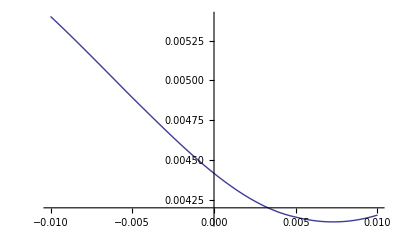

```mathematica
Module[{S1=0.051,S2=0.052,S3=0.049,S4=0.0495,
α11=4.7,α12=-2.6,α13=-0.2,α14=-0.4,
α21=6.3,α22=-1.2,α23=0.6,α24=0.1,
α31=6.3,α32=0.6,α33=0.3,α34=0.3,
α41=6.2,α42=2.1,α43=-0.6,α44=-0.3,
ρ1=-0.1,ν1=0.001,V01=0.001,
ρ2=-0.1,ν2=0.001,V02=0.001,
ρ3=-0.1,ν3=0.001,V03=0.001,
ρ4=-0.1,ν4=0.001,V04=0.001,
ρ5=-0.1,ν5=0.001,V05=0.001,
ρ6=-0.1,ν6=0.001,V06=0.001,
ρ7=-0.1,ν7=0.001,V07=0.001,
ρ8=-0.1,ν8=0.001,V08=0.001,
LTFactor=1,λS=0.1,SpreadStrikes={-0.01,-0.005,-0.001,0,0.001,0.005,0.01},τ=5,
LimitGindinkin=10,mode=0,printflag=1,prices12,inter12},
prices12=SmileQuadriBiSuperHestonVanillaSpreadOption12[S1,S2,S3,S4,
α11,α12,α13,α14,α21,α22,α23,α24,α31,α32,α33,α34,α41,α42,α43,α44,
ρ1,ν1,V01,ρ2,ν2,V02,ρ3,ν3,V03,ρ4,ν4,V04,ρ5,ν5,V05,ρ6,ν6,V06,ρ7,ν7,V07,ρ8,ν8,V08,
LTFactor,λS,SpreadStrikes,τ,LimitGindinkin,mode,printflag];
inter12=Interpolation[Table[{SpreadStrikes[[i]],NormalImplicitVol[S1-S2,SpreadStrikes[[i]],τ,prices12[[i]]]},{i,1,Length[SpreadStrikes]}]];
Plot[inter12[x],{x,First[SpreadStrikes],Last[SpreadStrikes]}]
]
```

#### Spread 1 - 3

On echange les Si, les alpha (i, 1) ... alpha (i, 4) et les ρi, νi, V0i  specifiques

```mathematica
Clear[SmileQuadriBiSuperHestonVanillaSpreadOption12]
```

```mathematica
SmileQuadriBiSuperHestonVanillaSpreadOption13[S1_,S2_,S3_,S4_,
α11_,α12_,α13_,α14_,α21_,α22_,α23_,α24_,α31_,α32_,α33_,α34_,α41_,α42_,α43_,α44_,
ρ1_,ν1_,V01_,ρ2_,ν2_,V02_,ρ3_,ν3_,V03_,ρ4_,ν4_,V04_,ρ5_,ν5_,V05_,ρ6_,ν6_,V06_,ρ7_,ν7_,V07_,ρ8_,ν8_,V08_,
LTFactor_,λS_,SpreadStrikes_,τ_,LimitGindinkin_,mode_,printflag_]:=
SmileQuadriBiSuperHestonVanillaSpreadOption12[
S1,S3,S2,S4,
α11,α12,α13,α14,
α31,α32,α33,α34,
α21,α22,α23,α24,
α41,α42,α43,α44,
ρ1,ν1,V01,
ρ2,ν2,V02,
ρ3,ν3,V03,
ρ4,ν4,V04,
ρ5,ν5,V05,
ρ7,ν7,V07,
ρ6,ν6,V06,
ρ8,ν8,V08,
LTFactor,λS,SpreadStrikes,τ,LimitGindinkin,mode,printflag]
```

```mathematica
CForm[SmileQuadriBiSuperHestonVanillaSpreadOption34[S1,S2,S3,S4,
alpha11,alpha12,alpha13,alpha14,
alpha21,alpha22,alpha23,alpha24,
alpha31,alpha32,alpha33,alpha34,
alpha41,alpha42,alpha43,alpha44,rho1,kappaV1,V1,
rho2,kappaV2,V2,
rho3,kappaV3,V3,
rho4,kappaV4,V4,
rho5,kappaV5,V5,rho6,kappaV6,V6,
rho7,kappaV7,V7,
rho8,kappaV8,V8,
LTspread,lambdaspread,KListPtr,T,gindinkinFactor,mode,printflag]]
```

SmileQuadriBiSuperHestonVanillaSpreadOption12(S3,S4,S1,S2,alpha31,alpha32,alpha33,alpha34,alpha41,alpha42,alpha43,alpha44,alpha11,alpha12,
   alpha13,alpha14,alpha21,alpha22,alpha23,alpha24,rho1,kappaV1,V1,rho2,kappaV2,V2,rho3,kappaV3,V3,rho4,kappaV4,V4,rho7,kappaV7,V7,rho8,
   kappaV8,V8,rho5,kappaV5,V5,rho6,kappaV6,V6,LTspread,lambdaspread,KListPtr,T,gindinkinFactor,mode,printflag)

#### Spread 1 - 4

On echange les Si, les alpha (i, 1) ... alpha (i, 4) et les ρi, νi, V0i  specifiques

```mathematica
SmileQuadriBiSuperHestonVanillaSpreadOption14[S1_,S2_,S3_,S4_,
α11_,α12_,α13_,α14_,α21_,α22_,α23_,α24_,α31_,α32_,α33_,α34_,α41_,α42_,α43_,α44_,
ρ1_,ν1_,V01_,ρ2_,ν2_,V02_,ρ3_,ν3_,V03_,ρ4_,ν4_,V04_,ρ5_,ν5_,V05_,ρ6_,ν6_,V06_,ρ7_,ν7_,V07_,ρ8_,ν8_,V08_,
LTFactor_,λS_,SpreadStrikes_,τ_,LimitGindinkin_,mode_,printflag_]:=SmileQuadriBiSuperHestonVanillaSpreadOption12[
S1,S4,S3,S2,
α11,α12,α13,α14,
α41,α42,α43,α44,
α31,α32,α33,α34,
α21,α22,α23,α24,
ρ1,ν1,V01,
ρ2,ν2,V02,
ρ3,ν3,V03,
ρ4,ν4,V04,
ρ5,ν5,V05,
ρ8,ν8,V08,
ρ7,ν7,V07,
ρ6,ν6,V06,
LTFactor,λS,SpreadStrikes,τ,LimitGindinkin,mode,printflag]
```

#### Spread 2 - 3

On echange les Si, les alpha (i, 1) ... alpha (i, 4) et les ρi, νi, V0i  specifiques

```mathematica
SmileQuadriBiSuperHestonVanillaSpreadOption23[S1_,S2_,S3_,S4_,
α11_,α12_,α13_,α14_,α21_,α22_,α23_,α24_,α31_,α32_,α33_,α34_,α41_,α42_,α43_,α44_,
ρ1_,ν1_,V01_,ρ2_,ν2_,V02_,ρ3_,ν3_,V03_,ρ4_,ν4_,V04_,ρ5_,ν5_,V05_,ρ6_,ν6_,V06_,ρ7_,ν7_,V07_,ρ8_,ν8_,V08_,
LTFactor_,λS_,SpreadStrikes_,τ_,LimitGindinkin_,mode_,printflag_]:=SmileQuadriBiSuperHestonVanillaSpreadOption12[
S2,S3,S1,S4,
α21,α22,α23,α24,
α31,α32,α33,α34,
α11,α12,α13,α14,
α41,α42,α43,α44,
ρ1,ν1,V01,
ρ2,ν2,V02,
ρ3,ν3,V03,
ρ4,ν4,V04,
ρ6,ν6,V06,
ρ7,ν7,V07,
ρ5,ν5,V05,
ρ8,ν8,V08,
LTFactor,λS,SpreadStrikes,τ,LimitGindinkin,mode,printflag]
```

#### Spread 2 - 4

On echange les Si, les alpha (i, 1) ... alpha (i, 4) et les ρi, νi, V0i  specifiques

```mathematica
SmileQuadriBiSuperHestonVanillaSpreadOption24[S1_,S2_,S3_,S4_,
α11_,α12_,α13_,α14_,α21_,α22_,α23_,α24_,α31_,α32_,α33_,α34_,α41_,α42_,α43_,α44_,
ρ1_,ν1_,V01_,ρ2_,ν2_,V02_,ρ3_,ν3_,V03_,ρ4_,ν4_,V04_,ρ5_,ν5_,V05_,ρ6_,ν6_,V06_,ρ7_,ν7_,V07_,ρ8_,ν8_,V08_,
LTFactor_,λS_,SpreadStrikes_,τ_,LimitGindinkin_,mode_,printflag_]:=SmileQuadriBiSuperHestonVanillaSpreadOption12[
S2,S4,S1,S3,
α21,α22,α23,α24,
α41,α42,α43,α44,
α11,α12,α13,α14,
α31,α32,α33,α34,
ρ1,ν1,V01,
ρ2,ν2,V02,
ρ3,ν3,V03,
ρ4,ν4,V04,
ρ6,ν6,V06,
ρ8,ν8,V08,
ρ5,ν5,V05,
ρ7,ν7,V07,
LTFactor,λS,SpreadStrikes,τ,LimitGindinkin,mode,printflag]
```

#### Spread 3 - 4

On echange les Si, les alpha (i, 1) ... alpha (i, 4) et les ρi, νi, V0i  specifiques

```mathematica
SmileQuadriBiSuperHestonVanillaSpreadOption34[S1_,S2_,S3_,S4_,
α11_,α12_,α13_,α14_,α21_,α22_,α23_,α24_,α31_,α32_,α33_,α34_,α41_,α42_,α43_,α44_,
ρ1_,ν1_,V01_,ρ2_,ν2_,V02_,ρ3_,ν3_,V03_,ρ4_,ν4_,V04_,ρ5_,ν5_,V05_,ρ6_,ν6_,V06_,ρ7_,ν7_,V07_,ρ8_,ν8_,V08_,
LTFactor_,λS_,SpreadStrikes_,τ_,LimitGindinkin_,mode_,printflag_]:=SmileQuadriBiSuperHestonVanillaSpreadOption12[
S3,S4,S1,S2,
α31,α32,α33,α34,
α41,α42,α43,α44,
α11,α12,α13,α14,
α21,α22,α23,α24,
ρ1,ν1,V01,
ρ2,ν2,V02,
ρ3,ν3,V03,
ρ4,ν4,V04,
ρ7,ν7,V07,
ρ8,ν8,V08,
ρ5,ν5,V05,
ρ6,ν6,V06,
LTFactor,λS,SpreadStrikes,τ,LimitGindinkin,mode,printflag]
```

## Test Pricing

### Application 1

```mathematica
Module[{S1=0.051,S2=0.052,S3=0.049,S4=0.0495,
α11=4.7,α12=-2.6,α13=-0.2,α14=-0.4,
α21=6.3,α22=-1.2,α23=0.6,α24=0.1,
α31=6.3,α32=0.6,α33=0.3,α34=0.3,
α41=6.2,α42=2.1,α43=-0.6,α44=-0.3,
ρ1=-0.1,ν1=0.1,V01=0.001,
ρ2=-0.1,ν2=0.1,V02=0.001,
ρ3=-0.1,ν3=0.1,V03=0.001,
ρ4=-0.1,ν4=0.1,V04=0.001,
ρ5=-0.1,ν5=0.1,V05=0.001,
ρ6=-0.1,ν6=0.1,V06=0.001,
ρ7=-0.1,ν7=0.1,V07=0.001,
ρ8=-0.1,ν8=0.1,V08=0.001,
LTFactor=1,λS=0.1,SpreadStrikes={-0.01,-0.005,0,0.005,0.01},τ=5,
LimitGindinkin=10,mode=0,printflag=1,prices12,inter12,prices13,inter13,prices14,inter14,prices23,inter23,prices24,inter24,prices34,inter34},
prices12=SmileQuadriBiSuperHestonVanillaSpreadOption12[S1,S2,S3,S4,
α11,α12,α13,α14,α21,α22,α23,α24,α31,α32,α33,α34,α41,α42,α43,α44,
ρ1,ν1,V01,ρ2,ν2,V02,ρ3,ν3,V03,ρ4,ν4,V04,ρ5,ν5,V05,ρ6,ν6,V06,ρ7,ν7,V07,ρ8,ν8,V08,
LTFactor,λS,SpreadStrikes,τ,LimitGindinkin,mode,printflag]]
```

moments={{0.075125,0.10625},{0.198465,0.354004,0.244107}}

NormalTerminalcorrelT=0.920945 ExpcorreLT=0.905411

VarExpX=0.000490052 VarExpY=0.000791797

VarRealSpead (Goal)=0.000153862

VS=0.0000203288 VarVS=9.69487×10^-10 CoVarSVS=1.12079×10^-8

****AlphaGenericComputeSpreadOption****

VarRealSpead (Goal)=0.000153862

NormalTerminalcorrelT=0.920945 ExpcorreLT=0.905411

TrueIniVarSpread=0.0000307725

@@@@@@  inside NuRhoV0MinimunNormalHestonFromBilog

S1=0.051 S2=0.052 sig1=0.173349 sig2=0.206155 Correl12=0.911383

opt1=0.00734813 opt2=0.00176221 opt3=0.00401584

vol1=0.00493683 vol2=0.00450175 vol3=0.00419581

convexity=0.000129153 pente=-0.000741017 ATMprix=0.00401584

convexityTable=(1.93668×10^-6 | -7.6009
7.88801×10^-6 | -6.90776
0.000150932 | -5.52146
0.000235452 | -5.29832
0.000704338 | -4.60517)

Equivalent nu normalisé=(0.0005 | 0.0901341
0.001 | 0.180268
0.004 | 0.721072
0.005 | 0.901341
0.01 | 1.80268)

κsol=0.00801568

prices(pour la pente)=(-0.6 | {0.00756303,0.00147812}
-0.3 | {0.00740811,0.00189745}
-0.1 | {0.00727206,0.00210444}
0 | {0.00719259,0.00219259}
0.3 | {0.00689745,0.00240811}
0.6 | {0.00647812,0.00256303})

vols=(-0.6 | {0.00520236,0.00382365}
-0.3 | {0.00501122,0.00436956}
-0.1 | {0.00484216,0.0046321}
0 | {0.00474282,0.00474282}
0.3 | {0.00436956,0.00501122}
0.6 | {0.00382365,0.00520236})

penteTable=(-0.00137871 | -0.53705
-0.000641667 | -0.291313
-0.00021006 | -0.099668
-3.71196×10^-12 | 0
0.000641667 | 0.291313
0.00137871 | 0.53705)

ρsol=-0.344608

######## arg={ρsol,λv,LT V0Table[,κsol,V0Table,S1-S2,S1-S2,τ,LimitGindinkin}

######## arg={-0.344608,0.1,{0.0000153862,0.0000276952,0.0000307725,0.0000338497,0.0000615449},0.00801568,{0.0000153862,0.0000276952,0.0000307725,0.0000338497,0.0000615449},-0.001,-0.001,5,10}

VOptionATMTable=(0 | 0
0.00247181 | 0.0000153862
0.00368721 | 0.0000276952
0.00395196 | 0.0000307725
0.00420515 | 0.0000338497
0.00612309 | 0.0000615449)

V0sol=0.0000315363

convexityTable=(1.46999×10^-6 | -7.6009
5.9858×10^-6 | -6.90776
0.00012379 | -5.52146
0.000199951 | -5.29832
0.000652152 | -4.60517)

Equivalent nu normalisé=(0.0005 | 0.0901341
0.001 | 0.180268
0.004 | 0.721072
0.005 | 0.901341
0.01 | 1.80268)

κsol2=0.00412144

VOptionATMTable=(0 | 0
0.00304267 | 0.0000153862
0.00431394 | 0.0000276952
0.00458255 | 0.0000307725
0.0048374 | 0.0000338497
0.00672597 | 0.0000615449)

V0sol2=0.0000244776

Mode 1 :   Numinimum=0.00412144 rhominimum= -0.344608 V0minimim=0.0000244776

Comparaison:  TrueIniVarSpread/ V0minimim =1.25717

Normal Heston Parameters=(S0 | -0.001
V0 | 0.0000244776
θ | 0.0000244776
λv | 0.1
ρ | -0.12793
ν | 0.00752285
ν normalized | 1.52054
standard dev equi. | 0.00494748)

prices={0.0102541,0.00611915,0.00300704,0.0014827,0.000819301}

{0.0102541,0.00611915,0.00300704,0.0014827,0.000819301}

```mathematica
Module[{S1=0.051,S2=0.052,S3=0.049,S4=0.0495,
α11=4.7,α12=-2.6,α13=-0.2,α14=-0.4,
α21=6.3,α22=-1.2,α23=0.6,α24=0.1,
α31=6.3,α32=0.6,α33=0.3,α34=0.3,
α41=6.2,α42=2.1,α43=-0.6,α44=-0.3,
ρ1=0.2,ν1=0.0001,V01=0.001862331,
ρ2=-0.1,ν2=0.1,V02=0.001,
ρ3=-0.1,ν3=0.1,V03=0.001,
ρ4=-0.1,ν4=0.1,V04=0.001,
ρ5=-0.1,ν5=0.1,V05=0.001,
ρ6=-0.1,ν6=0.1,V06=0.001,
ρ7=-0.1,ν7=0.1,V07=0.001,
ρ8=-0.1,ν8=0.1,V08=0.001,
LTFactor=1,λS=0.1,SpreadStrikes={-0.01,-0.005,0,0.005,0.01},τ=5,
LimitGindinkin=10,mode=0,printflag=1,prices12,inter12,prices13,inter13,prices14,inter14,prices23,inter23,prices24,inter24,prices34,inter34},
prices12=SmileQuadriBiSuperHestonVanillaSpreadOption12[S1,S2,S3,S4,
α11,α12,α13,α14,α21,α22,α23,α24,α31,α32,α33,α34,α41,α42,α43,α44,
ρ1,ν1,V01,ρ2,ν2,V02,ρ3,ν3,V03,ρ4,ν4,V04,ρ5,ν5,V05,ρ6,ν6,V06,ρ7,ν7,V07,ρ8,ν8,V08,
LTFactor,λS,SpreadStrikes,τ,LimitGindinkin,mode,printflag]]
```

moments={{0.122747,0.191815},{0.247082,0.383709,0.29053}}

NormalTerminalcorrelT=0.94356 ExpcorreLT=0.931138

VarExpX=0.000925119 VarExpY=0.00185563

VarRealSpead (Goal)=0.000340756

VS=0.0000269915 VarVS=4.10642×10^-10 CoVarSVS=4.39111×10^-9

****AlphaGenericComputeSpreadOption****

VarRealSpead (Goal)=0.000340756

NormalTerminalcorrelT=0.94356 ExpcorreLT=0.931138

TrueIniVarSpread=0.0000681512

@@@@@@  inside NuRhoV0MinimunNormalHestonFromBilog

S1=0.051 S2=0.052 sig1=0.221583 sig2=0.276994 Correl12=0.946665

opt1=0.00815342 opt2=0.00203668 opt3=0.00462352

vol1=0.00592013 vol2=0.00518296 vol3=0.00454657

convexity=0.00010079 pente=-0.00137356 ATMprix=0.00462352

convexityTable=(5.8572×10^-7 | -7.6009
2.36323×10^-6 | -6.90776
0.0000435354 | -5.52146
0.0000712493 | -5.29832
0.000281606 | -4.60517)

Equivalent nu normalisé=(0.0005 | 0.0605666
0.001 | 0.121133
0.004 | 0.484533
0.005 | 0.605666
0.01 | 1.21133)

κsol=0.00417069

prices(pour la pente)=(-0.6 | {0.010166,0.00459111}
-0.3 | {0.0100381,0.00475307}
-0.1 | {0.00994834,0.0048536}
0 | {0.00990165,0.00490165}
0.3 | {0.00975307,0.00503808}
0.6 | {0.00959111,0.00516599})

vols=(-0.6 | {0.00829395,0.00762353}
-0.3 | {0.00814515,0.00781286}
-0.1 | {0.00804064,0.00793019}
0 | {0.00798623,0.00798623}
0.3 | {0.00781286,0.00814515}
0.6 | {0.00762353,0.00829395})

penteTable=(-0.000670422 | -0.53705
-0.000332291 | -0.291313
-0.000110447 | -0.099668
-1.51046×10^-13 | 0
0.000332291 | 0.291313
0.000670422 | 0.53705)

ρsol=-0.849733

######## arg={ρsol,λv,LT V0Table[,κsol,V0Table,S1-S2,S1-S2,τ,LimitGindinkin}

######## arg={-0.849733,0.1,{0.0000340756,0.0000613361,0.0000681512,0.0000749664,0.000136302},0.00417069,{0.0000340756,0.0000613361,0.0000681512,0.0000749664,0.000136302},-0.001,-0.001,5,10}

VOptionATMTable=(0 | 0
0.00481766 | 0.0000340756
0.00670299 | 0.0000613361
0.00709681 | 0.0000681512
0.00746982 | 0.0000749664
0.0102302 | 0.000136302)

V0sol=0.0000317519

convexityTable=(-1.54709×10^-6 | -7.6009
-6.26189×10^-6 | -6.90776
-0.0000918374 | -5.52146
-0.000102355 | -5.29832
0.00016758 | -4.60517)

Equivalent nu normalisé=(0.0005 | 0.0605666
0.001 | 0.121133
0.004 | 0.484533
0.005 | 0.605666
0.01 | 1.21133)

κsol2=0.00134133

VOptionATMTable=(0 | 0
0.00516973 | 0.0000340756
0.00695847 | 0.0000613361
0.00733783 | 0.0000681512
0.00769852 | 0.0000749664
0.010396 | 0.000136302)

V0sol2=0.0000273477

Mode 1 :   Numinimum=0.00134133 rhominimum= -0.849733 V0minimim=0.0000273477

Comparaison:  TrueIniVarSpread/ V0minimim =2.49203

Normal Heston Parameters=(S0 | -0.001
V0 | 0.0000273477
θ | 0.0000273477
λv | 0.1
ρ | -0.238798
ν | 0.00410058
ν normalized | 0.784125
standard dev equi. | 0.0052295)

prices={0.010581,0.0067635,0.00377718,0.00187355,0.000878947}

{0.010581,0.0067635,0.00377718,0.00187355,0.000878947}

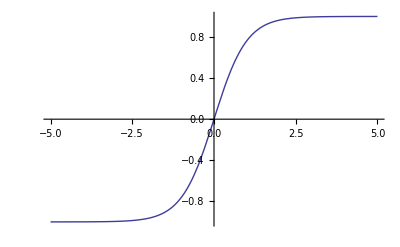

```mathematica
Plot[Tanh[x],{x,-5,5}]
```

### Application 2

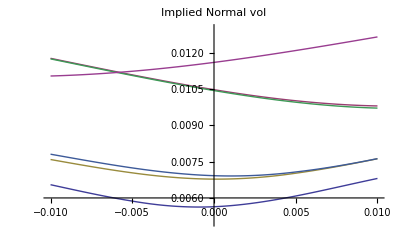
{39.656,-Graphics-}

```mathematica
Timing[Module[{S1=0.051,S2=0.052,S3=0.049,S4=0.0495,
α11=0.1,α12=1,α13=0.1,α14=0.1,
α21=0.1,α22=1,α23=0.1,α24=0.2,
α31=1,α32=1,α33=1,α34=1,
α41=0.1,α42=0.1,α43=0.1,α44=0.1,
ρ1=0.1,ν1=0.35,V01=0.01,
ρ2=0.1,ν2=0.35,V02=0.01,
ρ3=0.1,ν3=0.35,V03=0.01,
ρ4=0.1,ν4=0.35,V04=0.01,
ρ5=0.1,ν5=0.35,V05=0.01,
ρ6=0.1,ν6=0.35,V06=0.01,
ρ7=0.1,ν7=0.35,V07=0.01,
ρ8=0.1,ν8=0.35,V08=0.01,
LTFactor=1,λS=0.1,SpreadStrikes={-0.01,-0.005,-0.001,0,0.001,0.005,0.01},τ=5,
LimitGindinkin=10,mode=0,printflag=0,prices12,inter12,prices13,inter13,prices14,inter14,prices23,inter23,prices24,inter24,prices34,inter34},
prices12=SmileQuadriBiSuperHestonVanillaSpreadOption12[S1,S2,S3,S4,
α11,α12,α13,α14,α21,α22,α23,α24,α31,α32,α33,α34,α41,α42,α43,α44,
ρ1,ν1,V01,ρ2,ν2,V02,ρ3,ν3,V03,ρ4,ν4,V04,ρ5,ν5,V05,ρ6,ν6,V06,ρ7,ν7,V07,ρ8,ν8,V08,
LTFactor,λS,SpreadStrikes,τ,LimitGindinkin,mode,printflag];
inter12=Interpolation[Table[{SpreadStrikes[[i]],NormalImplicitVol[S1-S2,SpreadStrikes[[i]],τ,prices12[[i]]]},{i,1,Length[SpreadStrikes]}]];
prices13=SmileQuadriBiSuperHestonVanillaSpreadOption13[S1,S2,S3,S4,
α11,α12,α13,α14,α21,α22,α23,α24,α31,α32,α33,α34,α41,α42,α43,α44,
ρ1,ν1,V01,ρ2,ν2,V02,ρ3,ν3,V03,ρ4,ν4,V04,ρ5,ν5,V05,ρ6,ν6,V06,ρ7,ν7,V07,ρ8,ν8,V08,
LTFactor,λS,SpreadStrikes,τ,LimitGindinkin,mode,printflag];
inter13=Interpolation[Table[{SpreadStrikes[[i]],NormalImplicitVol[S1-S3,SpreadStrikes[[i]],τ,prices13[[i]]]},{i,1,Length[SpreadStrikes]}]];
prices14=SmileQuadriBiSuperHestonVanillaSpreadOption14[S1,S2,S3,S4,
α11,α12,α13,α14,α21,α22,α23,α24,α31,α32,α33,α34,α41,α42,α43,α44,
ρ1,ν1,V01,ρ2,ν2,V02,ρ3,ν3,V03,ρ4,ν4,V04,ρ5,ν5,V05,ρ6,ν6,V06,ρ7,ν7,V07,ρ8,ν8,V08,
LTFactor,λS,SpreadStrikes,τ,LimitGindinkin,mode,printflag];
inter14=Interpolation[Table[{SpreadStrikes[[i]],NormalImplicitVol[S1-S4,SpreadStrikes[[i]],τ,prices14[[i]]]},{i,1,Length[SpreadStrikes]}]];
prices23=SmileQuadriBiSuperHestonVanillaSpreadOption23[S1,S2,S3,S4,
α11,α12,α13,α14,α21,α22,α23,α24,α31,α32,α33,α34,α41,α42,α43,α44,
ρ1,ν1,V01,ρ2,ν2,V02,ρ3,ν3,V03,ρ4,ν4,V04,ρ5,ν5,V05,ρ6,ν6,V06,ρ7,ν7,V07,ρ8,ν8,V08,
LTFactor,λS,SpreadStrikes,τ,LimitGindinkin,mode,printflag];
inter23=Interpolation[Table[{SpreadStrikes[[i]],NormalImplicitVol[S2-S3,SpreadStrikes[[i]],τ,prices23[[i]]]},{i,1,Length[SpreadStrikes]}]];
prices24=SmileQuadriBiSuperHestonVanillaSpreadOption24[S1,S2,S3,S4,
α11,α12,α13,α14,α21,α22,α23,α24,α31,α32,α33,α34,α41,α42,α43,α44,
ρ1,ν1,V01,ρ2,ν2,V02,ρ3,ν3,V03,ρ4,ν4,V04,ρ5,ν5,V05,ρ6,ν6,V06,ρ7,ν7,V07,ρ8,ν8,V08,
LTFactor,λS,SpreadStrikes,τ,LimitGindinkin,mode,printflag];
inter24=Interpolation[Table[{SpreadStrikes[[i]],NormalImplicitVol[S2-S4,SpreadStrikes[[i]],τ,prices24[[i]]]},{i,1,Length[SpreadStrikes]}]];
prices34=SmileQuadriBiSuperHestonVanillaSpreadOption34[S1,S2,S3,S4,
α11,α12,α13,α14,α21,α22,α23,α24,α31,α32,α33,α34,α41,α42,α43,α44,
ρ1,ν1,V01,ρ2,ν2,V02,ρ3,ν3,V03,ρ4,ν4,V04,ρ5,ν5,V05,ρ6,ν6,V06,ρ7,ν7,V07,ρ8,ν8,V08,
LTFactor,λS,SpreadStrikes,τ,LimitGindinkin,mode,printflag];
inter34=Interpolation[Table[{SpreadStrikes[[i]],NormalImplicitVol[S3-S4,SpreadStrikes[[i]],τ,prices34[[i]]]},{i,1,Length[SpreadStrikes]}]];
Plot[{inter12[x],inter13[x],inter14[x],inter23[x],inter24[x],inter34[x]},{x,First[SpreadStrikes],Last[SpreadStrikes]},
PlotLabel->"Implied Normal vol",
PlotLegend->{"1-2","1-3","1-4","2-3","2-4","3-4"},LegendPosition->{1,0},PlotRange->{0.005,0.013}]
]]
```

## Calibration

#### {VS, VarVS, CoVarSVS}

```mathematica
{VS,VarVS,CoVarSVS}={(alpha11 S1-alpha21 S2)^2 V1+(alpha12 S1-alpha22 S2)^2 V2+(alpha13 S1-alpha23 S2)^2 V3+(alpha14 S1-alpha24 S2)^2 V4+S1^2 V5+S2^2 V6,
-4 S1^2 V5 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)^2+2 S1^2 V5 (alpha11 (alpha11 S1-alpha21 S2) V1+alpha12 (alpha12 S1-alpha22 S2) V2+alpha13 (alpha13 S1-alpha23 S2) V3+alpha14 (alpha14 S1-alpha24 S2) V4+S1 V5) (kappaV5 rho5 S1+2 alpha11 (alpha11 S1-alpha21 S2) V1+2 alpha12 (alpha12 S1-alpha22 S2) V2+2 alpha13 (alpha13 S1-alpha23 S2) V3+2 alpha14 (alpha14 S1-alpha24 S2) V4+2 S1 V5)+kappaV5 S1^3 V5 (kappaV5 S1+2 rho5 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5))-4 S2^2 V6 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6)^2+2 S2^2 V6 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6) (kappaV6 rho6 S2+2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6))+kappaV6 S2^3 V6 (kappaV6 S2+2 rho6 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6))-V1 (2 alpha11 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha21 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6))^2+V1 (2 alpha11 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha21 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6)) (kappaV1 rho1 (alpha11 S1-alpha21 S2)^2+2 alpha11 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha21 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6))-V2 (2 alpha12 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha22 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6))^2+V2 (2 alpha12 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha22 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6)) (kappaV2 rho2 (alpha12 S1-alpha22 S2)^2+2 alpha12 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha22 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6))-V3 (2 alpha13 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha23 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6))^2+V3 (2 alpha13 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha23 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6)) (kappaV3 rho3 (alpha13 S1-alpha23 S2)^2+2 alpha13 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha23 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6))-V4 (2 alpha14 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha24 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6))^2+V4 (2 alpha14 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha24 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6)) (kappaV4 rho4 (alpha14 S1-alpha24 S2)^2+2 alpha14 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha24 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6))+kappaV1 (alpha11 S1-alpha21 S2)^2 V1 (kappaV1 (alpha11 S1-alpha21 S2)^2+rho1 (2 alpha11 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha21 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6)))+kappaV2 (alpha12 S1-alpha22 S2)^2 V2 (kappaV2 (alpha12 S1-alpha22 S2)^2+rho2 (2 alpha12 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha22 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6)))+kappaV3 (alpha13 S1-alpha23 S2)^2 V3 (kappaV3 (alpha13 S1-alpha23 S2)^2+rho3 (2 alpha13 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha23 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6)))+kappaV4 (alpha14 S1-alpha24 S2)^2 V4 (kappaV4 (alpha14 S1-alpha24 S2)^2+rho4 (2 alpha14 S1 (alpha11^2 S1 V1-alpha11 alpha21 S2 V1+alpha12^2 S1 V2-alpha12 alpha22 S2 V2+alpha13^2 S1 V3-alpha13 alpha23 S2 V3+alpha14^2 S1 V4-alpha14 alpha24 S2 V4+S1 V5)+2 alpha24 S2 (-alpha11 alpha21 S1 V1+alpha21^2 S2 V1-alpha12 alpha22 S1 V2+alpha22^2 S2 V2-alpha13 alpha23 S1 V3+alpha23^2 S2 V3-alpha14 alpha24 S1 V4+alpha24^2 S2 V4+S2 V6))),
kappaV1 rho1 (alpha11 S1-alpha21 S2)^3 V1+kappaV2 rho2 (alpha12 S1-alpha22 S2)^3 V2+kappaV3 rho3 (alpha13 S1-alpha23 S2)^3 V3+kappaV4 rho4 (alpha14 S1-alpha24 S2)^3 V4+kappaV5 rho5 S1^3 V5-kappaV6 rho6 S2^3 V6
};
```

## Calibration of the underlying options

### QuadriSuperheston

```mathematica
Corr={
{1,0,0,0,0,0,0,0,rho1,0,0,0,0,0,0,0},
{0,1,0,0,0,0,0,0,0,rho2,0,0,0,0,0,0},
{0,0,1,0,0,0,0,0,0,0,rho3,0,0,0,0,0},
{0,0,0,1,0,0,0,0,0,0,0,rho4,0,0,0,0},
{0,0,0,0,1,0,0,0,0,0,0,0,rho5,0,0,0},
{0,0,0,0,0,1,0,0,0,0,0,0,0,rho6,0,0},
{0,0,0,0,0,0,1,0,0,0,0,0,0,0,rho7,0},
{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,rho8},
{rho1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},
{0,rho2,0,0,0,0,0,0,0,1,0,0,0,0,0,0},
{0,0,rho3,0,0,0,0,0,0,0,1,0,0,0,0,0},
{0,0,0,rho4,0,0,0,0,0,0,0,1,0,0,0,0},
{0,0,0,0,rho5,0,0,0,0,0,0,0,1,0,0,0},
{0,0,0,0,0,rho6,0,0,0,0,0,0,0,1,0,0},
{0,0,0,0,0,0,rho7,0,0,0,0,0,0,0,1,0},
{0,0,0,0,0,0,0,rho8,0,0,0,0,0,0,0,1}
};
```

```mathematica
Mch=Eigensystem[Corr] [[2]]
```

{{-1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,-1,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,-1,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,-1,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,-1,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1}}

```mathematica
Eigens=Eigensystem[Corr] [[1]]
```

{1-rho1,1+rho1,1-rho2,1+rho2,1-rho3,1+rho3,1-rho4,1+rho4,1-rho5,1+rho5,1-rho6,1+rho6,1-rho7,1+rho7,1-rho8,1+rho8}

```mathematica
Mch //MatrixForm
```

(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Clear[S1,S2,S3,S4,V1,V2,V3,V5,V6,V7,V8]
```

```mathematica
Diff[x_]:=
D[x,S1]{alpha11 √V1 S1,alpha12 √V2 S1,alpha13 √V3 S1,alpha14 √V4 S1,√V5 S1,0,0,0,0,0,0,0,0,0,0,0}+
D[x,S2]{alpha21 √V1 S2,alpha22 √V2 S2,alpha23 √V3 S2,alpha24 √V4 S2,0,√V6 S2,0,0,0,0,0,0,0,0,0,0}+
D[x,S3]{alpha31 √V1 S3,alpha32 √V2 S3,alpha33 √V3 S3,alpha34 √V4 S3,0,0,√V7 S3,0,0,0,0,0,0,0,0,0}+
D[x,S4]{alpha41 √V1 S4,alpha42 √V2 S4,alpha43 √V3 S4,alpha44 √V4 S4,0,0,0,√V8 S4,0,0,0,0,0,0,0,0}+
D[x,V1]{0,0,0,0,0,0,0,0,kappaV1 √V1,0,0,0,0,0,0,0}+
D[x,V2]{0,0,0,0,0,0,0,0,0,kappaV2 √V2,0,0,0,0,0,0}+
D[x,V3]{0,0,0,0,0,0,0,0,0,0,kappaV3 √V3,0,0,0,0,0}+
D[x,V4]{0,0,0,0,0,0,0,0,0,0,0,kappaV4 √V4,0,0,0,0}+
D[x,V5]{0,0,0,0,0,0,0,0,0,0,0,0,kappaV5 √V5,0,0,0}+
D[x,V6]{0,0,0,0,0,0,0,0,0,0,0,0,0,kappaV6 √V6,0,0}+
D[x,V7]{0,0,0,0,0,0,0,0,0,0,0,0,0,0,kappaV7 √V7,0}+
D[x,V8]{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,kappaV8 √V8}
```

### Heston

```mathematica
CovH={
{1,rhoH},
{rhoH,1}
};
```

```mathematica
DiffH[x_]:=D[x,S]{√V S,0}+
D[x,V]{0,nuH √V }
```

```mathematica
VSH=Simplify[DiffH[S].(CovH.DiffH[S])]
```

S^2 V

```mathematica
VarVSH=Simplify[DiffH[VSH/S^2].(CovH.DiffH[VSH/S^2])]
```

nuH^2 V

```mathematica
Simplify[VarVSH-(VarVSH /.{nuH->0})]
```

nuH^2 V

```mathematica
CoVarSVHS=Simplify[DiffH[VSH/S^2].(CovH.DiffH[S])]
```

nuH rhoH S V

```mathematica
Simplify[CoVarSVHS-(CoVarSVHS /.{nuH->0})]
```

nuH rhoH S V

### Calibration of the underlyings

```mathematica
Simplify[Solve[{a11 X1 +a12 X2 +a13 X3 +a14 X4 ==a15,
a21 X1 +a22 X2 +a23 X3 +a24 X4 ==a25,
a31 X1 +a32 X2 +a33 X3 +a34 X4 ==a35,
a41 X1 +a42 X2 +a43 X3 +a44 X4 ==a45
},{X1,X2,X3,X4}]]
```

{{X1→(-a13 a25 a34 a42+a13 a24 a35 a42+a12 a25 a34 a43-a12 a24 a35 a43+a13 a25 a32 a44-a12 a25 a33 a44-a13 a22 a35 a44+a12 a23 a35 a44+a15 (-a24 a33 a42+a23 a34 a42+a24 a32 a43-a22 a34 a43-a23 a32 a44+a22 a33 a44)-a13 a24 a32 a45+a12 a24 a33 a45+a13 a22 a34 a45-a12 a23 a34 a45+a14 (a25 a33 a42-a23 a35 a42-a25 a32 a43+a22 a35 a43+a23 a32 a45-a22 a33 a45))/(a12 a24 a33 a41-a12 a23 a34 a41-a11 a24 a33 a42+a11 a23 a34 a42-a12 a24 a31 a43+a11 a24 a32 a43+a12 a21 a34 a43-a11 a22 a34 a43+a14 (a23 a32 a41-a22 a33 a41-a23 a31 a42+a21 a33 a42+a22 a31 a43-a21 a32 a43)+a12 a23 a31 a44-a11 a23 a32 a44-a12 a21 a33 a44+a11 a22 a33 a44+a13 (-a24 a32 a41+a22 a34 a41+a24 a31 a42-a21 a34 a42-a22 a31 a44+a21 a32 a44)),X2→(a13 a25 a34 a41-a13 a24 a35 a41-a11 a25 a34 a43+a11 a24 a35 a43-a13 a25 a31 a44+a11 a25 a33 a44+a13 a21 a35 a44-a11 a23 a35 a44+a15 (a24 a33 a41-a23 a34 a41-a24 a31 a43+a21 a34 a43+a23 a31 a44-a21 a33 a44)+a13 a24 a31 a45-a11 a24 a33 a45-a13 a21 a34 a45+a11 a23 a34 a45+a14 (-a25 a33 a41+a23 a35 a41+a25 a31 a43-a21 a35 a43-a23 a31 a45+a21 a33 a45))/(a12 a24 a33 a41-a12 a23 a34 a41-a11 a24 a33 a42+a11 a23 a34 a42-a12 a24 a31 a43+a11 a24 a32 a43+a12 a21 a34 a43-a11 a22 a34 a43+a14 (a23 a32 a41-a22 a33 a41-a23 a31 a42+a21 a33 a42+a22 a31 a43-a21 a32 a43)+a12 a23 a31 a44-a11 a23 a32 a44-a12 a21 a33 a44+a11 a22 a33 a44+a13 (-a24 a32 a41+a22 a34 a41+a24 a31 a42-a21 a34 a42-a22 a31 a44+a21 a32 a44)),X3→(-a12 a25 a34 a41+a12 a24 a35 a41+a11 a25 a34 a42-a11 a24 a35 a42+a12 a25 a31 a44-a11 a25 a32 a44-a12 a21 a35 a44+a11 a22 a35 a44+a15 (-a24 a32 a41+a22 a34 a41+a24 a31 a42-a21 a34 a42-a22 a31 a44+a21 a32 a44)-a12 a24 a31 a45+a11 a24 a32 a45+a12 a21 a34 a45-a11 a22 a34 a45+a14 (a25 a32 a41-a22 a35 a41-a25 a31 a42+a21 a35 a42+a22 a31 a45-a21 a32 a45))/(a12 a24 a33 a41-a12 a23 a34 a41-a11 a24 a33 a42+a11 a23 a34 a42-a12 a24 a31 a43+a11 a24 a32 a43+a12 a21 a34 a43-a11 a22 a34 a43+a14 (a23 a32 a41-a22 a33 a41-a23 a31 a42+a21 a33 a42+a22 a31 a43-a21 a32 a43)+a12 a23 a31 a44-a11 a23 a32 a44-a12 a21 a33 a44+a11 a22 a33 a44+a13 (-a24 a32 a41+a22 a34 a41+a24 a31 a42-a21 a34 a42-a22 a31 a44+a21 a32 a44)),X4→(a12 a25 a33 a41-a12 a23 a35 a41-a11 a25 a33 a42+a11 a23 a35 a42-a12 a25 a31 a43+a11 a25 a32 a43+a12 a21 a35 a43-a11 a22 a35 a43+a15 (a23 a32 a41-a22 a33 a41-a23 a31 a42+a21 a33 a42+a22 a31 a43-a21 a32 a43)+a12 a23 a31 a45-a11 a23 a32 a45-a12 a21 a33 a45+a11 a22 a33 a45+a13 (-a25 a32 a41+a22 a35 a41+a25 a31 a42-a21 a35 a42-a22 a31 a45+a21 a32 a45))/(a12 a24 a33 a41-a12 a23 a34 a41-a11 a24 a33 a42+a11 a23 a34 a42-a12 a24 a31 a43+a11 a24 a32 a43+a12 a21 a34 a43-a11 a22 a34 a43+a14 (a23 a32 a41-a22 a33 a41-a23 a31 a42+a21 a33 a42+a22 a31 a43-a21 a32 a43)+a12 a23 a31 a44-a11 a23 a32 a44-a12 a21 a33 a44+a11 a22 a33 a44+a13 (-a24 a32 a41+a22 a34 a41+a24 a31 a42-a21 a34 a42-a22 a31 a44+a21 a32 a44))}}

```mathematica
Simplify[Solve[{b11 X1 +b12 X2 +b13 X3 +b14 X4 ==b15,
b21 X1 +b22 X2 +b23 X3 +b24 X4 ==b25,
b31 X1 +b32 X2 +b33 X3 +b34 X4 ==b35,
b41 X1 +b42 X2 +b43 X3 +b44 X4 ==b45
},{X1,X2,X3,X4}]]
```

{{X1→(-b13 b25 b34 b42+b13 b24 b35 b42+b12 b25 b34 b43-b12 b24 b35 b43+b13 b25 b32 b44-b12 b25 b33 b44-b13 b22 b35 b44+b12 b23 b35 b44+b15 (-b24 b33 b42+b23 b34 b42+b24 b32 b43-b22 b34 b43-b23 b32 b44+b22 b33 b44)-b13 b24 b32 b45+b12 b24 b33 b45+b13 b22 b34 b45-b12 b23 b34 b45+b14 (b25 b33 b42-b23 b35 b42-b25 b32 b43+b22 b35 b43+b23 b32 b45-b22 b33 b45))/(b12 b24 b33 b41-b12 b23 b34 b41-b11 b24 b33 b42+b11 b23 b34 b42-b12 b24 b31 b43+b11 b24 b32 b43+b12 b21 b34 b43-b11 b22 b34 b43+b14 (b23 b32 b41-b22 b33 b41-b23 b31 b42+b21 b33 b42+b22 b31 b43-b21 b32 b43)+b12 b23 b31 b44-b11 b23 b32 b44-b12 b21 b33 b44+b11 b22 b33 b44+b13 (-b24 b32 b41+b22 b34 b41+b24 b31 b42-b21 b34 b42-b22 b31 b44+b21 b32 b44)),X2→(b13 b25 b34 b41-b13 b24 b35 b41-b11 b25 b34 b43+b11 b24 b35 b43-b13 b25 b31 b44+b11 b25 b33 b44+b13 b21 b35 b44-b11 b23 b35 b44+b15 (b24 b33 b41-b23 b34 b41-b24 b31 b43+b21 b34 b43+b23 b31 b44-b21 b33 b44)+b13 b24 b31 b45-b11 b24 b33 b45-b13 b21 b34 b45+b11 b23 b34 b45+b14 (-b25 b33 b41+b23 b35 b41+b25 b31 b43-b21 b35 b43-b23 b31 b45+b21 b33 b45))/(b12 b24 b33 b41-b12 b23 b34 b41-b11 b24 b33 b42+b11 b23 b34 b42-b12 b24 b31 b43+b11 b24 b32 b43+b12 b21 b34 b43-b11 b22 b34 b43+b14 (b23 b32 b41-b22 b33 b41-b23 b31 b42+b21 b33 b42+b22 b31 b43-b21 b32 b43)+b12 b23 b31 b44-b11 b23 b32 b44-b12 b21 b33 b44+b11 b22 b33 b44+b13 (-b24 b32 b41+b22 b34 b41+b24 b31 b42-b21 b34 b42-b22 b31 b44+b21 b32 b44)),X3→(-b12 b25 b34 b41+b12 b24 b35 b41+b11 b25 b34 b42-b11 b24 b35 b42+b12 b25 b31 b44-b11 b25 b32 b44-b12 b21 b35 b44+b11 b22 b35 b44+b15 (-b24 b32 b41+b22 b34 b41+b24 b31 b42-b21 b34 b42-b22 b31 b44+b21 b32 b44)-b12 b24 b31 b45+b11 b24 b32 b45+b12 b21 b34 b45-b11 b22 b34 b45+b14 (b25 b32 b41-b22 b35 b41-b25 b31 b42+b21 b35 b42+b22 b31 b45-b21 b32 b45))/(b12 b24 b33 b41-b12 b23 b34 b41-b11 b24 b33 b42+b11 b23 b34 b42-b12 b24 b31 b43+b11 b24 b32 b43+b12 b21 b34 b43-b11 b22 b34 b43+b14 (b23 b32 b41-b22 b33 b41-b23 b31 b42+b21 b33 b42+b22 b31 b43-b21 b32 b43)+b12 b23 b31 b44-b11 b23 b32 b44-b12 b21 b33 b44+b11 b22 b33 b44+b13 (-b24 b32 b41+b22 b34 b41+b24 b31 b42-b21 b34 b42-b22 b31 b44+b21 b32 b44)),X4→(b12 b25 b33 b41-b12 b23 b35 b41-b11 b25 b33 b42+b11 b23 b35 b42-b12 b25 b31 b43+b11 b25 b32 b43+b12 b21 b35 b43-b11 b22 b35 b43+b15 (b23 b32 b41-b22 b33 b41-b23 b31 b42+b21 b33 b42+b22 b31 b43-b21 b32 b43)+b12 b23 b31 b45-b11 b23 b32 b45-b12 b21 b33 b45+b11 b22 b33 b45+b13 (-b25 b32 b41+b22 b35 b41+b25 b31 b42-b21 b35 b42-b22 b31 b45+b21 b32 b45))/(b12 b24 b33 b41-b12 b23 b34 b41-b11 b24 b33 b42+b11 b23 b34 b42-b12 b24 b31 b43+b11 b24 b32 b43+b12 b21 b34 b43-b11 b22 b34 b43+b14 (b23 b32 b41-b22 b33 b41-b23 b31 b42+b21 b33 b42+b22 b31 b43-b21 b32 b43)+b12 b23 b31 b44-b11 b23 b32 b44-b12 b21 b33 b44+b11 b22 b33 b44+b13 (-b24 b32 b41+b22 b34 b41+b24 b31 b42-b21 b34 b42-b22 b31 b44+b21 b32 b44))}}

#### Demonstration

```mathematica
Simplify[Solve[{alpha11^4 X1 V1+alpha12^4 X2 V2+alpha13^4 X3 V3+alpha14^4 X4 V4==kappaVU1^2 VU1-kappaV5^2 V5,
alpha21^4 X1  V1+alpha22^4 X2 V2+alpha23^4 X3  V3+alpha24^4 X4  V4==kappaVU2^2 VU2-kappaV6^2 V6,
alpha31^4 X1  V1+alpha32^4 X2 V2+alpha33^4 X3  V3+alpha34^4 X4  V4==kappaVU3^2 VU3-kappaV7^2 V7,
alpha41^4 X1  V1+alpha42^4 X2 V2+alpha43^4 X3  V3+alpha44^4 X4  V4==kappaVU4^2 VU4-kappaV8^2 V8},{X1,X2,X3,X4}]]
```

```mathematica
Simplify[Solve[{alpha11^3 Y1 V1+alpha12^3 Y2 V2+alpha13^3 Y3 V3+alpha14^3 Y4 V4+kappaV5 rho5 V5==kappaVU1 rhoU1 VU1,
alpha21^3 Y1 V1+alpha22^3 Y2 V2+alpha23^3 Y3 V3+alpha24^3 Y4 V4+kappaV6 rho6 V6==kappaVU2 rhoU2 VU2,
alpha31^3 Y1  V1+alpha32^3 Y2 V2+alpha33^3 Y3 V3+alpha34^3 Y4 V4+kappaV7 rho7 V7==kappaVU3 rhoU3 VU3,
alpha41^3 Y1  V1+alpha42^3 Y2 V2+alpha43^3 Y3 V3+alpha44^3 Y4 V4+kappaV8 rho8 V8==kappaVU4 rhoU4 VU4},{Y1,Y2,Y3,Y4}]]
```

#### Implementation of UnderlyingCalibrate[ ...]

```mathematica
UnderlyingCalibrate[S1_,S2_,S3_,S4_,
alpha11_,alpha12_,alpha13_,alpha14_,
alpha21_,alpha22_,alpha23_,alpha24_,
alpha31_,alpha32_,alpha33_,alpha34_,
alpha41_,alpha42_,alpha43_,alpha44_,
rhoU1_,kappaVU1_,VU1_,
rhoU2_,kappaVU2_,VU2_,
rhoU3_,kappaVU3_,VU3_,
rhoU4_,kappaVU4_,VU4_,
V1_,V2_,V3_,V4_,
rho5_,kappaV5_,V5_,
rho6_,kappaV6_,V6_,
rho7_,kappaV7_,V7_,
rho8_,kappaV8_,V8_]:=
Module[{X1,X2,X3,X4,Y1,Y2,Y3,Y4,a11,a12,a13,a14,a15,a21,a22,a23,a24,a25,a31,a32,a33,a34,a35,a41,a42,a43,a44,a45,
b11,b12,b13,b14,b15,b21,b22,b23,b24,b25,b31,b32,b33,b34,b35,b41,b42,b43,b44,b45},
a11=alpha11^4  V1;a12=alpha12^4 V2 ;a13=alpha13^4  V3; a14=alpha14^4 V4;
a21=alpha21^4  V1;a22=alpha22^4 V2; a23=alpha23^4  V3; a24=alpha24^4 V4;
a31=alpha31^4  V1;a32=alpha32^4 V2 ;a33=alpha33^4  V3 ;a34=alpha34^4 V4;
a41=alpha41^4  V1;a42=alpha42^4 V2 ;a43=alpha43^4  V3 ;a44=alpha44^4 V4;

b11=alpha11^3  V1;b12=alpha12^3 V2 ;b13=alpha13^3  V3; b14=alpha14^3 V4;
b21=alpha21^3  V1;b22=alpha22^3 V2; b23=alpha23^3  V3; b24=alpha24^3 V4;
b31=alpha31^3  V1;b32=alpha32^3 V2 ;b33=alpha33^3  V3 ;b34=alpha34^3 V4;
b41=alpha41^3  V1;b42=alpha42^3 V2 ;b43=alpha43^3  V3 ;b44=alpha44^3 V4;

a15=kappaVU1^2 VU1-kappaV5^2  V5;a25=kappaVU2^2 VU2-kappaV6^2  V6;a35=kappaVU3^2 VU3-kappaV7^2 V7;a45=kappaVU4^2 VU4-kappaV8^2 V8;
b15=kappaVU1 rhoU1 VU1-kappaV5 rho5 V5;b25=kappaVU2 rhoU2 VU2-kappaV6 rho6 V6;b35=kappaVU3 rhoU3 VU3-kappaV7 rho7 V7;b45=kappaVU4 rhoU4 VU4-kappaV8 rho8 V8;

X1=(-a13 a25 a34 a42+a13 a24 a35 a42+a12 a25 a34 a43-a12 a24 a35 a43+a13 a25 a32 a44-a12 a25 a33 a44-a13 a22 a35 a44+a12 a23 a35 a44+a15 (-a24 a33 a42+a23 a34 a42+a24 a32 a43-a22 a34 a43-a23 a32 a44+a22 a33 a44)-a13 a24 a32 a45+a12 a24 a33 a45+a13 a22 a34 a45-a12 a23 a34 a45+a14 (a25 a33 a42-a23 a35 a42-a25 a32 a43+a22 a35 a43+a23 a32 a45-a22 a33 a45))/(a12 a24 a33 a41-a12 a23 a34 a41-a11 a24 a33 a42+a11 a23 a34 a42-a12 a24 a31 a43+a11 a24 a32 a43+a12 a21 a34 a43-a11 a22 a34 a43+a14 (a23 a32 a41-a22 a33 a41-a23 a31 a42+a21 a33 a42+a22 a31 a43-a21 a32 a43)+a12 a23 a31 a44-a11 a23 a32 a44-a12 a21 a33 a44+a11 a22 a33 a44+a13 (-a24 a32 a41+a22 a34 a41+a24 a31 a42-a21 a34 a42-a22 a31 a44+a21 a32 a44));X2=(a13 a25 a34 a41-a13 a24 a35 a41-a11 a25 a34 a43+a11 a24 a35 a43-a13 a25 a31 a44+a11 a25 a33 a44+a13 a21 a35 a44-a11 a23 a35 a44+a15 (a24 a33 a41-a23 a34 a41-a24 a31 a43+a21 a34 a43+a23 a31 a44-a21 a33 a44)+a13 a24 a31 a45-a11 a24 a33 a45-a13 a21 a34 a45+a11 a23 a34 a45+a14 (-a25 a33 a41+a23 a35 a41+a25 a31 a43-a21 a35 a43-a23 a31 a45+a21 a33 a45))/(a12 a24 a33 a41-a12 a23 a34 a41-a11 a24 a33 a42+a11 a23 a34 a42-a12 a24 a31 a43+a11 a24 a32 a43+a12 a21 a34 a43-a11 a22 a34 a43+a14 (a23 a32 a41-a22 a33 a41-a23 a31 a42+a21 a33 a42+a22 a31 a43-a21 a32 a43)+a12 a23 a31 a44-a11 a23 a32 a44-a12 a21 a33 a44+a11 a22 a33 a44+a13 (-a24 a32 a41+a22 a34 a41+a24 a31 a42-a21 a34 a42-a22 a31 a44+a21 a32 a44));X3=(-a12 a25 a34 a41+a12 a24 a35 a41+a11 a25 a34 a42-a11 a24 a35 a42+a12 a25 a31 a44-a11 a25 a32 a44-a12 a21 a35 a44+a11 a22 a35 a44+a15 (-a24 a32 a41+a22 a34 a41+a24 a31 a42-a21 a34 a42-a22 a31 a44+a21 a32 a44)-a12 a24 a31 a45+a11 a24 a32 a45+a12 a21 a34 a45-a11 a22 a34 a45+a14 (a25 a32 a41-a22 a35 a41-a25 a31 a42+a21 a35 a42+a22 a31 a45-a21 a32 a45))/(a12 a24 a33 a41-a12 a23 a34 a41-a11 a24 a33 a42+a11 a23 a34 a42-a12 a24 a31 a43+a11 a24 a32 a43+a12 a21 a34 a43-a11 a22 a34 a43+a14 (a23 a32 a41-a22 a33 a41-a23 a31 a42+a21 a33 a42+a22 a31 a43-a21 a32 a43)+a12 a23 a31 a44-a11 a23 a32 a44-a12 a21 a33 a44+a11 a22 a33 a44+a13 (-a24 a32 a41+a22 a34 a41+a24 a31 a42-a21 a34 a42-a22 a31 a44+a21 a32 a44));X4=(a12 a25 a33 a41-a12 a23 a35 a41-a11 a25 a33 a42+a11 a23 a35 a42-a12 a25 a31 a43+a11 a25 a32 a43+a12 a21 a35 a43-a11 a22 a35 a43+a15 (a23 a32 a41-a22 a33 a41-a23 a31 a42+a21 a33 a42+a22 a31 a43-a21 a32 a43)+a12 a23 a31 a45-a11 a23 a32 a45-a12 a21 a33 a45+a11 a22 a33 a45+a13 (-a25 a32 a41+a22 a35 a41+a25 a31 a42-a21 a35 a42-a22 a31 a45+a21 a32 a45))/(a12 a24 a33 a41-a12 a23 a34 a41-a11 a24 a33 a42+a11 a23 a34 a42-a12 a24 a31 a43+a11 a24 a32 a43+a12 a21 a34 a43-a11 a22 a34 a43+a14 (a23 a32 a41-a22 a33 a41-a23 a31 a42+a21 a33 a42+a22 a31 a43-a21 a32 a43)+a12 a23 a31 a44-a11 a23 a32 a44-a12 a21 a33 a44+a11 a22 a33 a44+a13 (-a24 a32 a41+a22 a34 a41+a24 a31 a42-a21 a34 a42-a22 a31 a44+a21 a32 a44));
Y1=(-b13 b25 b34 b42+b13 b24 b35 b42+b12 b25 b34 b43-b12 b24 b35 b43+b13 b25 b32 b44-b12 b25 b33 b44-b13 b22 b35 b44+b12 b23 b35 b44+b15 (-b24 b33 b42+b23 b34 b42+b24 b32 b43-b22 b34 b43-b23 b32 b44+b22 b33 b44)-b13 b24 b32 b45+b12 b24 b33 b45+b13 b22 b34 b45-b12 b23 b34 b45+b14 (b25 b33 b42-b23 b35 b42-b25 b32 b43+b22 b35 b43+b23 b32 b45-b22 b33 b45))/(b12 b24 b33 b41-b12 b23 b34 b41-b11 b24 b33 b42+b11 b23 b34 b42-b12 b24 b31 b43+b11 b24 b32 b43+b12 b21 b34 b43-b11 b22 b34 b43+b14 (b23 b32 b41-b22 b33 b41-b23 b31 b42+b21 b33 b42+b22 b31 b43-b21 b32 b43)+b12 b23 b31 b44-b11 b23 b32 b44-b12 b21 b33 b44+b11 b22 b33 b44+b13 (-b24 b32 b41+b22 b34 b41+b24 b31 b42-b21 b34 b42-b22 b31 b44+b21 b32 b44));Y2=(b13 b25 b34 b41-b13 b24 b35 b41-b11 b25 b34 b43+b11 b24 b35 b43-b13 b25 b31 b44+b11 b25 b33 b44+b13 b21 b35 b44-b11 b23 b35 b44+b15 (b24 b33 b41-b23 b34 b41-b24 b31 b43+b21 b34 b43+b23 b31 b44-b21 b33 b44)+b13 b24 b31 b45-b11 b24 b33 b45-b13 b21 b34 b45+b11 b23 b34 b45+b14 (-b25 b33 b41+b23 b35 b41+b25 b31 b43-b21 b35 b43-b23 b31 b45+b21 b33 b45))/(b12 b24 b33 b41-b12 b23 b34 b41-b11 b24 b33 b42+b11 b23 b34 b42-b12 b24 b31 b43+b11 b24 b32 b43+b12 b21 b34 b43-b11 b22 b34 b43+b14 (b23 b32 b41-b22 b33 b41-b23 b31 b42+b21 b33 b42+b22 b31 b43-b21 b32 b43)+b12 b23 b31 b44-b11 b23 b32 b44-b12 b21 b33 b44+b11 b22 b33 b44+b13 (-b24 b32 b41+b22 b34 b41+b24 b31 b42-b21 b34 b42-b22 b31 b44+b21 b32 b44));Y3=(-b12 b25 b34 b41+b12 b24 b35 b41+b11 b25 b34 b42-b11 b24 b35 b42+b12 b25 b31 b44-b11 b25 b32 b44-b12 b21 b35 b44+b11 b22 b35 b44+b15 (-b24 b32 b41+b22 b34 b41+b24 b31 b42-b21 b34 b42-b22 b31 b44+b21 b32 b44)-b12 b24 b31 b45+b11 b24 b32 b45+b12 b21 b34 b45-b11 b22 b34 b45+b14 (b25 b32 b41-b22 b35 b41-b25 b31 b42+b21 b35 b42+b22 b31 b45-b21 b32 b45))/(b12 b24 b33 b41-b12 b23 b34 b41-b11 b24 b33 b42+b11 b23 b34 b42-b12 b24 b31 b43+b11 b24 b32 b43+b12 b21 b34 b43-b11 b22 b34 b43+b14 (b23 b32 b41-b22 b33 b41-b23 b31 b42+b21 b33 b42+b22 b31 b43-b21 b32 b43)+b12 b23 b31 b44-b11 b23 b32 b44-b12 b21 b33 b44+b11 b22 b33 b44+b13 (-b24 b32 b41+b22 b34 b41+b24 b31 b42-b21 b34 b42-b22 b31 b44+b21 b32 b44));Y4=(b12 b25 b33 b41-b12 b23 b35 b41-b11 b25 b33 b42+b11 b23 b35 b42-b12 b25 b31 b43+b11 b25 b32 b43+b12 b21 b35 b43-b11 b22 b35 b43+b15 (b23 b32 b41-b22 b33 b41-b23 b31 b42+b21 b33 b42+b22 b31 b43-b21 b32 b43)+b12 b23 b31 b45-b11 b23 b32 b45-b12 b21 b33 b45+b11 b22 b33 b45+b13 (-b25 b32 b41+b22 b35 b41+b25 b31 b42-b21 b35 b42-b22 b31 b45+b21 b32 b45))/(b12 b24 b33 b41-b12 b23 b34 b41-b11 b24 b33 b42+b11 b23 b34 b42-b12 b24 b31 b43+b11 b24 b32 b43+b12 b21 b34 b43-b11 b22 b34 b43+b14 (b23 b32 b41-b22 b33 b41-b23 b31 b42+b21 b33 b42+b22 b31 b43-b21 b32 b43)+b12 b23 b31 b44-b11 b23 b32 b44-b12 b21 b33 b44+b11 b22 b33 b44+b13 (-b24 b32 b41+b22 b34 b41+b24 b31 b42-b21 b34 b42-b22 b31 b44+b21 b32 b44));
{{√X1,Y1/√X1},{√X2,Y2/√X2},{√X3,Y3/√X3},{√X4,Y4/√X4}}
]
```

### Underlying 1

#### derivation

```mathematica
VS1=Diff[S1].(Corr.Diff[S1]);
```

```mathematica
VarVS1=Simplify[Diff[VS1/S1^2].(Corr.Diff[VS1/S1^2])];
```

```mathematica
Simplify[VarVS1-(VarVS1 /.{kappaV1->0,kappaV2->0,kappaV3->0,kappaV4->0,kappaV5->0,kappaV6->0,kappaV7->0,kappaV8->0})]
```

alpha11^4 kappaV1^2 V1+alpha12^4 kappaV2^2 V2+alpha13^4 kappaV3^2 V3+alpha14^4 kappaV4^2 V4+kappaV5^2 V5

```mathematica
CoVarSVS1=Simplify[Diff[VS1/S1^2].(Corr.Diff[S1])];
```

```mathematica
Simplify[CoVarSVS1-(CoVarSVS1 /.{kappaV1->0,kappaV2->0,kappaV3->0,kappaV4->0,kappaV5->0,kappaV6->0,kappaV7->0,kappaV8->0})]
```

S1 (alpha11^3 kappaV1 rho1 V1+alpha12^3 kappaV2 rho2 V2+alpha13^3 kappaV3 rho3 V3+alpha14^3 kappaV4 rho4 V4+kappaV5 rho5 V5)

#### equations a satisfaire :

alpha11^4 kappaV1^2 V1+alpha12^4 kappaV2^2 V2+alpha13^4 kappaV3^2 V3+alpha14^4 kappaV4^2 V4+kappaV5^2 V5==kappaVU1^2 VU1

alpha11^3 kappaV1 rho1 V1+alpha12^3 kappaV2 rho2 V2+alpha13^3 kappaV3 rho3 V3+alpha14^3 kappaV4 rho4 V4+kappaV5 rho5 V5==kappaVU1 rhoU1 VU1

### Underlying 2

#### derivation

```mathematica
VS2 = Diff[S2].(Corr.Diff[S2]);
```

```mathematica
VarVS2=Simplify[Diff[VS2/S2^2].(Corr.Diff[VS2/S2^2])];
```

```mathematica
Simplify[VarVS2-(VarVS2 /.{kappaV1->0,kappaV2->0,kappaV3->0,kappaV4->0,kappaV5->0,kappaV6->0,kappaV7->0,kappaV8->0})]
```

alpha21^4 kappaV1^2 V1+alpha22^4 kappaV2^2 V2+alpha23^4 kappaV3^2 V3+alpha24^4 kappaV4^2 V4+kappaV6^2 V6

```mathematica
CoVarSVS2=Simplify[Diff[VS2/S2^2].(Corr.Diff[S2])];
```

```mathematica
Simplify[CoVarSVS2-(CoVarSVS2 /.{kappaV1->0,kappaV2->0,kappaV3->0,kappaV4->0,kappaV5->0,kappaV6->0,kappaV7->0,kappaV8->0})]
```

S2 (alpha21^3 kappaV1 rho1 V1+alpha22^3 kappaV2 rho2 V2+alpha23^3 kappaV3 rho3 V3+alpha24^3 kappaV4 rho4 V4+kappaV6 rho6 V6)

#### equations a satisfaire :

alpha21^4 kappaV1^2 V1+alpha22^4 kappaV2^2 V2+alpha23^4 kappaV3^2 V3+alpha24^4 kappaV4^2 V4+kappaV6^2 V6==kappaVU2^2 VU2

alpha21^3 kappaV1 rho1 V1+alpha22^3 kappaV2 rho2 V2+alpha23^3 kappaV3 rho3 V3+alpha24^3 kappaV4 rho4 V4+kappaV6 rho6 V6==kappaVU2 rhoU2 VU2

### Underlying 3

#### derivation

```mathematica
VS3 = Diff[S3].(Corr.Diff[S3]);
```

```mathematica
VarVS3=Simplify[Diff[VS3/S3^2].(Corr.Diff[VS3/S3^2])];
```

```mathematica
Simplify[VarVS3-(VarVS3 /.{kappaV1->0,kappaV2->0,kappaV3->0,kappaV4->0,kappaV5->0,kappaV6->0,kappaV7->0,kappaV8->0})]
```

alpha31^4 kappaV1^2 V1+alpha32^4 kappaV2^2 V2+alpha33^4 kappaV3^2 V3+alpha34^4 kappaV4^2 V4+kappaV7^2 V7

```mathematica
CoVarSVS3=Simplify[Diff[VS3/S3^2].(Corr.Diff[S3])];
```

```mathematica
Simplify[CoVarSVS3-(CoVarSVS3 /.{kappaV1->0,kappaV2->0,kappaV3->0,kappaV4->0,kappaV5->0,kappaV6->0,kappaV7->0,kappaV8->0})]
```

S3 (alpha31^3 kappaV1 rho1 V1+alpha32^3 kappaV2 rho2 V2+alpha33^3 kappaV3 rho3 V3+alpha34^3 kappaV4 rho4 V4+kappaV7 rho7 V7)

#### equations a satisfaire :

alpha31^4 kappaV1^2 V1+alpha32^4 kappaV2^2 V2+alpha33^4 kappaV3^2 V3+alpha34^4 kappaV4^2 V4+kappaV7^2 V7==kappaVU4^2 VU4

alpha31^3 kappaV1 rho1 V1+alpha32^3 kappaV2 rho2 V2+alpha33^3 kappaV3 rho3 V3+alpha34^3 kappaV4 rho4 V4+kappaV7 rho7 V7==kappaVU3 rhoU3 VU3

### Underlying 4

#### derivation

```mathematica
VS4 = Diff[S4].(Corr.Diff[S4]);
```

```mathematica
VarVS4=Simplify[Diff[VS4/S4^2].(Corr.Diff[VS4/S4^2])];
```

```mathematica
Simplify[VarVS4-(VarVS4 /.{kappaV1->0,kappaV2->0,kappaV3->0,kappaV4->0,kappaV5->0,kappaV6->0,kappaV7->0,kappaV8->0})]
```

alpha41^4 kappaV1^2 V1+alpha42^4 kappaV2^2 V2+alpha43^4 kappaV3^2 V3+alpha44^4 kappaV4^2 V4+kappaV8^2 V8

```mathematica
CoVarSVS4=Simplify[Diff[VS4/S4^2].(Corr.Diff[S4])];
```

```mathematica
Simplify[CoVarSVS4-(CoVarSVS4 /.{kappaV1->0,kappaV2->0,kappaV3->0,kappaV4->0,kappaV5->0,kappaV6->0,kappaV7->0,kappaV8->0})]
```

S4 (alpha41^3 kappaV1 rho1 V1+alpha42^3 kappaV2 rho2 V2+alpha43^3 kappaV3 rho3 V3+alpha44^3 kappaV4 rho4 V4+kappaV8 rho8 V8)

#### equations a satisfaire :

alpha41^4 kappaV1^2 V1+alpha42^4 kappaV2^2 V2+alpha43^4 kappaV3^2 V3+alpha44^4 kappaV4^2 V4+kappaV8^2 V8==kappaVU4^2 VU4

alpha41^3 kappaV1 rho1 V1+alpha42^3 kappaV2 rho2 V2+alpha43^3 kappaV3 rho3 V3+alpha44^3 kappaV4 rho4 V4+kappaV8 rho8 V8==kappaVU4 rhoU4 VU4

Definissons :

X1=kappaV1^2;X2=kappaV2^2;X3=kappaV3^2;X4=kappaV4^2; ainsi que 
Y1=kappaV1 rho1;Y2=kappaV2 rho2;Y3=kappaV3 rho3 ;Y4= kappaV4 rho4;

ces equations impliquent en particulier :

```mathematica
Solve[{alpha11^4 X1 V1+alpha12^4 X2 V2+alpha13^4 X3 V3+alpha14^4 X4 V4==kappaVU1^2 VU1-kappaV5^2 V5,
alpha21^4 X1  V1+alpha22^4 X2 V2+alpha23^4 X3  V3+alpha24^4 X4  V4==kappaVU2^2 VU2-kappaV6^2 V6,
alpha31^4 X1  V1+alpha32^4 X2 V2+alpha33^4 X3  V3+alpha34^4 X4  V4==kappaVU4^2 VU4-kappaV7^2 V7,
alpha41^4 X1  V1+alpha42^4 X2 V2+alpha43^4 X3  V3+alpha44^4 X4  V4==kappaVU4^2 VU4-kappaV8^2 V8},{X1,X2,X3,X4}]
```

```mathematica
et
```

```mathematica
Solve[{alpha11^3 Y1 V1+alpha12^3 Y2 V2+alpha13^3 Y3 V3+alpha14^3 Y4 V4+kappaV5 rho5 V5==kappaVU1 rhoU1 VU1,
alpha21^3 Y1 V1+alpha22^3 Y2 V2+alpha23^3 Y3 V3+alpha24^3 Y4 V4+kappaV6 rho6 V6==kappaVU2 rhoU2 VU2,
alpha31^3 Y1  V1+alpha32^3 Y2 V2+alpha33^3 Y3 V3+alpha34^3 Y4 V4+kappaV7 rho7 V7==kappaVU3 rhoU3 VU3,
alpha41^3 Y1  V1+alpha42^3 Y2 V2+alpha43^3 Y3 V3+alpha44^3 Y4 V4+kappaV8 rho8 V8==kappaVU4 rhoU4 VU4},{Y1,Y2,Y3,Y4}]
```

avec les contraintes:

```mathematica
{ X1>0&&X2>0&&X3>0&&X4>0&&Abs[Y1]<X1&&Abs[Y2]<X2&&Abs[Y3]<X3&&Abs[Y4]<X4}
```

Il faut minimiser l'apport de volatilité specifique soit: kappaV5^2 V5+kappaV6^2 V6+kappaV7^2 V7+kappaV8^2 V8

nous devons aussi matcher les smile de spreadoptions 13 et 14 soit les equations :

## Calibration of the spreadoptions

#### Definitions des VarSpread et CoVarSpread a partir des QuadriBiSuperHestonSpreadObservable pour les spreadoptions

```mathematica
VarSpread12[ρ1_,ν1_,V01_,ρ2_,ν2_,V02_,ρ3_,ν3_,V03_,ρ4_,ν4_,V04_,ρ5_,ν5_,V05_,ρ6_,ν6_,V06_,ρ7_,ν7_,V07_,ρ8_,ν8_,V08_]:=QuadriBiSuperHestonSpreadObservable12[S1,S2,S3,S4,
alpha11,alpha12,alpha13,alpha14,
alpha21,alpha22,alpha23,alpha24,
alpha31,alpha32,alpha33,alpha34,
alpha41,alpha42,alpha43,alpha44,
ρ1,ν1,V01,
ρ2,ν2,V02,
ρ3,ν3,V03,
ρ4,ν4,V04,
ρ5,ν5,V05,
ρ6,ν6,V06,
ρ7,ν7,V07,
ρ8,ν8,V08][[2]]
```

```mathematica
CoVarSpread12[ρ1_,ν1_,V01_,ρ2_,ν2_,V02_,ρ3_,ν3_,V03_,ρ4_,ν4_,V04_,ρ5_,ν5_,V05_,ρ6_,ν6_,V06_,ρ7_,ν7_,V07_,ρ8_,ν8_,V08_]:=QuadriBiSuperHestonSpreadObservable12[S1,S2,S3,S4,
alpha11,alpha12,alpha13,alpha14,
alpha21,alpha22,alpha23,alpha24,
alpha31,alpha32,alpha33,alpha34,
alpha41,alpha42,alpha43,alpha44,
ρ1,ν1,V01,
ρ2,ν2,V02,
ρ3,ν3,V03,
ρ4,ν4,V04,
ρ5,ν5,V05,
ρ6,ν6,V06,
ρ7,ν7,V07,
ρ8,ν8,V08][[3]]
```

```mathematica
VarSpread13[ρ1_,ν1_,V01_,ρ2_,ν2_,V02_,ρ3_,ν3_,V03_,ρ4_,ν4_,V04_,ρ5_,ν5_,V05_,ρ6_,ν6_,V06_,ρ7_,ν7_,V07_,ρ8_,ν8_,V08_]:=QuadriBiSuperHestonSpreadObservable13[S1,S2,S3,S4,
alpha11,alpha12,alpha13,alpha14,
alpha21,alpha22,alpha23,alpha24,
alpha31,alpha32,alpha33,alpha34,
alpha41,alpha42,alpha43,alpha44,
ρ1,ν1,V01,
ρ2,ν2,V02,
ρ3,ν3,V03,
ρ4,ν4,V04,
ρ5,ν5,V05,
ρ6,ν6,V06,
ρ7,ν7,V07,
ρ8,ν8,V08][[2]]
```

```mathematica
CoVarSpread13[ρ1_,ν1_,V01_,ρ2_,ν2_,V02_,ρ3_,ν3_,V03_,ρ4_,ν4_,V04_,ρ5_,ν5_,V05_,ρ6_,ν6_,V06_,ρ7_,ν7_,V07_,ρ8_,ν8_,V08_]:=QuadriBiSuperHestonSpreadObservable13[S1,S2,S3,S4,
alpha11,alpha12,alpha13,alpha14,
alpha21,alpha22,alpha23,alpha24,
alpha31,alpha32,alpha33,alpha34,
alpha41,alpha42,alpha43,alpha44,
ρ1,ν1,V01,
ρ2,ν2,V02,
ρ3,ν3,V03,
ρ4,ν4,V04,
ρ5,ν5,V05,
ρ6,ν6,V06,
ρ7,ν7,V07,
ρ8,ν8,V08][[3]]
```

```mathematica
VarSpread14[ρ1_,ν1_,V01_,ρ2_,ν2_,V02_,ρ3_,ν3_,V03_,ρ4_,ν4_,V04_,ρ5_,ν5_,V05_,ρ6_,ν6_,V06_,ρ7_,ν7_,V07_,ρ8_,ν8_,V08_]:=QuadriBiSuperHestonSpreadObservable13[S1,S2,S4,S3,
alpha11,alpha12,alpha13,alpha14,
alpha21,alpha22,alpha23,alpha24,
alpha41,alpha42,alpha43,alpha44,
alpha31,alpha32,alpha33,alpha34,
ρ1,ν1,V01,
ρ2,ν2,V02,
ρ3,ν3,V03,
ρ4,ν4,V04,
ρ5,ν5,V05,
ρ6,ν6,V06,
ρ8,ν8,V08,
ρ7,ν7,V07][[2]]
```

```mathematica
CoVarSpread14[ρ1_,ν1_,V01_,ρ2_,ν2_,V02_,ρ3_,ν3_,V03_,ρ4_,ν4_,V04_,ρ5_,ν5_,V05_,ρ6_,ν6_,V06_,ρ7_,ν7_,V07_,ρ8_,ν8_,V08_]:=QuadriBiSuperHestonSpreadObservable14[S1,S2,S3,S4,
alpha11,alpha12,alpha13,alpha14,
alpha21,alpha22,alpha23,alpha24,
alpha31,alpha32,alpha33,alpha34,
alpha41,alpha42,alpha43,alpha44,
ρ1,ν1,V01,
ρ2,ν2,V02,
ρ3,ν3,V03,
ρ4,ν4,V04,
ρ5,ν5,V05,
ρ6,ν6,V06,
ρ7,ν7,V07,
ρ8,ν8,V08][[3]]
```

```mathematica
VarSpread23[ρ1_,ν1_,V01_,ρ2_,ν2_,V02_,ρ3_,ν3_,V03_,ρ4_,ν4_,V04_,ρ5_,ν5_,V05_,ρ6_,ν6_,V06_,ρ7_,ν7_,V07_,ρ8_,ν8_,V08_]:=QuadriBiSuperHestonSpreadObservable23[S1,S2,S3,S4,
alpha11,alpha12,alpha13,alpha14,
alpha21,alpha22,alpha23,alpha24,
alpha31,alpha32,alpha33,alpha34,
alpha41,alpha42,alpha43,alpha44,
ρ1,ν1,V01,
ρ2,ν2,V02,
ρ3,ν3,V03,
ρ4,ν4,V04,
ρ5,ν5,V05,
ρ6,ν6,V06,
ρ7,ν7,V07,
ρ8,ν8,V08][[2]]
```

```mathematica
CoVarSpread23[ρ1_,ν1_,V01_,ρ2_,ν2_,V02_,ρ3_,ν3_,V03_,ρ4_,ν4_,V04_,ρ5_,ν5_,V05_,ρ6_,ν6_,V06_,ρ7_,ν7_,V07_,ρ8_,ν8_,V08_]:=QuadriBiSuperHestonSpreadObservable23[S1,S2,S3,S4,
alpha11,alpha12,alpha13,alpha14,
alpha21,alpha22,alpha23,alpha24,
alpha31,alpha32,alpha33,alpha34,
alpha41,alpha42,alpha43,alpha44,
ρ1,ν1,V01,
ρ2,ν2,V02,
ρ3,ν3,V03,
ρ4,ν4,V04,
ρ5,ν5,V05,
ρ6,ν6,V06,
ρ7,ν7,V07,
ρ8,ν8,V08][[3]]
```

```mathematica
VarSpread24[ρ1_,ν1_,V01_,ρ2_,ν2_,V02_,ρ3_,ν3_,V03_,ρ4_,ν4_,V04_,ρ5_,ν5_,V05_,ρ6_,ν6_,V06_,ρ7_,ν7_,V07_,ρ8_,ν8_,V08_]:=QuadriBiSuperHestonSpreadObservable24[S1,S2,S3,S4,
alpha11,alpha12,alpha13,alpha14,
alpha21,alpha22,alpha23,alpha24,
alpha31,alpha32,alpha33,alpha34,
alpha41,alpha42,alpha43,alpha44,
ρ1,ν1,V01,
ρ2,ν2,V02,
ρ3,ν3,V03,
ρ4,ν4,V04,
ρ5,ν5,V05,
ρ6,ν6,V06,
ρ7,ν7,V07,
ρ8,ν8,V08][[2]]
```

```mathematica
CoVarSpread24[ρ1_,ν1_,V01_,ρ2_,ν2_,V02_,ρ3_,ν3_,V03_,ρ4_,ν4_,V04_,ρ5_,ν5_,V05_,ρ6_,ν6_,V06_,ρ7_,ν7_,V07_,ρ8_,ν8_,V08_]:=QuadriBiSuperHestonSpreadObservable24[S1,S2,S3,S4,
alpha11,alpha12,alpha13,alpha14,
alpha21,alpha22,alpha23,alpha24,
alpha31,alpha32,alpha33,alpha34,
alpha41,alpha42,alpha43,alpha44,
ρ1,ν1,V01,
ρ2,ν2,V02,
ρ3,ν3,V03,
ρ4,ν4,V04,
ρ5,ν5,V05,
ρ6,ν6,V06,
ρ7,ν7,V07,
ρ8,ν8,V08][[3]]
```

```mathematica
VarSpread34[ρ1_,ν1_,V01_,ρ2_,ν2_,V02_,ρ3_,ν3_,V03_,ρ4_,ν4_,V04_,ρ5_,ν5_,V05_,ρ6_,ν6_,V06_,ρ7_,ν7_,V07_,ρ8_,ν8_,V08_]:=QuadriBiSuperHestonSpreadObservable34[S1,S2,S3,S4,
alpha11,alpha12,alpha13,alpha14,
alpha21,alpha22,alpha23,alpha24,
alpha31,alpha32,alpha33,alpha34,
alpha41,alpha42,alpha43,alpha44,
ρ1,ν1,V01,
ρ2,ν2,V02,
ρ3,ν3,V03,
ρ4,ν4,V04,
ρ5,ν5,V05,
ρ6,ν6,V06,
ρ7,ν7,V07,
ρ8,ν8,V08][[2]]
```

```mathematica
CoVarSpread34[ρ1_,ν1_,V01_,ρ2_,ν2_,V02_,ρ3_,ν3_,V03_,ρ4_,ν4_,V04_,ρ5_,ν5_,V05_,ρ6_,ν6_,V06_,ρ7_,ν7_,V07_,ρ8_,ν8_,V08_]:=QuadriBiSuperHestonSpreadObservable34[S1,S2,S3,S4,
alpha11,alpha12,alpha13,alpha14,
alpha21,alpha22,alpha23,alpha24,
alpha31,alpha32,alpha33,alpha34,
alpha41,alpha42,alpha43,alpha44,
ρ1,ν1,V01,
ρ2,ν2,V02,
ρ3,ν3,V03,
ρ4,ν4,V04,
ρ5,ν5,V05,
ρ6,ν6,V06,
ρ7,ν7,V07,
ρ8,ν8,V08][[3]]
```

#### Demonstration of Spread13Torho7[ ...] and Spread14Torho8[ ...]

```mathematica
rule1=Solve[CoVarSpread13[rho1, kappaV1, V1, rho2, kappaV2, V2, rho3, kappaV3, V3, rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8, kappaV8, V8] == V13 nu13 rho13,rho7][[1]]
```

{rho7→-1/(kappaV7 S3^3 V7)(-kappaV1 rho1 (alpha11 S1-alpha31 S3)^3 V1+nu13 rho13 V13-kappaV2 rho2 (alpha12 S1-alpha32 S3)^3 V2-kappaV3 rho3 (alpha13 S1-alpha33 S3)^3 V3-kappaV4 rho4 (alpha14 S1-alpha34 S3)^3 V4-kappaV5 rho5 S1^3 V5)}

```mathematica
rule2=Solve[CoVarSpread14[rho1, kappaV1, V1, rho2, kappaV2, V2, rho3, kappaV3, V3, rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8, kappaV8, V8] == V14 nu14 rho14,rho8][[1]]
```

{rho8→-1/(kappaV8 S4^3 V8)(-kappaV1 rho1 (alpha11 S1-alpha41 S4)^3 V1+nu14 rho14 V14-kappaV2 rho2 (alpha12 S1-alpha42 S4)^3 V2-kappaV3 rho3 (alpha13 S1-alpha43 S4)^3 V3-kappaV4 rho4 (alpha14 S1-alpha44 S4)^3 V4-kappaV5 rho5 S1^3 V5)}

#### Demonstration of Spread13ToKappaV7[ ...] and Spread14ToKappaV8[ ...]

```mathematica
exp1=(VarSpread13[rho1,kappaV1,V1,rho2,kappaV2,V2,rho3,kappaV3,V3,rho4,kappaV4,V4,
 rho5,kappaV5,V5,rho6,kappaV6,V6,rho7,kappaV7,V7,rho8,kappaV8,V8] /.rule1);
```

```mathematica
exp2=(VarSpread14[rho1,kappaV1,V1,rho2,kappaV2,V2,rho3,kappaV3,V3,rho4,kappaV4,V4,
 rho5,kappaV5,V5,rho6,kappaV6,V6,rho7,kappaV7,V7,rho8,kappaV8,V8] /.rule2);
```

```mathematica
expsol1=Simplify[Solve[exp1==V13 nu13^2,kappaV7]]
```

{{kappaV7→-1/(S3^2 √V7)(√(-alpha31^4 kappaV1^2 S3^4 V1-4 alpha11^5 kappaV1 rho1 S1^4 V1^2-alpha11^4 kappaV1 S1^3 V1 (kappaV1 S1-4 alpha31 rho1 (S1+3 S3) V1)+nu13^2 V13-alpha12^4 kappaV2^2 S1^4 V2+4 alpha12^3 alpha32 kappaV2^2 S1^3 S3 V2-6 alpha12^2 alpha32^2 kappaV2^2 S1^2 S3^2 V2+4 alpha12 alpha32^3 kappaV2^2 S1 S3^3 V2-alpha32^4 kappaV2^2 S3^4 V2-4 alpha12 alpha32 nu13 rho13 S1 V13 V2+4 alpha32^2 nu13 rho13 S3 V13 V2-4 alpha12^5 kappaV2 rho2 S1^4 V2^2+4 alpha12^4 alpha32 kappaV2 rho2 S1^4 V2^2+12 alpha12^4 alpha32 kappaV2 rho2 S1^3 S3 V2^2-12 alpha12^3 alpha32^2 kappaV2 rho2 S1^3 S3 V2^2-12 alpha12^3 alpha32^2 kappaV2 rho2 S1^2 S3^2 V2^2+12 alpha12^2 alpha32^3 kappaV2 rho2 S1^2 S3^2 V2^2+4 alpha12^2 alpha32^3 kappaV2 rho2 S1 S3^3 V2^2-4 alpha12 alpha32^4 kappaV2 rho2 S1 S3^3 V2^2-alpha13^4 kappaV3^2 S1^4 V3+4 alpha13^3 alpha33 kappaV3^2 S1^3 S3 V3-6 alpha13^2 alpha33^2 kappaV3^2 S1^2 S3^2 V3+4 alpha13 alpha33^3 kappaV3^2 S1 S3^3 V3-alpha33^4 kappaV3^2 S3^4 V3-4 alpha13 alpha33 nu13 rho13 S1 V13 V3+4 alpha33^2 nu13 rho13 S3 V13 V3-4 alpha12^3 alpha13^2 kappaV2 rho2 S1^4 V2 V3+4 alpha12^3 alpha13 alpha33 kappaV2 rho2 S1^4 V2 V3-4 alpha12^2 alpha13^3 kappaV3 rho3 S1^4 V2 V3+4 alpha12 alpha13^3 alpha32 kappaV3 rho3 S1^4 V2 V3+8 alpha12^2 alpha13^2 alpha32 kappaV2 rho2 S1^3 S3 V2 V3+4 alpha12^3 alpha13 alpha33 kappaV2 rho2 S1^3 S3 V2 V3-8 alpha12^2 alpha13 alpha32 alpha33 kappaV2 rho2 S1^3 S3 V2 V3-4 alpha12^3 alpha33^2 kappaV2 rho2 S1^3 S3 V2 V3+4 alpha12 alpha13^3 alpha32 kappaV3 rho3 S1^3 S3 V2 V3-4 alpha13^3 alpha32^2 kappaV3 rho3 S1^3 S3 V2 V3+8 alpha12^2 alpha13^2 alpha33 kappaV3 rho3 S1^3 S3 V2 V3-8 alpha12 alpha13^2 alpha32 alpha33 kappaV3 rho3 S1^3 S3 V2 V3-4 alpha12 alpha13^2 alpha32^2 kappaV2 rho2 S1^2 S3^2 V2 V3-8 alpha12^2 alpha13 alpha32 alpha33 kappaV2 rho2 S1^2 S3^2 V2 V3+4 alpha12 alpha13 alpha32^2 alpha33 kappaV2 rho2 S1^2 S3^2 V2 V3+8 alpha12^2 alpha32 alpha33^2 kappaV2 rho2 S1^2 S3^2 V2 V3-8 alpha12 alpha13^2 alpha32 alpha33 kappaV3 rho3 S1^2 S3^2 V2 V3+8 alpha13^2 alpha32^2 alpha33 kappaV3 rho3 S1^2 S3^2 V2 V3-4 alpha12^2 alpha13 alpha33^2 kappaV3 rho3 S1^2 S3^2 V2 V3+4 alpha12 alpha13 alpha32 alpha33^2 kappaV3 rho3 S1^2 S3^2 V2 V3+4 alpha12 alpha13 alpha32^2 alpha33 kappaV2 rho2 S1 S3^3 V2 V3-4 alpha12 alpha32^2 alpha33^2 kappaV2 rho2 S1 S3^3 V2 V3+4 alpha12 alpha13 alpha32 alpha33^2 kappaV3 rho3 S1 S3^3 V2 V3-4 alpha13 alpha32^2 alpha33^2 kappaV3 rho3 S1 S3^3 V2 V3-4 alpha13^5 kappaV3 rho3 S1^4 V3^2+4 alpha13^4 alpha33 kappaV3 rho3 S1^4 V3^2+12 alpha13^4 alpha33 kappaV3 rho3 S1^3 S3 V3^2-12 alpha13^3 alpha33^2 kappaV3 rho3 S1^3 S3 V3^2-12 alpha13^3 alpha33^2 kappaV3 rho3 S1^2 S3^2 V3^2+12 alpha13^2 alpha33^3 kappaV3 rho3 S1^2 S3^2 V3^2+4 alpha13^2 alpha33^3 kappaV3 rho3 S1 S3^3 V3^2-4 alpha13 alpha33^4 kappaV3 rho3 S1 S3^3 V3^2-alpha14^4 kappaV4^2 S1^4 V4+4 alpha14^3 alpha34 kappaV4^2 S1^3 S3 V4-6 alpha14^2 alpha34^2 kappaV4^2 S1^2 S3^2 V4+4 alpha14 alpha34^3 kappaV4^2 S1 S3^3 V4-alpha34^4 kappaV4^2 S3^4 V4-4 alpha14 alpha34 nu13 rho13 S1 V13 V4+4 alpha34^2 nu13 rho13 S3 V13 V4-4 alpha12^3 alpha14^2 kappaV2 rho2 S1^4 V2 V4+4 alpha12^3 alpha14 alpha34 kappaV2 rho2 S1^4 V2 V4-4 alpha12^2 alpha14^3 kappaV4 rho4 S1^4 V2 V4+4 alpha12 alpha14^3 alpha32 kappaV4 rho4 S1^4 V2 V4+8 alpha12^2 alpha14^2 alpha32 kappaV2 rho2 S1^3 S3 V2 V4+4 alpha12^3 alpha14 alpha34 kappaV2 rho2 S1^3 S3 V2 V4-8 alpha12^2 alpha14 alpha32 alpha34 kappaV2 rho2 S1^3 S3 V2 V4-4 alpha12^3 alpha34^2 kappaV2 rho2 S1^3 S3 V2 V4+4 alpha12 alpha14^3 alpha32 kappaV4 rho4 S1^3 S3 V2 V4-4 alpha14^3 alpha32^2 kappaV4 rho4 S1^3 S3 V2 V4+8 alpha12^2 alpha14^2 alpha34 kappaV4 rho4 S1^3 S3 V2 V4-8 alpha12 alpha14^2 alpha32 alpha34 kappaV4 rho4 S1^3 S3 V2 V4-4 alpha12 alpha14^2 alpha32^2 kappaV2 rho2 S1^2 S3^2 V2 V4-8 alpha12^2 alpha14 alpha32 alpha34 kappaV2 rho2 S1^2 S3^2 V2 V4+4 alpha12 alpha14 alpha32^2 alpha34 kappaV2 rho2 S1^2 S3^2 V2 V4+8 alpha12^2 alpha32 alpha34^2 kappaV2 rho2 S1^2 S3^2 V2 V4-8 alpha12 alpha14^2 alpha32 alpha34 kappaV4 rho4 S1^2 S3^2 V2 V4+8 alpha14^2 alpha32^2 alpha34 kappaV4 rho4 S1^2 S3^2 V2 V4-4 alpha12^2 alpha14 alpha34^2 kappaV4 rho4 S1^2 S3^2 V2 V4+4 alpha12 alpha14 alpha32 alpha34^2 kappaV4 rho4 S1^2 S3^2 V2 V4+4 alpha12 alpha14 alpha32^2 alpha34 kappaV2 rho2 S1 S3^3 V2 V4-4 alpha12 alpha32^2 alpha34^2 kappaV2 rho2 S1 S3^3 V2 V4+4 alpha12 alpha14 alpha32 alpha34^2 kappaV4 rho4 S1 S3^3 V2 V4-4 alpha14 alpha32^2 alpha34^2 kappaV4 rho4 S1 S3^3 V2 V4-4 alpha13^3 alpha14^2 kappaV3 rho3 S1^4 V3 V4+4 alpha13^3 alpha14 alpha34 kappaV3 rho3 S1^4 V3 V4-4 alpha13^2 alpha14^3 kappaV4 rho4 S1^4 V3 V4+4 alpha13 alpha14^3 alpha33 kappaV4 rho4 S1^4 V3 V4+8 alpha13^2 alpha14^2 alpha33 kappaV3 rho3 S1^3 S3 V3 V4+4 alpha13^3 alpha14 alpha34 kappaV3 rho3 S1^3 S3 V3 V4-8 alpha13^2 alpha14 alpha33 alpha34 kappaV3 rho3 S1^3 S3 V3 V4-4 alpha13^3 alpha34^2 kappaV3 rho3 S1^3 S3 V3 V4+4 alpha13 alpha14^3 alpha33 kappaV4 rho4 S1^3 S3 V3 V4-4 alpha14^3 alpha33^2 kappaV4 rho4 S1^3 S3 V3 V4+8 alpha13^2 alpha14^2 alpha34 kappaV4 rho4 S1^3 S3 V3 V4-8 alpha13 alpha14^2 alpha33 alpha34 kappaV4 rho4 S1^3 S3 V3 V4-4 alpha13 alpha14^2 alpha33^2 kappaV3 rho3 S1^2 S3^2 V3 V4-8 alpha13^2 alpha14 alpha33 alpha34 kappaV3 rho3 S1^2 S3^2 V3 V4+4 alpha13 alpha14 alpha33^2 alpha34 kappaV3 rho3 S1^2 S3^2 V3 V4+8 alpha13^2 alpha33 alpha34^2 kappaV3 rho3 S1^2 S3^2 V3 V4-8 alpha13 alpha14^2 alpha33 alpha34 kappaV4 rho4 S1^2 S3^2 V3 V4+8 alpha14^2 alpha33^2 alpha34 kappaV4 rho4 S1^2 S3^2 V3 V4-4 alpha13^2 alpha14 alpha34^2 kappaV4 rho4 S1^2 S3^2 V3 V4+4 alpha13 alpha14 alpha33 alpha34^2 kappaV4 rho4 S1^2 S3^2 V3 V4+4 alpha13 alpha14 alpha33^2 alpha34 kappaV3 rho3 S1 S3^3 V3 V4-4 alpha13 alpha33^2 alpha34^2 kappaV3 rho3 S1 S3^3 V3 V4+4 alpha13 alpha14 alpha33 alpha34^2 kappaV4 rho4 S1 S3^3 V3 V4-4 alpha14 alpha33^2 alpha34^2 kappaV4 rho4 S1 S3^3 V3 V4-4 alpha14^5 kappaV4 rho4 S1^4 V4^2+4 alpha14^4 alpha34 kappaV4 rho4 S1^4 V4^2+12 alpha14^4 alpha34 kappaV4 rho4 S1^3 S3 V4^2-12 alpha14^3 alpha34^2 kappaV4 rho4 S1^3 S3 V4^2-12 alpha14^3 alpha34^2 kappaV4 rho4 S1^2 S3^2 V4^2+12 alpha14^2 alpha34^3 kappaV4 rho4 S1^2 S3^2 V4^2+4 alpha14^2 alpha34^3 kappaV4 rho4 S1 S3^3 V4^2-4 alpha14 alpha34^4 kappaV4 rho4 S1 S3^3 V4^2-kappaV5^2 S1^4 V5-4 alpha12^3 kappaV2 rho2 S1^4 V2 V5-4 alpha12^2 kappaV5 rho5 S1^4 V2 V5+4 alpha12 alpha32 kappaV5 rho5 S1^4 V2 V5+8 alpha12^2 alpha32 kappaV2 rho2 S1^3 S3 V2 V5+4 alpha12 alpha32 kappaV5 rho5 S1^3 S3 V2 V5-4 alpha32^2 kappaV5 rho5 S1^3 S3 V2 V5-4 alpha12 alpha32^2 kappaV2 rho2 S1^2 S3^2 V2 V5-4 alpha13^3 kappaV3 rho3 S1^4 V3 V5-4 alpha13^2 kappaV5 rho5 S1^4 V3 V5+4 alpha13 alpha33 kappaV5 rho5 S1^4 V3 V5+8 alpha13^2 alpha33 kappaV3 rho3 S1^3 S3 V3 V5+4 alpha13 alpha33 kappaV5 rho5 S1^3 S3 V3 V5-4 alpha33^2 kappaV5 rho5 S1^3 S3 V3 V5-4 alpha13 alpha33^2 kappaV3 rho3 S1^2 S3^2 V3 V5-4 alpha14^3 kappaV4 rho4 S1^4 V4 V5-4 alpha14^2 kappaV5 rho5 S1^4 V4 V5+4 alpha14 alpha34 kappaV5 rho5 S1^4 V4 V5+8 alpha14^2 alpha34 kappaV4 rho4 S1^3 S3 V4 V5+4 alpha14 alpha34 kappaV5 rho5 S1^3 S3 V4 V5-4 alpha34^2 kappaV5 rho5 S1^3 S3 V4 V5-4 alpha14 alpha34^2 kappaV4 rho4 S1^2 S3^2 V4 V5-4 kappaV5 rho5 S1^4 V5^2-4 alpha31^2 S3 V1 (-nu13 rho13 V13+S1 (alpha12^3 kappaV2 rho2 S1^2 V2-2 alpha12^2 alpha32 kappaV2 rho2 S1 S3 V2+alpha12 alpha32^2 kappaV2 rho2 S3^2 V2+alpha13^3 kappaV3 rho3 S1^2 V3-2 alpha13^2 alpha33 kappaV3 rho3 S1 S3 V3+alpha13 alpha33^2 kappaV3 rho3 S3^2 V3+alpha14^3 kappaV4 rho4 S1^2 V4-2 alpha14^2 alpha34 kappaV4 rho4 S1 S3 V4+alpha14 alpha34^2 kappaV4 rho4 S3^2 V4+kappaV5 rho5 S1^2 V5))+4 nu13 rho13 S3 V13 V7-4 alpha12^3 kappaV2 rho2 S1^3 S3 V2 V7+8 alpha12^2 alpha32 kappaV2 rho2 S1^2 S3^2 V2 V7-4 alpha12 alpha32^2 kappaV2 rho2 S1 S3^3 V2 V7-4 alpha13^3 kappaV3 rho3 S1^3 S3 V3 V7+8 alpha13^2 alpha33 kappaV3 rho3 S1^2 S3^2 V3 V7-4 alpha13 alpha33^2 kappaV3 rho3 S1 S3^3 V3 V7-4 alpha14^3 kappaV4 rho4 S1^3 S3 V4 V7+8 alpha14^2 alpha34 kappaV4 rho4 S1^2 S3^2 V4 V7-4 alpha14 alpha34^2 kappaV4 rho4 S1 S3^3 V4 V7-4 kappaV5 rho5 S1^3 S3 V5 V7-4 alpha11^3 kappaV1 S1^2 V1 (-alpha31 kappaV1 S1 S3+3 alpha31^2 rho1 S3 (S1+S3) V1+rho1 S1 (alpha12^2 S1 V2+alpha32^2 S3 V2-alpha12 alpha32 (S1+S3) V2+alpha13^2 S1 V3-alpha13 alpha33 S1 V3-alpha13 alpha33 S3 V3+alpha33^2 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S1 V4-alpha14 alpha34 S3 V4+alpha34^2 S3 V4+S1 V5+S3 V7))-2 alpha11^2 S1 V1 (3 alpha31^2 kappaV1^2 S1 S3^2-2 alpha31^3 kappaV1 rho1 S3^2 (3 S1+S3) V1+2 S1 (alpha12^3 kappaV2 rho2 S1^2 V2-2 alpha12^2 alpha32 kappaV2 rho2 S1 S3 V2+alpha12 alpha32^2 kappaV2 rho2 S3^2 V2+alpha13^3 kappaV3 rho3 S1^2 V3-2 alpha13^2 alpha33 kappaV3 rho3 S1 S3 V3+alpha13 alpha33^2 kappaV3 rho3 S3^2 V3+alpha14^3 kappaV4 rho4 S1^2 V4-2 alpha14^2 alpha34 kappaV4 rho4 S1 S3 V4+alpha14 alpha34^2 kappaV4 rho4 S3^2 V4+kappaV5 rho5 S1^2 V5)-4 alpha31 kappaV1 rho1 S1 S3 (alpha12^2 S1 V2+alpha32^2 S3 V2-alpha12 alpha32 (S1+S3) V2+alpha13^2 S1 V3-alpha13 alpha33 S1 V3-alpha13 alpha33 S3 V3+alpha33^2 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S1 V4-alpha14 alpha34 S3 V4+alpha34^2 S3 V4+S1 V5+S3 V7))-4 alpha11 alpha31 S1 V1 (-alpha31^2 kappaV1^2 S3^3+alpha31^3 kappaV1 rho1 S3^3 V1+nu13 rho13 V13-(S1+S3) (alpha12^3 kappaV2 rho2 S1^2 V2-2 alpha12^2 alpha32 kappaV2 rho2 S1 S3 V2+alpha12 alpha32^2 kappaV2 rho2 S3^2 V2+alpha13^3 kappaV3 rho3 S1^2 V3-2 alpha13^2 alpha33 kappaV3 rho3 S1 S3 V3+alpha13 alpha33^2 kappaV3 rho3 S3^2 V3+alpha14^3 kappaV4 rho4 S1^2 V4-2 alpha14^2 alpha34 kappaV4 rho4 S1 S3 V4+alpha14 alpha34^2 kappaV4 rho4 S3^2 V4+kappaV5 rho5 S1^2 V5)+alpha31 kappaV1 rho1 S3^2 (alpha12^2 S1 V2+alpha32^2 S3 V2-alpha12 alpha32 (S1+S3) V2+alpha13^2 S1 V3-alpha13 alpha33 S1 V3-alpha13 alpha33 S3 V3+alpha33^2 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S1 V4-alpha14 alpha34 S3 V4+alpha34^2 S3 V4+S1 V5+S3 V7))))},{kappaV7→1/(S3^2 √V7)(√(-alpha31^4 kappaV1^2 S3^4 V1-4 alpha11^5 kappaV1 rho1 S1^4 V1^2-alpha11^4 kappaV1 S1^3 V1 (kappaV1 S1-4 alpha31 rho1 (S1+3 S3) V1)+nu13^2 V13-alpha12^4 kappaV2^2 S1^4 V2+4 alpha12^3 alpha32 kappaV2^2 S1^3 S3 V2-6 alpha12^2 alpha32^2 kappaV2^2 S1^2 S3^2 V2+4 alpha12 alpha32^3 kappaV2^2 S1 S3^3 V2-alpha32^4 kappaV2^2 S3^4 V2-4 alpha12 alpha32 nu13 rho13 S1 V13 V2+4 alpha32^2 nu13 rho13 S3 V13 V2-4 alpha12^5 kappaV2 rho2 S1^4 V2^2+4 alpha12^4 alpha32 kappaV2 rho2 S1^4 V2^2+12 alpha12^4 alpha32 kappaV2 rho2 S1^3 S3 V2^2-12 alpha12^3 alpha32^2 kappaV2 rho2 S1^3 S3 V2^2-12 alpha12^3 alpha32^2 kappaV2 rho2 S1^2 S3^2 V2^2+12 alpha12^2 alpha32^3 kappaV2 rho2 S1^2 S3^2 V2^2+4 alpha12^2 alpha32^3 kappaV2 rho2 S1 S3^3 V2^2-4 alpha12 alpha32^4 kappaV2 rho2 S1 S3^3 V2^2-alpha13^4 kappaV3^2 S1^4 V3+4 alpha13^3 alpha33 kappaV3^2 S1^3 S3 V3-6 alpha13^2 alpha33^2 kappaV3^2 S1^2 S3^2 V3+4 alpha13 alpha33^3 kappaV3^2 S1 S3^3 V3-alpha33^4 kappaV3^2 S3^4 V3-4 alpha13 alpha33 nu13 rho13 S1 V13 V3+4 alpha33^2 nu13 rho13 S3 V13 V3-4 alpha12^3 alpha13^2 kappaV2 rho2 S1^4 V2 V3+4 alpha12^3 alpha13 alpha33 kappaV2 rho2 S1^4 V2 V3-4 alpha12^2 alpha13^3 kappaV3 rho3 S1^4 V2 V3+4 alpha12 alpha13^3 alpha32 kappaV3 rho3 S1^4 V2 V3+8 alpha12^2 alpha13^2 alpha32 kappaV2 rho2 S1^3 S3 V2 V3+4 alpha12^3 alpha13 alpha33 kappaV2 rho2 S1^3 S3 V2 V3-8 alpha12^2 alpha13 alpha32 alpha33 kappaV2 rho2 S1^3 S3 V2 V3-4 alpha12^3 alpha33^2 kappaV2 rho2 S1^3 S3 V2 V3+4 alpha12 alpha13^3 alpha32 kappaV3 rho3 S1^3 S3 V2 V3-4 alpha13^3 alpha32^2 kappaV3 rho3 S1^3 S3 V2 V3+8 alpha12^2 alpha13^2 alpha33 kappaV3 rho3 S1^3 S3 V2 V3-8 alpha12 alpha13^2 alpha32 alpha33 kappaV3 rho3 S1^3 S3 V2 V3-4 alpha12 alpha13^2 alpha32^2 kappaV2 rho2 S1^2 S3^2 V2 V3-8 alpha12^2 alpha13 alpha32 alpha33 kappaV2 rho2 S1^2 S3^2 V2 V3+4 alpha12 alpha13 alpha32^2 alpha33 kappaV2 rho2 S1^2 S3^2 V2 V3+8 alpha12^2 alpha32 alpha33^2 kappaV2 rho2 S1^2 S3^2 V2 V3-8 alpha12 alpha13^2 alpha32 alpha33 kappaV3 rho3 S1^2 S3^2 V2 V3+8 alpha13^2 alpha32^2 alpha33 kappaV3 rho3 S1^2 S3^2 V2 V3-4 alpha12^2 alpha13 alpha33^2 kappaV3 rho3 S1^2 S3^2 V2 V3+4 alpha12 alpha13 alpha32 alpha33^2 kappaV3 rho3 S1^2 S3^2 V2 V3+4 alpha12 alpha13 alpha32^2 alpha33 kappaV2 rho2 S1 S3^3 V2 V3-4 alpha12 alpha32^2 alpha33^2 kappaV2 rho2 S1 S3^3 V2 V3+4 alpha12 alpha13 alpha32 alpha33^2 kappaV3 rho3 S1 S3^3 V2 V3-4 alpha13 alpha32^2 alpha33^2 kappaV3 rho3 S1 S3^3 V2 V3-4 alpha13^5 kappaV3 rho3 S1^4 V3^2+4 alpha13^4 alpha33 kappaV3 rho3 S1^4 V3^2+12 alpha13^4 alpha33 kappaV3 rho3 S1^3 S3 V3^2-12 alpha13^3 alpha33^2 kappaV3 rho3 S1^3 S3 V3^2-12 alpha13^3 alpha33^2 kappaV3 rho3 S1^2 S3^2 V3^2+12 alpha13^2 alpha33^3 kappaV3 rho3 S1^2 S3^2 V3^2+4 alpha13^2 alpha33^3 kappaV3 rho3 S1 S3^3 V3^2-4 alpha13 alpha33^4 kappaV3 rho3 S1 S3^3 V3^2-alpha14^4 kappaV4^2 S1^4 V4+4 alpha14^3 alpha34 kappaV4^2 S1^3 S3 V4-6 alpha14^2 alpha34^2 kappaV4^2 S1^2 S3^2 V4+4 alpha14 alpha34^3 kappaV4^2 S1 S3^3 V4-alpha34^4 kappaV4^2 S3^4 V4-4 alpha14 alpha34 nu13 rho13 S1 V13 V4+4 alpha34^2 nu13 rho13 S3 V13 V4-4 alpha12^3 alpha14^2 kappaV2 rho2 S1^4 V2 V4+4 alpha12^3 alpha14 alpha34 kappaV2 rho2 S1^4 V2 V4-4 alpha12^2 alpha14^3 kappaV4 rho4 S1^4 V2 V4+4 alpha12 alpha14^3 alpha32 kappaV4 rho4 S1^4 V2 V4+8 alpha12^2 alpha14^2 alpha32 kappaV2 rho2 S1^3 S3 V2 V4+4 alpha12^3 alpha14 alpha34 kappaV2 rho2 S1^3 S3 V2 V4-8 alpha12^2 alpha14 alpha32 alpha34 kappaV2 rho2 S1^3 S3 V2 V4-4 alpha12^3 alpha34^2 kappaV2 rho2 S1^3 S3 V2 V4+4 alpha12 alpha14^3 alpha32 kappaV4 rho4 S1^3 S3 V2 V4-4 alpha14^3 alpha32^2 kappaV4 rho4 S1^3 S3 V2 V4+8 alpha12^2 alpha14^2 alpha34 kappaV4 rho4 S1^3 S3 V2 V4-8 alpha12 alpha14^2 alpha32 alpha34 kappaV4 rho4 S1^3 S3 V2 V4-4 alpha12 alpha14^2 alpha32^2 kappaV2 rho2 S1^2 S3^2 V2 V4-8 alpha12^2 alpha14 alpha32 alpha34 kappaV2 rho2 S1^2 S3^2 V2 V4+4 alpha12 alpha14 alpha32^2 alpha34 kappaV2 rho2 S1^2 S3^2 V2 V4+8 alpha12^2 alpha32 alpha34^2 kappaV2 rho2 S1^2 S3^2 V2 V4-8 alpha12 alpha14^2 alpha32 alpha34 kappaV4 rho4 S1^2 S3^2 V2 V4+8 alpha14^2 alpha32^2 alpha34 kappaV4 rho4 S1^2 S3^2 V2 V4-4 alpha12^2 alpha14 alpha34^2 kappaV4 rho4 S1^2 S3^2 V2 V4+4 alpha12 alpha14 alpha32 alpha34^2 kappaV4 rho4 S1^2 S3^2 V2 V4+4 alpha12 alpha14 alpha32^2 alpha34 kappaV2 rho2 S1 S3^3 V2 V4-4 alpha12 alpha32^2 alpha34^2 kappaV2 rho2 S1 S3^3 V2 V4+4 alpha12 alpha14 alpha32 alpha34^2 kappaV4 rho4 S1 S3^3 V2 V4-4 alpha14 alpha32^2 alpha34^2 kappaV4 rho4 S1 S3^3 V2 V4-4 alpha13^3 alpha14^2 kappaV3 rho3 S1^4 V3 V4+4 alpha13^3 alpha14 alpha34 kappaV3 rho3 S1^4 V3 V4-4 alpha13^2 alpha14^3 kappaV4 rho4 S1^4 V3 V4+4 alpha13 alpha14^3 alpha33 kappaV4 rho4 S1^4 V3 V4+8 alpha13^2 alpha14^2 alpha33 kappaV3 rho3 S1^3 S3 V3 V4+4 alpha13^3 alpha14 alpha34 kappaV3 rho3 S1^3 S3 V3 V4-8 alpha13^2 alpha14 alpha33 alpha34 kappaV3 rho3 S1^3 S3 V3 V4-4 alpha13^3 alpha34^2 kappaV3 rho3 S1^3 S3 V3 V4+4 alpha13 alpha14^3 alpha33 kappaV4 rho4 S1^3 S3 V3 V4-4 alpha14^3 alpha33^2 kappaV4 rho4 S1^3 S3 V3 V4+8 alpha13^2 alpha14^2 alpha34 kappaV4 rho4 S1^3 S3 V3 V4-8 alpha13 alpha14^2 alpha33 alpha34 kappaV4 rho4 S1^3 S3 V3 V4-4 alpha13 alpha14^2 alpha33^2 kappaV3 rho3 S1^2 S3^2 V3 V4-8 alpha13^2 alpha14 alpha33 alpha34 kappaV3 rho3 S1^2 S3^2 V3 V4+4 alpha13 alpha14 alpha33^2 alpha34 kappaV3 rho3 S1^2 S3^2 V3 V4+8 alpha13^2 alpha33 alpha34^2 kappaV3 rho3 S1^2 S3^2 V3 V4-8 alpha13 alpha14^2 alpha33 alpha34 kappaV4 rho4 S1^2 S3^2 V3 V4+8 alpha14^2 alpha33^2 alpha34 kappaV4 rho4 S1^2 S3^2 V3 V4-4 alpha13^2 alpha14 alpha34^2 kappaV4 rho4 S1^2 S3^2 V3 V4+4 alpha13 alpha14 alpha33 alpha34^2 kappaV4 rho4 S1^2 S3^2 V3 V4+4 alpha13 alpha14 alpha33^2 alpha34 kappaV3 rho3 S1 S3^3 V3 V4-4 alpha13 alpha33^2 alpha34^2 kappaV3 rho3 S1 S3^3 V3 V4+4 alpha13 alpha14 alpha33 alpha34^2 kappaV4 rho4 S1 S3^3 V3 V4-4 alpha14 alpha33^2 alpha34^2 kappaV4 rho4 S1 S3^3 V3 V4-4 alpha14^5 kappaV4 rho4 S1^4 V4^2+4 alpha14^4 alpha34 kappaV4 rho4 S1^4 V4^2+12 alpha14^4 alpha34 kappaV4 rho4 S1^3 S3 V4^2-12 alpha14^3 alpha34^2 kappaV4 rho4 S1^3 S3 V4^2-12 alpha14^3 alpha34^2 kappaV4 rho4 S1^2 S3^2 V4^2+12 alpha14^2 alpha34^3 kappaV4 rho4 S1^2 S3^2 V4^2+4 alpha14^2 alpha34^3 kappaV4 rho4 S1 S3^3 V4^2-4 alpha14 alpha34^4 kappaV4 rho4 S1 S3^3 V4^2-kappaV5^2 S1^4 V5-4 alpha12^3 kappaV2 rho2 S1^4 V2 V5-4 alpha12^2 kappaV5 rho5 S1^4 V2 V5+4 alpha12 alpha32 kappaV5 rho5 S1^4 V2 V5+8 alpha12^2 alpha32 kappaV2 rho2 S1^3 S3 V2 V5+4 alpha12 alpha32 kappaV5 rho5 S1^3 S3 V2 V5-4 alpha32^2 kappaV5 rho5 S1^3 S3 V2 V5-4 alpha12 alpha32^2 kappaV2 rho2 S1^2 S3^2 V2 V5-4 alpha13^3 kappaV3 rho3 S1^4 V3 V5-4 alpha13^2 kappaV5 rho5 S1^4 V3 V5+4 alpha13 alpha33 kappaV5 rho5 S1^4 V3 V5+8 alpha13^2 alpha33 kappaV3 rho3 S1^3 S3 V3 V5+4 alpha13 alpha33 kappaV5 rho5 S1^3 S3 V3 V5-4 alpha33^2 kappaV5 rho5 S1^3 S3 V3 V5-4 alpha13 alpha33^2 kappaV3 rho3 S1^2 S3^2 V3 V5-4 alpha14^3 kappaV4 rho4 S1^4 V4 V5-4 alpha14^2 kappaV5 rho5 S1^4 V4 V5+4 alpha14 alpha34 kappaV5 rho5 S1^4 V4 V5+8 alpha14^2 alpha34 kappaV4 rho4 S1^3 S3 V4 V5+4 alpha14 alpha34 kappaV5 rho5 S1^3 S3 V4 V5-4 alpha34^2 kappaV5 rho5 S1^3 S3 V4 V5-4 alpha14 alpha34^2 kappaV4 rho4 S1^2 S3^2 V4 V5-4 kappaV5 rho5 S1^4 V5^2-4 alpha31^2 S3 V1 (-nu13 rho13 V13+S1 (alpha12^3 kappaV2 rho2 S1^2 V2-2 alpha12^2 alpha32 kappaV2 rho2 S1 S3 V2+alpha12 alpha32^2 kappaV2 rho2 S3^2 V2+alpha13^3 kappaV3 rho3 S1^2 V3-2 alpha13^2 alpha33 kappaV3 rho3 S1 S3 V3+alpha13 alpha33^2 kappaV3 rho3 S3^2 V3+alpha14^3 kappaV4 rho4 S1^2 V4-2 alpha14^2 alpha34 kappaV4 rho4 S1 S3 V4+alpha14 alpha34^2 kappaV4 rho4 S3^2 V4+kappaV5 rho5 S1^2 V5))+4 nu13 rho13 S3 V13 V7-4 alpha12^3 kappaV2 rho2 S1^3 S3 V2 V7+8 alpha12^2 alpha32 kappaV2 rho2 S1^2 S3^2 V2 V7-4 alpha12 alpha32^2 kappaV2 rho2 S1 S3^3 V2 V7-4 alpha13^3 kappaV3 rho3 S1^3 S3 V3 V7+8 alpha13^2 alpha33 kappaV3 rho3 S1^2 S3^2 V3 V7-4 alpha13 alpha33^2 kappaV3 rho3 S1 S3^3 V3 V7-4 alpha14^3 kappaV4 rho4 S1^3 S3 V4 V7+8 alpha14^2 alpha34 kappaV4 rho4 S1^2 S3^2 V4 V7-4 alpha14 alpha34^2 kappaV4 rho4 S1 S3^3 V4 V7-4 kappaV5 rho5 S1^3 S3 V5 V7-4 alpha11^3 kappaV1 S1^2 V1 (-alpha31 kappaV1 S1 S3+3 alpha31^2 rho1 S3 (S1+S3) V1+rho1 S1 (alpha12^2 S1 V2+alpha32^2 S3 V2-alpha12 alpha32 (S1+S3) V2+alpha13^2 S1 V3-alpha13 alpha33 S1 V3-alpha13 alpha33 S3 V3+alpha33^2 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S1 V4-alpha14 alpha34 S3 V4+alpha34^2 S3 V4+S1 V5+S3 V7))-2 alpha11^2 S1 V1 (3 alpha31^2 kappaV1^2 S1 S3^2-2 alpha31^3 kappaV1 rho1 S3^2 (3 S1+S3) V1+2 S1 (alpha12^3 kappaV2 rho2 S1^2 V2-2 alpha12^2 alpha32 kappaV2 rho2 S1 S3 V2+alpha12 alpha32^2 kappaV2 rho2 S3^2 V2+alpha13^3 kappaV3 rho3 S1^2 V3-2 alpha13^2 alpha33 kappaV3 rho3 S1 S3 V3+alpha13 alpha33^2 kappaV3 rho3 S3^2 V3+alpha14^3 kappaV4 rho4 S1^2 V4-2 alpha14^2 alpha34 kappaV4 rho4 S1 S3 V4+alpha14 alpha34^2 kappaV4 rho4 S3^2 V4+kappaV5 rho5 S1^2 V5)-4 alpha31 kappaV1 rho1 S1 S3 (alpha12^2 S1 V2+alpha32^2 S3 V2-alpha12 alpha32 (S1+S3) V2+alpha13^2 S1 V3-alpha13 alpha33 S1 V3-alpha13 alpha33 S3 V3+alpha33^2 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S1 V4-alpha14 alpha34 S3 V4+alpha34^2 S3 V4+S1 V5+S3 V7))-4 alpha11 alpha31 S1 V1 (-alpha31^2 kappaV1^2 S3^3+alpha31^3 kappaV1 rho1 S3^3 V1+nu13 rho13 V13-(S1+S3) (alpha12^3 kappaV2 rho2 S1^2 V2-2 alpha12^2 alpha32 kappaV2 rho2 S1 S3 V2+alpha12 alpha32^2 kappaV2 rho2 S3^2 V2+alpha13^3 kappaV3 rho3 S1^2 V3-2 alpha13^2 alpha33 kappaV3 rho3 S1 S3 V3+alpha13 alpha33^2 kappaV3 rho3 S3^2 V3+alpha14^3 kappaV4 rho4 S1^2 V4-2 alpha14^2 alpha34 kappaV4 rho4 S1 S3 V4+alpha14 alpha34^2 kappaV4 rho4 S3^2 V4+kappaV5 rho5 S1^2 V5)+alpha31 kappaV1 rho1 S3^2 (alpha12^2 S1 V2+alpha32^2 S3 V2-alpha12 alpha32 (S1+S3) V2+alpha13^2 S1 V3-alpha13 alpha33 S1 V3-alpha13 alpha33 S3 V3+alpha33^2 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S1 V4-alpha14 alpha34 S3 V4+alpha34^2 S3 V4+S1 V5+S3 V7))))}}

```mathematica
expsol2=Simplify[Solve[exp2==V14 nu14^2,kappaV8]]
```

{{kappaV8→-1/(S4^2 √V8)(√(-alpha41^4 kappaV1^2 S4^4 V1-4 alpha11^5 kappaV1 rho1 S1^4 V1^2-alpha11^4 kappaV1 S1^3 V1 (kappaV1 S1-4 alpha41 rho1 (S1+3 S4) V1)+nu14^2 V14-alpha12^4 kappaV2^2 S1^4 V2+4 alpha12^3 alpha42 kappaV2^2 S1^3 S4 V2-6 alpha12^2 alpha42^2 kappaV2^2 S1^2 S4^2 V2+4 alpha12 alpha42^3 kappaV2^2 S1 S4^3 V2-alpha42^4 kappaV2^2 S4^4 V2-4 alpha12 alpha42 nu14 rho14 S1 V14 V2+4 alpha42^2 nu14 rho14 S4 V14 V2-4 alpha12^5 kappaV2 rho2 S1^4 V2^2+4 alpha12^4 alpha42 kappaV2 rho2 S1^4 V2^2+12 alpha12^4 alpha42 kappaV2 rho2 S1^3 S4 V2^2-12 alpha12^3 alpha42^2 kappaV2 rho2 S1^3 S4 V2^2-12 alpha12^3 alpha42^2 kappaV2 rho2 S1^2 S4^2 V2^2+12 alpha12^2 alpha42^3 kappaV2 rho2 S1^2 S4^2 V2^2+4 alpha12^2 alpha42^3 kappaV2 rho2 S1 S4^3 V2^2-4 alpha12 alpha42^4 kappaV2 rho2 S1 S4^3 V2^2-alpha13^4 kappaV3^2 S1^4 V3+4 alpha13^3 alpha43 kappaV3^2 S1^3 S4 V3-6 alpha13^2 alpha43^2 kappaV3^2 S1^2 S4^2 V3+4 alpha13 alpha43^3 kappaV3^2 S1 S4^3 V3-alpha43^4 kappaV3^2 S4^4 V3-4 alpha13 alpha43 nu14 rho14 S1 V14 V3+4 alpha43^2 nu14 rho14 S4 V14 V3-4 alpha12^3 alpha13^2 kappaV2 rho2 S1^4 V2 V3+4 alpha12^3 alpha13 alpha43 kappaV2 rho2 S1^4 V2 V3-4 alpha12^2 alpha13^3 kappaV3 rho3 S1^4 V2 V3+4 alpha12 alpha13^3 alpha42 kappaV3 rho3 S1^4 V2 V3+8 alpha12^2 alpha13^2 alpha42 kappaV2 rho2 S1^3 S4 V2 V3+4 alpha12^3 alpha13 alpha43 kappaV2 rho2 S1^3 S4 V2 V3-8 alpha12^2 alpha13 alpha42 alpha43 kappaV2 rho2 S1^3 S4 V2 V3-4 alpha12^3 alpha43^2 kappaV2 rho2 S1^3 S4 V2 V3+4 alpha12 alpha13^3 alpha42 kappaV3 rho3 S1^3 S4 V2 V3-4 alpha13^3 alpha42^2 kappaV3 rho3 S1^3 S4 V2 V3+8 alpha12^2 alpha13^2 alpha43 kappaV3 rho3 S1^3 S4 V2 V3-8 alpha12 alpha13^2 alpha42 alpha43 kappaV3 rho3 S1^3 S4 V2 V3-4 alpha12 alpha13^2 alpha42^2 kappaV2 rho2 S1^2 S4^2 V2 V3-8 alpha12^2 alpha13 alpha42 alpha43 kappaV2 rho2 S1^2 S4^2 V2 V3+4 alpha12 alpha13 alpha42^2 alpha43 kappaV2 rho2 S1^2 S4^2 V2 V3+8 alpha12^2 alpha42 alpha43^2 kappaV2 rho2 S1^2 S4^2 V2 V3-8 alpha12 alpha13^2 alpha42 alpha43 kappaV3 rho3 S1^2 S4^2 V2 V3+8 alpha13^2 alpha42^2 alpha43 kappaV3 rho3 S1^2 S4^2 V2 V3-4 alpha12^2 alpha13 alpha43^2 kappaV3 rho3 S1^2 S4^2 V2 V3+4 alpha12 alpha13 alpha42 alpha43^2 kappaV3 rho3 S1^2 S4^2 V2 V3+4 alpha12 alpha13 alpha42^2 alpha43 kappaV2 rho2 S1 S4^3 V2 V3-4 alpha12 alpha42^2 alpha43^2 kappaV2 rho2 S1 S4^3 V2 V3+4 alpha12 alpha13 alpha42 alpha43^2 kappaV3 rho3 S1 S4^3 V2 V3-4 alpha13 alpha42^2 alpha43^2 kappaV3 rho3 S1 S4^3 V2 V3-4 alpha13^5 kappaV3 rho3 S1^4 V3^2+4 alpha13^4 alpha43 kappaV3 rho3 S1^4 V3^2+12 alpha13^4 alpha43 kappaV3 rho3 S1^3 S4 V3^2-12 alpha13^3 alpha43^2 kappaV3 rho3 S1^3 S4 V3^2-12 alpha13^3 alpha43^2 kappaV3 rho3 S1^2 S4^2 V3^2+12 alpha13^2 alpha43^3 kappaV3 rho3 S1^2 S4^2 V3^2+4 alpha13^2 alpha43^3 kappaV3 rho3 S1 S4^3 V3^2-4 alpha13 alpha43^4 kappaV3 rho3 S1 S4^3 V3^2-alpha14^4 kappaV4^2 S1^4 V4+4 alpha14^3 alpha44 kappaV4^2 S1^3 S4 V4-6 alpha14^2 alpha44^2 kappaV4^2 S1^2 S4^2 V4+4 alpha14 alpha44^3 kappaV4^2 S1 S4^3 V4-alpha44^4 kappaV4^2 S4^4 V4-4 alpha14 alpha44 nu14 rho14 S1 V14 V4+4 alpha44^2 nu14 rho14 S4 V14 V4-4 alpha12^3 alpha14^2 kappaV2 rho2 S1^4 V2 V4+4 alpha12^3 alpha14 alpha44 kappaV2 rho2 S1^4 V2 V4-4 alpha12^2 alpha14^3 kappaV4 rho4 S1^4 V2 V4+4 alpha12 alpha14^3 alpha42 kappaV4 rho4 S1^4 V2 V4+8 alpha12^2 alpha14^2 alpha42 kappaV2 rho2 S1^3 S4 V2 V4+4 alpha12^3 alpha14 alpha44 kappaV2 rho2 S1^3 S4 V2 V4-8 alpha12^2 alpha14 alpha42 alpha44 kappaV2 rho2 S1^3 S4 V2 V4-4 alpha12^3 alpha44^2 kappaV2 rho2 S1^3 S4 V2 V4+4 alpha12 alpha14^3 alpha42 kappaV4 rho4 S1^3 S4 V2 V4-4 alpha14^3 alpha42^2 kappaV4 rho4 S1^3 S4 V2 V4+8 alpha12^2 alpha14^2 alpha44 kappaV4 rho4 S1^3 S4 V2 V4-8 alpha12 alpha14^2 alpha42 alpha44 kappaV4 rho4 S1^3 S4 V2 V4-4 alpha12 alpha14^2 alpha42^2 kappaV2 rho2 S1^2 S4^2 V2 V4-8 alpha12^2 alpha14 alpha42 alpha44 kappaV2 rho2 S1^2 S4^2 V2 V4+4 alpha12 alpha14 alpha42^2 alpha44 kappaV2 rho2 S1^2 S4^2 V2 V4+8 alpha12^2 alpha42 alpha44^2 kappaV2 rho2 S1^2 S4^2 V2 V4-8 alpha12 alpha14^2 alpha42 alpha44 kappaV4 rho4 S1^2 S4^2 V2 V4+8 alpha14^2 alpha42^2 alpha44 kappaV4 rho4 S1^2 S4^2 V2 V4-4 alpha12^2 alpha14 alpha44^2 kappaV4 rho4 S1^2 S4^2 V2 V4+4 alpha12 alpha14 alpha42 alpha44^2 kappaV4 rho4 S1^2 S4^2 V2 V4+4 alpha12 alpha14 alpha42^2 alpha44 kappaV2 rho2 S1 S4^3 V2 V4-4 alpha12 alpha42^2 alpha44^2 kappaV2 rho2 S1 S4^3 V2 V4+4 alpha12 alpha14 alpha42 alpha44^2 kappaV4 rho4 S1 S4^3 V2 V4-4 alpha14 alpha42^2 alpha44^2 kappaV4 rho4 S1 S4^3 V2 V4-4 alpha13^3 alpha14^2 kappaV3 rho3 S1^4 V3 V4+4 alpha13^3 alpha14 alpha44 kappaV3 rho3 S1^4 V3 V4-4 alpha13^2 alpha14^3 kappaV4 rho4 S1^4 V3 V4+4 alpha13 alpha14^3 alpha43 kappaV4 rho4 S1^4 V3 V4+8 alpha13^2 alpha14^2 alpha43 kappaV3 rho3 S1^3 S4 V3 V4+4 alpha13^3 alpha14 alpha44 kappaV3 rho3 S1^3 S4 V3 V4-8 alpha13^2 alpha14 alpha43 alpha44 kappaV3 rho3 S1^3 S4 V3 V4-4 alpha13^3 alpha44^2 kappaV3 rho3 S1^3 S4 V3 V4+4 alpha13 alpha14^3 alpha43 kappaV4 rho4 S1^3 S4 V3 V4-4 alpha14^3 alpha43^2 kappaV4 rho4 S1^3 S4 V3 V4+8 alpha13^2 alpha14^2 alpha44 kappaV4 rho4 S1^3 S4 V3 V4-8 alpha13 alpha14^2 alpha43 alpha44 kappaV4 rho4 S1^3 S4 V3 V4-4 alpha13 alpha14^2 alpha43^2 kappaV3 rho3 S1^2 S4^2 V3 V4-8 alpha13^2 alpha14 alpha43 alpha44 kappaV3 rho3 S1^2 S4^2 V3 V4+4 alpha13 alpha14 alpha43^2 alpha44 kappaV3 rho3 S1^2 S4^2 V3 V4+8 alpha13^2 alpha43 alpha44^2 kappaV3 rho3 S1^2 S4^2 V3 V4-8 alpha13 alpha14^2 alpha43 alpha44 kappaV4 rho4 S1^2 S4^2 V3 V4+8 alpha14^2 alpha43^2 alpha44 kappaV4 rho4 S1^2 S4^2 V3 V4-4 alpha13^2 alpha14 alpha44^2 kappaV4 rho4 S1^2 S4^2 V3 V4+4 alpha13 alpha14 alpha43 alpha44^2 kappaV4 rho4 S1^2 S4^2 V3 V4+4 alpha13 alpha14 alpha43^2 alpha44 kappaV3 rho3 S1 S4^3 V3 V4-4 alpha13 alpha43^2 alpha44^2 kappaV3 rho3 S1 S4^3 V3 V4+4 alpha13 alpha14 alpha43 alpha44^2 kappaV4 rho4 S1 S4^3 V3 V4-4 alpha14 alpha43^2 alpha44^2 kappaV4 rho4 S1 S4^3 V3 V4-4 alpha14^5 kappaV4 rho4 S1^4 V4^2+4 alpha14^4 alpha44 kappaV4 rho4 S1^4 V4^2+12 alpha14^4 alpha44 kappaV4 rho4 S1^3 S4 V4^2-12 alpha14^3 alpha44^2 kappaV4 rho4 S1^3 S4 V4^2-12 alpha14^3 alpha44^2 kappaV4 rho4 S1^2 S4^2 V4^2+12 alpha14^2 alpha44^3 kappaV4 rho4 S1^2 S4^2 V4^2+4 alpha14^2 alpha44^3 kappaV4 rho4 S1 S4^3 V4^2-4 alpha14 alpha44^4 kappaV4 rho4 S1 S4^3 V4^2-kappaV5^2 S1^4 V5-4 alpha12^3 kappaV2 rho2 S1^4 V2 V5-4 alpha12^2 kappaV5 rho5 S1^4 V2 V5+4 alpha12 alpha42 kappaV5 rho5 S1^4 V2 V5+8 alpha12^2 alpha42 kappaV2 rho2 S1^3 S4 V2 V5+4 alpha12 alpha42 kappaV5 rho5 S1^3 S4 V2 V5-4 alpha42^2 kappaV5 rho5 S1^3 S4 V2 V5-4 alpha12 alpha42^2 kappaV2 rho2 S1^2 S4^2 V2 V5-4 alpha13^3 kappaV3 rho3 S1^4 V3 V5-4 alpha13^2 kappaV5 rho5 S1^4 V3 V5+4 alpha13 alpha43 kappaV5 rho5 S1^4 V3 V5+8 alpha13^2 alpha43 kappaV3 rho3 S1^3 S4 V3 V5+4 alpha13 alpha43 kappaV5 rho5 S1^3 S4 V3 V5-4 alpha43^2 kappaV5 rho5 S1^3 S4 V3 V5-4 alpha13 alpha43^2 kappaV3 rho3 S1^2 S4^2 V3 V5-4 alpha14^3 kappaV4 rho4 S1^4 V4 V5-4 alpha14^2 kappaV5 rho5 S1^4 V4 V5+4 alpha14 alpha44 kappaV5 rho5 S1^4 V4 V5+8 alpha14^2 alpha44 kappaV4 rho4 S1^3 S4 V4 V5+4 alpha14 alpha44 kappaV5 rho5 S1^3 S4 V4 V5-4 alpha44^2 kappaV5 rho5 S1^3 S4 V4 V5-4 alpha14 alpha44^2 kappaV4 rho4 S1^2 S4^2 V4 V5-4 kappaV5 rho5 S1^4 V5^2-4 alpha41^2 S4 V1 (-nu14 rho14 V14+S1 (alpha12^3 kappaV2 rho2 S1^2 V2-2 alpha12^2 alpha42 kappaV2 rho2 S1 S4 V2+alpha12 alpha42^2 kappaV2 rho2 S4^2 V2+alpha13^3 kappaV3 rho3 S1^2 V3-2 alpha13^2 alpha43 kappaV3 rho3 S1 S4 V3+alpha13 alpha43^2 kappaV3 rho3 S4^2 V3+alpha14^3 kappaV4 rho4 S1^2 V4-2 alpha14^2 alpha44 kappaV4 rho4 S1 S4 V4+alpha14 alpha44^2 kappaV4 rho4 S4^2 V4+kappaV5 rho5 S1^2 V5))+4 nu14 rho14 S4 V14 V8-4 alpha12^3 kappaV2 rho2 S1^3 S4 V2 V8+8 alpha12^2 alpha42 kappaV2 rho2 S1^2 S4^2 V2 V8-4 alpha12 alpha42^2 kappaV2 rho2 S1 S4^3 V2 V8-4 alpha13^3 kappaV3 rho3 S1^3 S4 V3 V8+8 alpha13^2 alpha43 kappaV3 rho3 S1^2 S4^2 V3 V8-4 alpha13 alpha43^2 kappaV3 rho3 S1 S4^3 V3 V8-4 alpha14^3 kappaV4 rho4 S1^3 S4 V4 V8+8 alpha14^2 alpha44 kappaV4 rho4 S1^2 S4^2 V4 V8-4 alpha14 alpha44^2 kappaV4 rho4 S1 S4^3 V4 V8-4 kappaV5 rho5 S1^3 S4 V5 V8-4 alpha11^3 kappaV1 S1^2 V1 (-alpha41 kappaV1 S1 S4+3 alpha41^2 rho1 S4 (S1+S4) V1+rho1 S1 (alpha12^2 S1 V2+alpha42^2 S4 V2-alpha12 alpha42 (S1+S4) V2+alpha13^2 S1 V3-alpha13 alpha43 S1 V3-alpha13 alpha43 S4 V3+alpha43^2 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S1 V4-alpha14 alpha44 S4 V4+alpha44^2 S4 V4+S1 V5+S4 V8))-2 alpha11^2 S1 V1 (3 alpha41^2 kappaV1^2 S1 S4^2-2 alpha41^3 kappaV1 rho1 S4^2 (3 S1+S4) V1+2 S1 (alpha12^3 kappaV2 rho2 S1^2 V2-2 alpha12^2 alpha42 kappaV2 rho2 S1 S4 V2+alpha12 alpha42^2 kappaV2 rho2 S4^2 V2+alpha13^3 kappaV3 rho3 S1^2 V3-2 alpha13^2 alpha43 kappaV3 rho3 S1 S4 V3+alpha13 alpha43^2 kappaV3 rho3 S4^2 V3+alpha14^3 kappaV4 rho4 S1^2 V4-2 alpha14^2 alpha44 kappaV4 rho4 S1 S4 V4+alpha14 alpha44^2 kappaV4 rho4 S4^2 V4+kappaV5 rho5 S1^2 V5)-4 alpha41 kappaV1 rho1 S1 S4 (alpha12^2 S1 V2+alpha42^2 S4 V2-alpha12 alpha42 (S1+S4) V2+alpha13^2 S1 V3-alpha13 alpha43 S1 V3-alpha13 alpha43 S4 V3+alpha43^2 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S1 V4-alpha14 alpha44 S4 V4+alpha44^2 S4 V4+S1 V5+S4 V8))-4 alpha11 alpha41 S1 V1 (-alpha41^2 kappaV1^2 S4^3+alpha41^3 kappaV1 rho1 S4^3 V1+nu14 rho14 V14-(S1+S4) (alpha12^3 kappaV2 rho2 S1^2 V2-2 alpha12^2 alpha42 kappaV2 rho2 S1 S4 V2+alpha12 alpha42^2 kappaV2 rho2 S4^2 V2+alpha13^3 kappaV3 rho3 S1^2 V3-2 alpha13^2 alpha43 kappaV3 rho3 S1 S4 V3+alpha13 alpha43^2 kappaV3 rho3 S4^2 V3+alpha14^3 kappaV4 rho4 S1^2 V4-2 alpha14^2 alpha44 kappaV4 rho4 S1 S4 V4+alpha14 alpha44^2 kappaV4 rho4 S4^2 V4+kappaV5 rho5 S1^2 V5)+alpha41 kappaV1 rho1 S4^2 (alpha12^2 S1 V2+alpha42^2 S4 V2-alpha12 alpha42 (S1+S4) V2+alpha13^2 S1 V3-alpha13 alpha43 S1 V3-alpha13 alpha43 S4 V3+alpha43^2 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S1 V4-alpha14 alpha44 S4 V4+alpha44^2 S4 V4+S1 V5+S4 V8))))},{kappaV8→1/(S4^2 √V8)(√(-alpha41^4 kappaV1^2 S4^4 V1-4 alpha11^5 kappaV1 rho1 S1^4 V1^2-alpha11^4 kappaV1 S1^3 V1 (kappaV1 S1-4 alpha41 rho1 (S1+3 S4) V1)+nu14^2 V14-alpha12^4 kappaV2^2 S1^4 V2+4 alpha12^3 alpha42 kappaV2^2 S1^3 S4 V2-6 alpha12^2 alpha42^2 kappaV2^2 S1^2 S4^2 V2+4 alpha12 alpha42^3 kappaV2^2 S1 S4^3 V2-alpha42^4 kappaV2^2 S4^4 V2-4 alpha12 alpha42 nu14 rho14 S1 V14 V2+4 alpha42^2 nu14 rho14 S4 V14 V2-4 alpha12^5 kappaV2 rho2 S1^4 V2^2+4 alpha12^4 alpha42 kappaV2 rho2 S1^4 V2^2+12 alpha12^4 alpha42 kappaV2 rho2 S1^3 S4 V2^2-12 alpha12^3 alpha42^2 kappaV2 rho2 S1^3 S4 V2^2-12 alpha12^3 alpha42^2 kappaV2 rho2 S1^2 S4^2 V2^2+12 alpha12^2 alpha42^3 kappaV2 rho2 S1^2 S4^2 V2^2+4 alpha12^2 alpha42^3 kappaV2 rho2 S1 S4^3 V2^2-4 alpha12 alpha42^4 kappaV2 rho2 S1 S4^3 V2^2-alpha13^4 kappaV3^2 S1^4 V3+4 alpha13^3 alpha43 kappaV3^2 S1^3 S4 V3-6 alpha13^2 alpha43^2 kappaV3^2 S1^2 S4^2 V3+4 alpha13 alpha43^3 kappaV3^2 S1 S4^3 V3-alpha43^4 kappaV3^2 S4^4 V3-4 alpha13 alpha43 nu14 rho14 S1 V14 V3+4 alpha43^2 nu14 rho14 S4 V14 V3-4 alpha12^3 alpha13^2 kappaV2 rho2 S1^4 V2 V3+4 alpha12^3 alpha13 alpha43 kappaV2 rho2 S1^4 V2 V3-4 alpha12^2 alpha13^3 kappaV3 rho3 S1^4 V2 V3+4 alpha12 alpha13^3 alpha42 kappaV3 rho3 S1^4 V2 V3+8 alpha12^2 alpha13^2 alpha42 kappaV2 rho2 S1^3 S4 V2 V3+4 alpha12^3 alpha13 alpha43 kappaV2 rho2 S1^3 S4 V2 V3-8 alpha12^2 alpha13 alpha42 alpha43 kappaV2 rho2 S1^3 S4 V2 V3-4 alpha12^3 alpha43^2 kappaV2 rho2 S1^3 S4 V2 V3+4 alpha12 alpha13^3 alpha42 kappaV3 rho3 S1^3 S4 V2 V3-4 alpha13^3 alpha42^2 kappaV3 rho3 S1^3 S4 V2 V3+8 alpha12^2 alpha13^2 alpha43 kappaV3 rho3 S1^3 S4 V2 V3-8 alpha12 alpha13^2 alpha42 alpha43 kappaV3 rho3 S1^3 S4 V2 V3-4 alpha12 alpha13^2 alpha42^2 kappaV2 rho2 S1^2 S4^2 V2 V3-8 alpha12^2 alpha13 alpha42 alpha43 kappaV2 rho2 S1^2 S4^2 V2 V3+4 alpha12 alpha13 alpha42^2 alpha43 kappaV2 rho2 S1^2 S4^2 V2 V3+8 alpha12^2 alpha42 alpha43^2 kappaV2 rho2 S1^2 S4^2 V2 V3-8 alpha12 alpha13^2 alpha42 alpha43 kappaV3 rho3 S1^2 S4^2 V2 V3+8 alpha13^2 alpha42^2 alpha43 kappaV3 rho3 S1^2 S4^2 V2 V3-4 alpha12^2 alpha13 alpha43^2 kappaV3 rho3 S1^2 S4^2 V2 V3+4 alpha12 alpha13 alpha42 alpha43^2 kappaV3 rho3 S1^2 S4^2 V2 V3+4 alpha12 alpha13 alpha42^2 alpha43 kappaV2 rho2 S1 S4^3 V2 V3-4 alpha12 alpha42^2 alpha43^2 kappaV2 rho2 S1 S4^3 V2 V3+4 alpha12 alpha13 alpha42 alpha43^2 kappaV3 rho3 S1 S4^3 V2 V3-4 alpha13 alpha42^2 alpha43^2 kappaV3 rho3 S1 S4^3 V2 V3-4 alpha13^5 kappaV3 rho3 S1^4 V3^2+4 alpha13^4 alpha43 kappaV3 rho3 S1^4 V3^2+12 alpha13^4 alpha43 kappaV3 rho3 S1^3 S4 V3^2-12 alpha13^3 alpha43^2 kappaV3 rho3 S1^3 S4 V3^2-12 alpha13^3 alpha43^2 kappaV3 rho3 S1^2 S4^2 V3^2+12 alpha13^2 alpha43^3 kappaV3 rho3 S1^2 S4^2 V3^2+4 alpha13^2 alpha43^3 kappaV3 rho3 S1 S4^3 V3^2-4 alpha13 alpha43^4 kappaV3 rho3 S1 S4^3 V3^2-alpha14^4 kappaV4^2 S1^4 V4+4 alpha14^3 alpha44 kappaV4^2 S1^3 S4 V4-6 alpha14^2 alpha44^2 kappaV4^2 S1^2 S4^2 V4+4 alpha14 alpha44^3 kappaV4^2 S1 S4^3 V4-alpha44^4 kappaV4^2 S4^4 V4-4 alpha14 alpha44 nu14 rho14 S1 V14 V4+4 alpha44^2 nu14 rho14 S4 V14 V4-4 alpha12^3 alpha14^2 kappaV2 rho2 S1^4 V2 V4+4 alpha12^3 alpha14 alpha44 kappaV2 rho2 S1^4 V2 V4-4 alpha12^2 alpha14^3 kappaV4 rho4 S1^4 V2 V4+4 alpha12 alpha14^3 alpha42 kappaV4 rho4 S1^4 V2 V4+8 alpha12^2 alpha14^2 alpha42 kappaV2 rho2 S1^3 S4 V2 V4+4 alpha12^3 alpha14 alpha44 kappaV2 rho2 S1^3 S4 V2 V4-8 alpha12^2 alpha14 alpha42 alpha44 kappaV2 rho2 S1^3 S4 V2 V4-4 alpha12^3 alpha44^2 kappaV2 rho2 S1^3 S4 V2 V4+4 alpha12 alpha14^3 alpha42 kappaV4 rho4 S1^3 S4 V2 V4-4 alpha14^3 alpha42^2 kappaV4 rho4 S1^3 S4 V2 V4+8 alpha12^2 alpha14^2 alpha44 kappaV4 rho4 S1^3 S4 V2 V4-8 alpha12 alpha14^2 alpha42 alpha44 kappaV4 rho4 S1^3 S4 V2 V4-4 alpha12 alpha14^2 alpha42^2 kappaV2 rho2 S1^2 S4^2 V2 V4-8 alpha12^2 alpha14 alpha42 alpha44 kappaV2 rho2 S1^2 S4^2 V2 V4+4 alpha12 alpha14 alpha42^2 alpha44 kappaV2 rho2 S1^2 S4^2 V2 V4+8 alpha12^2 alpha42 alpha44^2 kappaV2 rho2 S1^2 S4^2 V2 V4-8 alpha12 alpha14^2 alpha42 alpha44 kappaV4 rho4 S1^2 S4^2 V2 V4+8 alpha14^2 alpha42^2 alpha44 kappaV4 rho4 S1^2 S4^2 V2 V4-4 alpha12^2 alpha14 alpha44^2 kappaV4 rho4 S1^2 S4^2 V2 V4+4 alpha12 alpha14 alpha42 alpha44^2 kappaV4 rho4 S1^2 S4^2 V2 V4+4 alpha12 alpha14 alpha42^2 alpha44 kappaV2 rho2 S1 S4^3 V2 V4-4 alpha12 alpha42^2 alpha44^2 kappaV2 rho2 S1 S4^3 V2 V4+4 alpha12 alpha14 alpha42 alpha44^2 kappaV4 rho4 S1 S4^3 V2 V4-4 alpha14 alpha42^2 alpha44^2 kappaV4 rho4 S1 S4^3 V2 V4-4 alpha13^3 alpha14^2 kappaV3 rho3 S1^4 V3 V4+4 alpha13^3 alpha14 alpha44 kappaV3 rho3 S1^4 V3 V4-4 alpha13^2 alpha14^3 kappaV4 rho4 S1^4 V3 V4+4 alpha13 alpha14^3 alpha43 kappaV4 rho4 S1^4 V3 V4+8 alpha13^2 alpha14^2 alpha43 kappaV3 rho3 S1^3 S4 V3 V4+4 alpha13^3 alpha14 alpha44 kappaV3 rho3 S1^3 S4 V3 V4-8 alpha13^2 alpha14 alpha43 alpha44 kappaV3 rho3 S1^3 S4 V3 V4-4 alpha13^3 alpha44^2 kappaV3 rho3 S1^3 S4 V3 V4+4 alpha13 alpha14^3 alpha43 kappaV4 rho4 S1^3 S4 V3 V4-4 alpha14^3 alpha43^2 kappaV4 rho4 S1^3 S4 V3 V4+8 alpha13^2 alpha14^2 alpha44 kappaV4 rho4 S1^3 S4 V3 V4-8 alpha13 alpha14^2 alpha43 alpha44 kappaV4 rho4 S1^3 S4 V3 V4-4 alpha13 alpha14^2 alpha43^2 kappaV3 rho3 S1^2 S4^2 V3 V4-8 alpha13^2 alpha14 alpha43 alpha44 kappaV3 rho3 S1^2 S4^2 V3 V4+4 alpha13 alpha14 alpha43^2 alpha44 kappaV3 rho3 S1^2 S4^2 V3 V4+8 alpha13^2 alpha43 alpha44^2 kappaV3 rho3 S1^2 S4^2 V3 V4-8 alpha13 alpha14^2 alpha43 alpha44 kappaV4 rho4 S1^2 S4^2 V3 V4+8 alpha14^2 alpha43^2 alpha44 kappaV4 rho4 S1^2 S4^2 V3 V4-4 alpha13^2 alpha14 alpha44^2 kappaV4 rho4 S1^2 S4^2 V3 V4+4 alpha13 alpha14 alpha43 alpha44^2 kappaV4 rho4 S1^2 S4^2 V3 V4+4 alpha13 alpha14 alpha43^2 alpha44 kappaV3 rho3 S1 S4^3 V3 V4-4 alpha13 alpha43^2 alpha44^2 kappaV3 rho3 S1 S4^3 V3 V4+4 alpha13 alpha14 alpha43 alpha44^2 kappaV4 rho4 S1 S4^3 V3 V4-4 alpha14 alpha43^2 alpha44^2 kappaV4 rho4 S1 S4^3 V3 V4-4 alpha14^5 kappaV4 rho4 S1^4 V4^2+4 alpha14^4 alpha44 kappaV4 rho4 S1^4 V4^2+12 alpha14^4 alpha44 kappaV4 rho4 S1^3 S4 V4^2-12 alpha14^3 alpha44^2 kappaV4 rho4 S1^3 S4 V4^2-12 alpha14^3 alpha44^2 kappaV4 rho4 S1^2 S4^2 V4^2+12 alpha14^2 alpha44^3 kappaV4 rho4 S1^2 S4^2 V4^2+4 alpha14^2 alpha44^3 kappaV4 rho4 S1 S4^3 V4^2-4 alpha14 alpha44^4 kappaV4 rho4 S1 S4^3 V4^2-kappaV5^2 S1^4 V5-4 alpha12^3 kappaV2 rho2 S1^4 V2 V5-4 alpha12^2 kappaV5 rho5 S1^4 V2 V5+4 alpha12 alpha42 kappaV5 rho5 S1^4 V2 V5+8 alpha12^2 alpha42 kappaV2 rho2 S1^3 S4 V2 V5+4 alpha12 alpha42 kappaV5 rho5 S1^3 S4 V2 V5-4 alpha42^2 kappaV5 rho5 S1^3 S4 V2 V5-4 alpha12 alpha42^2 kappaV2 rho2 S1^2 S4^2 V2 V5-4 alpha13^3 kappaV3 rho3 S1^4 V3 V5-4 alpha13^2 kappaV5 rho5 S1^4 V3 V5+4 alpha13 alpha43 kappaV5 rho5 S1^4 V3 V5+8 alpha13^2 alpha43 kappaV3 rho3 S1^3 S4 V3 V5+4 alpha13 alpha43 kappaV5 rho5 S1^3 S4 V3 V5-4 alpha43^2 kappaV5 rho5 S1^3 S4 V3 V5-4 alpha13 alpha43^2 kappaV3 rho3 S1^2 S4^2 V3 V5-4 alpha14^3 kappaV4 rho4 S1^4 V4 V5-4 alpha14^2 kappaV5 rho5 S1^4 V4 V5+4 alpha14 alpha44 kappaV5 rho5 S1^4 V4 V5+8 alpha14^2 alpha44 kappaV4 rho4 S1^3 S4 V4 V5+4 alpha14 alpha44 kappaV5 rho5 S1^3 S4 V4 V5-4 alpha44^2 kappaV5 rho5 S1^3 S4 V4 V5-4 alpha14 alpha44^2 kappaV4 rho4 S1^2 S4^2 V4 V5-4 kappaV5 rho5 S1^4 V5^2-4 alpha41^2 S4 V1 (-nu14 rho14 V14+S1 (alpha12^3 kappaV2 rho2 S1^2 V2-2 alpha12^2 alpha42 kappaV2 rho2 S1 S4 V2+alpha12 alpha42^2 kappaV2 rho2 S4^2 V2+alpha13^3 kappaV3 rho3 S1^2 V3-2 alpha13^2 alpha43 kappaV3 rho3 S1 S4 V3+alpha13 alpha43^2 kappaV3 rho3 S4^2 V3+alpha14^3 kappaV4 rho4 S1^2 V4-2 alpha14^2 alpha44 kappaV4 rho4 S1 S4 V4+alpha14 alpha44^2 kappaV4 rho4 S4^2 V4+kappaV5 rho5 S1^2 V5))+4 nu14 rho14 S4 V14 V8-4 alpha12^3 kappaV2 rho2 S1^3 S4 V2 V8+8 alpha12^2 alpha42 kappaV2 rho2 S1^2 S4^2 V2 V8-4 alpha12 alpha42^2 kappaV2 rho2 S1 S4^3 V2 V8-4 alpha13^3 kappaV3 rho3 S1^3 S4 V3 V8+8 alpha13^2 alpha43 kappaV3 rho3 S1^2 S4^2 V3 V8-4 alpha13 alpha43^2 kappaV3 rho3 S1 S4^3 V3 V8-4 alpha14^3 kappaV4 rho4 S1^3 S4 V4 V8+8 alpha14^2 alpha44 kappaV4 rho4 S1^2 S4^2 V4 V8-4 alpha14 alpha44^2 kappaV4 rho4 S1 S4^3 V4 V8-4 kappaV5 rho5 S1^3 S4 V5 V8-4 alpha11^3 kappaV1 S1^2 V1 (-alpha41 kappaV1 S1 S4+3 alpha41^2 rho1 S4 (S1+S4) V1+rho1 S1 (alpha12^2 S1 V2+alpha42^2 S4 V2-alpha12 alpha42 (S1+S4) V2+alpha13^2 S1 V3-alpha13 alpha43 S1 V3-alpha13 alpha43 S4 V3+alpha43^2 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S1 V4-alpha14 alpha44 S4 V4+alpha44^2 S4 V4+S1 V5+S4 V8))-2 alpha11^2 S1 V1 (3 alpha41^2 kappaV1^2 S1 S4^2-2 alpha41^3 kappaV1 rho1 S4^2 (3 S1+S4) V1+2 S1 (alpha12^3 kappaV2 rho2 S1^2 V2-2 alpha12^2 alpha42 kappaV2 rho2 S1 S4 V2+alpha12 alpha42^2 kappaV2 rho2 S4^2 V2+alpha13^3 kappaV3 rho3 S1^2 V3-2 alpha13^2 alpha43 kappaV3 rho3 S1 S4 V3+alpha13 alpha43^2 kappaV3 rho3 S4^2 V3+alpha14^3 kappaV4 rho4 S1^2 V4-2 alpha14^2 alpha44 kappaV4 rho4 S1 S4 V4+alpha14 alpha44^2 kappaV4 rho4 S4^2 V4+kappaV5 rho5 S1^2 V5)-4 alpha41 kappaV1 rho1 S1 S4 (alpha12^2 S1 V2+alpha42^2 S4 V2-alpha12 alpha42 (S1+S4) V2+alpha13^2 S1 V3-alpha13 alpha43 S1 V3-alpha13 alpha43 S4 V3+alpha43^2 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S1 V4-alpha14 alpha44 S4 V4+alpha44^2 S4 V4+S1 V5+S4 V8))-4 alpha11 alpha41 S1 V1 (-alpha41^2 kappaV1^2 S4^3+alpha41^3 kappaV1 rho1 S4^3 V1+nu14 rho14 V14-(S1+S4) (alpha12^3 kappaV2 rho2 S1^2 V2-2 alpha12^2 alpha42 kappaV2 rho2 S1 S4 V2+alpha12 alpha42^2 kappaV2 rho2 S4^2 V2+alpha13^3 kappaV3 rho3 S1^2 V3-2 alpha13^2 alpha43 kappaV3 rho3 S1 S4 V3+alpha13 alpha43^2 kappaV3 rho3 S4^2 V3+alpha14^3 kappaV4 rho4 S1^2 V4-2 alpha14^2 alpha44 kappaV4 rho4 S1 S4 V4+alpha14 alpha44^2 kappaV4 rho4 S4^2 V4+kappaV5 rho5 S1^2 V5)+alpha41 kappaV1 rho1 S4^2 (alpha12^2 S1 V2+alpha42^2 S4 V2-alpha12 alpha42 (S1+S4) V2+alpha13^2 S1 V3-alpha13 alpha43 S1 V3-alpha13 alpha43 S4 V3+alpha43^2 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S1 V4-alpha14 alpha44 S4 V4+alpha44^2 S4 V4+S1 V5+S4 V8))))}}

#### Definition of Spread13Torho7[ ...]

```mathematica
Spread13Torho7[S1_,S2_,S3_,S4_,
alpha11_,alpha12_,alpha13_,alpha14_,
alpha21_,alpha22_,alpha23_,alpha24_,
alpha31_,alpha32_,alpha33_,alpha34_,
alpha41_,alpha42_,alpha43_,alpha44_,
rho1_,kappaV1_,V1_,
rho2_,kappaV2_,V2_,
rho3_,kappaV3_,V3_,
rho4_,kappaV4_,V4_,
rho5_,kappaV5_,V5_,
kappaV7_,V7_,
nu13_ ,rho13_ ,V13_]:=-1/(kappaV7 S3^3 V7)(-kappaV1 rho1 (alpha11 S1-alpha31 S3)^3 V1+nu13 rho13 V13-kappaV2 rho2 (alpha12 S1-alpha32 S3)^3 V2-kappaV3 rho3 (alpha13 S1-alpha33 S3)^3 V3-kappaV4 rho4 (alpha14 S1-alpha34 S3)^3 V4-kappaV5 rho5 S1^3 V5)
```

#### Definition ofSpread14Torho8[ ...]

```mathematica
Spread14Torho8[S1_,S2_,S3_,S4_,
alpha11_,alpha12_,alpha13_,alpha14_,
alpha21_,alpha22_,alpha23_,alpha24_,
alpha31_,alpha32_,alpha33_,alpha34_,
alpha41_,alpha42_,alpha43_,alpha44_,
rho1_,kappaV1_,V1_,
rho2_,kappaV2_,V2_,
rho3_,kappaV3_,V3_,
rho4_,kappaV4_,V4_,
rho5_,kappaV5_,V5_,
kappaV8_,V8_,nu14_ ,rho14_ ,V14_]:=-1/(kappaV8 S4^3 V8)(-kappaV1 rho1 (alpha11 S1-alpha41 S4)^3 V1+nu14 rho14 V14-kappaV2 rho2 (alpha12 S1-alpha42 S4)^3 V2-kappaV3 rho3 (alpha13 S1-alpha43 S4)^3 V3-kappaV4 rho4 (alpha14 S1-alpha44 S4)^3 V4-kappaV5 rho5 S1^3 V5)
```

#### Definition of Spread13TokappaV7[ ...]

```mathematica
Spread13TokappaV7[S1_,S2_,S3_,S4_,
alpha11_,alpha12_,alpha13_,alpha14_,
alpha21_,alpha22_,alpha23_,alpha24_,
alpha31_,alpha32_,alpha33_,alpha34_,
alpha41_,alpha42_,alpha43_,alpha44_,
rho1_,kappaV1_,V1_,
rho2_,kappaV2_,V2_,
rho3_,kappaV3_,V3_,
rho4_,kappaV4_,V4_,
rho5_,kappaV5_,V5_,
V7_,nu13_ ,rho13_ ,V13_]:=1/(S3^2 √V7)(√(-alpha31^4 kappaV1^2 S3^4 V1-4 alpha11^5 kappaV1 rho1 S1^4 V1^2-alpha11^4 kappaV1 S1^3 V1 (kappaV1 S1-4 alpha31 rho1 (S1+3 S3) V1)+nu13^2 V13-alpha12^4 kappaV2^2 S1^4 V2+4 alpha12^3 alpha32 kappaV2^2 S1^3 S3 V2-6 alpha12^2 alpha32^2 kappaV2^2 S1^2 S3^2 V2+4 alpha12 alpha32^3 kappaV2^2 S1 S3^3 V2-alpha32^4 kappaV2^2 S3^4 V2-4 alpha12 alpha32 nu13 rho13 S1 V13 V2+4 alpha32^2 nu13 rho13 S3 V13 V2-4 alpha12^5 kappaV2 rho2 S1^4 V2^2+4 alpha12^4 alpha32 kappaV2 rho2 S1^4 V2^2+12 alpha12^4 alpha32 kappaV2 rho2 S1^3 S3 V2^2-12 alpha12^3 alpha32^2 kappaV2 rho2 S1^3 S3 V2^2-12 alpha12^3 alpha32^2 kappaV2 rho2 S1^2 S3^2 V2^2+12 alpha12^2 alpha32^3 kappaV2 rho2 S1^2 S3^2 V2^2+4 alpha12^2 alpha32^3 kappaV2 rho2 S1 S3^3 V2^2-4 alpha12 alpha32^4 kappaV2 rho2 S1 S3^3 V2^2-alpha13^4 kappaV3^2 S1^4 V3+4 alpha13^3 alpha33 kappaV3^2 S1^3 S3 V3-6 alpha13^2 alpha33^2 kappaV3^2 S1^2 S3^2 V3+4 alpha13 alpha33^3 kappaV3^2 S1 S3^3 V3-alpha33^4 kappaV3^2 S3^4 V3-4 alpha13 alpha33 nu13 rho13 S1 V13 V3+4 alpha33^2 nu13 rho13 S3 V13 V3-4 alpha12^3 alpha13^2 kappaV2 rho2 S1^4 V2 V3+4 alpha12^3 alpha13 alpha33 kappaV2 rho2 S1^4 V2 V3-4 alpha12^2 alpha13^3 kappaV3 rho3 S1^4 V2 V3+4 alpha12 alpha13^3 alpha32 kappaV3 rho3 S1^4 V2 V3+8 alpha12^2 alpha13^2 alpha32 kappaV2 rho2 S1^3 S3 V2 V3+4 alpha12^3 alpha13 alpha33 kappaV2 rho2 S1^3 S3 V2 V3-8 alpha12^2 alpha13 alpha32 alpha33 kappaV2 rho2 S1^3 S3 V2 V3-4 alpha12^3 alpha33^2 kappaV2 rho2 S1^3 S3 V2 V3+4 alpha12 alpha13^3 alpha32 kappaV3 rho3 S1^3 S3 V2 V3-4 alpha13^3 alpha32^2 kappaV3 rho3 S1^3 S3 V2 V3+8 alpha12^2 alpha13^2 alpha33 kappaV3 rho3 S1^3 S3 V2 V3-8 alpha12 alpha13^2 alpha32 alpha33 kappaV3 rho3 S1^3 S3 V2 V3-4 alpha12 alpha13^2 alpha32^2 kappaV2 rho2 S1^2 S3^2 V2 V3-8 alpha12^2 alpha13 alpha32 alpha33 kappaV2 rho2 S1^2 S3^2 V2 V3+4 alpha12 alpha13 alpha32^2 alpha33 kappaV2 rho2 S1^2 S3^2 V2 V3+8 alpha12^2 alpha32 alpha33^2 kappaV2 rho2 S1^2 S3^2 V2 V3-8 alpha12 alpha13^2 alpha32 alpha33 kappaV3 rho3 S1^2 S3^2 V2 V3+8 alpha13^2 alpha32^2 alpha33 kappaV3 rho3 S1^2 S3^2 V2 V3-4 alpha12^2 alpha13 alpha33^2 kappaV3 rho3 S1^2 S3^2 V2 V3+4 alpha12 alpha13 alpha32 alpha33^2 kappaV3 rho3 S1^2 S3^2 V2 V3+4 alpha12 alpha13 alpha32^2 alpha33 kappaV2 rho2 S1 S3^3 V2 V3-4 alpha12 alpha32^2 alpha33^2 kappaV2 rho2 S1 S3^3 V2 V3+4 alpha12 alpha13 alpha32 alpha33^2 kappaV3 rho3 S1 S3^3 V2 V3-4 alpha13 alpha32^2 alpha33^2 kappaV3 rho3 S1 S3^3 V2 V3-4 alpha13^5 kappaV3 rho3 S1^4 V3^2+4 alpha13^4 alpha33 kappaV3 rho3 S1^4 V3^2+12 alpha13^4 alpha33 kappaV3 rho3 S1^3 S3 V3^2-12 alpha13^3 alpha33^2 kappaV3 rho3 S1^3 S3 V3^2-12 alpha13^3 alpha33^2 kappaV3 rho3 S1^2 S3^2 V3^2+12 alpha13^2 alpha33^3 kappaV3 rho3 S1^2 S3^2 V3^2+4 alpha13^2 alpha33^3 kappaV3 rho3 S1 S3^3 V3^2-4 alpha13 alpha33^4 kappaV3 rho3 S1 S3^3 V3^2-alpha14^4 kappaV4^2 S1^4 V4+4 alpha14^3 alpha34 kappaV4^2 S1^3 S3 V4-6 alpha14^2 alpha34^2 kappaV4^2 S1^2 S3^2 V4+4 alpha14 alpha34^3 kappaV4^2 S1 S3^3 V4-alpha34^4 kappaV4^2 S3^4 V4-4 alpha14 alpha34 nu13 rho13 S1 V13 V4+4 alpha34^2 nu13 rho13 S3 V13 V4-4 alpha12^3 alpha14^2 kappaV2 rho2 S1^4 V2 V4+4 alpha12^3 alpha14 alpha34 kappaV2 rho2 S1^4 V2 V4-4 alpha12^2 alpha14^3 kappaV4 rho4 S1^4 V2 V4+4 alpha12 alpha14^3 alpha32 kappaV4 rho4 S1^4 V2 V4+8 alpha12^2 alpha14^2 alpha32 kappaV2 rho2 S1^3 S3 V2 V4+4 alpha12^3 alpha14 alpha34 kappaV2 rho2 S1^3 S3 V2 V4-8 alpha12^2 alpha14 alpha32 alpha34 kappaV2 rho2 S1^3 S3 V2 V4-4 alpha12^3 alpha34^2 kappaV2 rho2 S1^3 S3 V2 V4+4 alpha12 alpha14^3 alpha32 kappaV4 rho4 S1^3 S3 V2 V4-4 alpha14^3 alpha32^2 kappaV4 rho4 S1^3 S3 V2 V4+8 alpha12^2 alpha14^2 alpha34 kappaV4 rho4 S1^3 S3 V2 V4-8 alpha12 alpha14^2 alpha32 alpha34 kappaV4 rho4 S1^3 S3 V2 V4-4 alpha12 alpha14^2 alpha32^2 kappaV2 rho2 S1^2 S3^2 V2 V4-8 alpha12^2 alpha14 alpha32 alpha34 kappaV2 rho2 S1^2 S3^2 V2 V4+4 alpha12 alpha14 alpha32^2 alpha34 kappaV2 rho2 S1^2 S3^2 V2 V4+8 alpha12^2 alpha32 alpha34^2 kappaV2 rho2 S1^2 S3^2 V2 V4-8 alpha12 alpha14^2 alpha32 alpha34 kappaV4 rho4 S1^2 S3^2 V2 V4+8 alpha14^2 alpha32^2 alpha34 kappaV4 rho4 S1^2 S3^2 V2 V4-4 alpha12^2 alpha14 alpha34^2 kappaV4 rho4 S1^2 S3^2 V2 V4+4 alpha12 alpha14 alpha32 alpha34^2 kappaV4 rho4 S1^2 S3^2 V2 V4+4 alpha12 alpha14 alpha32^2 alpha34 kappaV2 rho2 S1 S3^3 V2 V4-4 alpha12 alpha32^2 alpha34^2 kappaV2 rho2 S1 S3^3 V2 V4+4 alpha12 alpha14 alpha32 alpha34^2 kappaV4 rho4 S1 S3^3 V2 V4-4 alpha14 alpha32^2 alpha34^2 kappaV4 rho4 S1 S3^3 V2 V4-4 alpha13^3 alpha14^2 kappaV3 rho3 S1^4 V3 V4+4 alpha13^3 alpha14 alpha34 kappaV3 rho3 S1^4 V3 V4-4 alpha13^2 alpha14^3 kappaV4 rho4 S1^4 V3 V4+4 alpha13 alpha14^3 alpha33 kappaV4 rho4 S1^4 V3 V4+8 alpha13^2 alpha14^2 alpha33 kappaV3 rho3 S1^3 S3 V3 V4+4 alpha13^3 alpha14 alpha34 kappaV3 rho3 S1^3 S3 V3 V4-8 alpha13^2 alpha14 alpha33 alpha34 kappaV3 rho3 S1^3 S3 V3 V4-4 alpha13^3 alpha34^2 kappaV3 rho3 S1^3 S3 V3 V4+4 alpha13 alpha14^3 alpha33 kappaV4 rho4 S1^3 S3 V3 V4-4 alpha14^3 alpha33^2 kappaV4 rho4 S1^3 S3 V3 V4+8 alpha13^2 alpha14^2 alpha34 kappaV4 rho4 S1^3 S3 V3 V4-8 alpha13 alpha14^2 alpha33 alpha34 kappaV4 rho4 S1^3 S3 V3 V4-4 alpha13 alpha14^2 alpha33^2 kappaV3 rho3 S1^2 S3^2 V3 V4-8 alpha13^2 alpha14 alpha33 alpha34 kappaV3 rho3 S1^2 S3^2 V3 V4+4 alpha13 alpha14 alpha33^2 alpha34 kappaV3 rho3 S1^2 S3^2 V3 V4+8 alpha13^2 alpha33 alpha34^2 kappaV3 rho3 S1^2 S3^2 V3 V4-8 alpha13 alpha14^2 alpha33 alpha34 kappaV4 rho4 S1^2 S3^2 V3 V4+8 alpha14^2 alpha33^2 alpha34 kappaV4 rho4 S1^2 S3^2 V3 V4-4 alpha13^2 alpha14 alpha34^2 kappaV4 rho4 S1^2 S3^2 V3 V4+4 alpha13 alpha14 alpha33 alpha34^2 kappaV4 rho4 S1^2 S3^2 V3 V4+4 alpha13 alpha14 alpha33^2 alpha34 kappaV3 rho3 S1 S3^3 V3 V4-4 alpha13 alpha33^2 alpha34^2 kappaV3 rho3 S1 S3^3 V3 V4+4 alpha13 alpha14 alpha33 alpha34^2 kappaV4 rho4 S1 S3^3 V3 V4-4 alpha14 alpha33^2 alpha34^2 kappaV4 rho4 S1 S3^3 V3 V4-4 alpha14^5 kappaV4 rho4 S1^4 V4^2+4 alpha14^4 alpha34 kappaV4 rho4 S1^4 V4^2+12 alpha14^4 alpha34 kappaV4 rho4 S1^3 S3 V4^2-12 alpha14^3 alpha34^2 kappaV4 rho4 S1^3 S3 V4^2-12 alpha14^3 alpha34^2 kappaV4 rho4 S1^2 S3^2 V4^2+12 alpha14^2 alpha34^3 kappaV4 rho4 S1^2 S3^2 V4^2+4 alpha14^2 alpha34^3 kappaV4 rho4 S1 S3^3 V4^2-4 alpha14 alpha34^4 kappaV4 rho4 S1 S3^3 V4^2-kappaV5^2 S1^4 V5-4 alpha12^3 kappaV2 rho2 S1^4 V2 V5-4 alpha12^2 kappaV5 rho5 S1^4 V2 V5+4 alpha12 alpha32 kappaV5 rho5 S1^4 V2 V5+8 alpha12^2 alpha32 kappaV2 rho2 S1^3 S3 V2 V5+4 alpha12 alpha32 kappaV5 rho5 S1^3 S3 V2 V5-4 alpha32^2 kappaV5 rho5 S1^3 S3 V2 V5-4 alpha12 alpha32^2 kappaV2 rho2 S1^2 S3^2 V2 V5-4 alpha13^3 kappaV3 rho3 S1^4 V3 V5-4 alpha13^2 kappaV5 rho5 S1^4 V3 V5+4 alpha13 alpha33 kappaV5 rho5 S1^4 V3 V5+8 alpha13^2 alpha33 kappaV3 rho3 S1^3 S3 V3 V5+4 alpha13 alpha33 kappaV5 rho5 S1^3 S3 V3 V5-4 alpha33^2 kappaV5 rho5 S1^3 S3 V3 V5-4 alpha13 alpha33^2 kappaV3 rho3 S1^2 S3^2 V3 V5-4 alpha14^3 kappaV4 rho4 S1^4 V4 V5-4 alpha14^2 kappaV5 rho5 S1^4 V4 V5+4 alpha14 alpha34 kappaV5 rho5 S1^4 V4 V5+8 alpha14^2 alpha34 kappaV4 rho4 S1^3 S3 V4 V5+4 alpha14 alpha34 kappaV5 rho5 S1^3 S3 V4 V5-4 alpha34^2 kappaV5 rho5 S1^3 S3 V4 V5-4 alpha14 alpha34^2 kappaV4 rho4 S1^2 S3^2 V4 V5-4 kappaV5 rho5 S1^4 V5^2-4 alpha31^2 S3 V1 (-nu13 rho13 V13+S1 (alpha12^3 kappaV2 rho2 S1^2 V2-2 alpha12^2 alpha32 kappaV2 rho2 S1 S3 V2+alpha12 alpha32^2 kappaV2 rho2 S3^2 V2+alpha13^3 kappaV3 rho3 S1^2 V3-2 alpha13^2 alpha33 kappaV3 rho3 S1 S3 V3+alpha13 alpha33^2 kappaV3 rho3 S3^2 V3+alpha14^3 kappaV4 rho4 S1^2 V4-2 alpha14^2 alpha34 kappaV4 rho4 S1 S3 V4+alpha14 alpha34^2 kappaV4 rho4 S3^2 V4+kappaV5 rho5 S1^2 V5))+4 nu13 rho13 S3 V13 V7-4 alpha12^3 kappaV2 rho2 S1^3 S3 V2 V7+8 alpha12^2 alpha32 kappaV2 rho2 S1^2 S3^2 V2 V7-4 alpha12 alpha32^2 kappaV2 rho2 S1 S3^3 V2 V7-4 alpha13^3 kappaV3 rho3 S1^3 S3 V3 V7+8 alpha13^2 alpha33 kappaV3 rho3 S1^2 S3^2 V3 V7-4 alpha13 alpha33^2 kappaV3 rho3 S1 S3^3 V3 V7-4 alpha14^3 kappaV4 rho4 S1^3 S3 V4 V7+8 alpha14^2 alpha34 kappaV4 rho4 S1^2 S3^2 V4 V7-4 alpha14 alpha34^2 kappaV4 rho4 S1 S3^3 V4 V7-4 kappaV5 rho5 S1^3 S3 V5 V7-4 alpha11^3 kappaV1 S1^2 V1 (-alpha31 kappaV1 S1 S3+3 alpha31^2 rho1 S3 (S1+S3) V1+rho1 S1 (alpha12^2 S1 V2+alpha32^2 S3 V2-alpha12 alpha32 (S1+S3) V2+alpha13^2 S1 V3-alpha13 alpha33 S1 V3-alpha13 alpha33 S3 V3+alpha33^2 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S1 V4-alpha14 alpha34 S3 V4+alpha34^2 S3 V4+S1 V5+S3 V7))-2 alpha11^2 S1 V1 (3 alpha31^2 kappaV1^2 S1 S3^2-2 alpha31^3 kappaV1 rho1 S3^2 (3 S1+S3) V1+2 S1 (alpha12^3 kappaV2 rho2 S1^2 V2-2 alpha12^2 alpha32 kappaV2 rho2 S1 S3 V2+alpha12 alpha32^2 kappaV2 rho2 S3^2 V2+alpha13^3 kappaV3 rho3 S1^2 V3-2 alpha13^2 alpha33 kappaV3 rho3 S1 S3 V3+alpha13 alpha33^2 kappaV3 rho3 S3^2 V3+alpha14^3 kappaV4 rho4 S1^2 V4-2 alpha14^2 alpha34 kappaV4 rho4 S1 S3 V4+alpha14 alpha34^2 kappaV4 rho4 S3^2 V4+kappaV5 rho5 S1^2 V5)-4 alpha31 kappaV1 rho1 S1 S3 (alpha12^2 S1 V2+alpha32^2 S3 V2-alpha12 alpha32 (S1+S3) V2+alpha13^2 S1 V3-alpha13 alpha33 S1 V3-alpha13 alpha33 S3 V3+alpha33^2 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S1 V4-alpha14 alpha34 S3 V4+alpha34^2 S3 V4+S1 V5+S3 V7))-4 alpha11 alpha31 S1 V1 (-alpha31^2 kappaV1^2 S3^3+alpha31^3 kappaV1 rho1 S3^3 V1+nu13 rho13 V13-(S1+S3) (alpha12^3 kappaV2 rho2 S1^2 V2-2 alpha12^2 alpha32 kappaV2 rho2 S1 S3 V2+alpha12 alpha32^2 kappaV2 rho2 S3^2 V2+alpha13^3 kappaV3 rho3 S1^2 V3-2 alpha13^2 alpha33 kappaV3 rho3 S1 S3 V3+alpha13 alpha33^2 kappaV3 rho3 S3^2 V3+alpha14^3 kappaV4 rho4 S1^2 V4-2 alpha14^2 alpha34 kappaV4 rho4 S1 S3 V4+alpha14 alpha34^2 kappaV4 rho4 S3^2 V4+kappaV5 rho5 S1^2 V5)+alpha31 kappaV1 rho1 S3^2 (alpha12^2 S1 V2+alpha32^2 S3 V2-alpha12 alpha32 (S1+S3) V2+alpha13^2 S1 V3-alpha13 alpha33 S1 V3-alpha13 alpha33 S3 V3+alpha33^2 S3 V3+alpha14^2 S1 V4-alpha14 alpha34 S1 V4-alpha14 alpha34 S3 V4+alpha34^2 S3 V4+S1 V5+S3 V7))))
```

#### Definition of Spread14TokappaV8[ ...]

```mathematica
Spread14TokappaV8[S1_,S2_,S3_,S4_,
alpha11_,alpha12_,alpha13_,alpha14_,
alpha21_,alpha22_,alpha23_,alpha24_,
alpha31_,alpha32_,alpha33_,alpha34_,
alpha41_,alpha42_,alpha43_,alpha44_,
rho1_,kappaV1_,V1_,
rho2_,kappaV2_,V2_,
rho3_,kappaV3_,V3_,
rho4_,kappaV4_,V4_,
rho5_,kappaV5_,V5_,
V8_,nu14_ ,rho14_ ,V14_]:=1/(S4^2 √V8)(√(-alpha41^4 kappaV1^2 S4^4 V1-4 alpha11^5 kappaV1 rho1 S1^4 V1^2-alpha11^4 kappaV1 S1^3 V1 (kappaV1 S1-4 alpha41 rho1 (S1+3 S4) V1)+nu14^2 V14-alpha12^4 kappaV2^2 S1^4 V2+4 alpha12^3 alpha42 kappaV2^2 S1^3 S4 V2-6 alpha12^2 alpha42^2 kappaV2^2 S1^2 S4^2 V2+4 alpha12 alpha42^3 kappaV2^2 S1 S4^3 V2-alpha42^4 kappaV2^2 S4^4 V2-4 alpha12 alpha42 nu14 rho14 S1 V14 V2+4 alpha42^2 nu14 rho14 S4 V14 V2-4 alpha12^5 kappaV2 rho2 S1^4 V2^2+4 alpha12^4 alpha42 kappaV2 rho2 S1^4 V2^2+12 alpha12^4 alpha42 kappaV2 rho2 S1^3 S4 V2^2-12 alpha12^3 alpha42^2 kappaV2 rho2 S1^3 S4 V2^2-12 alpha12^3 alpha42^2 kappaV2 rho2 S1^2 S4^2 V2^2+12 alpha12^2 alpha42^3 kappaV2 rho2 S1^2 S4^2 V2^2+4 alpha12^2 alpha42^3 kappaV2 rho2 S1 S4^3 V2^2-4 alpha12 alpha42^4 kappaV2 rho2 S1 S4^3 V2^2-alpha13^4 kappaV3^2 S1^4 V3+4 alpha13^3 alpha43 kappaV3^2 S1^3 S4 V3-6 alpha13^2 alpha43^2 kappaV3^2 S1^2 S4^2 V3+4 alpha13 alpha43^3 kappaV3^2 S1 S4^3 V3-alpha43^4 kappaV3^2 S4^4 V3-4 alpha13 alpha43 nu14 rho14 S1 V14 V3+4 alpha43^2 nu14 rho14 S4 V14 V3-4 alpha12^3 alpha13^2 kappaV2 rho2 S1^4 V2 V3+4 alpha12^3 alpha13 alpha43 kappaV2 rho2 S1^4 V2 V3-4 alpha12^2 alpha13^3 kappaV3 rho3 S1^4 V2 V3+4 alpha12 alpha13^3 alpha42 kappaV3 rho3 S1^4 V2 V3+8 alpha12^2 alpha13^2 alpha42 kappaV2 rho2 S1^3 S4 V2 V3+4 alpha12^3 alpha13 alpha43 kappaV2 rho2 S1^3 S4 V2 V3-8 alpha12^2 alpha13 alpha42 alpha43 kappaV2 rho2 S1^3 S4 V2 V3-4 alpha12^3 alpha43^2 kappaV2 rho2 S1^3 S4 V2 V3+4 alpha12 alpha13^3 alpha42 kappaV3 rho3 S1^3 S4 V2 V3-4 alpha13^3 alpha42^2 kappaV3 rho3 S1^3 S4 V2 V3+8 alpha12^2 alpha13^2 alpha43 kappaV3 rho3 S1^3 S4 V2 V3-8 alpha12 alpha13^2 alpha42 alpha43 kappaV3 rho3 S1^3 S4 V2 V3-4 alpha12 alpha13^2 alpha42^2 kappaV2 rho2 S1^2 S4^2 V2 V3-8 alpha12^2 alpha13 alpha42 alpha43 kappaV2 rho2 S1^2 S4^2 V2 V3+4 alpha12 alpha13 alpha42^2 alpha43 kappaV2 rho2 S1^2 S4^2 V2 V3+8 alpha12^2 alpha42 alpha43^2 kappaV2 rho2 S1^2 S4^2 V2 V3-8 alpha12 alpha13^2 alpha42 alpha43 kappaV3 rho3 S1^2 S4^2 V2 V3+8 alpha13^2 alpha42^2 alpha43 kappaV3 rho3 S1^2 S4^2 V2 V3-4 alpha12^2 alpha13 alpha43^2 kappaV3 rho3 S1^2 S4^2 V2 V3+4 alpha12 alpha13 alpha42 alpha43^2 kappaV3 rho3 S1^2 S4^2 V2 V3+4 alpha12 alpha13 alpha42^2 alpha43 kappaV2 rho2 S1 S4^3 V2 V3-4 alpha12 alpha42^2 alpha43^2 kappaV2 rho2 S1 S4^3 V2 V3+4 alpha12 alpha13 alpha42 alpha43^2 kappaV3 rho3 S1 S4^3 V2 V3-4 alpha13 alpha42^2 alpha43^2 kappaV3 rho3 S1 S4^3 V2 V3-4 alpha13^5 kappaV3 rho3 S1^4 V3^2+4 alpha13^4 alpha43 kappaV3 rho3 S1^4 V3^2+12 alpha13^4 alpha43 kappaV3 rho3 S1^3 S4 V3^2-12 alpha13^3 alpha43^2 kappaV3 rho3 S1^3 S4 V3^2-12 alpha13^3 alpha43^2 kappaV3 rho3 S1^2 S4^2 V3^2+12 alpha13^2 alpha43^3 kappaV3 rho3 S1^2 S4^2 V3^2+4 alpha13^2 alpha43^3 kappaV3 rho3 S1 S4^3 V3^2-4 alpha13 alpha43^4 kappaV3 rho3 S1 S4^3 V3^2-alpha14^4 kappaV4^2 S1^4 V4+4 alpha14^3 alpha44 kappaV4^2 S1^3 S4 V4-6 alpha14^2 alpha44^2 kappaV4^2 S1^2 S4^2 V4+4 alpha14 alpha44^3 kappaV4^2 S1 S4^3 V4-alpha44^4 kappaV4^2 S4^4 V4-4 alpha14 alpha44 nu14 rho14 S1 V14 V4+4 alpha44^2 nu14 rho14 S4 V14 V4-4 alpha12^3 alpha14^2 kappaV2 rho2 S1^4 V2 V4+4 alpha12^3 alpha14 alpha44 kappaV2 rho2 S1^4 V2 V4-4 alpha12^2 alpha14^3 kappaV4 rho4 S1^4 V2 V4+4 alpha12 alpha14^3 alpha42 kappaV4 rho4 S1^4 V2 V4+8 alpha12^2 alpha14^2 alpha42 kappaV2 rho2 S1^3 S4 V2 V4+4 alpha12^3 alpha14 alpha44 kappaV2 rho2 S1^3 S4 V2 V4-8 alpha12^2 alpha14 alpha42 alpha44 kappaV2 rho2 S1^3 S4 V2 V4-4 alpha12^3 alpha44^2 kappaV2 rho2 S1^3 S4 V2 V4+4 alpha12 alpha14^3 alpha42 kappaV4 rho4 S1^3 S4 V2 V4-4 alpha14^3 alpha42^2 kappaV4 rho4 S1^3 S4 V2 V4+8 alpha12^2 alpha14^2 alpha44 kappaV4 rho4 S1^3 S4 V2 V4-8 alpha12 alpha14^2 alpha42 alpha44 kappaV4 rho4 S1^3 S4 V2 V4-4 alpha12 alpha14^2 alpha42^2 kappaV2 rho2 S1^2 S4^2 V2 V4-8 alpha12^2 alpha14 alpha42 alpha44 kappaV2 rho2 S1^2 S4^2 V2 V4+4 alpha12 alpha14 alpha42^2 alpha44 kappaV2 rho2 S1^2 S4^2 V2 V4+8 alpha12^2 alpha42 alpha44^2 kappaV2 rho2 S1^2 S4^2 V2 V4-8 alpha12 alpha14^2 alpha42 alpha44 kappaV4 rho4 S1^2 S4^2 V2 V4+8 alpha14^2 alpha42^2 alpha44 kappaV4 rho4 S1^2 S4^2 V2 V4-4 alpha12^2 alpha14 alpha44^2 kappaV4 rho4 S1^2 S4^2 V2 V4+4 alpha12 alpha14 alpha42 alpha44^2 kappaV4 rho4 S1^2 S4^2 V2 V4+4 alpha12 alpha14 alpha42^2 alpha44 kappaV2 rho2 S1 S4^3 V2 V4-4 alpha12 alpha42^2 alpha44^2 kappaV2 rho2 S1 S4^3 V2 V4+4 alpha12 alpha14 alpha42 alpha44^2 kappaV4 rho4 S1 S4^3 V2 V4-4 alpha14 alpha42^2 alpha44^2 kappaV4 rho4 S1 S4^3 V2 V4-4 alpha13^3 alpha14^2 kappaV3 rho3 S1^4 V3 V4+4 alpha13^3 alpha14 alpha44 kappaV3 rho3 S1^4 V3 V4-4 alpha13^2 alpha14^3 kappaV4 rho4 S1^4 V3 V4+4 alpha13 alpha14^3 alpha43 kappaV4 rho4 S1^4 V3 V4+8 alpha13^2 alpha14^2 alpha43 kappaV3 rho3 S1^3 S4 V3 V4+4 alpha13^3 alpha14 alpha44 kappaV3 rho3 S1^3 S4 V3 V4-8 alpha13^2 alpha14 alpha43 alpha44 kappaV3 rho3 S1^3 S4 V3 V4-4 alpha13^3 alpha44^2 kappaV3 rho3 S1^3 S4 V3 V4+4 alpha13 alpha14^3 alpha43 kappaV4 rho4 S1^3 S4 V3 V4-4 alpha14^3 alpha43^2 kappaV4 rho4 S1^3 S4 V3 V4+8 alpha13^2 alpha14^2 alpha44 kappaV4 rho4 S1^3 S4 V3 V4-8 alpha13 alpha14^2 alpha43 alpha44 kappaV4 rho4 S1^3 S4 V3 V4-4 alpha13 alpha14^2 alpha43^2 kappaV3 rho3 S1^2 S4^2 V3 V4-8 alpha13^2 alpha14 alpha43 alpha44 kappaV3 rho3 S1^2 S4^2 V3 V4+4 alpha13 alpha14 alpha43^2 alpha44 kappaV3 rho3 S1^2 S4^2 V3 V4+8 alpha13^2 alpha43 alpha44^2 kappaV3 rho3 S1^2 S4^2 V3 V4-8 alpha13 alpha14^2 alpha43 alpha44 kappaV4 rho4 S1^2 S4^2 V3 V4+8 alpha14^2 alpha43^2 alpha44 kappaV4 rho4 S1^2 S4^2 V3 V4-4 alpha13^2 alpha14 alpha44^2 kappaV4 rho4 S1^2 S4^2 V3 V4+4 alpha13 alpha14 alpha43 alpha44^2 kappaV4 rho4 S1^2 S4^2 V3 V4+4 alpha13 alpha14 alpha43^2 alpha44 kappaV3 rho3 S1 S4^3 V3 V4-4 alpha13 alpha43^2 alpha44^2 kappaV3 rho3 S1 S4^3 V3 V4+4 alpha13 alpha14 alpha43 alpha44^2 kappaV4 rho4 S1 S4^3 V3 V4-4 alpha14 alpha43^2 alpha44^2 kappaV4 rho4 S1 S4^3 V3 V4-4 alpha14^5 kappaV4 rho4 S1^4 V4^2+4 alpha14^4 alpha44 kappaV4 rho4 S1^4 V4^2+12 alpha14^4 alpha44 kappaV4 rho4 S1^3 S4 V4^2-12 alpha14^3 alpha44^2 kappaV4 rho4 S1^3 S4 V4^2-12 alpha14^3 alpha44^2 kappaV4 rho4 S1^2 S4^2 V4^2+12 alpha14^2 alpha44^3 kappaV4 rho4 S1^2 S4^2 V4^2+4 alpha14^2 alpha44^3 kappaV4 rho4 S1 S4^3 V4^2-4 alpha14 alpha44^4 kappaV4 rho4 S1 S4^3 V4^2-kappaV5^2 S1^4 V5-4 alpha12^3 kappaV2 rho2 S1^4 V2 V5-4 alpha12^2 kappaV5 rho5 S1^4 V2 V5+4 alpha12 alpha42 kappaV5 rho5 S1^4 V2 V5+8 alpha12^2 alpha42 kappaV2 rho2 S1^3 S4 V2 V5+4 alpha12 alpha42 kappaV5 rho5 S1^3 S4 V2 V5-4 alpha42^2 kappaV5 rho5 S1^3 S4 V2 V5-4 alpha12 alpha42^2 kappaV2 rho2 S1^2 S4^2 V2 V5-4 alpha13^3 kappaV3 rho3 S1^4 V3 V5-4 alpha13^2 kappaV5 rho5 S1^4 V3 V5+4 alpha13 alpha43 kappaV5 rho5 S1^4 V3 V5+8 alpha13^2 alpha43 kappaV3 rho3 S1^3 S4 V3 V5+4 alpha13 alpha43 kappaV5 rho5 S1^3 S4 V3 V5-4 alpha43^2 kappaV5 rho5 S1^3 S4 V3 V5-4 alpha13 alpha43^2 kappaV3 rho3 S1^2 S4^2 V3 V5-4 alpha14^3 kappaV4 rho4 S1^4 V4 V5-4 alpha14^2 kappaV5 rho5 S1^4 V4 V5+4 alpha14 alpha44 kappaV5 rho5 S1^4 V4 V5+8 alpha14^2 alpha44 kappaV4 rho4 S1^3 S4 V4 V5+4 alpha14 alpha44 kappaV5 rho5 S1^3 S4 V4 V5-4 alpha44^2 kappaV5 rho5 S1^3 S4 V4 V5-4 alpha14 alpha44^2 kappaV4 rho4 S1^2 S4^2 V4 V5-4 kappaV5 rho5 S1^4 V5^2-4 alpha41^2 S4 V1 (-nu14 rho14 V14+S1 (alpha12^3 kappaV2 rho2 S1^2 V2-2 alpha12^2 alpha42 kappaV2 rho2 S1 S4 V2+alpha12 alpha42^2 kappaV2 rho2 S4^2 V2+alpha13^3 kappaV3 rho3 S1^2 V3-2 alpha13^2 alpha43 kappaV3 rho3 S1 S4 V3+alpha13 alpha43^2 kappaV3 rho3 S4^2 V3+alpha14^3 kappaV4 rho4 S1^2 V4-2 alpha14^2 alpha44 kappaV4 rho4 S1 S4 V4+alpha14 alpha44^2 kappaV4 rho4 S4^2 V4+kappaV5 rho5 S1^2 V5))+4 nu14 rho14 S4 V14 V8-4 alpha12^3 kappaV2 rho2 S1^3 S4 V2 V8+8 alpha12^2 alpha42 kappaV2 rho2 S1^2 S4^2 V2 V8-4 alpha12 alpha42^2 kappaV2 rho2 S1 S4^3 V2 V8-4 alpha13^3 kappaV3 rho3 S1^3 S4 V3 V8+8 alpha13^2 alpha43 kappaV3 rho3 S1^2 S4^2 V3 V8-4 alpha13 alpha43^2 kappaV3 rho3 S1 S4^3 V3 V8-4 alpha14^3 kappaV4 rho4 S1^3 S4 V4 V8+8 alpha14^2 alpha44 kappaV4 rho4 S1^2 S4^2 V4 V8-4 alpha14 alpha44^2 kappaV4 rho4 S1 S4^3 V4 V8-4 kappaV5 rho5 S1^3 S4 V5 V8-4 alpha11^3 kappaV1 S1^2 V1 (-alpha41 kappaV1 S1 S4+3 alpha41^2 rho1 S4 (S1+S4) V1+rho1 S1 (alpha12^2 S1 V2+alpha42^2 S4 V2-alpha12 alpha42 (S1+S4) V2+alpha13^2 S1 V3-alpha13 alpha43 S1 V3-alpha13 alpha43 S4 V3+alpha43^2 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S1 V4-alpha14 alpha44 S4 V4+alpha44^2 S4 V4+S1 V5+S4 V8))-2 alpha11^2 S1 V1 (3 alpha41^2 kappaV1^2 S1 S4^2-2 alpha41^3 kappaV1 rho1 S4^2 (3 S1+S4) V1+2 S1 (alpha12^3 kappaV2 rho2 S1^2 V2-2 alpha12^2 alpha42 kappaV2 rho2 S1 S4 V2+alpha12 alpha42^2 kappaV2 rho2 S4^2 V2+alpha13^3 kappaV3 rho3 S1^2 V3-2 alpha13^2 alpha43 kappaV3 rho3 S1 S4 V3+alpha13 alpha43^2 kappaV3 rho3 S4^2 V3+alpha14^3 kappaV4 rho4 S1^2 V4-2 alpha14^2 alpha44 kappaV4 rho4 S1 S4 V4+alpha14 alpha44^2 kappaV4 rho4 S4^2 V4+kappaV5 rho5 S1^2 V5)-4 alpha41 kappaV1 rho1 S1 S4 (alpha12^2 S1 V2+alpha42^2 S4 V2-alpha12 alpha42 (S1+S4) V2+alpha13^2 S1 V3-alpha13 alpha43 S1 V3-alpha13 alpha43 S4 V3+alpha43^2 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S1 V4-alpha14 alpha44 S4 V4+alpha44^2 S4 V4+S1 V5+S4 V8))-4 alpha11 alpha41 S1 V1 (-alpha41^2 kappaV1^2 S4^3+alpha41^3 kappaV1 rho1 S4^3 V1+nu14 rho14 V14-(S1+S4) (alpha12^3 kappaV2 rho2 S1^2 V2-2 alpha12^2 alpha42 kappaV2 rho2 S1 S4 V2+alpha12 alpha42^2 kappaV2 rho2 S4^2 V2+alpha13^3 kappaV3 rho3 S1^2 V3-2 alpha13^2 alpha43 kappaV3 rho3 S1 S4 V3+alpha13 alpha43^2 kappaV3 rho3 S4^2 V3+alpha14^3 kappaV4 rho4 S1^2 V4-2 alpha14^2 alpha44 kappaV4 rho4 S1 S4 V4+alpha14 alpha44^2 kappaV4 rho4 S4^2 V4+kappaV5 rho5 S1^2 V5)+alpha41 kappaV1 rho1 S4^2 (alpha12^2 S1 V2+alpha42^2 S4 V2-alpha12 alpha42 (S1+S4) V2+alpha13^2 S1 V3-alpha13 alpha43 S1 V3-alpha13 alpha43 S4 V3+alpha43^2 S4 V3+alpha14^2 S1 V4-alpha14 alpha44 S1 V4-alpha14 alpha44 S4 V4+alpha44^2 S4 V4+S1 V5+S4 V8))))
```

#### Verification

Si ces Solutions sont verifiée, alors les equations  sont verifées

```mathematica
Module[{S1=0.049000000,S2=0.05000000,S3=0.051000000,S4=0.05000000,
α11=4.7000000,α12=-2.6000000,α13=-0.2000000,α14=-0.4000000,
α21=6.3000000,α22=-1.2000000,α23=0.6000000,α24=0.1000000,
α31=6.3000000,α32=0.6000000,α33=0.3000000,α34=0.3000000,
α41=6.2000000,α42=2.1000000,α43=-0.6000000,α44=-0.3000000,
ρ1=-0.11000000,ν1=0.017000000,V01=0.0014000000,
ρ2=-0.12000000,ν2=0.016000000,V02=0.0015000000,
ρ3=-0.13000000,ν3=0.015000000,V03=0.0013000000,
ρ4=-0.14000000,ν4=0.014000000,V04=0.0018000000,
ρ5=-0.1000000,ν5=0.01000000,V05=0.001000000,
ρ6=-0.1000000,ν6=0.01000000,V06=0.001000000,
ρ7=-0.1000000,ν7=0.01000000,V07=0.001000000,
ρ8=-0.1000000,ν8=0.01000000,V08=0.001000000,
nu13=0.01000000,rho13=-0.1000000,V13=0.00001000000,nu14=0.01000000,rho14=0.1000000,V14=0.00001000000,rho7test,kappa7test,rho8test,kappa8test},

kappa7test=Spread13TokappaV7[S1,S2,S3,S4,
α11,α12,α13,α14,α21,α22,α23,α24,α31,α32,α33,α34,α41,α42,α43,α44,
ρ1,ν1,V01,ρ2,ν2,V02,ρ3,ν3,V03,ρ4,ν4,V04,ρ5,ν5,V05,
V07,
nu13 ,rho13 ,V13];
kappa8test=Spread14TokappaV8[S1,S2,S3,S4,
α11,α12,α13,α14,α21,α22,α23,α24,α31,α32,α33,α34,α41,α42,α43,α44,
ρ1,ν1,V01,ρ2,ν2,V02,ρ3,ν3,V03,ρ4,ν4,V04,ρ5,ν5,V05,
V08,
nu14,rho14 ,V14];
rho7test=Spread13Torho7[S1,S2,S3,S4,
α11,α12,α13,α14,α21,α22,α23,α24,α31,α32,α33,α34,α41,α42,α43,α44,
ρ1,ν1,V01,ρ2,ν2,V02,ρ3,ν3,V03,ρ4,ν4,V04,ρ5,ν5,V05,
kappa7test,V07,
nu13 ,rho13 ,V13];
rho8test=Spread14Torho8[S1,S2,S3,S4,
α11,α12,α13,α14,α21,α22,α23,α24,α31,α32,α33,α34,α41,α42,α43,α44,
ρ1,ν1,V01,ρ2,ν2,V02,ρ3,ν3,V03,ρ4,ν4,V04,ρ5,ν5,V05,
kappa8test,V08,
nu14 ,rho14 ,V14];
Print["Var1=",{QuadriBiSuperHestonSpreadObservable13[S1,S2,S3,S4,
α11,α12,α13,α14,α21,α22,α23,α24,α31,α32,α33,α34,α41,α42,α43,α44,
ρ1,ν1,V01,ρ2,ν2,V02,ρ3,ν3,V03,ρ4,ν4,V04,ρ5,ν5,V05,ρ6,ν6,V06,rho7test,kappa7test,V07,ρ8,ν8,V08] ,{ V13 nu13 rho13,V13 nu13^2}}];
Print["Var2=",{QuadriBiSuperHestonSpreadObservable14[S1,S2,S3,S4,
α11,α12,α13,α14,α21,α22,α23,α24,α31,α32,α33,α34,α41,α42,α43,α44,
ρ1,ν1,V01,ρ2,ν2,V02,ρ3,ν3,V03,ρ4,ν4,V04,ρ5,ν5,V05,ρ6,ν6,V06,ρ7,ν7,V07,rho8test,kappa8test,V08] ,{ V14 nu14 rho14,V14 nu14^2}}];
{{rho7test,kappa7test},{rho8test,kappa8test}}]
```

Var1={{0.0000570528,1.×10^-9,-1.×10^-8},{-1.×10^-8,1.×10^-9}}

Var2={{0.0000953771,1.×10^-9+0. ⅈ,1.×10^-8+0. ⅈ},{1.×10^-8,1.×10^-9}}

{{0.559773,0.315198},{0.-1.22457 ⅈ,0.+0.178587 ⅈ}}

### Exemple

```mathematica
Module[{S1=0.049000000,S2=0.05000000,S3=0.051000000,S4=0.05000000,
alpha11=4.7000000,alpha12=-2.6000000,alpha13=-0.2000000,alpha14=-0.4000000,
alpha21=6.3000000,alpha22=-1.2000000,alpha23=0.6000000,alpha24=0.1000000,
alpha31=6.3000000,alpha32=0.6000000,alpha33=0.3000000,alpha34=0.3000000,
alpha41=6.2000000,alpha42=2.1000000,alpha43=-0.6000000,alpha44=-0.3000000,
rhoU1=-0.1000000,kappaVU1=0.01000000,VU1=0.017884756,
rhoU2=-0.1000000,kappaVU2=0.01000000,VU2=0.022087875,
rhoU3=-0.1000000,kappaVU3=0.01000000,VU3=0.029749833,
rhoU4=-0.1000000,kappaVU4=0.01000000,VU4=0.040713756,
rho5=-0.1000000,kappaV5=0.01000000,V5=0.0001000000,
rho6=-0.1000000,kappaV6=0.01000000,V6=0.0001000000,
rho7=-0.1000000,kappaV7=0.01000000,V7=0.0001000000,
rho8=-0.1000000,kappaV8=0.01000000,V8=0.0001000000,
V1=0.0001,V2=0.0001,V3=0.0001,V4=0.0001,
nu13=0.01000000,rho13=-0.1000000,V13=0.00001000000,nu14=0.01000000,rho14=0.1000000,V14=0.00001000000,rho7test,kappa7test,rho8test,kappa8test},
UnderlyingCalibrate[S1,S2,S3,S4,
alpha11,alpha12,alpha13,alpha14,
alpha21,alpha22,alpha23,alpha24,
alpha31,alpha32,alpha33,alpha34,
alpha41,alpha42,alpha43,alpha44,
rhoU1,kappaVU1,VU1,
rhoU2,kappaVU2,VU2,
rhoU3,kappaVU3,VU3,
rhoU4,kappaVU4,VU4,V1,V2,V3,V4,
rho5,kappaV5,V5,
rho6,kappaV6,V6,
rho7,kappaV7,V7,
rho8,kappaV8,V8]]
```

{{0.0209032,-0.0611099},{0.196544,0.00509167},{0.+2.38761 ⅈ,0.-0.195618 ⅈ},{0.+8.73121 ⅈ,0.-0.0427696 ⅈ}}

### Implementation en C++

#### Au debut

```mathematica
CForm[(b12 b25 b33 b41-b12 b23 b35 b41-b11 b25 b33 b42+b11 b23 b35 b42-b12 b25 b31 b43+b11 b25 b32 b43+b12 b21 b35 b43-b11 b22 b35 b43+b15 (b23 b32 b41-b22 b33 b41-b23 b31 b42+b21 b33 b42+b22 b31 b43-b21 b32 b43)+b12 b23 b31 b45-b11 b23 b32 b45-b12 b21 b33 b45+b11 b22 b33 b45+b13 (-b25 b32 b41+b22 b35 b41+b25 b31 b42-b21 b35 b42-b22 b31 b45+b21 b32 b45))/(b12 b24 b33 b41-b12 b23 b34 b41-b11 b24 b33 b42+b11 b23 b34 b42-b12 b24 b31 b43+b11 b24 b32 b43+b12 b21 b34 b43-b11 b22 b34 b43+b14 (b23 b32 b41-b22 b33 b41-b23 b31 b42+b21 b33 b42+b22 b31 b43-b21 b32 b43)+b12 b23 b31 b44-b11 b23 b32 b44-b12 b21 b33 b44+b11 b22 b33 b44+b13 (-b24 b32 b41+b22 b34 b41+b24 b31 b42-b21 b34 b42-b22 b31 b44+b21 b32 b44))]
```

(b12*b25*b33*b41 - b12*b23*b35*b41 - b11*b25*b33*b42 + b11*b23*b35*b42 - b12*b25*b31*b43 + b11*b25*b32*b43 + b12*b21*b35*b43 - b11*b22*b35*b43 + 
     b15*(b23*b32*b41 - b22*b33*b41 - b23*b31*b42 + b21*b33*b42 + b22*b31*b43 - b21*b32*b43) + b12*b23*b31*b45 - b11*b23*b32*b45 - b12*b21*b33*b45 + 
     b11*b22*b33*b45 + b13*(-(b25*b32*b41) + b22*b35*b41 + b25*b31*b42 - b21*b35*b42 - b22*b31*b45 + b21*b32*b45))/
   (b12*b24*b33*b41 - b12*b23*b34*b41 - b11*b24*b33*b42 + b11*b23*b34*b42 - b12*b24*b31*b43 + b11*b24*b32*b43 + b12*b21*b34*b43 - b11*b22*b34*b43 + 
     b14*(b23*b32*b41 - b22*b33*b41 - b23*b31*b42 + b21*b33*b42 + b22*b31*b43 - b21*b32*b43) + b12*b23*b31*b44 - b11*b23*b32*b44 - b12*b21*b33*b44 + 
     b11*b22*b33*b44 + b13*(-(b24*b32*b41) + b22*b34*b41 + b24*b31*b42 - b21*b34*b42 - b22*b31*b44 + b21*b32*b44))

```mathematica
Le probleme a resoudre est donc :
```

```mathematica
Simplify[Solve[{alpha11^4 X1 V1+alpha12^4 X2 V2+alpha13^4 X3 V3+alpha14^4 X4 V4==kappaVU1^2 VU1-kappaV5^2 V5,
alpha21^4 X1  V1+alpha22^4 X2 V2+alpha23^4 X3  V3+alpha24^4 X4  V4==kappaVU2^2 VU2-kappaV6^2 V6,
alpha31^4 X1  V1+alpha32^4 X2 V2+alpha33^4 X3  V3+alpha34^4 X4  V4==kappaVU3^2 VU3-kappaV7^2 V7,
alpha41^4 X1  V1+alpha42^4 X2 V2+alpha43^4 X3  V3+alpha44^4 X4  V4==kappaVU4^2 VU4-kappaV8^2 V8},{X1,X2,X3,X4}]]
```

```mathematica
Simplify[Solve[{alpha11^3 Y1 V1+alpha12^3 Y2 V2+alpha13^3 Y3 V3+alpha14^3 Y4 V4+kappaV5 rho5 V5==kappaVU1 rhoU1 VU1,
alpha21^3 Y1 V1+alpha22^3 Y2 V2+alpha23^3 Y3 V3+alpha24^3 Y4 V4+kappaV6 rho6 V6==kappaVU2 rhoU2 VU2,
alpha31^3 Y1  V1+alpha32^3 Y2 V2+alpha33^3 Y3 V3+alpha34^3 Y4 V4+kappaV7 rho7 V7==kappaVU3 rhoU3 VU3,
alpha41^3 Y1  V1+alpha42^3 Y2 V2+alpha43^3 Y3 V3+alpha44^3 Y4 V4+kappaV8 rho8 V8==kappaVU4 rhoU4 VU4},{Y1,Y2,Y3,Y4}]]
```

```mathematica
KappaV1=√X1;rho1=Y1/(√X1);KappaV2=√X2;rho2=Y2/(√X2);KappaV3=√X3;rho3=Y3/(√X3);KappaV4=√X4;rho4=Y4/(√X4);
```

tout les {kappaVi, Rhoi} sans volatility squiz (Xi < 0) ni covariance squiz ( Abs[Xi] < Abs[Yi])  peuvent convenir et constituent un ensemble convexe

```mathematica
sur cet ensemble convexe je minimize:
```

```mathematica
(CoVarSpread13[rho1, kappaV1, V1, rho2, kappaV2, V2, rho3, kappaV3, V3, rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8, kappaV8, V8] - V13 nu13 rho13)^2
```

```mathematica
plus
```

```mathematica
(CoVarSpread14[rho1, kappaV1, V1, rho2, kappaV2, V2, rho3, kappaV3, V3, rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8, kappaV8, V8] - V14 nu14 rho14)^2
```

```mathematica
plus
```

```mathematica
(VarSpread13[rho1,kappaV1,V1,rho2,kappaV2,V2,rho3,kappaV3,V3,rho4,kappaV4,V4,
 rho5,kappaV5,V5,rho6,kappaV6,V6,rho7,kappaV7,V7,rho8,kappaV8,V8] -V13 nu13^2)^2
```

```mathematica
plus
```

```mathematica
(VarSpread14[rho1,kappaV1,V1,rho2,kappaV2,V2,rho3,kappaV3,V3,rho4,kappaV4,V4,
 rho5,kappaV5,V5,rho6,kappaV6,V6,rho7,kappaV7,V7,rho8,kappaV8,V8]-V14 nu14^2)^2
```

```mathematica
Soi en resumé: Minimization de :
```

```mathematica
Minimize[{(alpha11^4 X1^2 V1+alpha12^4 X2^2 V2+alpha13^4 X3^2 V3+alpha14^4 X4^2 V4+kappaV5^2 V5-(kappaVU1^2 VU1))^2+
(alpha21^4 X1^2  V1+alpha22^4 X2^2 V2+alpha23^4 X3^2  V3+alpha24^4 X4^2  V4+X6^2 V6-(kappaVU2^2 VU2))^2+
(alpha31^4 X1^2 V1+alpha32^4 X2^2 V2+alpha33^4 X3^2  V3+alpha34^4 X4^2  V4+X7^2 V7-(kappaVU3^2 VU3))^2+
(alpha41^4 X1^2  V1+alpha42^4 X2^2 V2+alpha43^4 X3^2  V3+alpha44^4 X4^2 V4+X8^2 V8-(kappaVU4^2 VU4))^2+
(alpha11^3 Y1 X1 V1+alpha12^3 Y2 X2 V2+alpha13^3 Y3  X3 V3+alpha14^3 Y4 X4 V4+Y5  X5 V5-(kappaVU1 rhoU1 VU1))^2+
(alpha21^3 Y1 X1 V1+alpha22^3 Y2  X2 V2+alpha23^3 Y3 X3 V3+alpha24^3 Y4  X4 V4+Y6  X6 V6-(kappaVU2 rhoU2 VU2))^2+
(alpha31^3 Y1  X1 V1+alpha32^3 Y2  X2 V2+alpha33^3 Y3 X3 V3+alpha34^3 Y4  X4 V4+Y7 X7 V7-(kappaVU3 rhoU3 VU3))^2+
(alpha41^3 Y1  X1 V1+alpha42^3 Y2  X2 V2+alpha43^3 Y3 X3 V3+alpha44^3 Y4  X4 V4+Y8  X8 V8-(kappaVU4 rhoU4 VU4))^2+
(VarSpread13[Y1, X1, V1, Y2, X2, V2, Y3, X3, V3, Y4, X4, V4,
  Y5, X5, V5, Y6, X6, V6,  Y7, X7, V7, Y8, X8, V8] -V13 kappa13^2)^2+
(VarSpread14[Y1, X1, V1, Y2, X2, V2, Y3, X3, V3, Y4, X4, V4,
  Y5, X5, V5, Y6, X6, V6,  Y7, X7, V7, Y8, X8, V8]-V14 kappa14^2)^2+
(CoVarSpread13[Y1, X1, V1, Y2, X2, V2, Y3, X3, V3, Y4, X4, V4,
  Y5, X5, V5, Y6, X6, V6,  Y7, X7, V7, Y8, X8, V8] - V13 kappa13 rho13)^2+
(CoVarSpread14[Y1, X1, V1, Y2, X2, V2, Y3, X3, V3, Y4, X4, V4,
  Y5, X5, V5, Y6, X6, V6,  Y7, X7, V7, Y8, X8, V8] - V14 kappa14 rho14)^2+,
X1≥0,X2≥0,X3≥0,X4≥0,X5≥0,X6≥0,X7≥0,X8≥0,
-1≤Y1≤1,-1≤Y2≤1,-1≤Y3≤1,-1≤Y4≤1,-1≤Y5≤1,-1≤Y6≤1,-1≤Y7≤1,-1≤Y8≤1},
{X1,X2,X3,X4,X5,X6,X7,X8,Y1,Y2,Y3,Y4,Y5,Y6,Y7,Y8}]
```

```mathematica
ou Xi est egal a KappaVi et Yi est egal a kappaVi Rhoi
```

#### C++ Implementation

```mathematica
CForm[Simplify[(alpha11^4 kappaV1^2 V1+alpha12^4 kappaV2^2 V2+alpha13^4 kappaV3^2 V3+alpha14^4 kappaV4^2 V4-(kappaU1^2 VU1-kappaV5^2 V5))^2+
(alpha21^4 kappaV1^2  V1+alpha22^4 kappaV2^2 V2+alpha23^4 kappaV3^2  V3+alpha24^4 kappaV4^2  V4-(kappaU2^2 VU2-kappaV6^2 V6))^2+
(alpha31^4 kappaV1^2 V1+alpha32^4 kappaV2^2 V2+alpha33^4 kappaV3^2  V3+alpha34^4 kappaV4^2  V4-(kappaU3^2 VU3-kappaV7^2 V7))^2+
(alpha41^4 kappaV1^2  V1+alpha42^4 kappaV2^2 V2+alpha43^4 kappaV3^2  V3+alpha44^4 kappaV4^2 V4-(kappaU4^2 VU4-kappaV8^2 V8))^2]]
```

Power(Power(alpha11,4)*Power(kappaV1,2)*V1 + Power(alpha12,4)*Power(kappaV2,2)*V2 + Power(alpha13,4)*Power(kappaV3,2)*V3 + Power(alpha14,4)*Power(kappaV4,2)*V4 + Power(kappaV5,2)*V5 - 
     Power(kappaU1,2)*VU1,2) + Power(Power(alpha21,4)*Power(kappaV1,2)*V1 + Power(alpha22,4)*Power(kappaV2,2)*V2 + Power(alpha23,4)*Power(kappaV3,2)*V3 + 
     Power(alpha24,4)*Power(kappaV4,2)*V4 + Power(kappaV6,2)*V6 - Power(kappaU2,2)*VU2,2) + 
   Power(Power(alpha31,4)*Power(kappaV1,2)*V1 + Power(alpha32,4)*Power(kappaV2,2)*V2 + Power(alpha33,4)*Power(kappaV3,2)*V3 + Power(alpha34,4)*Power(kappaV4,2)*V4 + Power(kappaV7,2)*V7 - 
     Power(kappaU3,2)*VU3,2) + Power(Power(alpha41,4)*Power(kappaV1,2)*V1 + Power(alpha42,4)*Power(kappaV2,2)*V2 + Power(alpha43,4)*Power(kappaV3,2)*V3 + 
     Power(alpha44,4)*Power(kappaV4,2)*V4 + Power(kappaV8,2)*V8 - Power(kappaU4,2)*VU4,2)

```mathematica
CForm[Simplify[(alpha11^3 rho1 kappaV1 V1+alpha12^3 rho2 kappaV2 V2+alpha13^3 rho3  kappaV3 V3+alpha14^3 rho4 kappaV4 V4-(kappaU1 rhoU1 VU1-rho5  kappaV5 V5))^2+
(alpha21^3 rho1 kappaV1 V1+alpha22^3 rho2  kappaV2 V2+alpha23^3 rho3 kappaV3 V3+alpha24^3 rho4  kappaV4 V4-(kappaU2 rhoU2 VU2-rho6  kappaV6 V6))^2+
(alpha31^3 rho1  kappaV1 V1+alpha32^3 rho2  kappaV2 V2+alpha33^3 rho3 kappaV3 V3+alpha34^3 rho4  kappaV4 V4-(kappaU3 rhoU3 VU3-rho7 kappaV7 V7))^2+
(alpha41^3 rho1  kappaV1 V1+alpha42^3 rho2  kappaV2 V2+alpha43^3 rho3 kappaV3 V3+alpha44^3 rho4 kappaV4 V4-(kappaU4 rhoU4 VU4-rho8  kappaV8 V8))^2]]
```

Power(Power(alpha11,3)*kappaV1*rho1*V1 + Power(alpha12,3)*kappaV2*rho2*V2 + Power(alpha13,3)*kappaV3*rho3*V3 + Power(alpha14,3)*kappaV4*rho4*V4 + kappaV5*rho5*V5 - kappaU1*rhoU1*VU1,2) + 
   Power(Power(alpha21,3)*kappaV1*rho1*V1 + Power(alpha22,3)*kappaV2*rho2*V2 + Power(alpha23,3)*kappaV3*rho3*V3 + Power(alpha24,3)*kappaV4*rho4*V4 + kappaV6*rho6*V6 - kappaU2*rhoU2*VU2,
    2) + Power(Power(alpha31,3)*kappaV1*rho1*V1 + Power(alpha32,3)*kappaV2*rho2*V2 + Power(alpha33,3)*kappaV3*rho3*V3 + Power(alpha34,3)*kappaV4*rho4*V4 + kappaV7*rho7*V7 - 
     kappaU3*rhoU3*VU3,2) + Power(Power(alpha41,3)*kappaV1*rho1*V1 + Power(alpha42,3)*kappaV2*rho2*V2 + Power(alpha43,3)*kappaV3*rho3*V3 + Power(alpha44,3)*kappaV4*rho4*V4 + 
     kappaV8*rho8*V8 - kappaU4*rhoU4*VU4,2)

```mathematica
CForm[Simplify[(CoVarSpread13[rho1, kappaV1, V1, rho2,kappaV2, V2, rho3,kappaV3, V3,rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8,kappaV8, V8] - V13 kappa13 rho13)^2]]
```

Power(kappaV1*rho1*Power(alpha11*S1 - alpha31*S3,3)*V1 - kappa13*rho13*V13 + kappaV2*rho2*Power(alpha12*S1 - alpha32*S3,3)*V2 + kappaV3*rho3*Power(alpha13*S1 - alpha33*S3,3)*V3 + 
    kappaV4*rho4*Power(alpha14*S1 - alpha34*S3,3)*V4 + kappaV5*rho5*Power(S1,3)*V5 - kappaV7*rho7*Power(S3,3)*V7,2)

```mathematica
CForm[Simplify[(CoVarSpread14[rho1, kappaV1, V1, rho2,kappaV2, V2, rho3,kappaV3, V3,rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8,kappaV8, V8] - V14 kappa14 rho14)^2]]
```

Power(kappaV1*rho1*Power(alpha11*S1 - alpha41*S4,3)*V1 - kappa14*rho14*V14 + kappaV2*rho2*Power(alpha12*S1 - alpha42*S4,3)*V2 + kappaV3*rho3*Power(alpha13*S1 - alpha43*S4,3)*V3 + 
    kappaV4*rho4*Power(alpha14*S1 - alpha44*S4,3)*V4 + kappaV5*rho5*Power(S1,3)*V5 - kappaV8*rho8*Power(S4,3)*V8,2)

```mathematica
CForm[Simplify[(VarSpread13[rho1, kappaV1, V1, rho2,kappaV2, V2, rho3,kappaV3, V3,rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8,kappaV8, V8] -V13 kappa13^2)^2]]
```

Power(-(Power(kappa13,2)*V13) - 4*Power(S1,2)*V5*Power(Power(alpha11,2)*S1*V1 - alpha11*alpha31*S3*V1 + Power(alpha12,2)*S1*V2 - alpha12*alpha32*S3*V2 + Power(alpha13,2)*S1*V3 - 
       alpha13*alpha33*S3*V3 + Power(alpha14,2)*S1*V4 - alpha14*alpha34*S3*V4 + S1*V5,2) + 
    2*Power(S1,2)*V5*(alpha11*(alpha11*S1 - alpha31*S3)*V1 + alpha12*(alpha12*S1 - alpha32*S3)*V2 + alpha13*(alpha13*S1 - alpha33*S3)*V3 + alpha14*(alpha14*S1 - alpha34*S3)*V4 + S1*V5)*
     (kappaV5*rho5*S1 + 2*alpha11*(alpha11*S1 - alpha31*S3)*V1 + 2*alpha12*(alpha12*S1 - alpha32*S3)*V2 + 2*alpha13*(alpha13*S1 - alpha33*S3)*V3 + 2*alpha14*(alpha14*S1 - alpha34*S3)*V4 + 
       2*S1*V5) + kappaV5*Power(S1,3)*V5*(kappaV5*S1 + 2*rho5*(Power(alpha11,2)*S1*V1 - alpha11*alpha31*S3*V1 + Power(alpha12,2)*S1*V2 - alpha12*alpha32*S3*V2 + Power(alpha13,2)*S1*V3 - 
          alpha13*alpha33*S3*V3 + Power(alpha14,2)*S1*V4 - alpha14*alpha34*S3*V4 + S1*V5)) - 
    4*Power(S3,2)*V7*Power(-(alpha11*alpha31*S1*V1) + Power(alpha31,2)*S3*V1 - alpha12*alpha32*S1*V2 + Power(alpha32,2)*S3*V2 - alpha13*alpha33*S1*V3 + Power(alpha33,2)*S3*V3 - 
       alpha14*alpha34*S1*V4 + Power(alpha34,2)*S3*V4 + S3*V7,2) + 2*Power(S3,2)*V7*
     (-(alpha11*alpha31*S1*V1) + Power(alpha31,2)*S3*V1 - alpha12*alpha32*S1*V2 + Power(alpha32,2)*S3*V2 - alpha13*alpha33*S1*V3 + Power(alpha33,2)*S3*V3 - alpha14*alpha34*S1*V4 + 
       Power(alpha34,2)*S3*V4 + S3*V7)*(kappaV7*rho7*S3 + 2*(-(alpha11*alpha31*S1*V1) + Power(alpha31,2)*S3*V1 - alpha12*alpha32*S1*V2 + Power(alpha32,2)*S3*V2 - alpha13*alpha33*S1*V3 + 
          Power(alpha33,2)*S3*V3 - alpha14*alpha34*S1*V4 + Power(alpha34,2)*S3*V4 + S3*V7)) + 
    kappaV7*Power(S3,3)*V7*(kappaV7*S3 + 2*rho7*(-(alpha11*alpha31*S1*V1) + Power(alpha31,2)*S3*V1 - alpha12*alpha32*S1*V2 + Power(alpha32,2)*S3*V2 - alpha13*alpha33*S1*V3 + 
          Power(alpha33,2)*S3*V3 - alpha14*alpha34*S1*V4 + Power(alpha34,2)*S3*V4 + S3*V7)) - 
    V1*Power(2*alpha11*S1*(Power(alpha11,2)*S1*V1 - alpha11*alpha31*S3*V1 + Power(alpha12,2)*S1*V2 - alpha12*alpha32*S3*V2 + Power(alpha13,2)*S1*V3 - alpha13*alpha33*S3*V3 + 
          Power(alpha14,2)*S1*V4 - alpha14*alpha34*S3*V4 + S1*V5) + 2*alpha31*S3*
        (-(alpha11*alpha31*S1*V1) + Power(alpha31,2)*S3*V1 - alpha12*alpha32*S1*V2 + Power(alpha32,2)*S3*V2 - alpha13*alpha33*S1*V3 + Power(alpha33,2)*S3*V3 - alpha14*alpha34*S1*V4 + 
          Power(alpha34,2)*S3*V4 + S3*V7),2) + V1*(2*alpha11*S1*(Power(alpha11,2)*S1*V1 - alpha11*alpha31*S3*V1 + Power(alpha12,2)*S1*V2 - alpha12*alpha32*S3*V2 + Power(alpha13,2)*S1*V3 - 
          alpha13*alpha33*S3*V3 + Power(alpha14,2)*S1*V4 - alpha14*alpha34*S3*V4 + S1*V5) + 
       2*alpha31*S3*(-(alpha11*alpha31*S1*V1) + Power(alpha31,2)*S3*V1 - alpha12*alpha32*S1*V2 + Power(alpha32,2)*S3*V2 - alpha13*alpha33*S1*V3 + Power(alpha33,2)*S3*V3 - 
          alpha14*alpha34*S1*V4 + Power(alpha34,2)*S3*V4 + S3*V7))*(kappaV1*rho1*Power(alpha11*S1 - alpha31*S3,2) + 
       2*alpha11*S1*(Power(alpha11,2)*S1*V1 - alpha11*alpha31*S3*V1 + Power(alpha12,2)*S1*V2 - alpha12*alpha32*S3*V2 + Power(alpha13,2)*S1*V3 - alpha13*alpha33*S3*V3 + 
          Power(alpha14,2)*S1*V4 - alpha14*alpha34*S3*V4 + S1*V5) + 2*alpha31*S3*
        (-(alpha11*alpha31*S1*V1) + Power(alpha31,2)*S3*V1 - alpha12*alpha32*S1*V2 + Power(alpha32,2)*S3*V2 - alpha13*alpha33*S1*V3 + Power(alpha33,2)*S3*V3 - alpha14*alpha34*S1*V4 + 
          Power(alpha34,2)*S3*V4 + S3*V7)) - V2*Power(2*alpha12*S1*(Power(alpha11,2)*S1*V1 - alpha11*alpha31*S3*V1 + Power(alpha12,2)*S1*V2 - alpha12*alpha32*S3*V2 + 
          Power(alpha13,2)*S1*V3 - alpha13*alpha33*S3*V3 + Power(alpha14,2)*S1*V4 - alpha14*alpha34*S3*V4 + S1*V5) + 
       2*alpha32*S3*(-(alpha11*alpha31*S1*V1) + Power(alpha31,2)*S3*V1 - alpha12*alpha32*S1*V2 + Power(alpha32,2)*S3*V2 - alpha13*alpha33*S1*V3 + Power(alpha33,2)*S3*V3 - 
          alpha14*alpha34*S1*V4 + Power(alpha34,2)*S3*V4 + S3*V7),2) + V2*(2*alpha12*S1*
        (Power(alpha11,2)*S1*V1 - alpha11*alpha31*S3*V1 + Power(alpha12,2)*S1*V2 - alpha12*alpha32*S3*V2 + Power(alpha13,2)*S1*V3 - alpha13*alpha33*S3*V3 + Power(alpha14,2)*S1*V4 - 
          alpha14*alpha34*S3*V4 + S1*V5) + 2*alpha32*S3*(-(alpha11*alpha31*S1*V1) + Power(alpha31,2)*S3*V1 - alpha12*alpha32*S1*V2 + Power(alpha32,2)*S3*V2 - alpha13*alpha33*S1*V3 + 
          Power(alpha33,2)*S3*V3 - alpha14*alpha34*S1*V4 + Power(alpha34,2)*S3*V4 + S3*V7))*
     (kappaV2*rho2*Power(alpha12*S1 - alpha32*S3,2) + 2*alpha12*S1*(Power(alpha11,2)*S1*V1 - alpha11*alpha31*S3*V1 + Power(alpha12,2)*S1*V2 - alpha12*alpha32*S3*V2 + 
          Power(alpha13,2)*S1*V3 - alpha13*alpha33*S3*V3 + Power(alpha14,2)*S1*V4 - alpha14*alpha34*S3*V4 + S1*V5) + 
       2*alpha32*S3*(-(alpha11*alpha31*S1*V1) + Power(alpha31,2)*S3*V1 - alpha12*alpha32*S1*V2 + Power(alpha32,2)*S3*V2 - alpha13*alpha33*S1*V3 + Power(alpha33,2)*S3*V3 - 
          alpha14*alpha34*S1*V4 + Power(alpha34,2)*S3*V4 + S3*V7)) - V3*Power(2*alpha13*S1*
        (Power(alpha11,2)*S1*V1 - alpha11*alpha31*S3*V1 + Power(alpha12,2)*S1*V2 - alpha12*alpha32*S3*V2 + Power(alpha13,2)*S1*V3 - alpha13*alpha33*S3*V3 + Power(alpha14,2)*S1*V4 - 
          alpha14*alpha34*S3*V4 + S1*V5) + 2*alpha33*S3*(-(alpha11*alpha31*S1*V1) + Power(alpha31,2)*S3*V1 - alpha12*alpha32*S1*V2 + Power(alpha32,2)*S3*V2 - alpha13*alpha33*S1*V3 + 
          Power(alpha33,2)*S3*V3 - alpha14*alpha34*S1*V4 + Power(alpha34,2)*S3*V4 + S3*V7),2) + 
    V3*(2*alpha13*S1*(Power(alpha11,2)*S1*V1 - alpha11*alpha31*S3*V1 + Power(alpha12,2)*S1*V2 - alpha12*alpha32*S3*V2 + Power(alpha13,2)*S1*V3 - alpha13*alpha33*S3*V3 + 
          Power(alpha14,2)*S1*V4 - alpha14*alpha34*S3*V4 + S1*V5) + 2*alpha33*S3*
        (-(alpha11*alpha31*S1*V1) + Power(alpha31,2)*S3*V1 - alpha12*alpha32*S1*V2 + Power(alpha32,2)*S3*V2 - alpha13*alpha33*S1*V3 + Power(alpha33,2)*S3*V3 - alpha14*alpha34*S1*V4 + 
          Power(alpha34,2)*S3*V4 + S3*V7))*(kappaV3*rho3*Power(alpha13*S1 - alpha33*S3,2) + 
       2*alpha13*S1*(Power(alpha11,2)*S1*V1 - alpha11*alpha31*S3*V1 + Power(alpha12,2)*S1*V2 - alpha12*alpha32*S3*V2 + Power(alpha13,2)*S1*V3 - alpha13*alpha33*S3*V3 + 
          Power(alpha14,2)*S1*V4 - alpha14*alpha34*S3*V4 + S1*V5) + 2*alpha33*S3*
        (-(alpha11*alpha31*S1*V1) + Power(alpha31,2)*S3*V1 - alpha12*alpha32*S1*V2 + Power(alpha32,2)*S3*V2 - alpha13*alpha33*S1*V3 + Power(alpha33,2)*S3*V3 - alpha14*alpha34*S1*V4 + 
          Power(alpha34,2)*S3*V4 + S3*V7)) - V4*Power(2*alpha14*S1*(Power(alpha11,2)*S1*V1 - alpha11*alpha31*S3*V1 + Power(alpha12,2)*S1*V2 - alpha12*alpha32*S3*V2 + 
          Power(alpha13,2)*S1*V3 - alpha13*alpha33*S3*V3 + Power(alpha14,2)*S1*V4 - alpha14*alpha34*S3*V4 + S1*V5) + 
       2*alpha34*S3*(-(alpha11*alpha31*S1*V1) + Power(alpha31,2)*S3*V1 - alpha12*alpha32*S1*V2 + Power(alpha32,2)*S3*V2 - alpha13*alpha33*S1*V3 + Power(alpha33,2)*S3*V3 - 
          alpha14*alpha34*S1*V4 + Power(alpha34,2)*S3*V4 + S3*V7),2) + V4*(2*alpha14*S1*
        (Power(alpha11,2)*S1*V1 - alpha11*alpha31*S3*V1 + Power(alpha12,2)*S1*V2 - alpha12*alpha32*S3*V2 + Power(alpha13,2)*S1*V3 - alpha13*alpha33*S3*V3 + Power(alpha14,2)*S1*V4 - 
          alpha14*alpha34*S3*V4 + S1*V5) + 2*alpha34*S3*(-(alpha11*alpha31*S1*V1) + Power(alpha31,2)*S3*V1 - alpha12*alpha32*S1*V2 + Power(alpha32,2)*S3*V2 - alpha13*alpha33*S1*V3 + 
          Power(alpha33,2)*S3*V3 - alpha14*alpha34*S1*V4 + Power(alpha34,2)*S3*V4 + S3*V7))*
     (kappaV4*rho4*Power(alpha14*S1 - alpha34*S3,2) + 2*alpha14*S1*(Power(alpha11,2)*S1*V1 - alpha11*alpha31*S3*V1 + Power(alpha12,2)*S1*V2 - alpha12*alpha32*S3*V2 + 
          Power(alpha13,2)*S1*V3 - alpha13*alpha33*S3*V3 + Power(alpha14,2)*S1*V4 - alpha14*alpha34*S3*V4 + S1*V5) + 
       2*alpha34*S3*(-(alpha11*alpha31*S1*V1) + Power(alpha31,2)*S3*V1 - alpha12*alpha32*S1*V2 + Power(alpha32,2)*S3*V2 - alpha13*alpha33*S1*V3 + Power(alpha33,2)*S3*V3 - 
          alpha14*alpha34*S1*V4 + Power(alpha34,2)*S3*V4 + S3*V7)) + kappaV1*Power(alpha11*S1 - alpha31*S3,2)*V1*
     (kappaV1*Power(alpha11*S1 - alpha31*S3,2) + rho1*(2*alpha11*S1*(Power(alpha11,2)*S1*V1 - alpha11*alpha31*S3*V1 + Power(alpha12,2)*S1*V2 - alpha12*alpha32*S3*V2 + 
             Power(alpha13,2)*S1*V3 - alpha13*alpha33*S3*V3 + Power(alpha14,2)*S1*V4 - alpha14*alpha34*S3*V4 + S1*V5) + 
          2*alpha31*S3*(-(alpha11*alpha31*S1*V1) + Power(alpha31,2)*S3*V1 - alpha12*alpha32*S1*V2 + Power(alpha32,2)*S3*V2 - alpha13*alpha33*S1*V3 + Power(alpha33,2)*S3*V3 - 
             alpha14*alpha34*S1*V4 + Power(alpha34,2)*S3*V4 + S3*V7))) + kappaV2*Power(alpha12*S1 - alpha32*S3,2)*V2*
     (kappaV2*Power(alpha12*S1 - alpha32*S3,2) + rho2*(2*alpha12*S1*(Power(alpha11,2)*S1*V1 - alpha11*alpha31*S3*V1 + Power(alpha12,2)*S1*V2 - alpha12*alpha32*S3*V2 + 
             Power(alpha13,2)*S1*V3 - alpha13*alpha33*S3*V3 + Power(alpha14,2)*S1*V4 - alpha14*alpha34*S3*V4 + S1*V5) + 
          2*alpha32*S3*(-(alpha11*alpha31*S1*V1) + Power(alpha31,2)*S3*V1 - alpha12*alpha32*S1*V2 + Power(alpha32,2)*S3*V2 - alpha13*alpha33*S1*V3 + Power(alpha33,2)*S3*V3 - 
             alpha14*alpha34*S1*V4 + Power(alpha34,2)*S3*V4 + S3*V7))) + kappaV3*Power(alpha13*S1 - alpha33*S3,2)*V3*
     (kappaV3*Power(alpha13*S1 - alpha33*S3,2) + rho3*(2*alpha13*S1*(Power(alpha11,2)*S1*V1 - alpha11*alpha31*S3*V1 + Power(alpha12,2)*S1*V2 - alpha12*alpha32*S3*V2 + 
             Power(alpha13,2)*S1*V3 - alpha13*alpha33*S3*V3 + Power(alpha14,2)*S1*V4 - alpha14*alpha34*S3*V4 + S1*V5) + 
          2*alpha33*S3*(-(alpha11*alpha31*S1*V1) + Power(alpha31,2)*S3*V1 - alpha12*alpha32*S1*V2 + Power(alpha32,2)*S3*V2 - alpha13*alpha33*S1*V3 + Power(alpha33,2)*S3*V3 - 
             alpha14*alpha34*S1*V4 + Power(alpha34,2)*S3*V4 + S3*V7))) + kappaV4*Power(alpha14*S1 - alpha34*S3,2)*V4*
     (kappaV4*Power(alpha14*S1 - alpha34*S3,2) + rho4*(2*alpha14*S1*(Power(alpha11,2)*S1*V1 - alpha11*alpha31*S3*V1 + Power(alpha12,2)*S1*V2 - alpha12*alpha32*S3*V2 + 
             Power(alpha13,2)*S1*V3 - alpha13*alpha33*S3*V3 + Power(alpha14,2)*S1*V4 - alpha14*alpha34*S3*V4 + S1*V5) + 
          2*alpha34*S3*(-(alpha11*alpha31*S1*V1) + Power(alpha31,2)*S3*V1 - alpha12*alpha32*S1*V2 + Power(alpha32,2)*S3*V2 - alpha13*alpha33*S1*V3 + Power(alpha33,2)*S3*V3 - 
             alpha14*alpha34*S1*V4 + Power(alpha34,2)*S3*V4 + S3*V7))),2)

```mathematica
CForm[Simplify[(VarSpread14[rho1, kappaV1, V1, rho2,kappaV2, V2, rho3,kappaV3, V3,rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8,kappaV8, V8]-V14 kappa14^2)^2]]
```

Power(-(Power(kappa14,2)*V14) - 4*Power(S1,2)*V5*Power(Power(alpha11,2)*S1*V1 - alpha11*alpha41*S4*V1 + Power(alpha12,2)*S1*V2 - alpha12*alpha42*S4*V2 + Power(alpha13,2)*S1*V3 - 
       alpha13*alpha43*S4*V3 + Power(alpha14,2)*S1*V4 - alpha14*alpha44*S4*V4 + S1*V5,2) + 
    2*Power(S1,2)*V5*(alpha11*(alpha11*S1 - alpha41*S4)*V1 + alpha12*(alpha12*S1 - alpha42*S4)*V2 + alpha13*(alpha13*S1 - alpha43*S4)*V3 + alpha14*(alpha14*S1 - alpha44*S4)*V4 + S1*V5)*
     (kappaV5*rho5*S1 + 2*alpha11*(alpha11*S1 - alpha41*S4)*V1 + 2*alpha12*(alpha12*S1 - alpha42*S4)*V2 + 2*alpha13*(alpha13*S1 - alpha43*S4)*V3 + 2*alpha14*(alpha14*S1 - alpha44*S4)*V4 + 
       2*S1*V5) + kappaV5*Power(S1,3)*V5*(kappaV5*S1 + 2*rho5*(Power(alpha11,2)*S1*V1 - alpha11*alpha41*S4*V1 + Power(alpha12,2)*S1*V2 - alpha12*alpha42*S4*V2 + Power(alpha13,2)*S1*V3 - 
          alpha13*alpha43*S4*V3 + Power(alpha14,2)*S1*V4 - alpha14*alpha44*S4*V4 + S1*V5)) - 
    4*Power(S4,2)*V8*Power(-(alpha11*alpha41*S1*V1) + Power(alpha41,2)*S4*V1 - alpha12*alpha42*S1*V2 + Power(alpha42,2)*S4*V2 - alpha13*alpha43*S1*V3 + Power(alpha43,2)*S4*V3 - 
       alpha14*alpha44*S1*V4 + Power(alpha44,2)*S4*V4 + S4*V8,2) + 2*Power(S4,2)*V8*
     (-(alpha11*alpha41*S1*V1) + Power(alpha41,2)*S4*V1 - alpha12*alpha42*S1*V2 + Power(alpha42,2)*S4*V2 - alpha13*alpha43*S1*V3 + Power(alpha43,2)*S4*V3 - alpha14*alpha44*S1*V4 + 
       Power(alpha44,2)*S4*V4 + S4*V8)*(kappaV8*rho8*S4 + 2*(-(alpha11*alpha41*S1*V1) + Power(alpha41,2)*S4*V1 - alpha12*alpha42*S1*V2 + Power(alpha42,2)*S4*V2 - alpha13*alpha43*S1*V3 + 
          Power(alpha43,2)*S4*V3 - alpha14*alpha44*S1*V4 + Power(alpha44,2)*S4*V4 + S4*V8)) + 
    kappaV8*Power(S4,3)*V8*(kappaV8*S4 + 2*rho8*(-(alpha11*alpha41*S1*V1) + Power(alpha41,2)*S4*V1 - alpha12*alpha42*S1*V2 + Power(alpha42,2)*S4*V2 - alpha13*alpha43*S1*V3 + 
          Power(alpha43,2)*S4*V3 - alpha14*alpha44*S1*V4 + Power(alpha44,2)*S4*V4 + S4*V8)) - 
    V1*Power(2*alpha11*S1*(Power(alpha11,2)*S1*V1 - alpha11*alpha41*S4*V1 + Power(alpha12,2)*S1*V2 - alpha12*alpha42*S4*V2 + Power(alpha13,2)*S1*V3 - alpha13*alpha43*S4*V3 + 
          Power(alpha14,2)*S1*V4 - alpha14*alpha44*S4*V4 + S1*V5) + 2*alpha41*S4*
        (-(alpha11*alpha41*S1*V1) + Power(alpha41,2)*S4*V1 - alpha12*alpha42*S1*V2 + Power(alpha42,2)*S4*V2 - alpha13*alpha43*S1*V3 + Power(alpha43,2)*S4*V3 - alpha14*alpha44*S1*V4 + 
          Power(alpha44,2)*S4*V4 + S4*V8),2) + V1*(2*alpha11*S1*(Power(alpha11,2)*S1*V1 - alpha11*alpha41*S4*V1 + Power(alpha12,2)*S1*V2 - alpha12*alpha42*S4*V2 + Power(alpha13,2)*S1*V3 - 
          alpha13*alpha43*S4*V3 + Power(alpha14,2)*S1*V4 - alpha14*alpha44*S4*V4 + S1*V5) + 
       2*alpha41*S4*(-(alpha11*alpha41*S1*V1) + Power(alpha41,2)*S4*V1 - alpha12*alpha42*S1*V2 + Power(alpha42,2)*S4*V2 - alpha13*alpha43*S1*V3 + Power(alpha43,2)*S4*V3 - 
          alpha14*alpha44*S1*V4 + Power(alpha44,2)*S4*V4 + S4*V8))*(kappaV1*rho1*Power(alpha11*S1 - alpha41*S4,2) + 
       2*alpha11*S1*(Power(alpha11,2)*S1*V1 - alpha11*alpha41*S4*V1 + Power(alpha12,2)*S1*V2 - alpha12*alpha42*S4*V2 + Power(alpha13,2)*S1*V3 - alpha13*alpha43*S4*V3 + 
          Power(alpha14,2)*S1*V4 - alpha14*alpha44*S4*V4 + S1*V5) + 2*alpha41*S4*
        (-(alpha11*alpha41*S1*V1) + Power(alpha41,2)*S4*V1 - alpha12*alpha42*S1*V2 + Power(alpha42,2)*S4*V2 - alpha13*alpha43*S1*V3 + Power(alpha43,2)*S4*V3 - alpha14*alpha44*S1*V4 + 
          Power(alpha44,2)*S4*V4 + S4*V8)) - V2*Power(2*alpha12*S1*(Power(alpha11,2)*S1*V1 - alpha11*alpha41*S4*V1 + Power(alpha12,2)*S1*V2 - alpha12*alpha42*S4*V2 + 
          Power(alpha13,2)*S1*V3 - alpha13*alpha43*S4*V3 + Power(alpha14,2)*S1*V4 - alpha14*alpha44*S4*V4 + S1*V5) + 
       2*alpha42*S4*(-(alpha11*alpha41*S1*V1) + Power(alpha41,2)*S4*V1 - alpha12*alpha42*S1*V2 + Power(alpha42,2)*S4*V2 - alpha13*alpha43*S1*V3 + Power(alpha43,2)*S4*V3 - 
          alpha14*alpha44*S1*V4 + Power(alpha44,2)*S4*V4 + S4*V8),2) + V2*(2*alpha12*S1*
        (Power(alpha11,2)*S1*V1 - alpha11*alpha41*S4*V1 + Power(alpha12,2)*S1*V2 - alpha12*alpha42*S4*V2 + Power(alpha13,2)*S1*V3 - alpha13*alpha43*S4*V3 + Power(alpha14,2)*S1*V4 - 
          alpha14*alpha44*S4*V4 + S1*V5) + 2*alpha42*S4*(-(alpha11*alpha41*S1*V1) + Power(alpha41,2)*S4*V1 - alpha12*alpha42*S1*V2 + Power(alpha42,2)*S4*V2 - alpha13*alpha43*S1*V3 + 
          Power(alpha43,2)*S4*V3 - alpha14*alpha44*S1*V4 + Power(alpha44,2)*S4*V4 + S4*V8))*
     (kappaV2*rho2*Power(alpha12*S1 - alpha42*S4,2) + 2*alpha12*S1*(Power(alpha11,2)*S1*V1 - alpha11*alpha41*S4*V1 + Power(alpha12,2)*S1*V2 - alpha12*alpha42*S4*V2 + 
          Power(alpha13,2)*S1*V3 - alpha13*alpha43*S4*V3 + Power(alpha14,2)*S1*V4 - alpha14*alpha44*S4*V4 + S1*V5) + 
       2*alpha42*S4*(-(alpha11*alpha41*S1*V1) + Power(alpha41,2)*S4*V1 - alpha12*alpha42*S1*V2 + Power(alpha42,2)*S4*V2 - alpha13*alpha43*S1*V3 + Power(alpha43,2)*S4*V3 - 
          alpha14*alpha44*S1*V4 + Power(alpha44,2)*S4*V4 + S4*V8)) - V3*Power(2*alpha13*S1*
        (Power(alpha11,2)*S1*V1 - alpha11*alpha41*S4*V1 + Power(alpha12,2)*S1*V2 - alpha12*alpha42*S4*V2 + Power(alpha13,2)*S1*V3 - alpha13*alpha43*S4*V3 + Power(alpha14,2)*S1*V4 - 
          alpha14*alpha44*S4*V4 + S1*V5) + 2*alpha43*S4*(-(alpha11*alpha41*S1*V1) + Power(alpha41,2)*S4*V1 - alpha12*alpha42*S1*V2 + Power(alpha42,2)*S4*V2 - alpha13*alpha43*S1*V3 + 
          Power(alpha43,2)*S4*V3 - alpha14*alpha44*S1*V4 + Power(alpha44,2)*S4*V4 + S4*V8),2) + 
    V3*(2*alpha13*S1*(Power(alpha11,2)*S1*V1 - alpha11*alpha41*S4*V1 + Power(alpha12,2)*S1*V2 - alpha12*alpha42*S4*V2 + Power(alpha13,2)*S1*V3 - alpha13*alpha43*S4*V3 + 
          Power(alpha14,2)*S1*V4 - alpha14*alpha44*S4*V4 + S1*V5) + 2*alpha43*S4*
        (-(alpha11*alpha41*S1*V1) + Power(alpha41,2)*S4*V1 - alpha12*alpha42*S1*V2 + Power(alpha42,2)*S4*V2 - alpha13*alpha43*S1*V3 + Power(alpha43,2)*S4*V3 - alpha14*alpha44*S1*V4 + 
          Power(alpha44,2)*S4*V4 + S4*V8))*(kappaV3*rho3*Power(alpha13*S1 - alpha43*S4,2) + 
       2*alpha13*S1*(Power(alpha11,2)*S1*V1 - alpha11*alpha41*S4*V1 + Power(alpha12,2)*S1*V2 - alpha12*alpha42*S4*V2 + Power(alpha13,2)*S1*V3 - alpha13*alpha43*S4*V3 + 
          Power(alpha14,2)*S1*V4 - alpha14*alpha44*S4*V4 + S1*V5) + 2*alpha43*S4*
        (-(alpha11*alpha41*S1*V1) + Power(alpha41,2)*S4*V1 - alpha12*alpha42*S1*V2 + Power(alpha42,2)*S4*V2 - alpha13*alpha43*S1*V3 + Power(alpha43,2)*S4*V3 - alpha14*alpha44*S1*V4 + 
          Power(alpha44,2)*S4*V4 + S4*V8)) - V4*Power(2*alpha14*S1*(Power(alpha11,2)*S1*V1 - alpha11*alpha41*S4*V1 + Power(alpha12,2)*S1*V2 - alpha12*alpha42*S4*V2 + 
          Power(alpha13,2)*S1*V3 - alpha13*alpha43*S4*V3 + Power(alpha14,2)*S1*V4 - alpha14*alpha44*S4*V4 + S1*V5) + 
       2*alpha44*S4*(-(alpha11*alpha41*S1*V1) + Power(alpha41,2)*S4*V1 - alpha12*alpha42*S1*V2 + Power(alpha42,2)*S4*V2 - alpha13*alpha43*S1*V3 + Power(alpha43,2)*S4*V3 - 
          alpha14*alpha44*S1*V4 + Power(alpha44,2)*S4*V4 + S4*V8),2) + V4*(2*alpha14*S1*
        (Power(alpha11,2)*S1*V1 - alpha11*alpha41*S4*V1 + Power(alpha12,2)*S1*V2 - alpha12*alpha42*S4*V2 + Power(alpha13,2)*S1*V3 - alpha13*alpha43*S4*V3 + Power(alpha14,2)*S1*V4 - 
          alpha14*alpha44*S4*V4 + S1*V5) + 2*alpha44*S4*(-(alpha11*alpha41*S1*V1) + Power(alpha41,2)*S4*V1 - alpha12*alpha42*S1*V2 + Power(alpha42,2)*S4*V2 - alpha13*alpha43*S1*V3 + 
          Power(alpha43,2)*S4*V3 - alpha14*alpha44*S1*V4 + Power(alpha44,2)*S4*V4 + S4*V8))*
     (kappaV4*rho4*Power(alpha14*S1 - alpha44*S4,2) + 2*alpha14*S1*(Power(alpha11,2)*S1*V1 - alpha11*alpha41*S4*V1 + Power(alpha12,2)*S1*V2 - alpha12*alpha42*S4*V2 + 
          Power(alpha13,2)*S1*V3 - alpha13*alpha43*S4*V3 + Power(alpha14,2)*S1*V4 - alpha14*alpha44*S4*V4 + S1*V5) + 
       2*alpha44*S4*(-(alpha11*alpha41*S1*V1) + Power(alpha41,2)*S4*V1 - alpha12*alpha42*S1*V2 + Power(alpha42,2)*S4*V2 - alpha13*alpha43*S1*V3 + Power(alpha43,2)*S4*V3 - 
          alpha14*alpha44*S1*V4 + Power(alpha44,2)*S4*V4 + S4*V8)) + kappaV1*Power(alpha11*S1 - alpha41*S4,2)*V1*
     (kappaV1*Power(alpha11*S1 - alpha41*S4,2) + rho1*(2*alpha11*S1*(Power(alpha11,2)*S1*V1 - alpha11*alpha41*S4*V1 + Power(alpha12,2)*S1*V2 - alpha12*alpha42*S4*V2 + 
             Power(alpha13,2)*S1*V3 - alpha13*alpha43*S4*V3 + Power(alpha14,2)*S1*V4 - alpha14*alpha44*S4*V4 + S1*V5) + 
          2*alpha41*S4*(-(alpha11*alpha41*S1*V1) + Power(alpha41,2)*S4*V1 - alpha12*alpha42*S1*V2 + Power(alpha42,2)*S4*V2 - alpha13*alpha43*S1*V3 + Power(alpha43,2)*S4*V3 - 
             alpha14*alpha44*S1*V4 + Power(alpha44,2)*S4*V4 + S4*V8))) + kappaV2*Power(alpha12*S1 - alpha42*S4,2)*V2*
     (kappaV2*Power(alpha12*S1 - alpha42*S4,2) + rho2*(2*alpha12*S1*(Power(alpha11,2)*S1*V1 - alpha11*alpha41*S4*V1 + Power(alpha12,2)*S1*V2 - alpha12*alpha42*S4*V2 + 
             Power(alpha13,2)*S1*V3 - alpha13*alpha43*S4*V3 + Power(alpha14,2)*S1*V4 - alpha14*alpha44*S4*V4 + S1*V5) + 
          2*alpha42*S4*(-(alpha11*alpha41*S1*V1) + Power(alpha41,2)*S4*V1 - alpha12*alpha42*S1*V2 + Power(alpha42,2)*S4*V2 - alpha13*alpha43*S1*V3 + Power(alpha43,2)*S4*V3 - 
             alpha14*alpha44*S1*V4 + Power(alpha44,2)*S4*V4 + S4*V8))) + kappaV3*Power(alpha13*S1 - alpha43*S4,2)*V3*
     (kappaV3*Power(alpha13*S1 - alpha43*S4,2) + rho3*(2*alpha13*S1*(Power(alpha11,2)*S1*V1 - alpha11*alpha41*S4*V1 + Power(alpha12,2)*S1*V2 - alpha12*alpha42*S4*V2 + 
             Power(alpha13,2)*S1*V3 - alpha13*alpha43*S4*V3 + Power(alpha14,2)*S1*V4 - alpha14*alpha44*S4*V4 + S1*V5) + 
          2*alpha43*S4*(-(alpha11*alpha41*S1*V1) + Power(alpha41,2)*S4*V1 - alpha12*alpha42*S1*V2 + Power(alpha42,2)*S4*V2 - alpha13*alpha43*S1*V3 + Power(alpha43,2)*S4*V3 - 
             alpha14*alpha44*S1*V4 + Power(alpha44,2)*S4*V4 + S4*V8))) + kappaV4*Power(alpha14*S1 - alpha44*S4,2)*V4*
     (kappaV4*Power(alpha14*S1 - alpha44*S4,2) + rho4*(2*alpha14*S1*(Power(alpha11,2)*S1*V1 - alpha11*alpha41*S4*V1 + Power(alpha12,2)*S1*V2 - alpha12*alpha42*S4*V2 + 
             Power(alpha13,2)*S1*V3 - alpha13*alpha43*S4*V3 + Power(alpha14,2)*S1*V4 - alpha14*alpha44*S4*V4 + S1*V5) + 
          2*alpha44*S4*(-(alpha11*alpha41*S1*V1) + Power(alpha41,2)*S4*V1 - alpha12*alpha42*S1*V2 + Power(alpha42,2)*S4*V2 - alpha13*alpha43*S1*V3 + Power(alpha43,2)*S4*V3 - 
             alpha14*alpha44*S1*V4 + Power(alpha44,2)*S4*V4 + S4*V8))),2)

```mathematica
CForm[D[CoeffVarVU((alpha11^4 kappaV1^2 V1+alpha12^4 kappaV2^2 V2+alpha13^4 kappaV3^2 V3+alpha14^4 kappaV4^2 V4-(kappaU1^2 VU1-kappaV5^2 V5))^2+
(alpha21^4 kappaV1^2  V1+alpha22^4 kappaV2^2 V2+alpha23^4 kappaV3^2  V3+alpha24^4 kappaV4^2  V4-(kappaU2^2 VU2-kappaV6^2 V6))^2+
(alpha31^4 kappaV1^2 V1+alpha32^4 kappaV2^2 V2+alpha33^4 kappaV3^2  V3+alpha34^4 kappaV4^2  V4-(kappaU3^2 VU3-kappaV7^2 V7))^2+
(alpha41^4 kappaV1^2  V1+alpha42^4 kappaV2^2 V2+alpha43^4 kappaV3^2  V3+alpha44^4 kappaV4^2 V4-(kappaU4^2 VU4-kappaV8^2 V8))^2)+
CoeffCovVU((alpha11^3 rho1 kappaV1 V1+alpha12^3 rho2 kappaV2 V2+alpha13^3 rho3  kappaV3 V3+alpha14^3 rho4 kappaV4 V4-(kappaU1 rhoU1 VU1-rho5  kappaV5 V5))^2+
(alpha21^3 rho1 kappaV1 V1+alpha22^3 rho2  kappaV2 V2+alpha23^3 rho3 kappaV3 V3+alpha24^3 rho4  kappaV4 V4-(kappaU2 rhoU2 VU2-rho6  kappaV6 V6))^2+
(alpha31^3 rho1  kappaV1 V1+alpha32^3 rho2  kappaV2 V2+alpha33^3 rho3 kappaV3 V3+alpha34^3 rho4  kappaV4 V4-(kappaU3 rhoU3 VU3-rho7 kappaV7 V7))^2+
(alpha41^3 rho1  kappaV1 V1+alpha42^3 rho2  kappaV2 V2+alpha43^3 rho3 kappaV3 V3+alpha44^3 rho4 kappaV4 V4-(kappaU4 rhoU4 VU4-rho8  kappaV8 V8))^2)+
CoeffCovSpread13(CoVarSpread13[rho1, kappaV1, V1, rho2,kappaV2, V2, rho3,kappaV3, V3,rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8,kappaV8, V8] - V13 kappa13 rho13)^2+
CoeffCovSpread14(CoVarSpread14[rho1, kappaV1, V1, rho2,kappaV2, V2, rho3,kappaV3, V3,rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8,kappaV8, V8] - V14 kappa14 rho14)^2+
CoeffVarSpread13(VarSpread13[rho1, kappaV1, V1, rho2,kappaV2, V2, rho3,kappaV3, V3,rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8,kappaV8, V8] -V13 kappa13^2)^2+
CoeffVarSpread14(VarSpread14[rho1, kappaV1, V1, rho2,kappaV2, V2, rho3,kappaV3, V3,rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8,kappaV8, V8]-V14 kappa14^2)^2,V8]]
```

### Initialisation de depart avec les moments d' ordre 2

avec des calculs du genre :

```mathematica
Diff[S4].(Corr.Diff[S4])
```

alpha41^2 S4^2 V1+alpha42^2 S4^2 V2+alpha43^2 S4^2 V3+alpha44^2 S4^2 V4+S4^2 V8

```mathematica
VS13=Simplify[Diff[S1-S4].(Corr.Diff[S1-S4])]
```

(alpha11 S1-alpha41 S4)^2 V1+(alpha12 S1-alpha42 S4)^2 V2+(alpha13 S1-alpha43 S4)^2 V3+(alpha14 S1-alpha44 S4)^2 V4+S1^2 V5+S4^2 V8

on a les contraintes mais qui ne marche pas souvent car elle peuvent donner des variances negatives comme resultats :

```mathematica
Simplify[Solve[{
alpha11^2 V1+alpha12^2 V2+alpha13^2 V3+alpha14^2 V4+ V5==VU1,
alpha21^2 V1+alpha22^2  V2+alpha23^2  V3+alpha24^2  V4+ V6==VU2,
alpha31^2  V1+alpha32^2  V2+alpha33^2  V3+alpha34^2  V4+ V7==VU3,
alpha41^2  V1+alpha42^2  V2+alpha43^2 V3+alpha44^2 V4+ V8==VU4,
(alpha11 S1-alpha31 S3)^2 V1+(alpha12 S1-alpha32 S3)^2 V2+(alpha13 S1-alpha33 S3)^2 V3+(alpha14 S1-alpha34 S3)^2 V4+S1^2 V5+S3^2 V7==V13,
(alpha11 S1-alpha41 S4)^2 V1+(alpha12 S1-alpha42 S4)^2 V2+(alpha13 S1-alpha43 S4)^2 V3+(alpha14 S1-alpha44 S4)^2 V4+S1^2 V5+S4^2 V8==V14

},{V1,V2,V3,V4, V7,V8}]]
```

Un autre maniere d' aboutir au meme resultat

```mathematica
F[V1_,V2_,V3_,V4_,V5_,V6_,V7_,V8_]:=(alpha11^2 V1+alpha12^2 V2+alpha13^2 V3+alpha14^2 V4+ V5-VU1)^2+
(alpha21^2 V1+alpha22^2  V2+alpha23^2  V3+alpha24^2  V4+ V6-VU2)^2+
(alpha31^2  V1+alpha32^2  V2+alpha33^2  V3+alpha34^2  V4+ V7-VU3)^2+
(alpha41^2  V1+alpha42^2  V2+alpha43^2 V3+alpha44^2 V4+ V8-VU4)^2+
((alpha11 S1-alpha31 S3)^2 V1+(alpha12 S1-alpha32 S3)^2 V2+(alpha13 S1-alpha33 S3)^2 V3+(alpha14 S1-alpha34 S3)^2 V4+S1^2 V5+S3^2 V7-V13)^2+
((alpha11 S1-alpha41 S4)^2 V1+(alpha12 S1-alpha42 S4)^2 V2+(alpha13 S1-alpha43 S4)^2 V3+(alpha14 S1-alpha44 S4)^2 V4+S1^2 V5+S4^2 V8-V14)^2+
V5^2+V6^2
```

```mathematica
DV1=Simplify[D[F[V1,V2,V3,V4,V5,V6,V7,V8],V1]];
DV2=Simplify[D[F[V1,V2,V3,V4,V5,V6,V7,V8],V2]];
DV3=Simplify[D[F[V1,V2,V3,V4,V5,V6,V7,V8],V3]];
DV4=Simplify[D[F[V1,V2,V3,V4,V5,V6,V7,V8],V4]];
DV5=Simplify[D[F[V1,V2,V3,V4,V5,V6,V7,V8],V5]];
DV6=Simplify[D[F[V1,V2,V3,V4,V5,V6,V7,V8],V6]];
DV7=Simplify[D[F[V1,V2,V3,V4,V5,V6,V7,V8],V7]];
DV8=Simplify[D[F[V1,V2,V3,V4,V5,V6,V7,V8],V8]];
```

```mathematica
ss=Solve[{DV1==0,DV2==0,DV3==0,DV4==0,DV5==0,DV6==0,DV7==0,DV8==0},{V1,V2,V3,V4,V5,V6,V7,V8}];
```

$Aborted

```mathematica
S1=0.051;S2=0.052;S3=0.049;S4=0.0495;
alpha11=4.7;alpha12=-2.6;alpha13=-0.2;alpha14=-0.4;
alpha21=6.3;alpha22=-1.2;alpha23=0.6;alpha24=0.1;
alpha31=6.3;alpha32=0.6;alpha33=0.3;alpha34=0.3;
alpha41=6.2;alpha42=2.1;alpha43=-0.6;alpha44=-0.3;
VU1=0.017884756;VU2=0.022087875;VU3=0.029749833;VU4=0.040713756;
V13=2.05195*10^(-05);V14=2.28731*10^(-05);
Simplify[N[{DV1,DV2,DV3,DV4,DV5,DV6,DV7,DV8}]]
```

{-8.0351+10232.4 V1+780.582 V2+65.165 V3+21.926 V4+44.18 V5+79.38 V6+79.38 V7+76.88 V8,-0.685934+780.582 V1+134.705 V2+4.81768 V3+3.05067 V4+13.5204 V5+2.88 V6+0.720126 V7+8.82027 V8,-0.052003+65.165 V1+4.81768 V2+0.537801 V3+0.101002 V4+0.0800052 V5+0.72 V6+0.180003 V7+0.720002 V8,-0.0188484+21.926 V1+3.05067 V2+0.101002 V3+0.083803 V4+0.320007 V5+0.02 V6+0.180006 V7+0.18 V8,-0.0357697+44.18 V1+13.5204 V2+0.0800052 V3+0.320007 V4+4.00003 V5+0.00001249 V7+0.0000127462 V8,-0.0441758+79.38 V1+2.88 V2+0.72 V3+0.02 V4+4. V6,-0.0594998+79.38 V1+0.720126 V2+0.180003 V3+0.180006 V4+0.00001249 V5+2.00001 V7,-0.0814276+76.88 V1+8.82027 V2+0.720002 V3+0.18 V4+0.0000127462 V5+2.00001 V8}

```mathematica
Solve[{-8.035099744369198+10232.387886119865 V1+780.5823552711736 V2+65.16500933803155 V3+21.926012009397546 V4+44.18004825812169 V5+79.38 V6+79.380022862322 V7+76.88002212987394 V8==0,
-0.685933825597423+780.5823552711736 V1+134.7054396211212 V2+4.817675097548731 V3+3.050668112904254 V4+13.520427603892808 V5+2.88 V6+0.7201260236879999 V7+8.820274211900202 V8==0,
-0.052002967579582934+65.16500933803155 V1+4.817675097548731 V2+0.5378010580049252 V3+0.10100155114234145 V4+0.08000520335252001 V5+0.72 V6+0.18000297728802 V7+0.720001863415125 V8==0,
-0.018848377409555715+21.926012009397546 V1+3.050668112904254 V2+0.10100155114234145 V3+0.08380303759486822 V4+0.32000656915062503 V5+0.020000000000000004 V6+0.18000591611202 V7+0.18000015094765123 V8==0,
-0.035769737728305204+44.18004825812169 V1+13.520427603892806 V2+0.08000520335252001 V3+0.3200065691506251 V4+4.000027060803999 V5+0.000012490002 V7+0.000012746200499999998 V8==0,
-0.04417575+79.38 V1+2.88 V2+0.72 V3+0.020000000000000004 V4+4. V6==0,
-0.059499764534638996+79.380022862322 V1+0.7201260236879999 V2+0.18000297728802 V3+0.18000591611202 V4+0.000012490002 V5+2.000011529602 V7==0,
-0.08142762408962655+76.88002212987394 V1+8.820274211900202 V2+0.720001863415125 V3+0.18000015094765123 V4+0.000012746200499999998 V5+2.000012007450125 V8==0},{V1,V2,V3,V4,V5,V6,V7,V8}]
```

{{V1→0.000726307,V2→-0.00033578,V3→-0.0182172,V4→0.0302449,V5→-1.61287×10^-18,V6→1.25878×10^-17,V7→-0.0000389195,V8→0.0181114}}

On peut utilisere mathematica  pour solver la minimisation avec contrainte positive

```mathematica
Clear[alpha11,alpha12,alpha13,alpha14,alpha21,alpha22,alpha23,alpha24,alpha31,alpha32,alpha33,alpha34,alpha41,alpha42,alpha43,alpha44,S1,S2,S3,S4,VU1,VU2,VU3,VU4,V13,V14]
```

```mathematica
Module[{S1=0.051,S2=0.052,S3=0.049,S4=0.0495,
alpha11=4.7,alpha12=-2.6,alpha13=-0.2,alpha14=-0.4,
alpha21=6.3,alpha22=-1.2,alpha23=0.6,alpha24=0.1,
alpha31=6.3,alpha32=0.6,alpha33=0.3,alpha34=0.3,
alpha41=6.2,alpha42=2.1,alpha43=-0.6,alpha44=-0.3,
VU1=0.017884756,VU2=0.022087875,VU3=0.029749833,VU4=0.040713756,
V13=2.05195*10^(-05),V14=2.28731*10^(-05)},
NMinimize[(alpha11^2 V1+alpha12^2 V2+alpha13^2 V3+alpha14^2 V4+ V5-VU1)^2+
(alpha21^2 V1+alpha22^2  V2+alpha23^2  V3+alpha24^2  V4+ V6-VU2)^2+
(alpha31^2  V1+alpha32^2  V2+alpha33^2  V3+alpha34^2  V4+ V7-VU3)^2+
(alpha41^2  V1+alpha42^2  V2+alpha43^2 V3+alpha44^2 V4+ V8-VU4)^2+
((alpha11 S1-alpha31 S3)^2 V1+(alpha12 S1-alpha32 S3)^2 V2+(alpha13 S1-alpha33 S3)^2 V3+(alpha14 S1-alpha34 S3)^2 V4+S1^2 V5+S3^2 V7-V13)^2+
((alpha11 S1-alpha41 S4)^2 V1+(alpha12 S1-alpha42 S4)^2 V2+(alpha13 S1-alpha43 S4)^2 V3+(alpha14 S1-alpha44 S4)^2 V4+S1^2 V5+S4^2 V8-V14)^2+
V5^2+V6^2,{V1,V2,V3,V4,V5,V6,V7,V8}]]
```

{3.81789×10^-32,{V1→0.000726307,V2→-0.00033578,V3→-0.0182172,V4→0.0302449,V5→1.11022×10^-16,V6→-1.11022×10^-16,V7→-0.0000389195,V8→0.0181114}}

```mathematica
Module[{S1=0.051,S2=0.052,S3=0.049,S4=0.0495,
alpha11=4.7,alpha12=-2.6,alpha13=-0.2,alpha14=-0.4,
alpha21=6.3,alpha22=-1.2,alpha23=0.6,alpha24=0.1,
alpha31=6.3,alpha32=0.6,alpha33=0.3,alpha34=0.3,
alpha41=6.2,alpha42=2.1,alpha43=-0.6,alpha44=-0.3,
VU1=0.017884756,VU2=0.022087875,VU3=0.029749833,VU4=0.040713756,
V13=2.05195*10^(-05),V14=2.28731*10^(-05)},
NMinimize[{(alpha11^2 V1+alpha12^2 V2+alpha13^2 V3+alpha14^2 V4+ V5-VU1)^2+
(alpha21^2 V1+alpha22^2  V2+alpha23^2  V3+alpha24^2  V4+ V6-VU2)^2+
(alpha31^2  V1+alpha32^2  V2+alpha33^2  V3+alpha34^2  V4+ V7-VU3)^2+
(alpha41^2  V1+alpha42^2  V2+alpha43^2 V3+alpha44^2 V4+ V8-VU4)^2+
((alpha11 S1-alpha31 S3)^2 V1+(alpha12 S1-alpha32 S3)^2 V2+(alpha13 S1-alpha33 S3)^2 V3+(alpha14 S1-alpha34 S3)^2 V4+S1^2 V5+S3^2 V7-V13)^2+
((alpha11 S1-alpha41 S4)^2 V1+(alpha12 S1-alpha42 S4)^2 V2+(alpha13 S1-alpha43 S4)^2 V3+(alpha14 S1-alpha44 S4)^2 V4+S1^2 V5+S4^2 V8-V14)^2+
V5^2+V6^2,V1≥0,V2≥0,V3≥0,V4≥0,V5≥0,V6≥0,V7≥0,V8≥0},{V1,V2,V3,V4,V5,V6,V7,V8}]]
```

{1.89224×10^-9,{V1→0.000547395,V2→0.,V3→0.,V4→0.036203,V5→8.01968×10^-8,V6→0.,V7→0.00476536,V8→0.0164136}}

On etend le nombre de spreadoption pour pouvoir utiliser Levenberg qui fait des optimisation mais pas des minimisation

#### Extension du nombre de spreadoption

```mathematica
Corr={
{1,0,0,0,0,0,0,0,rho1,0,0,0,0,0,0,0},
{0,1,0,0,0,0,0,0,0,rho2,0,0,0,0,0,0},
{0,0,1,0,0,0,0,0,0,0,rho3,0,0,0,0,0},
{0,0,0,1,0,0,0,0,0,0,0,rho4,0,0,0,0},
{0,0,0,0,1,0,0,0,0,0,0,0,rho5,0,0,0},
{0,0,0,0,0,1,0,0,0,0,0,0,0,rho6,0,0},
{0,0,0,0,0,0,1,0,0,0,0,0,0,0,rho7,0},
{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,rho8},
{rho1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},
{0,rho2,0,0,0,0,0,0,0,1,0,0,0,0,0,0},
{0,0,rho3,0,0,0,0,0,0,0,1,0,0,0,0,0},
{0,0,0,rho4,0,0,0,0,0,0,0,1,0,0,0,0},
{0,0,0,0,rho5,0,0,0,0,0,0,0,1,0,0,0},
{0,0,0,0,0,rho6,0,0,0,0,0,0,0,1,0,0},
{0,0,0,0,0,0,rho7,0,0,0,0,0,0,0,1,0},
{0,0,0,0,0,0,0,rho8,0,0,0,0,0,0,0,1}
};
```

```mathematica
Clear[S1,S2,S3,S4,V1,V2,V3,V5,V6,V7,V8]
```

```mathematica
Diff[x_]:=
D[x,S1]{alpha11 √V1 S1,alpha12 √V2 S1,alpha13 √V3 S1,alpha14 √V4 S1,√V5 S1,0,0,0,0,0,0,0,0,0,0,0}+
D[x,S2]{alpha21 √V1 S2,alpha22 √V2 S2,alpha23 √V3 S2,alpha24 √V4 S2,0,√V6 S2,0,0,0,0,0,0,0,0,0,0}+
D[x,S3]{alpha31 √V1 S3,alpha32 √V2 S3,alpha33 √V3 S3,alpha34 √V4 S3,0,0,√V7 S3,0,0,0,0,0,0,0,0,0}+
D[x,S4]{alpha41 √V1 S4,alpha42 √V2 S4,alpha43 √V3 S4,alpha44 √V4 S4,0,0,0,√V8 S4,0,0,0,0,0,0,0,0}+
D[x,V1]{0,0,0,0,0,0,0,0,kappaV1 √V1,0,0,0,0,0,0,0}+
D[x,V2]{0,0,0,0,0,0,0,0,0,kappaV2 √V2,0,0,0,0,0,0}+
D[x,V3]{0,0,0,0,0,0,0,0,0,0,kappaV3 √V3,0,0,0,0,0}+
D[x,V4]{0,0,0,0,0,0,0,0,0,0,0,kappaV4 √V4,0,0,0,0}+
D[x,V5]{0,0,0,0,0,0,0,0,0,0,0,0,kappaV5 √V5,0,0,0}+
D[x,V6]{0,0,0,0,0,0,0,0,0,0,0,0,0,kappaV6 √V6,0,0}+
D[x,V7]{0,0,0,0,0,0,0,0,0,0,0,0,0,0,kappaV7 √V7,0}+
D[x,V8]{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,kappaV8 √V8}
```

```mathematica
Simplify[Diff[S1-S2].(Corr.Diff[S1-S2])]
```

(alpha11 S1-alpha21 S2)^2 V1+(alpha12 S1-alpha22 S2)^2 V2+(alpha13 S1-alpha23 S2)^2 V3+(alpha14 S1-alpha24 S2)^2 V4+S1^2 V5+S2^2 V6

```mathematica
Simplify[Diff[S1-S3].(Corr.Diff[S1-S3])]
```

(alpha11 S1-alpha31 S3)^2 V1+(alpha12 S1-alpha32 S3)^2 V2+(alpha13 S1-alpha33 S3)^2 V3+(alpha14 S1-alpha34 S3)^2 V4+S1^2 V5+S3^2 V7

```mathematica
Simplify[Diff[S1-S4].(Corr.Diff[S1-S4])]
```

(alpha11 S1-alpha41 S4)^2 V1+(alpha12 S1-alpha42 S4)^2 V2+(alpha13 S1-alpha43 S4)^2 V3+(alpha14 S1-alpha44 S4)^2 V4+S1^2 V5+S4^2 V8

```mathematica
Simplify[Diff[S2-S3].(Corr.Diff[S2-S3])]
```

(alpha21 S2-alpha31 S3)^2 V1+(alpha22 S2-alpha32 S3)^2 V2+(alpha23 S2-alpha33 S3)^2 V3+(alpha24 S2-alpha34 S3)^2 V4+S2^2 V6+S3^2 V7

```mathematica
Simplify[Diff[S2-S4].(Corr.Diff[S2-S4])]
```

(alpha21 S2-alpha41 S4)^2 V1+(alpha22 S2-alpha42 S4)^2 V2+(alpha23 S2-alpha43 S4)^2 V3+(alpha24 S2-alpha44 S4)^2 V4+S2^2 V6+S4^2 V8

## Minimisation finale

La fonction objectif est formé a partir des distance sur la Vol instantanée, la variance de cette vol et la covariance entre cette vol et l' underlying. 
  Neammoins, ce qui est calculée est la variance de la vol  moins sa valeur quand kappa = 0
de meme pour la covariance

```mathematica
Minimize[{(alpha11^2 V1+alpha12^2 V2+alpha13^2 V3+alpha14^2 V4+ V5-VU1)^2+
(alpha21^2 V1+alpha22^2  V2+alpha23^2  V3+alpha24^2  V4+ V6-VU2)^2+
(alpha31^2  V1+alpha32^2  V2+alpha33^2  V3+alpha34^2  V4+ V7-VU3)^2+
(alpha41^2  V1+alpha42^2  V2+alpha43^2 V3+alpha44^2 V4+ V8-VU4)^2+
((alpha11 S1-alpha21 S2)^2 V1+(alpha12 S1-alpha22 S2)^2 V2+(alpha13 S1-alpha23 S2)^2 V3+(alpha14 S1-alpha24 S2)^2 V4+S1^2 V5+S2^2 V6-V12)^2+
((alpha11 S1-alpha31 S3)^2 V1+(alpha12 S1-alpha32 S3)^2 V2+(alpha13 S1-alpha33 S3)^2 V3+(alpha14 S1-alpha34 S3)^2 V4+S1^2 V5+S3^2 V7-V13)^2+
((alpha11 S1-alpha41 S4)^2 V1+(alpha12 S1-alpha42 S4)^2 V2+(alpha13 S1-alpha43 S4)^2 V3+(alpha14 S1-alpha44 S4)^2 V4+S1^2 V5+S4^2 V8-V14)^2+
((alpha21 S2-alpha31 S3)^2 V1+(alpha22 S2-alpha32 S3)^2 V2+(alpha23 S2-alpha33 S3)^2 V3+(alpha24 S2-alpha34 S3)^2 V4+S2^2 V6+S3^2 V7-V23)^2+
((alpha21 S2-alpha41 S4)^2 V1+(alpha22 S2-alpha42 S4)^2 V2+(alpha23 S2-alpha43 S4)^2 V3+(alpha24 S2-alpha44 S4)^2 V4+S2^2 V6+S4^2 V8-V24)^2+

(alpha11^4 X1^2 V1+alpha12^4 X2^2 V2+alpha13^4 X3^2 V3+alpha14^4 X4^2 V4+kappaV5^2 V5-(kappaVU1^2 VU1))^2+
(alpha21^4 X1^2  V1+alpha22^4 X2^2 V2+alpha23^4 X3^2  V3+alpha24^4 X4^2  V4+X6^2 V6-(kappaVU2^2 VU2))^2+
(alpha31^4 X1^2 V1+alpha32^4 X2^2 V2+alpha33^4 X3^2  V3+alpha34^4 X4^2  V4+X7^2 V7-(kappaVU3^2 VU3))^2+
(alpha41^4 X1^2  V1+alpha42^4 X2^2 V2+alpha43^4 X3^2  V3+alpha44^4 X4^2 V4+X8^2 V8-(kappaVU4^2 VU4))^2+
(alpha11^3 Y1 X1 V1+alpha12^3 Y2 X2 V2+alpha13^3 Y3  X3 V3+alpha14^3 Y4 X4 V4+Y5  X5 V5-(kappaVU1 rhoU1 VU1))^2+
(alpha21^3 Y1 X1 V1+alpha22^3 Y2  X2 V2+alpha23^3 Y3 X3 V3+alpha24^3 Y4  X4 V4+Y6  X6 V6-(kappaVU2 rhoU2 VU2))^2+
(alpha31^3 Y1  X1 V1+alpha32^3 Y2  X2 V2+alpha33^3 Y3 X3 V3+alpha34^3 Y4  X4 V4+Y7 X7 V7-(kappaVU3 rhoU3 VU3))^2+
(alpha41^3 Y1  X1 V1+alpha42^3 Y2  X2 V2+alpha43^3 Y3 X3 V3+alpha44^3 Y4  X4 V4+Y8  X8 V8-(kappaVU4 rhoU4 VU4))^2+
(VarSpread13[Y1, X1, V1, Y2, X2, V2, Y3, X3, V3, Y4, X4, V4,
  Y5, X5, V5, Y6, X6, V6,  Y7, X7, V7, Y8, X8, V8] -V13 kappa13^2)^2+
(VarSpread14[Y1, X1, V1, Y2, X2, V2, Y3, X3, V3, Y4, X4, V4,
  Y5, X5, V5, Y6, X6, V6,  Y7, X7, V7, Y8, X8, V8]-V14 kappa14^2)^2+
(CoVarSpread13[Y1, X1, V1, Y2, X2, V2, Y3, X3, V3, Y4, X4, V4,
  Y5, X5, V5, Y6, X6, V6,  Y7, X7, V7, Y8, X8, V8] - V13 kappa13 rho13)^2+
(CoVarSpread14[Y1, X1, V1, Y2, X2, V2, Y3, X3, V3, Y4, X4, V4,
  Y5, X5, V5, Y6, X6, V6,  Y7, X7, V7, Y8, X8, V8] - V14 kappa14 rho14)^2+,
X1≥0,X2≥0,X3≥0,X4≥0,X5≥0,X6≥0,X7≥0,X8≥0,
-1≤Y1≤1,-1≤Y2≤1,-1≤Y3≤1,-1≤Y4≤1,-1≤Y5≤1,-1≤Y6≤1,-1≤Y7≤1,-1≤Y8≤1},
{X1,X2,X3,X4,X5,X6,X7,X8,Y1,Y2,Y3,Y4,Y5,Y6,Y7,Y8}]
```

#### Implementation en C++ de l'objectif

```mathematica
CForm[CoeffVU((alpha11^2 V1+alpha12^2 V2+alpha13^2 V3+alpha14^2 V4+ V5-VU1)^2+
(alpha21^2 V1+alpha22^2  V2+alpha23^2  V3+alpha24^2  V4+ V6-VU2)^2+
(alpha31^2  V1+alpha32^2  V2+alpha33^2  V3+alpha34^2  V4+ V7-VU3)^2+
(alpha41^2  V1+alpha42^2  V2+alpha43^2 V3+alpha44^2 V4+ V8-VU4)^2)+
CoeffVSpread12((alpha11 S1-alpha21 S2)^2 V1+(alpha12 S1-alpha22 S2)^2 V2+(alpha13 S1-alpha23 S2)^2 V3+(alpha14 S1-alpha24 S2)^2 V4+S1^2 V5+S2^2 V6-V12)^2+
CoeffVSpread13((alpha11 S1-alpha31 S3)^2 V1+(alpha12 S1-alpha32 S3)^2 V2+(alpha13 S1-alpha33 S3)^2 V3+(alpha14 S1-alpha34 S3)^2 V4+S1^2 V5+S3^2 V7-V13)^2+
CoeffVSpread14((alpha11 S1-alpha41 S4)^2 V1+(alpha12 S1-alpha42 S4)^2 V2+(alpha13 S1-alpha43 S4)^2 V3+(alpha14 S1-alpha44 S4)^2 V4+S1^2 V5+S4^2 V8-V14)^2+
CoeffVSpread23((alpha21 S2-alpha31 S3)^2 V1+(alpha22 S2-alpha32 S3)^2 V2+(alpha23 S2-alpha33 S3)^2 V3+(alpha24 S2-alpha34 S3)^2 V4+S2^2 V6+S3^2 V7-V23)^2+
CoeffVSpread24((alpha21 S2-alpha41 S4)^2 V1+(alpha22 S2-alpha42 S4)^2 V2+(alpha23 S2-alpha43 S4)^2 V3+(alpha24 S2-alpha44 S4)^2 V4+S2^2 V6+S4^2 V8-V24)^2+
CoeffVSpread34((alpha31 S3-alpha41 S4)^2 V1+(alpha32 S3-alpha42 S4)^2 V2+(alpha33 S3-alpha43 S4)^2 V3+(alpha34 S3-alpha44 S4)^2 V4+S3^2 V7+S4^2 V8-V34)^2+
CoeffVarVU((alpha11^4 kappaV1^2 V1+alpha12^4 kappaV2^2 V2+alpha13^4 kappaV3^2 V3+alpha14^4 kappaV4^2 V4-(kappaU1^2 VU1-kappaV5^2 V5))^2+
(alpha21^4 kappaV1^2  V1+alpha22^4 kappaV2^2 V2+alpha23^4 kappaV3^2  V3+alpha24^4 kappaV4^2  V4-(kappaU2^2 VU2-kappaV6^2 V6))^2+
(alpha31^4 kappaV1^2 V1+alpha32^4 kappaV2^2 V2+alpha33^4 kappaV3^2  V3+alpha34^4 kappaV4^2  V4-(kappaU3^2 VU3-kappaV7^2 V7))^2+
(alpha41^4 kappaV1^2  V1+alpha42^4 kappaV2^2 V2+alpha43^4 kappaV3^2  V3+alpha44^4 kappaV4^2 V4-(kappaU4^2 VU4-kappaV8^2 V8))^2)+
CoeffCovVU((alpha11^3 rho1 kappaV1 V1+alpha12^3 rho2 kappaV2 V2+alpha13^3 rho3  kappaV3 V3+alpha14^3 rho4 kappaV4 V4-(kappaU1 rhoU1 VU1-rho5  kappaV5 V5))^2+
(alpha21^3 rho1 kappaV1 V1+alpha22^3 rho2  kappaV2 V2+alpha23^3 rho3 kappaV3 V3+alpha24^3 rho4  kappaV4 V4-(kappaU2 rhoU2 VU2-rho6  kappaV6 V6))^2+
(alpha31^3 rho1  kappaV1 V1+alpha32^3 rho2  kappaV2 V2+alpha33^3 rho3 kappaV3 V3+alpha34^3 rho4  kappaV4 V4-(kappaU3 rhoU3 VU3-rho7 kappaV7 V7))^2+
(alpha41^3 rho1  kappaV1 V1+alpha42^3 rho2  kappaV2 V2+alpha43^3 rho3 kappaV3 V3+alpha44^3 rho4 kappaV4 V4-(kappaU4 rhoU4 VU4-rho8  kappaV8 V8))^2)+
CoeffCovSpread12(CoVarSpread12[rho1, kappaV1, V1, rho2,kappaV2, V2, rho3,kappaV3, V3,rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8,kappaV8, V8] - V12 kappa12 rho12)^2+
CoeffVarSpread12(VarSpread12[rho1, kappaV1, V1, rho2,kappaV2, V2, rho3,kappaV3, V3,rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8,kappaV8, V8] -V12 kappa12^2)^2+
CoeffCovSpread13(CoVarSpread13[rho1, kappaV1, V1, rho2,kappaV2, V2, rho3,kappaV3, V3,rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8,kappaV8, V8] - V13 kappa13 rho13)^2+
CoeffVarSpread13(VarSpread13[rho1, kappaV1, V1, rho2,kappaV2, V2, rho3,kappaV3, V3,rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8,kappaV8, V8] -V13 kappa13^2)^2+
CoeffCovSpread14(CoVarSpread14[rho1, kappaV1, V1, rho2,kappaV2, V2, rho3,kappaV3, V3,rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8,kappaV8, V8] - V14 kappa14 rho14)^2+
CoeffVarSpread14(VarSpread14[rho1, kappaV1, V1, rho2,kappaV2, V2, rho3,kappaV3, V3,rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8,kappaV8, V8]-V14 kappa14^2)^2+
CoeffCovSpread23(CoVarSpread23[rho1, kappaV1, V1, rho2,kappaV2, V2, rho3,kappaV3, V3,rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8,kappaV8, V8] - V23 kappa23 rho23)^2+
CoeffVarSpread23(VarSpread23[rho1, kappaV1, V1, rho2,kappaV2, V2, rho3,kappaV3, V3,rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8,kappaV8, V8] -V23 kappa23^2)^2+
CoeffCovSpread24(CoVarSpread24[rho1, kappaV1, V1, rho2,kappaV2, V2, rho3,kappaV3, V3,rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8,kappaV8, V8] - V24 kappa24 rho24)^2+
CoeffVarSpread24(VarSpread24[rho1, kappaV1, V1, rho2,kappaV2, V2, rho3,kappaV3, V3,rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8,kappaV8, V8]-V24 kappa24^2)^2+
CoeffCovSpread34(CoVarSpread34[rho1, kappaV1, V1, rho2,kappaV2, V2, rho3,kappaV3, V3,rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8,kappaV8, V8] - V34 kappa34 rho34)^2+
CoeffVarSpread34(VarSpread34[rho1, kappaV1, V1, rho2,kappaV2, V2, rho3,kappaV3, V3,rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8,kappaV8, V8]-V34 kappa34^2)^2];
```

#### Implementation en C++ des derivées

```mathematica
CForm[D[CoeffVU((alpha11^2 V1+alpha12^2 V2+alpha13^2 V3+alpha14^2 V4+ V5-VU1)^2+
(alpha21^2 V1+alpha22^2  V2+alpha23^2  V3+alpha24^2  V4+ V6-VU2)^2+
(alpha31^2  V1+alpha32^2  V2+alpha33^2  V3+alpha34^2  V4+ V7-VU3)^2+
(alpha41^2  V1+alpha42^2  V2+alpha43^2 V3+alpha44^2 V4+ V8-VU4)^2)+
CoeffVSpread12((alpha11 S1-alpha21 S2)^2 V1+(alpha12 S1-alpha22 S2)^2 V2+(alpha13 S1-alpha23 S2)^2 V3+(alpha14 S1-alpha24 S2)^2 V4+S1^2 V5+S2^2 V6-V12)^2+
CoeffVSpread13((alpha11 S1-alpha31 S3)^2 V1+(alpha12 S1-alpha32 S3)^2 V2+(alpha13 S1-alpha33 S3)^2 V3+(alpha14 S1-alpha34 S3)^2 V4+S1^2 V5+S3^2 V7-V13)^2+
CoeffVSpread14((alpha11 S1-alpha41 S4)^2 V1+(alpha12 S1-alpha42 S4)^2 V2+(alpha13 S1-alpha43 S4)^2 V3+(alpha14 S1-alpha44 S4)^2 V4+S1^2 V5+S4^2 V8-V14)^2+
CoeffVSpread23((alpha21 S2-alpha31 S3)^2 V1+(alpha22 S2-alpha32 S3)^2 V2+(alpha23 S2-alpha33 S3)^2 V3+(alpha24 S2-alpha34 S3)^2 V4+S2^2 V6+S3^2 V7-V23)^2+
CoeffVSpread24((alpha21 S2-alpha41 S4)^2 V1+(alpha22 S2-alpha42 S4)^2 V2+(alpha23 S2-alpha43 S4)^2 V3+(alpha24 S2-alpha44 S4)^2 V4+S2^2 V6+S4^2 V8-V24)^2+
CoeffVSpread34((alpha31 S3-alpha41 S4)^2 V1+(alpha32 S3-alpha42 S4)^2 V2+(alpha33 S3-alpha43 S4)^2 V3+(alpha34 S3-alpha44 S4)^2 V4+S3^2 V7+S4^2 V8-V34)^2+
CoeffVarVU((alpha11^4 kappaV1^2 V1+alpha12^4 kappaV2^2 V2+alpha13^4 kappaV3^2 V3+alpha14^4 kappaV4^2 V4-(kappaU1^2 VU1-kappaV5^2 V5))^2+
(alpha21^4 kappaV1^2  V1+alpha22^4 kappaV2^2 V2+alpha23^4 kappaV3^2  V3+alpha24^4 kappaV4^2  V4-(kappaU2^2 VU2-kappaV6^2 V6))^2+
(alpha31^4 kappaV1^2 V1+alpha32^4 kappaV2^2 V2+alpha33^4 kappaV3^2  V3+alpha34^4 kappaV4^2  V4-(kappaU3^2 VU3-kappaV7^2 V7))^2+
(alpha41^4 kappaV1^2  V1+alpha42^4 kappaV2^2 V2+alpha43^4 kappaV3^2  V3+alpha44^4 kappaV4^2 V4-(kappaU4^2 VU4-kappaV8^2 V8))^2)+
CoeffCovVU((alpha11^3 rho1 kappaV1 V1+alpha12^3 rho2 kappaV2 V2+alpha13^3 rho3  kappaV3 V3+alpha14^3 rho4 kappaV4 V4-(kappaU1 rhoU1 VU1-rho5  kappaV5 V5))^2+
(alpha21^3 rho1 kappaV1 V1+alpha22^3 rho2  kappaV2 V2+alpha23^3 rho3 kappaV3 V3+alpha24^3 rho4  kappaV4 V4-(kappaU2 rhoU2 VU2-rho6  kappaV6 V6))^2+
(alpha31^3 rho1  kappaV1 V1+alpha32^3 rho2  kappaV2 V2+alpha33^3 rho3 kappaV3 V3+alpha34^3 rho4  kappaV4 V4-(kappaU3 rhoU3 VU3-rho7 kappaV7 V7))^2+
(alpha41^3 rho1  kappaV1 V1+alpha42^3 rho2  kappaV2 V2+alpha43^3 rho3 kappaV3 V3+alpha44^3 rho4 kappaV4 V4-(kappaU4 rhoU4 VU4-rho8  kappaV8 V8))^2)+
CoeffCovSpread12(CoVarSpread12[rho1, kappaV1, V1, rho2,kappaV2, V2, rho3,kappaV3, V3,rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8,kappaV8, V8] - V12 kappa12 rho12)^2+
CoeffVarSpread12(VarSpread12[rho1, kappaV1, V1, rho2,kappaV2, V2, rho3,kappaV3, V3,rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8,kappaV8, V8] -V12 kappa12^2)^2+
CoeffCovSpread13(CoVarSpread13[rho1, kappaV1, V1, rho2,kappaV2, V2, rho3,kappaV3, V3,rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8,kappaV8, V8] - V13 kappa13 rho13)^2+
CoeffVarSpread13(VarSpread13[rho1, kappaV1, V1, rho2,kappaV2, V2, rho3,kappaV3, V3,rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8,kappaV8, V8] -V13 kappa13^2)^2+
CoeffCovSpread14(CoVarSpread14[rho1, kappaV1, V1, rho2,kappaV2, V2, rho3,kappaV3, V3,rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8,kappaV8, V8] - V14 kappa14 rho14)^2+
CoeffVarSpread14(VarSpread14[rho1, kappaV1, V1, rho2,kappaV2, V2, rho3,kappaV3, V3,rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8,kappaV8, V8]-V14 kappa14^2)^2+
CoeffCovSpread23(CoVarSpread23[rho1, kappaV1, V1, rho2,kappaV2, V2, rho3,kappaV3, V3,rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8,kappaV8, V8] - V23 kappa23 rho23)^2+
CoeffVarSpread23(VarSpread23[rho1, kappaV1, V1, rho2,kappaV2, V2, rho3,kappaV3, V3,rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8,kappaV8, V8] -V23 kappa23^2)^2+
CoeffCovSpread24(CoVarSpread24[rho1, kappaV1, V1, rho2,kappaV2, V2, rho3,kappaV3, V3,rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8,kappaV8, V8] - V24 kappa24 rho24)^2+
CoeffVarSpread24(VarSpread24[rho1, kappaV1, V1, rho2,kappaV2, V2, rho3,kappaV3, V3,rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8,kappaV8, V8]-V24 kappa24^2)^2+
CoeffCovSpread34(CoVarSpread34[rho1, kappaV1, V1, rho2,kappaV2, V2, rho3,kappaV3, V3,rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8,kappaV8, V8] - V34 kappa34 rho34)^2+
CoeffVarSpread34(VarSpread34[rho1, kappaV1, V1, rho2,kappaV2, V2, rho3,kappaV3, V3,rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8,kappaV8, V8]-V34 kappa34^2)^2,V8]];
```

#### Analysis PostOptimale

```mathematica
Obj=CoeffVU((alpha11^2 V1+alpha12^2 V2+alpha13^2 V3+alpha14^2 V4+ V5-VU1)^2+
(alpha21^2 V1+alpha22^2  V2+alpha23^2  V3+alpha24^2  V4+ V6-VU2)^2+
(alpha31^2  V1+alpha32^2  V2+alpha33^2  V3+alpha34^2  V4+ V7-VU3)^2+
(alpha41^2  V1+alpha42^2  V2+alpha43^2 V3+alpha44^2 V4+ V8-VU4)^2)+
CoeffVSpread12((alpha11 S1-alpha21 S2)^2 V1+(alpha12 S1-alpha22 S2)^2 V2+(alpha13 S1-alpha23 S2)^2 V3+(alpha14 S1-alpha24 S2)^2 V4+S1^2 V5+S2^2 V6-V12)^2+
CoeffVSpread13((alpha11 S1-alpha31 S3)^2 V1+(alpha12 S1-alpha32 S3)^2 V2+(alpha13 S1-alpha33 S3)^2 V3+(alpha14 S1-alpha34 S3)^2 V4+S1^2 V5+S3^2 V7-V13)^2+
CoeffVSpread14((alpha11 S1-alpha41 S4)^2 V1+(alpha12 S1-alpha42 S4)^2 V2+(alpha13 S1-alpha43 S4)^2 V3+(alpha14 S1-alpha44 S4)^2 V4+S1^2 V5+S4^2 V8-V14)^2+
CoeffVSpread23((alpha21 S2-alpha31 S3)^2 V1+(alpha22 S2-alpha32 S3)^2 V2+(alpha23 S2-alpha33 S3)^2 V3+(alpha24 S2-alpha34 S3)^2 V4+S2^2 V6+S3^2 V7-V23)^2+
CoeffVSpread24((alpha21 S2-alpha41 S4)^2 V1+(alpha22 S2-alpha42 S4)^2 V2+(alpha23 S2-alpha43 S4)^2 V3+(alpha24 S2-alpha44 S4)^2 V4+S2^2 V6+S4^2 V8-V24)^2+
CoeffVSpread34((alpha31 S3-alpha41 S4)^2 V1+(alpha32 S3-alpha42 S4)^2 V2+(alpha33 S3-alpha43 S4)^2 V3+(alpha34 S3-alpha44 S4)^2 V4+S3^2 V7+S4^2 V8-V34)^2+
CoeffVarVU((alpha11^4 kappaV1^2 V1+alpha12^4 kappaV2^2 V2+alpha13^4 kappaV3^2 V3+alpha14^4 kappaV4^2 V4-(kappaU1^2 VU1-kappaV5^2 V5))^2+
(alpha21^4 kappaV1^2  V1+alpha22^4 kappaV2^2 V2+alpha23^4 kappaV3^2  V3+alpha24^4 kappaV4^2  V4-(kappaU2^2 VU2-kappaV6^2 V6))^2+
(alpha31^4 kappaV1^2 V1+alpha32^4 kappaV2^2 V2+alpha33^4 kappaV3^2  V3+alpha34^4 kappaV4^2  V4-(kappaU3^2 VU3-kappaV7^2 V7))^2+
(alpha41^4 kappaV1^2  V1+alpha42^4 kappaV2^2 V2+alpha43^4 kappaV3^2  V3+alpha44^4 kappaV4^2 V4-(kappaU4^2 VU4-kappaV8^2 V8))^2)+
CoeffCovVU((alpha11^3 rho1 kappaV1 V1+alpha12^3 rho2 kappaV2 V2+alpha13^3 rho3  kappaV3 V3+alpha14^3 rho4 kappaV4 V4-(kappaU1 rhoU1 VU1-rho5  kappaV5 V5))^2+
(alpha21^3 rho1 kappaV1 V1+alpha22^3 rho2  kappaV2 V2+alpha23^3 rho3 kappaV3 V3+alpha24^3 rho4  kappaV4 V4-(kappaU2 rhoU2 VU2-rho6  kappaV6 V6))^2+
(alpha31^3 rho1  kappaV1 V1+alpha32^3 rho2  kappaV2 V2+alpha33^3 rho3 kappaV3 V3+alpha34^3 rho4  kappaV4 V4-(kappaU3 rhoU3 VU3-rho7 kappaV7 V7))^2+
(alpha41^3 rho1  kappaV1 V1+alpha42^3 rho2  kappaV2 V2+alpha43^3 rho3 kappaV3 V3+alpha44^3 rho4 kappaV4 V4-(kappaU4 rhoU4 VU4-rho8  kappaV8 V8))^2)+
CoeffCovSpread12(CoVarSpread12[rho1, kappaV1, V1, rho2,kappaV2, V2, rho3,kappaV3, V3,rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8,kappaV8, V8] - V12 kappa12 rho12)^2+
CoeffVarSpread12(VarSpread12[rho1, kappaV1, V1, rho2,kappaV2, V2, rho3,kappaV3, V3,rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8,kappaV8, V8] -V12 kappa12^2)^2+
CoeffCovSpread13(CoVarSpread13[rho1, kappaV1, V1, rho2,kappaV2, V2, rho3,kappaV3, V3,rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8,kappaV8, V8] - V13 kappa13 rho13)^2+
CoeffVarSpread13(VarSpread13[rho1, kappaV1, V1, rho2,kappaV2, V2, rho3,kappaV3, V3,rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8,kappaV8, V8] -V13 kappa13^2)^2+
CoeffCovSpread14(CoVarSpread14[rho1, kappaV1, V1, rho2,kappaV2, V2, rho3,kappaV3, V3,rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8,kappaV8, V8] - V14 kappa14 rho14)^2+
CoeffVarSpread14(VarSpread14[rho1, kappaV1, V1, rho2,kappaV2, V2, rho3,kappaV3, V3,rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8,kappaV8, V8]-V14 kappa14^2)^2+
CoeffCovSpread23(CoVarSpread23[rho1, kappaV1, V1, rho2,kappaV2, V2, rho3,kappaV3, V3,rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8,kappaV8, V8] - V23 kappa23 rho23)^2+
CoeffVarSpread23(VarSpread23[rho1, kappaV1, V1, rho2,kappaV2, V2, rho3,kappaV3, V3,rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8,kappaV8, V8] -V23 kappa23^2)^2+
CoeffCovSpread24(CoVarSpread24[rho1, kappaV1, V1, rho2,kappaV2, V2, rho3,kappaV3, V3,rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8,kappaV8, V8] - V24 kappa24 rho24)^2+
CoeffVarSpread24(VarSpread24[rho1, kappaV1, V1, rho2,kappaV2, V2, rho3,kappaV3, V3,rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8,kappaV8, V8]-V24 kappa24^2)^2+
CoeffCovSpread34(CoVarSpread34[rho1, kappaV1, V1, rho2,kappaV2, V2, rho3,kappaV3, V3,rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8,kappaV8, V8] - V34 kappa34 rho34)^2+
CoeffVarSpread34(VarSpread34[rho1, kappaV1, V1, rho2,kappaV2, V2, rho3,kappaV3, V3,rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8,kappaV8, V8]-V34 kappa34^2)^2;
```

```mathematica
rr={rho1->Optrho1,kappaV1->OptkappaV1,V1->OptV1,
rho2->Optrho2,kappaV2->OptkappaV2,V2->OptV2,
rho3->Optrho3,kappaV3->OptkappaV3,V3->OptV3,
rho4->Optrho4,kappaV4->OptkappaV4,V4->OptV4,
rho5->Optrho5,kappaV5->OptkappaV5,V5->OptV5,
rho6->Optrho6,kappaV6->OptkappaV6,V6->OptV6,
rho7->Optrho7,kappaV7->OptkappaV7,V7->OptV7,
rho8->Optrho8,kappaV8->OptkappaV8,V8->OptV8,
alpha11->Optalpha11,alpha12->Optalpha12,alpha13->Optalpha13,alpha14->Optalpha14,
alpha21->Optalpha21,alpha22->Optalpha22,alpha23->Optalpha23,alpha24->Optalpha24,
alpha31->Optalpha31,alpha32->Optalpha32,alpha33->Optalpha33,alpha34->Optalpha34,
alpha41->Optalpha41,alpha42->Optalpha42,alpha43->Optalpha43,alpha44->Optalpha44};
```

```mathematica
D[Obj/.rr,CoeffVarVU]
```

(Optalpha11^4 OptkappaV1^2 OptV1+Optalpha12^4 OptkappaV2^2 OptV2+Optalpha13^4 OptkappaV3^2 OptV3+Optalpha14^4 OptkappaV4^2 OptV4+OptkappaV5^2 OptV5-kappaU1^2 VU1)^2+(Optalpha21^4 OptkappaV1^2 OptV1+Optalpha22^4 OptkappaV2^2 OptV2+Optalpha23^4 OptkappaV3^2 OptV3+Optalpha24^4 OptkappaV4^2 OptV4+OptkappaV6^2 OptV6-kappaU2^2 VU2)^2+(Optalpha31^4 OptkappaV1^2 OptV1+Optalpha32^4 OptkappaV2^2 OptV2+Optalpha33^4 OptkappaV3^2 OptV3+Optalpha34^4 OptkappaV4^2 OptV4+OptkappaV7^2 OptV7-kappaU3^2 VU3)^2+(Optalpha41^4 OptkappaV1^2 OptV1+Optalpha42^4 OptkappaV2^2 OptV2+Optalpha43^4 OptkappaV3^2 OptV3+Optalpha44^4 OptkappaV4^2 OptV4+OptkappaV8^2 OptV8-kappaU4^2 VU4)^2

```mathematica
D[Obj/.rr,CoeffCovVU]
```

(Optalpha11^3 OptkappaV1 Optrho1 OptV1+Optalpha12^3 OptkappaV2 Optrho2 OptV2+Optalpha13^3 OptkappaV3 Optrho3 OptV3+Optalpha14^3 OptkappaV4 Optrho4 OptV4+OptkappaV5 Optrho5 OptV5-kappaU1 rhoU1 VU1)^2+(Optalpha21^3 OptkappaV1 Optrho1 OptV1+Optalpha22^3 OptkappaV2 Optrho2 OptV2+Optalpha23^3 OptkappaV3 Optrho3 OptV3+Optalpha24^3 OptkappaV4 Optrho4 OptV4+OptkappaV6 Optrho6 OptV6-kappaU2 rhoU2 VU2)^2+(Optalpha31^3 OptkappaV1 Optrho1 OptV1+Optalpha32^3 OptkappaV2 Optrho2 OptV2+Optalpha33^3 OptkappaV3 Optrho3 OptV3+Optalpha34^3 OptkappaV4 Optrho4 OptV4+OptkappaV7 Optrho7 OptV7-kappaU3 rhoU3 VU3)^2+(Optalpha41^3 OptkappaV1 Optrho1 OptV1+Optalpha42^3 OptkappaV2 Optrho2 OptV2+Optalpha43^3 OptkappaV3 Optrho3 OptV3+Optalpha44^3 OptkappaV4 Optrho4 OptV4+OptkappaV8 Optrho8 OptV8-kappaU4 rhoU4 VU4)^2

```mathematica
CForm[D[Obj/.rr,CoeffCovSpread34]]
```

Power(OptkappaV7*Optrho7*OptV7*Power(S3,3) - OptkappaV8*Optrho8*OptV8*Power(S4,3) + OptkappaV1*Optrho1*OptV1*Power(Optalpha31*S3 - Optalpha41*S4,3) + OptkappaV2*Optrho2*OptV2*Power(Optalpha32*S3 - Optalpha42*S4,3) + OptkappaV3*Optrho3*OptV3*Power(Optalpha33*S3 - Optalpha43*S4,3) + 
    OptkappaV4*Optrho4*OptV4*Power(Optalpha34*S3 - Optalpha44*S4,3) - kappa34*rho34*V34,2)

```mathematica
CForm[D[Obj/.rr,CoeffVSpread34]]
```

Power(OptV7*Power(S3,2) + OptV8*Power(S4,2) + OptV1*Power(Optalpha31*S3 - Optalpha41*S4,2) + OptV2*Power(Optalpha32*S3 - Optalpha42*S4,2) + OptV3*Power(Optalpha33*S3 - Optalpha43*S4,2) + OptV4*Power(Optalpha34*S3 - Optalpha44*S4,2) - V34,2)

```mathematica
D[Sin[x],x]
```

Cos[x]

```mathematica
a=Sin[x]
```

Sin[x]

```mathematica
D[a,x]
```

Cos[x]

## Erreur sur la vol de vol

```mathematica
rr2=Flatten[{{rho1->0.145554381},{kappaV1->1.341289173},{V1->1},{rho2->0.999},{kappaV2->0.121758194},{V2->1},{rho3->0.999},{kappaV3->0.976175697},{V3->1},{rho4->-0.999},{kappaV4->2.165856706},{V4->1},{rho5->0.057594172},{kappaV5->0.000998843},{V5->0},{rho6->-0.767859434},{kappaV6->0.001048533},{V6->0},{rho7->0.276052668},{kappaV7->0.000939664},{V7->0},{rho8->-0.038778306},{kappaV8->0.000998006},{V8->0},{alpha11->0.194969069},{alpha12->-0.011135802},{alpha13->-1.*^-9},{alpha14->-0.007153305},{alpha21->0.114606075},{alpha22->-0.031937161},{alpha23->1.*^-9},{alpha24->0.030809131},{alpha31->0.104790713},{alpha32->1.*^-8},{alpha33->1.*^-8},{alpha34->0.025632897},{alpha41->0.101097676},{alpha42->0.000608999},{alpha43->-0.037287684},{alpha44->-1.*^-8},
S1->0.048243,S2->0.049082,S3->0.050455,S4->0.049797
}];
```

```mathematica
D[Obj,CoeffVarSpread23]  /.rr2
```

(-6.46279×10^-14-kappa23^2 V23)^2

```mathematica
VarSpread23[rho1, kappaV1, V1, rho2,kappaV2, V2, rho3,kappaV3, V3,rho4, kappaV4, V4,
  rho5, kappaV5, V5, rho6, kappaV6, V6,  rho7, kappaV7, V7, rho8,kappaV8, V8]/.rr2
```

-6.46279×10^-14

```mathematica
VS23n=VS23 /. rr2
```

2.61925×10^-6

```mathematica
VarVS23n=VarVS23 /. rr2
```

4.69356×10^-13

```mathematica
VarVS23Zeron=VarVS23Zero /. rr2
```

5.33984×10^-13

```mathematica
(VarVS23 -VarVS23Zero) /. rr2
```

-6.46279×10^-14

```mathematica
HestonNormalCallAux[ρ_,λv_,θv_,κ_,V_,S0_,k_,T_]
```